```mathematica
CriteriaFromMatrix[allGraphs6[7174453,"matrix"]]
```

{x1==1,x1∈Integers,1≤x1≤4,x2∈Integers,1≤x2≤4,x3∈Integers,1≤x3≤4,x4∈Integers,1≤x4≤4,x5∈Integers,1≤x5≤4,x6∈Integers,1≤x6≤4,x1≠x2,x1≠x3,x1≠x4,x1≠x5,x1≠x6,x2≠x3,x2≠x4,x2≠x5,x2≠x6,x3≠x4,x3≠x5,x3≠x6,x4≠x5,x4≠x6,x5≠x6}

```mathematica
Solve[CriteriaFromMatrix[allGraphs6[7174453,"matrix"]]]
```

{}

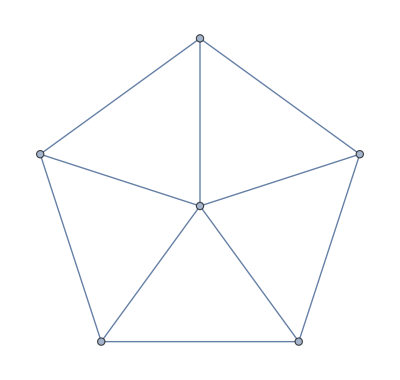

```mathematica
WheelGraph[6]
```

```mathematica
Select[Keys[allGraphs6],IsomorphicGraphQ[WheelGraph[6],allGraphs6[#,"graph"]]&&VertexDegree[allGraphs6[#,"graph"],6]==5&]
```

{6443752,6439540,5393992,5376730,5039860,5026810,2207452,2194402,1857532,1840270,794722,790510}

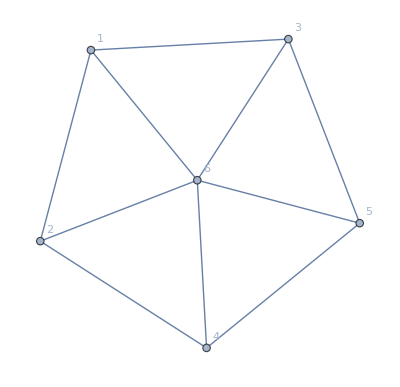
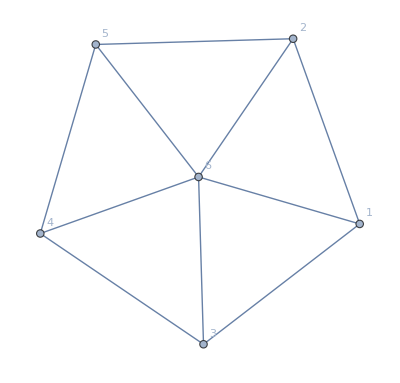
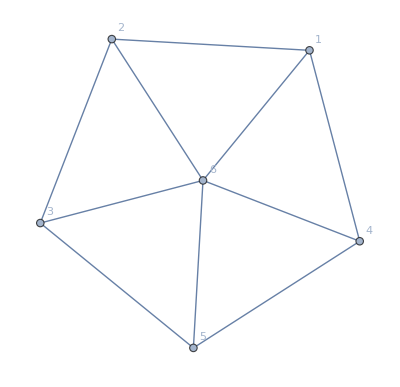
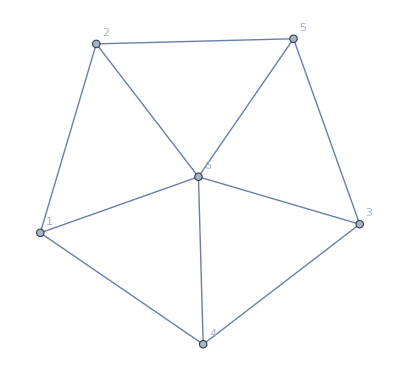
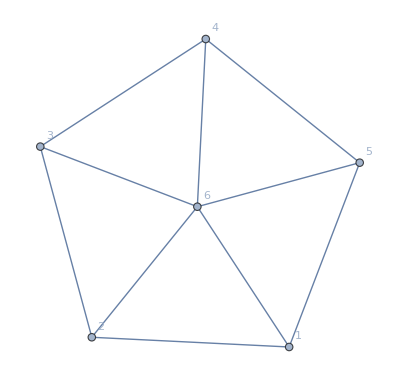
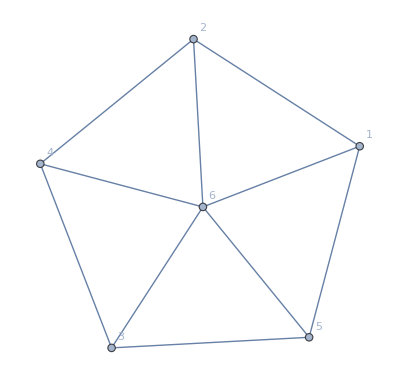
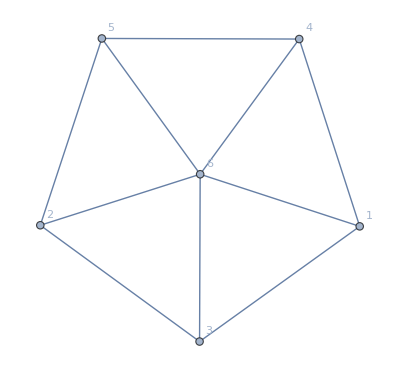
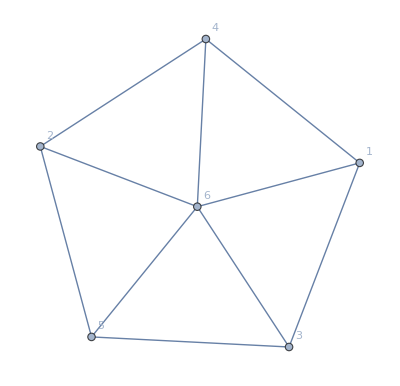
{-Graphics-6443752,-Graphics-6439540,-Graphics-5393992,-Graphics-5376730,-Graphics-5039860,-Graphics-5026810,-Graphics-2207452,-Graphics-2194402,-Graphics-1857532,-Graphics-1840270,-Graphics-794722,-Graphics-790510}

```mathematica
Table[Labeled[Graph[VertexList[allGraphs6[k,"graph"]],EdgeList[allGraphs6[k,"graph"]],VertexLabels->"Name"],Style[k,Green]],{k,Select[Keys[allGraphs6],IsomorphicGraphQ[WheelGraph[6],allGraphs6[#,"graph"]]&&VertexDegree[allGraphs6[#,"graph"],6]==5&]}]
```

```mathematica
allGraphs6[5039860,"colofour"]
```

v13x24x5x6+v13x25x4x6+v13x2x4x5x6+v14x25x3x6+v14x2x35x6+v14x2x3x5x6+v1x24x35x6+v1x24x3x5x6+v1x25x3x4x6+v1x2x35x4x6+v1x2x3x4x5x6

```mathematica
Sort[Table[{Labeled[allGraphs6[k,"graph"],Style[k,Green]],ChromaticPolynomial[allGraphs6[k,"graph"],4]},{k,allGraphs6AtomKeys}],#1[[2]]<#2[[2]]&]
```

{{-Graphics-11957422,0},{-Graphics-8768776,0},{-Graphics-7705894,0},{-Graphics-7351600,0},{-Graphics-7233502,0},{-Graphics-7194136,0},{-Graphics-7181014,0},{-Graphics-7176640,0},{-Graphics-7175182,0},{-Graphics-7174696,0},{-Graphics-7174534,0},{-Graphics-7174480,0},{-Graphics-7174462,0},{-Graphics-7174456,0},{-Graphics-7174454,0},{-Graphics-7174453,0},{-Graphics-14348906,4},{-Graphics-14289097,12},{-Graphics-14169481,12},{-Graphics-14109674,12},{-Graphics-13810649,12},{-Graphics-13750846,12},{-Graphics-13631242,12},{-Graphics-13571441,12},{-Graphics-12734549,12},{-Graphics-12674794,12},{-Graphics-12555286,12},{-Graphics-12495533,12},{-Graphics-12196778,12},{-Graphics-12137029,12},{-Graphics-12017533,12},{-Graphics-11957786,12},{-Graphics-9536777,12},{-Graphics-9478426,12},{-Graphics-9361726,12},{-Graphics-9303377,12},{-Graphics-9011642,12},{-Graphics-8953297,12},{-Graphics-8836609,12},{-Graphics-8778266,12},{-Graphics-7961786,12},{-Graphics-7903489,12},{-Graphics-7786897,12},{-Graphics-7728602,12},{-Graphics-7437137,12},{-Graphics-7378846,12},{-Graphics-7262266,12},{-Graphics-7203977,12},{-Graphics-14109673,24},{-Graphics-13750843,24},{-Graphics-13631233,24},{-Graphics-13571437,24},{-Graphics-13571431,24},{-Graphics-13571429,24},{-Graphics-13571428,24},{-Graphics-12674767,24},{-Graphics-12555205,24},{-Graphics-12495505,24},{-Graphics-12495451,24},{-Graphics-12495425,24},{-Graphics-12495424,24},{-Graphics-12196535,24},{-Graphics-12136999,24},{-Graphics-12136783,24},{-Graphics-12136759,24},{-Graphics-12136756,24},{-Graphics-12017443,24},{-Graphics-12017281,24},{-Graphics-12017209,24},{-Graphics-12017200,24},{-Graphics-11957755,24},{-Graphics-11957695,24},{-Graphics-11957666,24},{-Graphics-11957665,24},{-Graphics-11957531,24},{-Graphics-11957506,24},{-Graphics-11957503,24},{-Graphics-11957458,24},{-Graphics-11957449,24},{-Graphics-11957435,24},{-Graphics-11957431,24},{-Graphics-11957425,24},{-Graphics-11957423,24},{-Graphics-9477697,24},{-Graphics-9359539,24},{-Graphics-9302647,24},{-Graphics-9301189,24},{-Graphics-9300461,24},{-Graphics-9300460,24},{-Graphics-9005081,24},{-Graphics-8952565,24},{-Graphics-8946733,24},{-Graphics-8946007,24},{-Graphics-8946004,24},{-Graphics-8834413,24},{-Graphics-8830039,24},{-Graphics-8827861,24},{-Graphics-8827852,24},{-Graphics-8777533,24},{-Graphics-8776069,24},{-Graphics-8775338,24},{-Graphics-8775337,24},{-Graphics-8771693,24},{-Graphics-8770966,24},{-Graphics-8770963,24},{-Graphics-8769514,24},{-Graphics-8769505,24},{-Graphics-8768789,24},{-Graphics-8768785,24},{-Graphics-8768779,24},{-Graphics-8768777,24},{-Graphics-7942103,24},{-Graphics-7902733,24},{-Graphics-7883779,24},{-Graphics-7883077,24},{-Graphics-7883050,24},{-Graphics-7784629,24},{-Graphics-7767133,24},{-Graphics-7765027,24},{-Graphics-7764946,24},{-Graphics-7727845,24},{-Graphics-7726333,24},{-Graphics-7725578,24},{-Graphics-7725577,24},{-Graphics-7708811,24},{-Graphics-7708108,24},{-Graphics-7708081,24},{-Graphics-7706704,24},{-Graphics-7706623,24},{-Graphics-7706003,24},{-Graphics-7705975,24},{-Graphics-7705921,24},{-Graphics-7705895,24},{-Graphics-7430333,24},{-Graphics-7417211,24},{-Graphics-7410893,24},{-Graphics-7410650,24},{-Graphics-7378087,24},{-Graphics-7372039,24},{-Graphics-7371286,24},{-Graphics-7371283,24},{-Graphics-7358893,24},{-Graphics-7358188,24},{-Graphics-7358161,24},{-Graphics-7352572,24},{-Graphics-7352329,24},{-Graphics-7351873,24},{-Graphics-7351843,24},{-Graphics-7351627,24},{-Graphics-7351603,24},{-Graphics-7259989,24},{-Graphics-7255453,24},{-Graphics-7253194,24},{-Graphics-7253185,24},{-Graphics-7242259,24},{-Graphics-7240144,24},{-Graphics-7240063,24},{-Graphics-7235932,24},{-Graphics-7235689,24},{-Graphics-7233835,24},{-Graphics-7233745,24},{-Graphics-7233583,24},{-Graphics-7233511,24},{-Graphics-7203217,24},{-Graphics-7201699,24},{-Graphics-7200941,24},{-Graphics-7200940,24},{-Graphics-7197161,24},{-Graphics-7196407,24},{-Graphics-7196404,24},{-Graphics-7194901,24},{-Graphics-7194892,24},{-Graphics-7194149,24},{-Graphics-7194145,24},{-Graphics-7194139,24},{-Graphics-7194137,24},{-Graphics-7183943,24},{-Graphics-7183237,24},{-Graphics-7183210,24},{-Graphics-7181827,24},{-Graphics-7181746,24},{-Graphics-7181123,24},{-Graphics-7181095,24},{-Graphics-7181041,24},{-Graphics-7181015,24},{-Graphics-7177613,24},{-Graphics-7177370,24},{-Graphics-7176913,24},{-Graphics-7176883,24},{-Graphics-7176667,24},{-Graphics-7176643,24},{-Graphics-7175515,24},{-Graphics-7175425,24},{-Graphics-7175263,24},{-Graphics-7175191,24},{-Graphics-7174817,24},{-Graphics-7174786,24},{-Graphics-7174726,24},{-Graphics-7174697,24},{-Graphics-7174562,24},{-Graphics-7174537,24},{-Graphics-7174489,24},{-Graphics-7174466,24}}

```mathematica
repReduce6To5=Table[allGraphs6[k,"colofour"]->If[SymbolLevel[allGraphs6[k,"colofour"]]≤4,allGraphs6[k,"colofour"],0],{k,allGraphs6AtomKeys}]
```

{v1x2x3x4x5x6→0,v1x2x3x4x56→0,v1x2x3x46x5→0,v1x2x3x45x6→0,v1x2x3x456→v1x2x3x456,v1x2x36x4x5→0,v1x2x36x45→v1x2x36x45,v1x2x35x4x6→0,v1x2x35x46→v1x2x35x46,v1x2x356x4→v1x2x356x4,v1x2x34x5x6→0,v1x2x34x56→v1x2x34x56,v1x2x346x5→v1x2x346x5,v1x2x345x6→v1x2x345x6,v1x2x3456→v1x2x3456,v1x26x3x4x5→0,v1x26x3x45→v1x26x3x45,v1x26x35x4→v1x26x35x4,v1x26x34x5→v1x26x34x5,v1x26x345→v1x26x345,v1x25x3x4x6→0,v1x25x3x46→v1x25x3x46,v1x25x36x4→v1x25x36x4,v1x25x34x6→v1x25x34x6,v1x25x346→v1x25x346,v1x256x3x4→v1x256x3x4,v1x256x34→v1x256x34,v1x24x3x5x6→0,v1x24x3x56→v1x24x3x56,v1x24x36x5→v1x24x36x5,v1x24x35x6→v1x24x35x6,v1x24x356→v1x24x356,v1x246x3x5→v1x246x3x5,v1x246x35→v1x246x35,v1x245x3x6→v1x245x3x6,v1x245x36→v1x245x36,v1x2456x3→v1x2456x3,v1x23x4x5x6→0,v1x23x4x56→v1x23x4x56,v1x23x46x5→v1x23x46x5,v1x23x45x6→v1x23x45x6,v1x23x456→v1x23x456,v1x236x4x5→v1x236x4x5,v1x236x45→v1x236x45,v1x235x4x6→v1x235x4x6,v1x235x46→v1x235x46,v1x2356x4→v1x2356x4,v1x234x5x6→v1x234x5x6,v1x234x56→v1x234x56,v1x2346x5→v1x2346x5,v1x2345x6→v1x2345x6,v1x23456→v1x23456,v16x2x3x4x5→0,v16x2x3x45→v16x2x3x45,v16x2x35x4→v16x2x35x4,v16x2x34x5→v16x2x34x5,v16x2x345→v16x2x345,v16x25x3x4→v16x25x3x4,v16x25x34→v16x25x34,v16x24x3x5→v16x24x3x5,v16x24x35→v16x24x35,v16x245x3→v16x245x3,v16x23x4x5→v16x23x4x5,v16x23x45→v16x23x45,v16x235x4→v16x235x4,v16x234x5→v16x234x5,v16x2345→v16x2345,v15x2x3x4x6→0,v15x2x3x46→v15x2x3x46,v15x2x36x4→v15x2x36x4,v15x2x34x6→v15x2x34x6,v15x2x346→v15x2x346,v15x26x3x4→v15x26x3x4,v15x26x34→v15x26x34,v15x24x3x6→v15x24x3x6,v15x24x36→v15x24x36,v15x246x3→v15x246x3,v15x23x4x6→v15x23x4x6,v15x23x46→v15x23x46,v15x236x4→v15x236x4,v15x234x6→v15x234x6,v15x2346→v15x2346,v156x2x3x4→v156x2x3x4,v156x2x34→v156x2x34,v156x24x3→v156x24x3,v156x23x4→v156x23x4,v156x234→v156x234,v14x2x3x5x6→0,v14x2x3x56→v14x2x3x56,v14x2x36x5→v14x2x36x5,v14x2x35x6→v14x2x35x6,v14x2x356→v14x2x356,v14x26x3x5→v14x26x3x5,v14x26x35→v14x26x35,v14x25x3x6→v14x25x3x6,v14x25x36→v14x25x36,v14x256x3→v14x256x3,v14x23x5x6→v14x23x5x6,v14x23x56→v14x23x56,v14x236x5→v14x236x5,v14x235x6→v14x235x6,v14x2356→v14x2356,v146x2x3x5→v146x2x3x5,v146x2x35→v146x2x35,v146x25x3→v146x25x3,v146x23x5→v146x23x5,v146x235→v146x235,v145x2x3x6→v145x2x3x6,v145x2x36→v145x2x36,v145x26x3→v145x26x3,v145x23x6→v145x23x6,v145x236→v145x236,v1456x2x3→v1456x2x3,v1456x23→v1456x23,v13x2x4x5x6→0,v13x2x4x56→v13x2x4x56,v13x2x46x5→v13x2x46x5,v13x2x45x6→v13x2x45x6,v13x2x456→v13x2x456,v13x26x4x5→v13x26x4x5,v13x26x45→v13x26x45,v13x25x4x6→v13x25x4x6,v13x25x46→v13x25x46,v13x256x4→v13x256x4,v13x24x5x6→v13x24x5x6,v13x24x56→v13x24x56,v13x246x5→v13x246x5,v13x245x6→v13x245x6,v13x2456→v13x2456,v136x2x4x5→v136x2x4x5,v136x2x45→v136x2x45,v136x25x4→v136x25x4,v136x24x5→v136x24x5,v136x245→v136x245,v135x2x4x6→v135x2x4x6,v135x2x46→v135x2x46,v135x26x4→v135x26x4,v135x24x6→v135x24x6,v135x246→v135x246,v1356x2x4→v1356x2x4,v1356x24→v1356x24,v134x2x5x6→v134x2x5x6,v134x2x56→v134x2x56,v134x26x5→v134x26x5,v134x25x6→v134x25x6,v134x256→v134x256,v1346x2x5→v1346x2x5,v1346x25→v1346x25,v1345x2x6→v1345x2x6,v1345x26→v1345x26,v13456x2→v13456x2,v12x3x4x5x6→0,v12x3x4x56→v12x3x4x56,v12x3x46x5→v12x3x46x5,v12x3x45x6→v12x3x45x6,v12x3x456→v12x3x456,v12x36x4x5→v12x36x4x5,v12x36x45→v12x36x45,v12x35x4x6→v12x35x4x6,v12x35x46→v12x35x46,v12x356x4→v12x356x4,v12x34x5x6→v12x34x5x6,v12x34x56→v12x34x56,v12x346x5→v12x346x5,v12x345x6→v12x345x6,v12x3456→v12x3456,v126x3x4x5→v126x3x4x5,v126x3x45→v126x3x45,v126x35x4→v126x35x4,v126x34x5→v126x34x5,v126x345→v126x345,v125x3x4x6→v125x3x4x6,v125x3x46→v125x3x46,v125x36x4→v125x36x4,v125x34x6→v125x34x6,v125x346→v125x346,v1256x3x4→v1256x3x4,v1256x34→v1256x34,v124x3x5x6→v124x3x5x6,v124x3x56→v124x3x56,v124x36x5→v124x36x5,v124x35x6→v124x35x6,v124x356→v124x356,v1246x3x5→v1246x3x5,v1246x35→v1246x35,v1245x3x6→v1245x3x6,v1245x36→v1245x36,v12456x3→v12456x3,v123x4x5x6→v123x4x5x6,v123x4x56→v123x4x56,v123x46x5→v123x46x5,v123x45x6→v123x45x6,v123x456→v123x456,v1236x4x5→v1236x4x5,v1236x45→v1236x45,v1235x4x6→v1235x4x6,v1235x46→v1235x46,v12356x4→v12356x4,v1234x5x6→v1234x5x6,v1234x56→v1234x56,v12346x5→v12346x5,v12345x6→v12345x6,v123456→v123456}

```mathematica
allGraphs6[5039860,"colofour"]/.repReduce6To5
```

v13x24x5x6+v13x25x4x6+v14x25x3x6+v14x2x35x6+v1x24x35x6

```mathematica
allGraphs6[lambdaKey,"graph"]
```

-Graphics-

```mathematica
allGraphs6[lambdaKey,"colofour"]/.repReduce6To5
```

v124x35x6+v124x36x5+v124x3x5x6+v125x36x4+v125x3x46+v125x3x4x6+v12x35x46+v12x35x4x6+v12x36x4x5+v12x3x46x5+v135x24x6+v135x2x46+v135x2x4x6+v136x24x5+v136x25x4+v136x2x4x5+v13x24x5x6+v13x25x46+v13x25x4x6+v13x2x46x5+v146x25x3+v146x2x35+v146x2x3x5+v14x25x36+v14x25x3x6+v14x2x35x6+v14x2x36x5+v15x24x36+v15x24x3x6+v15x2x36x4+v15x2x3x46+v16x24x35+v16x24x3x5+v16x25x3x4+v16x2x35x4+v1x24x35x6+v1x24x36x5+v1x25x36x4+v1x25x3x46+v1x2x35x46

```mathematica
Table[allGraphs6[k,"colofour"]->If[SymbolLevel[allGraphs6[k,"colofour"]]≤4,allGraphs6[k,"colofour"],0],{k,allGraphs6AtomKeys}]
```

{v1x2x3x4x5x6→0,v1x2x3x4x56→0,v1x2x3x46x5→0,v1x2x3x45x6→0,v1x2x3x456→v1x2x3x456,v1x2x36x4x5→0,v1x2x36x45→v1x2x36x45,v1x2x35x4x6→0,v1x2x35x46→v1x2x35x46,v1x2x356x4→v1x2x356x4,v1x2x34x5x6→0,v1x2x34x56→v1x2x34x56,v1x2x346x5→v1x2x346x5,v1x2x345x6→v1x2x345x6,v1x2x3456→v1x2x3456,v1x26x3x4x5→0,v1x26x3x45→v1x26x3x45,v1x26x35x4→v1x26x35x4,v1x26x34x5→v1x26x34x5,v1x26x345→v1x26x345,v1x25x3x4x6→0,v1x25x3x46→v1x25x3x46,v1x25x36x4→v1x25x36x4,v1x25x34x6→v1x25x34x6,v1x25x346→v1x25x346,v1x256x3x4→v1x256x3x4,v1x256x34→v1x256x34,v1x24x3x5x6→0,v1x24x3x56→v1x24x3x56,v1x24x36x5→v1x24x36x5,v1x24x35x6→v1x24x35x6,v1x24x356→v1x24x356,v1x246x3x5→v1x246x3x5,v1x246x35→v1x246x35,v1x245x3x6→v1x245x3x6,v1x245x36→v1x245x36,v1x2456x3→v1x2456x3,v1x23x4x5x6→0,v1x23x4x56→v1x23x4x56,v1x23x46x5→v1x23x46x5,v1x23x45x6→v1x23x45x6,v1x23x456→v1x23x456,v1x236x4x5→v1x236x4x5,v1x236x45→v1x236x45,v1x235x4x6→v1x235x4x6,v1x235x46→v1x235x46,v1x2356x4→v1x2356x4,v1x234x5x6→v1x234x5x6,v1x234x56→v1x234x56,v1x2346x5→v1x2346x5,v1x2345x6→v1x2345x6,v1x23456→v1x23456,v16x2x3x4x5→0,v16x2x3x45→v16x2x3x45,v16x2x35x4→v16x2x35x4,v16x2x34x5→v16x2x34x5,v16x2x345→v16x2x345,v16x25x3x4→v16x25x3x4,v16x25x34→v16x25x34,v16x24x3x5→v16x24x3x5,v16x24x35→v16x24x35,v16x245x3→v16x245x3,v16x23x4x5→v16x23x4x5,v16x23x45→v16x23x45,v16x235x4→v16x235x4,v16x234x5→v16x234x5,v16x2345→v16x2345,v15x2x3x4x6→0,v15x2x3x46→v15x2x3x46,v15x2x36x4→v15x2x36x4,v15x2x34x6→v15x2x34x6,v15x2x346→v15x2x346,v15x26x3x4→v15x26x3x4,v15x26x34→v15x26x34,v15x24x3x6→v15x24x3x6,v15x24x36→v15x24x36,v15x246x3→v15x246x3,v15x23x4x6→v15x23x4x6,v15x23x46→v15x23x46,v15x236x4→v15x236x4,v15x234x6→v15x234x6,v15x2346→v15x2346,v156x2x3x4→v156x2x3x4,v156x2x34→v156x2x34,v156x24x3→v156x24x3,v156x23x4→v156x23x4,v156x234→v156x234,v14x2x3x5x6→0,v14x2x3x56→v14x2x3x56,v14x2x36x5→v14x2x36x5,v14x2x35x6→v14x2x35x6,v14x2x356→v14x2x356,v14x26x3x5→v14x26x3x5,v14x26x35→v14x26x35,v14x25x3x6→v14x25x3x6,v14x25x36→v14x25x36,v14x256x3→v14x256x3,v14x23x5x6→v14x23x5x6,v14x23x56→v14x23x56,v14x236x5→v14x236x5,v14x235x6→v14x235x6,v14x2356→v14x2356,v146x2x3x5→v146x2x3x5,v146x2x35→v146x2x35,v146x25x3→v146x25x3,v146x23x5→v146x23x5,v146x235→v146x235,v145x2x3x6→v145x2x3x6,v145x2x36→v145x2x36,v145x26x3→v145x26x3,v145x23x6→v145x23x6,v145x236→v145x236,v1456x2x3→v1456x2x3,v1456x23→v1456x23,v13x2x4x5x6→0,v13x2x4x56→v13x2x4x56,v13x2x46x5→v13x2x46x5,v13x2x45x6→v13x2x45x6,v13x2x456→v13x2x456,v13x26x4x5→v13x26x4x5,v13x26x45→v13x26x45,v13x25x4x6→v13x25x4x6,v13x25x46→v13x25x46,v13x256x4→v13x256x4,v13x24x5x6→v13x24x5x6,v13x24x56→v13x24x56,v13x246x5→v13x246x5,v13x245x6→v13x245x6,v13x2456→v13x2456,v136x2x4x5→v136x2x4x5,v136x2x45→v136x2x45,v136x25x4→v136x25x4,v136x24x5→v136x24x5,v136x245→v136x245,v135x2x4x6→v135x2x4x6,v135x2x46→v135x2x46,v135x26x4→v135x26x4,v135x24x6→v135x24x6,v135x246→v135x246,v1356x2x4→v1356x2x4,v1356x24→v1356x24,v134x2x5x6→v134x2x5x6,v134x2x56→v134x2x56,v134x26x5→v134x26x5,v134x25x6→v134x25x6,v134x256→v134x256,v1346x2x5→v1346x2x5,v1346x25→v1346x25,v1345x2x6→v1345x2x6,v1345x26→v1345x26,v13456x2→v13456x2,v12x3x4x5x6→0,v12x3x4x56→v12x3x4x56,v12x3x46x5→v12x3x46x5,v12x3x45x6→v12x3x45x6,v12x3x456→v12x3x456,v12x36x4x5→v12x36x4x5,v12x36x45→v12x36x45,v12x35x4x6→v12x35x4x6,v12x35x46→v12x35x46,v12x356x4→v12x356x4,v12x34x5x6→v12x34x5x6,v12x34x56→v12x34x56,v12x346x5→v12x346x5,v12x345x6→v12x345x6,v12x3456→v12x3456,v126x3x4x5→v126x3x4x5,v126x3x45→v126x3x45,v126x35x4→v126x35x4,v126x34x5→v126x34x5,v126x345→v126x345,v125x3x4x6→v125x3x4x6,v125x3x46→v125x3x46,v125x36x4→v125x36x4,v125x34x6→v125x34x6,v125x346→v125x346,v1256x3x4→v1256x3x4,v1256x34→v1256x34,v124x3x5x6→v124x3x5x6,v124x3x56→v124x3x56,v124x36x5→v124x36x5,v124x35x6→v124x35x6,v124x356→v124x356,v1246x3x5→v1246x3x5,v1246x35→v1246x35,v1245x3x6→v1245x3x6,v1245x36→v1245x36,v12456x3→v12456x3,v123x4x5x6→v123x4x5x6,v123x4x56→v123x4x56,v123x46x5→v123x46x5,v123x45x6→v123x45x6,v123x456→v123x456,v1236x4x5→v1236x4x5,v1236x45→v1236x45,v1235x4x6→v1235x4x6,v1235x46→v1235x46,v12356x4→v12356x4,v1234x5x6→v1234x5x6,v1234x56→v1234x56,v12346x5→v12346x5,v12345x6→v12345x6,v123456→v123456}

```mathematica
Select[allGraphs6AtomKeys,SymbolLevel[allGraphs6[#,"colofour"]]≤4&]//Length
```

187

```mathematica
Table[StirlingS2[6,k],{k,0,6}]//Total
```

203

```mathematica
Table[StirlingS2[6,k],{k,0,4}]//Total
```

187

```mathematica
Table[StirlingS2[7,k],{k,0,4}]//Total
```

715

```mathematica
Table[Table[StirlingS2[m,k],{k,0,4}]//Total,{m,1,10}]
```

{1,2,5,15,51,187,715,2795,11051,43947}

```mathematica
Keys[allGraphs6[0]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofourrealnull}

## Now define the base basic data

```mathematica
Bases6=Association[];
```

```mathematica
Bases6["C"]=Association[];
```

```mathematica
Bases6["C","Colofour"]="colofour";
```

```mathematica
Bases6["E"]=Association[];
```

```mathematica
Bases6["E","Colofour"]="colofourrealnull";
```

```mathematica
allBases6=Keys[Bases6]
```

{C,E}

## Working with Bases6 6

```mathematica
ShowGraph6Least[k_,prop_:"comp"]:=ShowGraph[allGraphs6,k]
```

```mathematica
ShowGraph6Least[0]
```

-Graphics-0

```mathematica
Table[Bases6[base,"AtomKeys"]=Sort[Select[Keys[allGraphs6],Length[ListofVars[allGraphs6[#,Bases6[base,"Colofour"]]]]==1&],MyComp[allGraphs6[#1,Bases6[base,"Colofour"]],allGraphs6[#2,Bases6[base,"Colofour"]]]&]
,{base,allBases6}];
```

```mathematica
Table[Bases6[base,"Variables"]=Table[allGraphs6[k,Bases6[base,"Colofour"]],{k,Bases6[base,"AtomKeys"]}]
,{base,allBases6}];
```

```mathematica
BaseFormula6[key_,base_]:=allGraphs6[key,Bases6[base,"Colofour"]]
```

```mathematica
BaseCoeff6[key_,base_]:=Table[Coefficient[allGraphs6[key,Bases6[base,"Colofour"]],var],{var,Bases6[base,"Variables"]}]
```

```mathematica
ConversionMatrix6[base1_,base2_]:=Table[BaseCoeff6[key1,base2],{key1,Bases6[base1,"AtomKeys"]}]
```

```mathematica
Table[Bases6[base,"AtomKeys"],{base,allBases6}]//Flatten//DeleteDuplicates//Length
```

405

```mathematica
Clear[RepGraph6];RepGraph6[base_]:=RepGraph6[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->ShowGraph6Least[key],{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
Clear[RepKey6];RepKey6[base_]:=RepKey6[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->key,{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
Clear[RepChromial6];RepChromial6[base_]:=RepChromial6[base]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->ChromaticPolynomial[allGraphs6[key,"graph"],x],{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
Clear[RepBase6];RepBase6[base_,base2_]:=RepBase6[base,base2]=Table[allGraphs6[key,Bases6[base,"Colofour"]]->allGraphs6[key,Bases6[base2,"Colofour"]],{key,Bases6[base,"AtomKeys"]}]
```

```mathematica
allGraphs6[5039860,"colofour"]/.RepGraph6["C"]
```

-Graphics-8775337+-Graphics-8770963+-Graphics-7708081+-Graphics-7705975+-Graphics-7181095+-Graphics-8768776+-Graphics-7705894+-Graphics-7181014+-Graphics-7176640+-Graphics-7174534+-Graphics-7174453

```mathematica
(allGraphs6[5039860,"colofour"]/.repReduce6To5)/.RepGraph6["C"]
```

-Graphics-8775337+-Graphics-8770963+-Graphics-7708081+-Graphics-7705975+-Graphics-7181095

## Ad absurdum for 6

```mathematica
triangles=Select[allGraphs6AtomKeys,With[{s=SymbolToSets[allGraphs6[#,"colofour"]]},
Length[s]==3&&HasTrianglePattern[s]
]&]
```

{7181123,7181827,7240144,7706003,7706704,7708108,7708811,7765027,7767133,8770966,8771693,8775338,8776069,8830039,8834413}

```mathematica
Table[ShowGraph6Least[k],{k,triangles}]
```

{-Graphics-7181123,-Graphics-7181827,-Graphics-7240144,-Graphics-7706003,-Graphics-7706704,-Graphics-7708108,-Graphics-7708811,-Graphics-7765027,-Graphics-7767133,-Graphics-8770966,-Graphics-8771693,-Graphics-8775338,-Graphics-8776069,-Graphics-8830039,-Graphics-8834413}

```mathematica
Sort[Tally[Table[allGraphs6[k,"comp"],{k,Keys[allGraphs6]}]]]
```

{{Equal,187},{Greater,39372},{GreaterEqual,13512}}

```mathematica
Table[allGraphs6[k,"comp"]=Equal;allGraphs6[k,"compwhy"]="Ad absurdum";
allGraphs6[k,"atleast"]=0;allGraphs6[k,"atleastwhy"]="Ad absurdum declared to be zero",{k,triangles}]
```

{Ad absurdum declared to be zero,Ad absurdum declared to be zero,Ad absurdum declared to be zero,Ad absurdum declared to be zero,Ad absurdum declared to be zero,Ad absurdum declared to be zero,Ad absurdum declared to be zero,Ad absurdum declared to be zero,Ad absurdum declared to be zero,Ad absurdum declared to be zero,Ad absurdum declared to be zero,Ad absurdum declared to be zero,Ad absurdum declared to be zero,Ad absurdum declared to be zero,Ad absurdum declared to be zero}

```mathematica
PropagateComp6[]:=Block[{leftKey,rightKey,left,right,current,changed=0},
Monitor[
Table[
current = allGraphs6[k];
Table[
leftKey=children[[1]];
rightKey=children[[2]];
left=allGraphs6[leftKey];
right=allGraphs6[rightKey];
If[current["comp"]===GreaterEqual && (left["comp"]===Greater),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (greater propagated from left)";
current["comp"]=Greater;
Print[current["compwhy"]];
changed++;
allGraphs6[k]=current;
];

If[current["comp"]===GreaterEqual && (right["comp"]===Greater),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (greater propagated from right)";
current["comp"]=Greater;
Print[current["compwhy"]];
changed++;
allGraphs6[k]=current;
];

If[current["comp"]===GreaterEqual && (left["comp"]===Equal&&right["comp"]===Equal),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (zero propagated)";
current["comp"]=Equal;
Print[current["compwhy"]];
changed++;
allGraphs6[k]=current;
];
If[current["comp"]===GreaterEqual && (left["comp"]===Equal&&right["comp"]===Greater),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (Greater (right) and zero (left) propagated)";
current["comp"]=Greater;
Print[current["compwhy"]];
changed++;
allGraphs6[k]=current;
];

If[current["comp"]===GreaterEqual && (left["comp"]===Greater&&right["comp"]===Equal),
current["compwhy"]="The relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (Zero (right) and Greater (left) propagated)";
current["comp"]=Greater;
Print[current["compwhy"]];
changed++;
allGraphs6[k]=current;
];

If[current["comp"]===Greater && (left["comp"]===GreaterEqual&&right["comp"]===Equal),
left["compwhy"]="The down relation holds "<> ToString[k]<> "("<>ToString[current["comp"]]<> ")== "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>") (Greater(parent) and zero(right) pushed down to left)";
left["comp"]=Greater;
Print[left["compwhy"]];
changed++;
allGraphs6[children[[1]]]=left;
];

If[current["comp"]===Greater && (left["comp"]===Equal&&right["comp"]===GreaterEqual),
right["compwhy"]="The down relation holds "<> ToString[k]<> "("<> ToString[current["comp"]]<> ") == "<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> " (" <>ToString[right["comp"]]<>") (Greater(parent) and zero(left) pushed down to right)";
right["comp"]=Greater;
Print[right["compwhy"]];
changed++;
allGraphs6[children[[2]]]=right;
]
,{children,allGraphs6[k,"children"]}
]
,
{k,Keys[allGraphs6]}],
k
];
changed
]
```

```mathematica
ShowGraph6Least[7685481]
```

-Graphics-7685481

```mathematica
PropagateComp6[]
```

The down relation holds 7702871(Greater)== 7705787(GreaterEqual) + 7708811 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 7702871(Greater)== 7702979(GreaterEqual) + 7706003 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7686104(GreaterEqual)== 7705787(Greater) + 7725578 (GreaterEqual) (greater propagated from left)

The down relation holds 7686104(Greater)== 7686212(GreaterEqual) + 7706003 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7685454(GreaterEqual)== 7685455(GreaterEqual) + 7686212 (Greater) (greater propagated from right)

The relation holds 7685481(GreaterEqual)== 7685482(GreaterEqual) + 7686212 (Greater) (greater propagated from right)

The relation holds 7685400(GreaterEqual)== 7685481(Greater) + 7705246 (GreaterEqual) (greater propagated from left)

The relation holds 7683915(GreaterEqual)== 7683916(GreaterEqual) + 7686104 (Greater) (greater propagated from right)

The relation holds 7683996(GreaterEqual)== 7683997(GreaterEqual) + 7686212 (Greater) (greater propagated from right)

The relation holds 7684023(GreaterEqual)== 7684024(GreaterEqual) + 7686212 (Greater) (greater propagated from right)

The relation holds 7683942(GreaterEqual)== 7684023(Greater) + 7684105 (GreaterEqual) (greater propagated from left)

The relation holds 7683267(GreaterEqual)== 7685454(Greater) + 7707324 (GreaterEqual) (greater propagated from left)

The relation holds 7683294(GreaterEqual)== 7685481(Greater) + 7707351 (GreaterEqual) (greater propagated from left)

The relation holds 7683296(GreaterEqual)== 7702979(Greater) + 7725578 (GreaterEqual) (greater propagated from left)

The relation holds 7683213(GreaterEqual)== 7685400(Greater) + 7687587 (GreaterEqual) (greater propagated from left)

The down relation holds 7762678(Greater)== 7764865(GreaterEqual) + 7767133 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 7762678(Greater)== 7762759(GreaterEqual) + 7765027 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 7764865(Greater)== 7764946(GreaterEqual) + 7765027 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7745182(GreaterEqual)== 7764865(Greater) + 7784629 (GreaterEqual) (greater propagated from left)

The down relation holds 7745182(Greater)== 7745263(GreaterEqual) + 7765027 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7743076(GreaterEqual)== 7762759(Greater) + 7784629 (GreaterEqual) (greater propagated from left)

The relation holds 7646004(GreaterEqual)== 7705056(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 7646733(GreaterEqual)== 7705785(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 7646814(GreaterEqual)== 7705866(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 7646841(GreaterEqual)== 7705893(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 7646842(GreaterEqual)== 7705894(Equal) + 7764946 (Greater) (greater propagated from right)

The relation holds 7646815(GreaterEqual)== 7705867(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 7646760(GreaterEqual)== 7705812(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 7646761(GreaterEqual)== 7705813(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 7646734(GreaterEqual)== 7705786(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 7646085(GreaterEqual)== 7705137(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 7646112(GreaterEqual)== 7705164(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 7646113(GreaterEqual)== 7705165(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 7646086(GreaterEqual)== 7705138(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 7646031(GreaterEqual)== 7705083(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 7646032(GreaterEqual)== 7705084(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 7646005(GreaterEqual)== 7705057(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 7644627(GreaterEqual)== 7703679(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 7644654(GreaterEqual)== 7703706(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 7644655(GreaterEqual)== 7703707(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 7644628(GreaterEqual)== 7703680(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 7643898(GreaterEqual)== 7702950(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 7643925(GreaterEqual)== 7702977(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 7643926(GreaterEqual)== 7702978(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 7643899(GreaterEqual)== 7702951(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 7626321(GreaterEqual)== 7685373(GreaterEqual) + 7745182 (Greater) (greater propagated from right)

The relation holds 7627050(GreaterEqual)== 7686102(GreaterEqual) + 7745182 (Greater) (greater propagated from right)

The relation holds 7627131(GreaterEqual)== 7686183(GreaterEqual) + 7745263 (Greater) (greater propagated from right)

The relation holds 7627158(GreaterEqual)== 7686210(GreaterEqual) + 7745263 (Greater) (greater propagated from right)

The relation holds 7627159(GreaterEqual)== 7686211(GreaterEqual) + 7745263 (Greater) (greater propagated from right)

The relation holds 7627132(GreaterEqual)== 7686184(GreaterEqual) + 7745263 (Greater) (greater propagated from right)

The relation holds 7627077(GreaterEqual)== 7686129(GreaterEqual) + 7745182 (Greater) (greater propagated from right)

The relation holds 7627078(GreaterEqual)== 7686130(GreaterEqual) + 7745182 (Greater) (greater propagated from right)

The relation holds 7627051(GreaterEqual)== 7686103(GreaterEqual) + 7745182 (Greater) (greater propagated from right)

The relation holds 7626402(GreaterEqual)== 7685454(Greater) + 7745263 (Greater) (greater propagated from left)

The relation holds 7626429(GreaterEqual)== 7685481(Greater) + 7745263 (Greater) (greater propagated from left)

The relation holds 7626430(GreaterEqual)== 7685482(GreaterEqual) + 7745263 (Greater) (greater propagated from right)

The relation holds 7626403(GreaterEqual)== 7685455(GreaterEqual) + 7745263 (Greater) (greater propagated from right)

The relation holds 7626348(GreaterEqual)== 7685400(Greater) + 7745182 (Greater) (greater propagated from left)

The relation holds 7626349(GreaterEqual)== 7685401(GreaterEqual) + 7745182 (Greater) (greater propagated from right)

The relation holds 7626322(GreaterEqual)== 7685374(GreaterEqual) + 7745182 (Greater) (greater propagated from right)

The relation holds 7624944(GreaterEqual)== 7683996(Greater) + 7743076 (Greater) (greater propagated from left)

The relation holds 7624971(GreaterEqual)== 7684023(Greater) + 7743076 (Greater) (greater propagated from left)

The relation holds 7624972(GreaterEqual)== 7684024(GreaterEqual) + 7743076 (Greater) (greater propagated from right)

The relation holds 7624945(GreaterEqual)== 7683997(GreaterEqual) + 7743076 (Greater) (greater propagated from right)

The relation holds 7624215(GreaterEqual)== 7683267(Greater) + 7743076 (Greater) (greater propagated from left)

The relation holds 7624242(GreaterEqual)== 7683294(Greater) + 7743076 (Greater) (greater propagated from left)

The relation holds 7624243(GreaterEqual)== 7683295(GreaterEqual) + 7743076 (Greater) (greater propagated from right)

The relation holds 7624216(GreaterEqual)== 7683268(GreaterEqual) + 7743076 (Greater) (greater propagated from right)

The relation holds 7528629(GreaterEqual)== 7528630(GreaterEqual) + 7705787 (Greater) (greater propagated from right)

The relation holds 7526442(GreaterEqual)== 7528629(Greater) + 7708054 (GreaterEqual) (greater propagated from left)

The relation holds 7525821(GreaterEqual)== 7525822(GreaterEqual) + 7702979 (Greater) (greater propagated from right)

The relation holds 7525740(GreaterEqual)== 7525821(Greater) + 7705246 (GreaterEqual) (greater propagated from left)

The relation holds 7508946(GreaterEqual)== 7528629(Greater) + 7548420 (GreaterEqual) (greater propagated from left)

The relation holds 7509027(GreaterEqual)== 7509028(GreaterEqual) + 7686212 (Greater) (greater propagated from right)

The relation holds 7509054(GreaterEqual)== 7509055(GreaterEqual) + 7686212 (Greater) (greater propagated from right)

The relation holds 7508973(GreaterEqual)== 7509054(Greater) + 7705975 (GreaterEqual) (greater propagated from left)

The relation holds 7508325(GreaterEqual)== 7685481(Greater) + 7862638 (GreaterEqual) (greater propagated from left)

The relation holds 7508244(GreaterEqual)== 7685400(Greater) + 7862638 (GreaterEqual) (greater propagated from left)

The relation holds 7506759(GreaterEqual)== 7683915(Greater) + 7863340 (GreaterEqual) (greater propagated from left)

The relation holds 7506840(GreaterEqual)== 7683996(Greater) + 7863340 (GreaterEqual) (greater propagated from left)

The relation holds 7506867(GreaterEqual)== 7684023(Greater) + 7863367 (GreaterEqual) (greater propagated from left)

The relation holds 7506786(GreaterEqual)== 7683942(Greater) + 7863367 (GreaterEqual) (greater propagated from left)

The relation holds 7506138(GreaterEqual)== 7683294(Greater) + 7862638 (GreaterEqual) (greater propagated from left)

The relation holds 7506057(GreaterEqual)== 7683213(Greater) + 7862638 (GreaterEqual) (greater propagated from left)

The relation holds 7469686(GreaterEqual)== 7646842(Greater) + 7883050 (GreaterEqual) (greater propagated from left)

The relation holds 7469659(GreaterEqual)== 7646815(Greater) + 7883023 (GreaterEqual) (greater propagated from left)

The relation holds 7469605(GreaterEqual)== 7646761(Greater) + 7883050 (GreaterEqual) (greater propagated from left)

The relation holds 7469578(GreaterEqual)== 7646734(Greater) + 7883023 (GreaterEqual) (greater propagated from left)

The relation holds 7468957(GreaterEqual)== 7646113(Greater) + 7882321 (GreaterEqual) (greater propagated from left)

The relation holds 7468876(GreaterEqual)== 7646032(Greater) + 7882321 (GreaterEqual) (greater propagated from left)

The relation holds 7467499(GreaterEqual)== 7644655(Greater) + 7883050 (GreaterEqual) (greater propagated from left)

The relation holds 7467472(GreaterEqual)== 7644628(Greater) + 7883023 (GreaterEqual) (greater propagated from left)

The relation holds 7466770(GreaterEqual)== 7643926(Greater) + 7882321 (GreaterEqual) (greater propagated from left)

The relation holds 7450003(GreaterEqual)== 7627159(Greater) + 7863367 (GreaterEqual) (greater propagated from left)

The relation holds 7449976(GreaterEqual)== 7627132(Greater) + 7863340 (GreaterEqual) (greater propagated from left)

The relation holds 7449922(GreaterEqual)== 7627078(Greater) + 7863367 (GreaterEqual) (greater propagated from left)

The relation holds 7449895(GreaterEqual)== 7627051(Greater) + 7863340 (GreaterEqual) (greater propagated from left)

The relation holds 7449274(GreaterEqual)== 7626430(Greater) + 7862638 (GreaterEqual) (greater propagated from left)

The relation holds 7449193(GreaterEqual)== 7626349(Greater) + 7862638 (GreaterEqual) (greater propagated from left)

The relation holds 7447816(GreaterEqual)== 7624972(Greater) + 7863367 (GreaterEqual) (greater propagated from left)

The relation holds 7447789(GreaterEqual)== 7624945(Greater) + 7863340 (GreaterEqual) (greater propagated from left)

The relation holds 7447087(GreaterEqual)== 7624243(Greater) + 7862638 (GreaterEqual) (greater propagated from left)

The relation holds 6642905(GreaterEqual)== 7174346(GreaterEqual) + 7705787 (Greater) (greater propagated from right)

The relation holds 6642894(GreaterEqual)== 6642895(GreaterEqual) + 6642905 (Greater) (greater propagated from right)

The relation holds 6642893(GreaterEqual)== 7174334(GreaterEqual) + 7705787 (Greater) (greater propagated from right)

The relation holds 6642662(GreaterEqual)== 7174103(GreaterEqual) + 7705787 (Greater) (greater propagated from right)

The relation holds 6642651(GreaterEqual)== 6642894(Greater) + 7174605 (GreaterEqual) (greater propagated from left)

The relation holds 6642162(GreaterEqual)== 6642163(GreaterEqual) + 6642893 (Greater) (greater propagated from right)

The relation holds 6642171(GreaterEqual)== 6642172(GreaterEqual) + 6642905 (Greater) (greater propagated from right)

The relation holds 6642174(GreaterEqual)== 6642175(GreaterEqual) + 6642905 (Greater) (greater propagated from right)

The relation holds 6642165(GreaterEqual)== 6642894(Greater) + 6643651 (GreaterEqual) (greater propagated from left)

The relation holds 6641928(GreaterEqual)== 6642171(Greater) + 7173936 (GreaterEqual) (greater propagated from left)

The relation holds 6641931(GreaterEqual)== 6642174(Greater) + 7173966 (GreaterEqual) (greater propagated from left)

The relation holds 6640704(GreaterEqual)== 6640705(GreaterEqual) + 6642893 (Greater) (greater propagated from right)

The relation holds 6640713(GreaterEqual)== 6640714(GreaterEqual) + 6642905 (Greater) (greater propagated from right)

The relation holds 6640716(GreaterEqual)== 6640717(GreaterEqual) + 6642905 (Greater) (greater propagated from right)

The relation holds 6640707(GreaterEqual)== 6642894(Greater) + 6645172 (GreaterEqual) (greater propagated from left)

The relation holds 6640470(GreaterEqual)== 6640713(Greater) + 7172478 (GreaterEqual) (greater propagated from left)

The relation holds 6640473(GreaterEqual)== 6640716(Greater) + 7172508 (GreaterEqual) (greater propagated from left)

The relation holds 6640464(GreaterEqual)== 6642651(Greater) + 6644929 (GreaterEqual) (greater propagated from left)

The relation holds 6640097(GreaterEqual)== 7171538(GreaterEqual) + 7702979 (Greater) (greater propagated from right)

The relation holds 6640086(GreaterEqual)== 6640087(GreaterEqual) + 6640097 (Greater) (greater propagated from right)

The relation holds 6640085(GreaterEqual)== 7171526(GreaterEqual) + 7702979 (Greater) (greater propagated from right)

The relation holds 6640065(GreaterEqual)== 6640066(GreaterEqual) + 6640097 (Greater) (greater propagated from right)

The relation holds 6640068(GreaterEqual)== 6640069(GreaterEqual) + 6640097 (Greater) (greater propagated from right)

The relation holds 6640059(GreaterEqual)== 6640086(Greater) + 6640843 (GreaterEqual) (greater propagated from left)

The relation holds 6640002(GreaterEqual)== 6640003(GreaterEqual) + 6640085 (Greater) (greater propagated from right)

The relation holds 6640011(GreaterEqual)== 6640012(GreaterEqual) + 6640097 (Greater) (greater propagated from right)

The relation holds 6640014(GreaterEqual)== 6640015(GreaterEqual) + 6640097 (Greater) (greater propagated from right)

The relation holds 6640005(GreaterEqual)== 6640086(Greater) + 6642364 (GreaterEqual) (greater propagated from left)

The down relation holds 6636560(Greater)== 7168001(GreaterEqual) + 7706003 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 6636560(Greater)== 6643121(GreaterEqual) + 7181123 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 6622536(GreaterEqual)== 6622618(GreaterEqual) + 6643121 (Greater) (greater propagated from right)

The relation holds 6622545(GreaterEqual)== 6622627(GreaterEqual) + 6643121 (Greater) (greater propagated from right)

The relation holds 6622299(GreaterEqual)== 6622545(Greater) + 7174726 (GreaterEqual) (greater propagated from left)

The relation holds 6621195(GreaterEqual)== 6621223(GreaterEqual) + 6643121 (Greater) (greater propagated from right)

The relation holds 6620943(GreaterEqual)== 6621195(Greater) + 7174786 (GreaterEqual) (greater propagated from left)

The relation holds 6701968(GreaterEqual)== 7233412(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 6702049(GreaterEqual)== 7233493(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6702058(GreaterEqual)== 7233502(Equal) + 7764946 (Greater) (greater propagated from right)

The relation holds 6701977(GreaterEqual)== 7233421(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 6701806(GreaterEqual)== 7233250(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6701815(GreaterEqual)== 7233259(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6701734(GreaterEqual)== 7233178(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 6699862(GreaterEqual)== 7231306(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 6699871(GreaterEqual)== 7231315(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 6695488(GreaterEqual)== 7226932(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6695497(GreaterEqual)== 7226941(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The down relation holds 6695578(Greater)== 7227022(GreaterEqual) + 7765027 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 6695578(Greater)== 6702139(GreaterEqual) + 7240144 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 6695245(GreaterEqual)== 7226689(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6695254(GreaterEqual)== 7226698(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6583842(GreaterEqual)== 7115283(GreaterEqual) + 7646733 (Greater) (greater propagated from right)

The relation holds 6583923(GreaterEqual)== 7115364(GreaterEqual) + 7646814 (Greater) (greater propagated from right)

The relation holds 6583950(GreaterEqual)== 7115391(GreaterEqual) + 7646841 (Greater) (greater propagated from right)

The relation holds 6583959(GreaterEqual)== 7115400(Equal) + 7646841 (Greater) (greater propagated from right)

The relation holds 6583966(GreaterEqual)== 7174456(Equal) + 7764946 (Greater) (greater propagated from right)

The relation holds 6583960(GreaterEqual)== 7115401(Equal) + 7646842 (Greater) (greater propagated from right)

The relation holds 6583956(GreaterEqual)== 7174446(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6583951(GreaterEqual)== 7115392(GreaterEqual) + 7646842 (Greater) (greater propagated from right)

The relation holds 6583932(GreaterEqual)== 7115373(Equal) + 7646814 (Greater) (greater propagated from right)

The relation holds 6583933(GreaterEqual)== 7115374(Equal) + 7646815 (Greater) (greater propagated from right)

The relation holds 6583924(GreaterEqual)== 7115365(GreaterEqual) + 7646815 (Greater) (greater propagated from right)

The relation holds 6584013(GreaterEqual)== 6643062(GreaterEqual) + 6702139 (Greater) (greater propagated from right)

The relation holds 6584041(GreaterEqual)== 6643090(GreaterEqual) + 6702139 (Greater) (greater propagated from right)

The relation holds 6584016(GreaterEqual)== 6584044(GreaterEqual) + 6643121 (Greater) (greater propagated from right)

The relation holds 6583869(GreaterEqual)== 7115310(GreaterEqual) + 7646760 (Greater) (greater propagated from right)

The relation holds 6583878(GreaterEqual)== 7115319(GreaterEqual) + 7646760 (Greater) (greater propagated from right)

The relation holds 6583885(GreaterEqual)== 7174375(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 6583879(GreaterEqual)== 7115320(GreaterEqual) + 7646761 (Greater) (greater propagated from right)

The relation holds 6583875(GreaterEqual)== 7174365(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 6583870(GreaterEqual)== 7115311(GreaterEqual) + 7646761 (Greater) (greater propagated from right)

The relation holds 6583851(GreaterEqual)== 7115292(GreaterEqual) + 7646733 (Greater) (greater propagated from right)

The relation holds 6583854(GreaterEqual)== 6583935(GreaterEqual) + 6584016 (Greater) (greater propagated from right)

The relation holds 6583852(GreaterEqual)== 7115293(GreaterEqual) + 7646734 (Greater) (greater propagated from right)

The relation holds 6583845(GreaterEqual)== 6642894(Greater) + 7233412 (GreaterEqual) (greater propagated from left)

The relation holds 6583843(GreaterEqual)== 7115284(GreaterEqual) + 7646734 (Greater) (greater propagated from right)

The relation holds 6583680(GreaterEqual)== 7115121(GreaterEqual) + 7646814 (Greater) (greater propagated from right)

The relation holds 6583707(GreaterEqual)== 7115148(GreaterEqual) + 7646841 (Greater) (greater propagated from right)

The relation holds 6583716(GreaterEqual)== 7115157(GreaterEqual) + 7646841 (Greater) (greater propagated from right)

The relation holds 6583717(GreaterEqual)== 7115158(GreaterEqual) + 7646842 (Greater) (greater propagated from right)

The relation holds 6583708(GreaterEqual)== 7115149(GreaterEqual) + 7646842 (Greater) (greater propagated from right)

The relation holds 6583689(GreaterEqual)== 7115130(GreaterEqual) + 7646814 (Greater) (greater propagated from right)

The relation holds 6583696(GreaterEqual)== 7174186(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6583690(GreaterEqual)== 7115131(GreaterEqual) + 7646815 (Greater) (greater propagated from right)

The relation holds 6583686(GreaterEqual)== 7174176(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6583681(GreaterEqual)== 7115122(GreaterEqual) + 7646815 (Greater) (greater propagated from right)

The relation holds 6583635(GreaterEqual)== 7115076(GreaterEqual) + 7646760 (Greater) (greater propagated from right)

The relation holds 6583636(GreaterEqual)== 7115077(GreaterEqual) + 7646761 (Greater) (greater propagated from right)

The relation holds 6583608(GreaterEqual)== 7115049(GreaterEqual) + 7646733 (Greater) (greater propagated from right)

The relation holds 6583611(GreaterEqual)== 6583854(Greater) + 7115646 (GreaterEqual) (greater propagated from left)

The relation holds 6583615(GreaterEqual)== 7174105(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 6583609(GreaterEqual)== 7115050(GreaterEqual) + 7646734 (Greater) (greater propagated from right)

The relation holds 6583113(GreaterEqual)== 7114554(GreaterEqual) + 7646004 (Greater) (greater propagated from right)

The relation holds 6583194(GreaterEqual)== 7114635(GreaterEqual) + 7646085 (Greater) (greater propagated from right)

The relation holds 6583221(GreaterEqual)== 7114662(GreaterEqual) + 7646112 (Greater) (greater propagated from right)

The relation holds 6583230(GreaterEqual)== 7114671(Equal) + 7646112 (Greater) (greater propagated from right)

The relation holds 6583231(GreaterEqual)== 7114672(Equal) + 7646113 (Greater) (greater propagated from right)

The relation holds 6583222(GreaterEqual)== 7114663(GreaterEqual) + 7646113 (Greater) (greater propagated from right)

The relation holds 6583203(GreaterEqual)== 7114644(Equal) + 7646085 (Greater) (greater propagated from right)

The relation holds 6583204(GreaterEqual)== 7114645(Equal) + 7646086 (Greater) (greater propagated from right)

The relation holds 6583195(GreaterEqual)== 7114636(GreaterEqual) + 7646086 (Greater) (greater propagated from right)

The relation holds 6583284(GreaterEqual)== 6642333(GreaterEqual) + 6702139 (Greater) (greater propagated from right)

The relation holds 6583312(GreaterEqual)== 6642361(GreaterEqual) + 6702139 (Greater) (greater propagated from right)

The relation holds 6583287(GreaterEqual)== 6584016(Greater) + 6643822 (GreaterEqual) (greater propagated from left)

The relation holds 6583140(GreaterEqual)== 7114581(GreaterEqual) + 7646031 (Greater) (greater propagated from right)

The relation holds 6583149(GreaterEqual)== 7114590(GreaterEqual) + 7646031 (Greater) (greater propagated from right)

The relation holds 6583150(GreaterEqual)== 7114591(GreaterEqual) + 7646032 (Greater) (greater propagated from right)

The relation holds 6583141(GreaterEqual)== 7114582(GreaterEqual) + 7646032 (Greater) (greater propagated from right)

The relation holds 6583122(GreaterEqual)== 7114563(GreaterEqual) + 7646004 (Greater) (greater propagated from right)

The relation holds 6583125(GreaterEqual)== 6642174(Greater) + 7233421 (GreaterEqual) (greater propagated from left)

The relation holds 6583123(GreaterEqual)== 7114564(GreaterEqual) + 7646005 (Greater) (greater propagated from right)

The relation holds 6583116(GreaterEqual)== 6642165(Greater) + 7233412 (GreaterEqual) (greater propagated from left)

The relation holds 6583114(GreaterEqual)== 7114555(GreaterEqual) + 7646005 (Greater) (greater propagated from right)

The relation holds 6582951(GreaterEqual)== 7114392(GreaterEqual) + 7646085 (Greater) (greater propagated from right)

The relation holds 6582978(GreaterEqual)== 7114419(GreaterEqual) + 7646112 (Greater) (greater propagated from right)

The relation holds 6582987(GreaterEqual)== 7114428(GreaterEqual) + 7646112 (Greater) (greater propagated from right)

The relation holds 6582988(GreaterEqual)== 7114429(GreaterEqual) + 7646113 (Greater) (greater propagated from right)

The relation holds 6582979(GreaterEqual)== 7114420(GreaterEqual) + 7646113 (Greater) (greater propagated from right)

The relation holds 6582960(GreaterEqual)== 7114401(GreaterEqual) + 7646085 (Greater) (greater propagated from right)

The relation holds 6582961(GreaterEqual)== 7114402(GreaterEqual) + 7646086 (Greater) (greater propagated from right)

The relation holds 6582952(GreaterEqual)== 7114393(GreaterEqual) + 7646086 (Greater) (greater propagated from right)

The relation holds 6582906(GreaterEqual)== 7114347(GreaterEqual) + 7646031 (Greater) (greater propagated from right)

The relation holds 6582907(GreaterEqual)== 7114348(GreaterEqual) + 7646032 (Greater) (greater propagated from right)

The relation holds 6582879(GreaterEqual)== 7114320(GreaterEqual) + 7646004 (Greater) (greater propagated from right)

The relation holds 6582882(GreaterEqual)== 6641931(Greater) + 7233178 (GreaterEqual) (greater propagated from left)

The relation holds 6582880(GreaterEqual)== 7114321(GreaterEqual) + 7646005 (Greater) (greater propagated from right)

The relation holds 6581736(GreaterEqual)== 7113177(GreaterEqual) + 7644627 (Greater) (greater propagated from right)

The relation holds 6581763(GreaterEqual)== 7113204(GreaterEqual) + 7644654 (Greater) (greater propagated from right)

The relation holds 6581772(GreaterEqual)== 7113213(GreaterEqual) + 7644654 (Greater) (greater propagated from right)

The relation holds 6581779(GreaterEqual)== 7172269(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 6581773(GreaterEqual)== 7113214(GreaterEqual) + 7644655 (Greater) (greater propagated from right)

The relation holds 6581769(GreaterEqual)== 7172259(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 6581764(GreaterEqual)== 7113205(GreaterEqual) + 7644655 (Greater) (greater propagated from right)

The relation holds 6581745(GreaterEqual)== 7113186(GreaterEqual) + 7644627 (Greater) (greater propagated from right)

The relation holds 6581746(GreaterEqual)== 7113187(GreaterEqual) + 7644628 (Greater) (greater propagated from right)

The relation holds 6581737(GreaterEqual)== 7113178(GreaterEqual) + 7644628 (Greater) (greater propagated from right)

The relation holds 6581667(GreaterEqual)== 6640716(Greater) + 7231234 (GreaterEqual) (greater propagated from left)

The relation holds 6581658(GreaterEqual)== 6640707(Greater) + 7231225 (GreaterEqual) (greater propagated from left)

The relation holds 6581509(GreaterEqual)== 7171999(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 6581499(GreaterEqual)== 7171989(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 6581007(GreaterEqual)== 7112448(GreaterEqual) + 7643898 (Greater) (greater propagated from right)

The relation holds 6581034(GreaterEqual)== 7112475(GreaterEqual) + 7643925 (Greater) (greater propagated from right)

The relation holds 6581043(GreaterEqual)== 7112484(GreaterEqual) + 7643925 (Greater) (greater propagated from right)

The relation holds 6581046(GreaterEqual)== 6581047(GreaterEqual) + 6640097 (Greater) (greater propagated from right)

The relation holds 6581044(GreaterEqual)== 7112485(GreaterEqual) + 7643926 (Greater) (greater propagated from right)

The relation holds 6581037(GreaterEqual)== 6640086(Greater) + 7231306 (GreaterEqual) (greater propagated from left)

The relation holds 6581035(GreaterEqual)== 7112476(GreaterEqual) + 7643926 (Greater) (greater propagated from right)

The relation holds 6581016(GreaterEqual)== 7112457(GreaterEqual) + 7643898 (Greater) (greater propagated from right)

The relation holds 6581019(GreaterEqual)== 6640068(Greater) + 7231315 (GreaterEqual) (greater propagated from left)

The relation holds 6581017(GreaterEqual)== 7112458(GreaterEqual) + 7643899 (Greater) (greater propagated from right)

The relation holds 6581010(GreaterEqual)== 6640059(Greater) + 7231306 (GreaterEqual) (greater propagated from left)

The relation holds 6581008(GreaterEqual)== 7112449(GreaterEqual) + 7643899 (Greater) (greater propagated from right)

The relation holds 6580965(GreaterEqual)== 6640014(Greater) + 7231234 (GreaterEqual) (greater propagated from left)

The relation holds 6580956(GreaterEqual)== 6640005(Greater) + 7231225 (GreaterEqual) (greater propagated from left)

The relation holds 6577362(GreaterEqual)== 7108803(GreaterEqual) + 7646814 (Greater) (greater propagated from right)

The relation holds 6577389(GreaterEqual)== 7108830(GreaterEqual) + 7646841 (Greater) (greater propagated from right)

The relation holds 6577398(GreaterEqual)== 7108839(GreaterEqual) + 7646841 (Greater) (greater propagated from right)

The relation holds 6577399(GreaterEqual)== 7108840(GreaterEqual) + 7646842 (Greater) (greater propagated from right)

The relation holds 6577390(GreaterEqual)== 7108831(GreaterEqual) + 7646842 (Greater) (greater propagated from right)

The relation holds 6577371(GreaterEqual)== 7108812(GreaterEqual) + 7646814 (Greater) (greater propagated from right)

The relation holds 6577372(GreaterEqual)== 7108813(GreaterEqual) + 7646815 (Greater) (greater propagated from right)

The relation holds 6577363(GreaterEqual)== 7108804(GreaterEqual) + 7646815 (Greater) (greater propagated from right)

The relation holds 6577483(GreaterEqual)== 6636532(GreaterEqual) + 7227022 (Greater) (greater propagated from right)

The relation holds 6577320(GreaterEqual)== 6577401(GreaterEqual) + 6577483 (Greater) (greater propagated from right)

The relation holds 6577321(GreaterEqual)== 6577402(GreaterEqual) + 6577483 (Greater) (greater propagated from right)

The relation holds 6577311(GreaterEqual)== 6577392(GreaterEqual) + 6577483 (Greater) (greater propagated from right)

The relation holds 6577312(GreaterEqual)== 6577393(GreaterEqual) + 6577483 (Greater) (greater propagated from right)

The relation holds 6577294(GreaterEqual)== 6577375(GreaterEqual) + 6577483 (Greater) (greater propagated from right)

The relation holds 6577285(GreaterEqual)== 6577366(GreaterEqual) + 6577483 (Greater) (greater propagated from right)

The relation holds 6577119(GreaterEqual)== 7108560(GreaterEqual) + 7646814 (Greater) (greater propagated from right)

The relation holds 6577146(GreaterEqual)== 7108587(GreaterEqual) + 7646841 (Greater) (greater propagated from right)

The relation holds 6577155(GreaterEqual)== 7108596(GreaterEqual) + 7646841 (Greater) (greater propagated from right)

The relation holds 6577156(GreaterEqual)== 7108597(GreaterEqual) + 7646842 (Greater) (greater propagated from right)

The relation holds 6577147(GreaterEqual)== 7108588(GreaterEqual) + 7646842 (Greater) (greater propagated from right)

The relation holds 6577128(GreaterEqual)== 7108569(GreaterEqual) + 7646814 (Greater) (greater propagated from right)

The relation holds 6577129(GreaterEqual)== 7108570(GreaterEqual) + 7646815 (Greater) (greater propagated from right)

The relation holds 6577120(GreaterEqual)== 7108561(GreaterEqual) + 7646815 (Greater) (greater propagated from right)

The relation holds 6577077(GreaterEqual)== 6577320(Greater) + 7115646 (GreaterEqual) (greater propagated from left)

The relation holds 6577078(GreaterEqual)== 6577321(Greater) + 7115647 (GreaterEqual) (greater propagated from left)

The relation holds 6577051(GreaterEqual)== 6577294(Greater) + 7115647 (GreaterEqual) (greater propagated from left)

The relation holds 6576633(GreaterEqual)== 7108074(GreaterEqual) + 7646085 (Greater) (greater propagated from right)

The relation holds 6576660(GreaterEqual)== 7108101(GreaterEqual) + 7646112 (Greater) (greater propagated from right)

The relation holds 6576669(GreaterEqual)== 7108110(GreaterEqual) + 7646112 (Greater) (greater propagated from right)

The relation holds 6576676(GreaterEqual)== 7167166(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6576670(GreaterEqual)== 7108111(GreaterEqual) + 7646113 (Greater) (greater propagated from right)

The relation holds 6576666(GreaterEqual)== 7167156(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6576661(GreaterEqual)== 7108102(GreaterEqual) + 7646113 (Greater) (greater propagated from right)

The relation holds 6576642(GreaterEqual)== 7108083(GreaterEqual) + 7646085 (Greater) (greater propagated from right)

The relation holds 6576643(GreaterEqual)== 7108084(GreaterEqual) + 7646086 (Greater) (greater propagated from right)

The relation holds 6576634(GreaterEqual)== 7108075(GreaterEqual) + 7646086 (Greater) (greater propagated from right)

The relation holds 6576754(GreaterEqual)== 6635803(GreaterEqual) + 7227022 (Greater) (greater propagated from right)

The relation holds 6576591(GreaterEqual)== 6577320(Greater) + 6643660 (GreaterEqual) (greater propagated from left)

The relation holds 6576592(GreaterEqual)== 6577321(Greater) + 6643660 (GreaterEqual) (greater propagated from left)

The relation holds 6576595(GreaterEqual)== 7167085(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 6576582(GreaterEqual)== 6577311(Greater) + 6643651 (GreaterEqual) (greater propagated from left)

The relation holds 6576583(GreaterEqual)== 6577312(Greater) + 6643651 (GreaterEqual) (greater propagated from left)

The relation holds 6576585(GreaterEqual)== 7167075(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 6576565(GreaterEqual)== 6577294(Greater) + 6643660 (GreaterEqual) (greater propagated from left)

The relation holds 6576556(GreaterEqual)== 6577285(Greater) + 6643651 (GreaterEqual) (greater propagated from left)

The relation holds 6576390(GreaterEqual)== 7107831(GreaterEqual) + 7646085 (Greater) (greater propagated from right)

The relation holds 6576417(GreaterEqual)== 7107858(GreaterEqual) + 7646112 (Greater) (greater propagated from right)

The relation holds 6576426(GreaterEqual)== 7107867(GreaterEqual) + 7646112 (Greater) (greater propagated from right)

The relation holds 6576427(GreaterEqual)== 7107868(GreaterEqual) + 7646113 (Greater) (greater propagated from right)

The relation holds 6576418(GreaterEqual)== 7107859(GreaterEqual) + 7646113 (Greater) (greater propagated from right)

The relation holds 6576399(GreaterEqual)== 7107840(GreaterEqual) + 7646085 (Greater) (greater propagated from right)

The relation holds 6576406(GreaterEqual)== 7166896(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6576400(GreaterEqual)== 7107841(GreaterEqual) + 7646086 (Greater) (greater propagated from right)

The relation holds 6576396(GreaterEqual)== 7166886(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6576391(GreaterEqual)== 7107832(GreaterEqual) + 7646086 (Greater) (greater propagated from right)

The relation holds 6576348(GreaterEqual)== 6577077(Greater) + 6643417 (GreaterEqual) (greater propagated from left)

The relation holds 6576349(GreaterEqual)== 6577078(Greater) + 6643417 (GreaterEqual) (greater propagated from left)

The relation holds 6576322(GreaterEqual)== 6577051(Greater) + 6643417 (GreaterEqual) (greater propagated from left)

The relation holds 6576325(GreaterEqual)== 7166815(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 6574489(GreaterEqual)== 7164979(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 6574219(GreaterEqual)== 7164709(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 6564283(GreaterEqual)== 7154773(GreaterEqual) + 7745263 (Greater) (greater propagated from right)

The relation holds 6564202(GreaterEqual)== 7154692(GreaterEqual) + 7745182 (Greater) (greater propagated from right)

The relation holds 6564013(GreaterEqual)== 7154503(GreaterEqual) + 7745263 (Greater) (greater propagated from right)

The relation holds 6563932(GreaterEqual)== 7154422(GreaterEqual) + 7745182 (Greater) (greater propagated from right)

The relation holds 6562096(GreaterEqual)== 7152586(GreaterEqual) + 7743076 (Greater) (greater propagated from right)

The relation holds 6562146(GreaterEqual)== 6621195(Greater) + 7211713 (GreaterEqual) (greater propagated from left)

The relation holds 6561826(GreaterEqual)== 7152316(GreaterEqual) + 7743076 (Greater) (greater propagated from right)

The relation holds 6557638(GreaterEqual)== 6577321(Greater) + 6603646 (GreaterEqual) (greater propagated from left)

The relation holds 6557611(GreaterEqual)== 6577294(Greater) + 6603646 (GreaterEqual) (greater propagated from left)

The relation holds 6556993(GreaterEqual)== 7147483(GreaterEqual) + 7745263 (Greater) (greater propagated from right)

The relation holds 6556909(GreaterEqual)== 6576592(Greater) + 6603646 (GreaterEqual) (greater propagated from left)

The relation holds 6556912(GreaterEqual)== 7147402(GreaterEqual) + 7745182 (Greater) (greater propagated from right)

The relation holds 6556882(GreaterEqual)== 6576565(Greater) + 6602890 (GreaterEqual) (greater propagated from left)

The relation holds 6556723(GreaterEqual)== 7147213(GreaterEqual) + 7745263 (Greater) (greater propagated from right)

The relation holds 6556642(GreaterEqual)== 7147132(GreaterEqual) + 7745182 (Greater) (greater propagated from right)

The relation holds 6555613(GreaterEqual)== 6577483(Greater) + 6605914 (GreaterEqual) (greater propagated from left)

The relation holds 6554806(GreaterEqual)== 7145296(GreaterEqual) + 7743076 (Greater) (greater propagated from right)

The relation holds 6554884(GreaterEqual)== 6576754(Greater) + 6605914 (GreaterEqual) (greater propagated from left)

The relation holds 6554536(GreaterEqual)== 7145026(GreaterEqual) + 7743076 (Greater) (greater propagated from right)

The relation holds 6465744(GreaterEqual)== 6997185(GreaterEqual) + 7528629 (Greater) (greater propagated from right)

The relation holds 6465801(GreaterEqual)== 6465883(GreaterEqual) + 6643121 (Greater) (greater propagated from right)

The relation holds 6465810(GreaterEqual)== 6465892(GreaterEqual) + 6643121 (Greater) (greater propagated from right)

The relation holds 6465753(GreaterEqual)== 6465780(GreaterEqual) + 6465810 (Greater) (greater propagated from right)

The relation holds 6465756(GreaterEqual)== 6465783(GreaterEqual) + 6465810 (Greater) (greater propagated from right)

The relation holds 6465747(GreaterEqual)== 6997188(GreaterEqual) + 7528629 (Greater) (greater propagated from right)

The relation holds 6465564(GreaterEqual)== 6465810(Greater) + 6997579 (GreaterEqual) (greater propagated from left)

The relation holds 6465510(GreaterEqual)== 6465753(Greater) + 6997518 (GreaterEqual) (greater propagated from left)

The relation holds 6465513(GreaterEqual)== 6465756(Greater) + 6997548 (GreaterEqual) (greater propagated from left)

The relation holds 6465504(GreaterEqual)== 6996945(GreaterEqual) + 7528629 (Greater) (greater propagated from right)

The relation holds 6465024(GreaterEqual)== 6642171(Greater) + 7350841 (GreaterEqual) (greater propagated from left)

The relation holds 6465027(GreaterEqual)== 6642174(Greater) + 7350844 (GreaterEqual) (greater propagated from left)

The relation holds 6464784(GreaterEqual)== 6641931(Greater) + 7350601 (GreaterEqual) (greater propagated from left)

The relation holds 6463557(GreaterEqual)== 6994998(GreaterEqual) + 7526442 (Greater) (greater propagated from right)

The relation holds 6463614(GreaterEqual)== 6465801(Greater) + 6645226 (GreaterEqual) (greater propagated from left)

The relation holds 6463623(GreaterEqual)== 6465810(Greater) + 6645226 (GreaterEqual) (greater propagated from left)

The relation holds 6463566(GreaterEqual)== 6640713(Greater) + 7351570 (GreaterEqual) (greater propagated from left)

The relation holds 6463569(GreaterEqual)== 6640716(Greater) + 7351573 (GreaterEqual) (greater propagated from left)

The relation holds 6463560(GreaterEqual)== 6995001(GreaterEqual) + 7526442 (Greater) (greater propagated from right)

The relation holds 6463326(GreaterEqual)== 6640473(Greater) + 7351330 (GreaterEqual) (greater propagated from left)

The relation holds 6463317(GreaterEqual)== 6994758(GreaterEqual) + 7526442 (Greater) (greater propagated from right)

The relation holds 6462936(GreaterEqual)== 6994377(GreaterEqual) + 7525821 (Greater) (greater propagated from right)

The relation holds 6462945(GreaterEqual)== 6462946(GreaterEqual) + 6640097 (Greater) (greater propagated from right)

The relation holds 6462948(GreaterEqual)== 6462949(GreaterEqual) + 6640097 (Greater) (greater propagated from right)

The relation holds 6462939(GreaterEqual)== 6994380(GreaterEqual) + 7525821 (Greater) (greater propagated from right)

The relation holds 6462918(GreaterEqual)== 6640065(Greater) + 7350841 (GreaterEqual) (greater propagated from left)

The relation holds 6462921(GreaterEqual)== 6640068(Greater) + 7350844 (GreaterEqual) (greater propagated from left)

The relation holds 6462855(GreaterEqual)== 6994296(GreaterEqual) + 7525740 (Greater) (greater propagated from right)

The relation holds 6462864(GreaterEqual)== 6640011(Greater) + 7350868 (GreaterEqual) (greater propagated from left)

The relation holds 6462867(GreaterEqual)== 6640014(Greater) + 7350871 (GreaterEqual) (greater propagated from left)

The relation holds 6462858(GreaterEqual)== 6994299(GreaterEqual) + 7525740 (Greater) (greater propagated from right)

The relation holds 6524910(GreaterEqual)== 7056354(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6524829(GreaterEqual)== 7056273(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 6522723(GreaterEqual)== 7054167(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 6406812(GreaterEqual)== 6938253(GreaterEqual) + 7646841 (Greater) (greater propagated from right)

The relation holds 6406819(GreaterEqual)== 6997309(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6406813(GreaterEqual)== 6938254(GreaterEqual) + 7646842 (Greater) (greater propagated from right)

The relation holds 6406804(GreaterEqual)== 6938245(GreaterEqual) + 7469686 (Greater) (greater propagated from right)

The relation holds 6406785(GreaterEqual)== 6938226(GreaterEqual) + 7646814 (Greater) (greater propagated from right)

The relation holds 6406786(GreaterEqual)== 6938227(GreaterEqual) + 7646815 (Greater) (greater propagated from right)

The relation holds 6406777(GreaterEqual)== 6938218(GreaterEqual) + 7469659 (Greater) (greater propagated from right)

The relation holds 6406731(GreaterEqual)== 6938172(GreaterEqual) + 7646760 (Greater) (greater propagated from right)

The relation holds 6406738(GreaterEqual)== 6997228(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 6406732(GreaterEqual)== 6938173(GreaterEqual) + 7646761 (Greater) (greater propagated from right)

The relation holds 6406723(GreaterEqual)== 6938164(GreaterEqual) + 7469605 (Greater) (greater propagated from right)

The relation holds 6406704(GreaterEqual)== 6938145(GreaterEqual) + 7646733 (Greater) (greater propagated from right)

The relation holds 6406707(GreaterEqual)== 6583854(Greater) + 7292523 (GreaterEqual) (greater propagated from left)

The relation holds 6406709(GreaterEqual)== 6938150(GreaterEqual) + 7705787 (Greater) (greater propagated from right)

The relation holds 6406705(GreaterEqual)== 6938146(GreaterEqual) + 7646734 (Greater) (greater propagated from right)

The relation holds 6406698(GreaterEqual)== 6938139(GreaterEqual) + 7528629 (Greater) (greater propagated from right)

The relation holds 6406696(GreaterEqual)== 6938137(GreaterEqual) + 7469578 (Greater) (greater propagated from right)

The relation holds 6406570(GreaterEqual)== 6938011(GreaterEqual) + 7646842 (Greater) (greater propagated from right)

The relation holds 6406561(GreaterEqual)== 6938002(GreaterEqual) + 7469686 (Greater) (greater propagated from right)

The relation holds 6406549(GreaterEqual)== 6997039(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6406543(GreaterEqual)== 6937984(GreaterEqual) + 7646815 (Greater) (greater propagated from right)

The relation holds 6406534(GreaterEqual)== 6937975(GreaterEqual) + 7469659 (Greater) (greater propagated from right)

The relation holds 6406489(GreaterEqual)== 6937930(GreaterEqual) + 7646761 (Greater) (greater propagated from right)

The relation holds 6406468(GreaterEqual)== 6996958(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 6406462(GreaterEqual)== 6937903(GreaterEqual) + 7646734 (Greater) (greater propagated from right)

The relation holds 6406083(GreaterEqual)== 6937524(GreaterEqual) + 7646112 (Greater) (greater propagated from right)

The relation holds 6406084(GreaterEqual)== 6937525(GreaterEqual) + 7646113 (Greater) (greater propagated from right)

The relation holds 6406075(GreaterEqual)== 6937516(GreaterEqual) + 7468957 (Greater) (greater propagated from right)

The relation holds 6406056(GreaterEqual)== 6937497(GreaterEqual) + 7646085 (Greater) (greater propagated from right)

The relation holds 6406057(GreaterEqual)== 6937498(GreaterEqual) + 7646086 (Greater) (greater propagated from right)

The relation holds 6406002(GreaterEqual)== 6937443(GreaterEqual) + 7646031 (Greater) (greater propagated from right)

The relation holds 6406003(GreaterEqual)== 6937444(GreaterEqual) + 7646032 (Greater) (greater propagated from right)

The relation holds 6405994(GreaterEqual)== 6937435(GreaterEqual) + 7468876 (Greater) (greater propagated from right)

The relation holds 6405975(GreaterEqual)== 6937416(GreaterEqual) + 7646004 (Greater) (greater propagated from right)

The relation holds 6405978(GreaterEqual)== 6583125(Greater) + 7291794 (GreaterEqual) (greater propagated from left)

The relation holds 6405976(GreaterEqual)== 6937417(GreaterEqual) + 7646005 (Greater) (greater propagated from right)

The relation holds 6405841(GreaterEqual)== 6937282(GreaterEqual) + 7646113 (Greater) (greater propagated from right)

The relation holds 6405832(GreaterEqual)== 6937273(GreaterEqual) + 7468957 (Greater) (greater propagated from right)

The relation holds 6405760(GreaterEqual)== 6937201(GreaterEqual) + 7646032 (Greater) (greater propagated from right)

The relation holds 6404625(GreaterEqual)== 6936066(GreaterEqual) + 7644654 (Greater) (greater propagated from right)

The relation holds 6404632(GreaterEqual)== 6995122(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 6404626(GreaterEqual)== 6936067(GreaterEqual) + 7644655 (Greater) (greater propagated from right)

The relation holds 6404617(GreaterEqual)== 6936058(GreaterEqual) + 7467499 (Greater) (greater propagated from right)

The relation holds 6404598(GreaterEqual)== 6936039(GreaterEqual) + 7644627 (Greater) (greater propagated from right)

The relation holds 6404599(GreaterEqual)== 6936040(GreaterEqual) + 7644628 (Greater) (greater propagated from right)

The relation holds 6404590(GreaterEqual)== 6936031(GreaterEqual) + 7467472 (Greater) (greater propagated from right)

The relation holds 6404520(GreaterEqual)== 6581667(Greater) + 7292523 (GreaterEqual) (greater propagated from left)

The relation holds 6404511(GreaterEqual)== 6935952(GreaterEqual) + 7526442 (Greater) (greater propagated from right)

The relation holds 6403896(GreaterEqual)== 6935337(GreaterEqual) + 7643925 (Greater) (greater propagated from right)

The relation holds 6403899(GreaterEqual)== 6581046(Greater) + 7291821 (GreaterEqual) (greater propagated from left)

The relation holds 6403901(GreaterEqual)== 6935342(GreaterEqual) + 7702979 (Greater) (greater propagated from right)

The relation holds 6403897(GreaterEqual)== 6935338(GreaterEqual) + 7643926 (Greater) (greater propagated from right)

The relation holds 6403890(GreaterEqual)== 6935331(GreaterEqual) + 7525821 (Greater) (greater propagated from right)

The relation holds 6403888(GreaterEqual)== 6935329(GreaterEqual) + 7466770 (Greater) (greater propagated from right)

The relation holds 6403869(GreaterEqual)== 6935310(GreaterEqual) + 7643898 (Greater) (greater propagated from right)

The relation holds 6403872(GreaterEqual)== 6581019(Greater) + 7291794 (GreaterEqual) (greater propagated from left)

The relation holds 6403870(GreaterEqual)== 6935311(GreaterEqual) + 7643899 (Greater) (greater propagated from right)

The relation holds 6403818(GreaterEqual)== 6580965(Greater) + 7291821 (GreaterEqual) (greater propagated from left)

The relation holds 6403809(GreaterEqual)== 6935250(GreaterEqual) + 7525740 (Greater) (greater propagated from right)

The relation holds 6400252(GreaterEqual)== 6931693(GreaterEqual) + 7646842 (Greater) (greater propagated from right)

The relation holds 6400243(GreaterEqual)== 6931684(GreaterEqual) + 7469686 (Greater) (greater propagated from right)

The relation holds 6400225(GreaterEqual)== 6931666(GreaterEqual) + 7646815 (Greater) (greater propagated from right)

The relation holds 6400216(GreaterEqual)== 6931657(GreaterEqual) + 7469659 (Greater) (greater propagated from right)

The relation holds 6400174(GreaterEqual)== 6577321(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 6400165(GreaterEqual)== 6577312(Greater) + 6813589 (GreaterEqual) (greater propagated from left)

The relation holds 6400147(GreaterEqual)== 6577294(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 6400138(GreaterEqual)== 6577285(Greater) + 6813562 (GreaterEqual) (greater propagated from left)

The relation holds 6400009(GreaterEqual)== 6931450(GreaterEqual) + 7646842 (Greater) (greater propagated from right)

The relation holds 6400000(GreaterEqual)== 6931441(GreaterEqual) + 7469686 (Greater) (greater propagated from right)

The relation holds 6399982(GreaterEqual)== 6931423(GreaterEqual) + 7646815 (Greater) (greater propagated from right)

The relation holds 6399973(GreaterEqual)== 6931414(GreaterEqual) + 7469659 (Greater) (greater propagated from right)

The relation holds 6399931(GreaterEqual)== 6577078(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 6399904(GreaterEqual)== 6577051(Greater) + 7344769 (GreaterEqual) (greater propagated from left)

The relation holds 6399529(GreaterEqual)== 6990019(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6399523(GreaterEqual)== 6930964(GreaterEqual) + 7646113 (Greater) (greater propagated from right)

The relation holds 6399514(GreaterEqual)== 6930955(GreaterEqual) + 7468957 (Greater) (greater propagated from right)

The relation holds 6399445(GreaterEqual)== 6576592(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 6399448(GreaterEqual)== 6989938(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 6399436(GreaterEqual)== 6576583(Greater) + 6812860 (GreaterEqual) (greater propagated from left)

The relation holds 6399418(GreaterEqual)== 6576565(Greater) + 7344283 (GreaterEqual) (greater propagated from left)

The relation holds 6399280(GreaterEqual)== 6930721(GreaterEqual) + 7646113 (Greater) (greater propagated from right)

The relation holds 6399271(GreaterEqual)== 6930712(GreaterEqual) + 7468957 (Greater) (greater propagated from right)

The relation holds 6399259(GreaterEqual)== 6989749(GreaterEqual) + 7764946 (Greater) (greater propagated from right)

The relation holds 6399202(GreaterEqual)== 6576349(Greater) + 7344067 (GreaterEqual) (greater propagated from left)

The relation holds 6399175(GreaterEqual)== 6576322(Greater) + 7344040 (GreaterEqual) (greater propagated from left)

The relation holds 6399178(GreaterEqual)== 6989668(GreaterEqual) + 7764865 (Greater) (greater propagated from right)

The relation holds 6397342(GreaterEqual)== 6987832(GreaterEqual) + 7762759 (Greater) (greater propagated from right)

The relation holds 6387136(GreaterEqual)== 6977626(GreaterEqual) + 7745263 (Greater) (greater propagated from right)

The relation holds 6387055(GreaterEqual)== 6977545(GreaterEqual) + 7745182 (Greater) (greater propagated from right)

The relation holds 6386866(GreaterEqual)== 6977356(GreaterEqual) + 7745263 (Greater) (greater propagated from right)

The relation holds 6386785(GreaterEqual)== 6977275(GreaterEqual) + 7745182 (Greater) (greater propagated from right)

The relation holds 6384949(GreaterEqual)== 6975439(GreaterEqual) + 7743076 (Greater) (greater propagated from right)

The relation holds 6380491(GreaterEqual)== 6557638(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 6380464(GreaterEqual)== 6557611(Greater) + 7325329 (GreaterEqual) (greater propagated from left)

The relation holds 6379846(GreaterEqual)== 6970336(GreaterEqual) + 7745263 (Greater) (greater propagated from right)

The relation holds 6379762(GreaterEqual)== 6556909(Greater) + 7324627 (GreaterEqual) (greater propagated from left)

The relation holds 6379765(GreaterEqual)== 6970255(GreaterEqual) + 7745182 (Greater) (greater propagated from right)

The relation holds 6377659(GreaterEqual)== 6968149(GreaterEqual) + 7743076 (Greater) (greater propagated from right)

The down relation holds 8759300(Greater)== 8765861(GreaterEqual) + 8775338 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 8759300(Greater)== 8762216(GreaterEqual) + 8771693 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 8819104(Greater)== 8825665(GreaterEqual) + 8834413 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 8819104(Greater)== 8821291(GreaterEqual) + 8830039 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 8707509(GreaterEqual)== 8766585(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 8707512(GreaterEqual)== 8766588(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 8707513(GreaterEqual)== 8766589(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 8707510(GreaterEqual)== 8766586(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 8707503(GreaterEqual)== 8707512(Greater) + 8709709 (GreaterEqual) (greater propagated from left)

The relation holds 8707504(GreaterEqual)== 8707513(Greater) + 8709709 (GreaterEqual) (greater propagated from left)

The relation holds 8707501(GreaterEqual)== 8707510(Greater) + 8709709 (GreaterEqual) (greater propagated from left)

The relation holds 8706780(GreaterEqual)== 8765856(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 8706783(GreaterEqual)== 8765859(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 8706784(GreaterEqual)== 8765860(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 8706781(GreaterEqual)== 8765857(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 8706774(GreaterEqual)== 8707503(Greater) + 8767308 (GreaterEqual) (greater propagated from left)

The relation holds 8706775(GreaterEqual)== 8707504(Greater) + 8769496 (GreaterEqual) (greater propagated from left)

The relation holds 8706772(GreaterEqual)== 8707501(Greater) + 8769496 (GreaterEqual) (greater propagated from left)

The relation holds 8703135(GreaterEqual)== 8762211(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 8703138(GreaterEqual)== 8762214(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 8703139(GreaterEqual)== 8762215(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 8703136(GreaterEqual)== 8762212(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 8703129(GreaterEqual)== 8703138(Greater) + 8709709 (GreaterEqual) (greater propagated from left)

The relation holds 8703130(GreaterEqual)== 8703139(Greater) + 8709709 (GreaterEqual) (greater propagated from left)

The relation holds 8703127(GreaterEqual)== 8703136(Greater) + 8709709 (GreaterEqual) (greater propagated from left)

The relation holds 8702406(GreaterEqual)== 8761482(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 8702409(GreaterEqual)== 8761485(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 8702410(GreaterEqual)== 8761486(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 8702407(GreaterEqual)== 8761483(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 8702400(GreaterEqual)== 8703129(Greater) + 8769496 (GreaterEqual) (greater propagated from left)

The relation holds 8702401(GreaterEqual)== 8703130(Greater) + 8769496 (GreaterEqual) (greater propagated from left)

The relation holds 8702398(GreaterEqual)== 8703127(Greater) + 8762932 (GreaterEqual) (greater propagated from left)

The relation holds 8588628(GreaterEqual)== 8588629(GreaterEqual) + 8765861 (Greater) (greater propagated from right)

The relation holds 8588631(GreaterEqual)== 8588632(GreaterEqual) + 8765861 (Greater) (greater propagated from right)

The relation holds 8588622(GreaterEqual)== 8588631(Greater) + 8768056 (GreaterEqual) (greater propagated from left)

The relation holds 8584983(GreaterEqual)== 8584984(GreaterEqual) + 8762216 (Greater) (greater propagated from right)

The relation holds 8584986(GreaterEqual)== 8584987(GreaterEqual) + 8762216 (Greater) (greater propagated from right)

The relation holds 8584977(GreaterEqual)== 8584986(Greater) + 8768785 (GreaterEqual) (greater propagated from left)

The relation holds 8584257(GreaterEqual)== 8584986(Greater) + 8592277 (GreaterEqual) (greater propagated from left)

The relation holds 8584248(GreaterEqual)== 8584977(Greater) + 8592268 (GreaterEqual) (greater propagated from left)

The relation holds 8582796(GreaterEqual)== 8584983(Greater) + 8770960 (GreaterEqual) (greater propagated from left)

The relation holds 8582799(GreaterEqual)== 8584986(Greater) + 8770963 (GreaterEqual) (greater propagated from left)

The relation holds 8582790(GreaterEqual)== 8584977(Greater) + 8764393 (GreaterEqual) (greater propagated from left)

The down relation holds 8582074(Greater)== 8584261(GreaterEqual) + 8770966 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 8648436(GreaterEqual)== 8825665(Greater) + 9005081 (GreaterEqual) (greater propagated from left)

The down relation holds 8648436(Greater)== 8650623(GreaterEqual) + 8830039 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 8532468(GreaterEqual)== 8591544(GreaterEqual) + 8650623 (Greater) (greater propagated from right)

The relation holds 8532471(GreaterEqual)== 8591547(GreaterEqual) + 8650623 (Greater) (greater propagated from right)

The relation holds 8532462(GreaterEqual)== 8532471(Greater) + 8709709 (GreaterEqual) (greater propagated from left)

The relation holds 8531739(GreaterEqual)== 8590815(GreaterEqual) + 8650623 (Greater) (greater propagated from right)

The relation holds 8531742(GreaterEqual)== 8590818(GreaterEqual) + 8650623 (Greater) (greater propagated from right)

The relation holds 8531733(GreaterEqual)== 8532462(Greater) + 8592268 (GreaterEqual) (greater propagated from left)

The relation holds 8530281(GreaterEqual)== 8707509(Greater) + 8886924 (GreaterEqual) (greater propagated from left)

The relation holds 8530284(GreaterEqual)== 8707512(Greater) + 8886927 (GreaterEqual) (greater propagated from left)

The relation holds 8530285(GreaterEqual)== 8707513(Greater) + 8946004 (GreaterEqual) (greater propagated from left)

The relation holds 8530282(GreaterEqual)== 8707510(Greater) + 8946001 (GreaterEqual) (greater propagated from left)

The relation holds 8530275(GreaterEqual)== 8707503(Greater) + 8886927 (GreaterEqual) (greater propagated from left)

The relation holds 8530276(GreaterEqual)== 8707504(Greater) + 8946004 (GreaterEqual) (greater propagated from left)

The relation holds 8530273(GreaterEqual)== 8707501(Greater) + 8946001 (GreaterEqual) (greater propagated from left)

The relation holds 8529552(GreaterEqual)== 8706780(Greater) + 8886195 (GreaterEqual) (greater propagated from left)

The relation holds 8529555(GreaterEqual)== 8706783(Greater) + 8886198 (GreaterEqual) (greater propagated from left)

The relation holds 8529556(GreaterEqual)== 8706784(Greater) + 8945275 (GreaterEqual) (greater propagated from left)

The relation holds 8529557(GreaterEqual)== 8765861(Greater) + 9005081 (GreaterEqual) (greater propagated from left)

The down relation holds 8529557(Greater)== 8532473(GreaterEqual) + 8771693 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 8529553(GreaterEqual)== 8706781(Greater) + 8945272 (GreaterEqual) (greater propagated from left)

The relation holds 8529546(GreaterEqual)== 8706774(Greater) + 8886198 (GreaterEqual) (greater propagated from left)

The relation holds 8529547(GreaterEqual)== 8706775(Greater) + 8945275 (GreaterEqual) (greater propagated from left)

The relation holds 8529544(GreaterEqual)== 8706772(Greater) + 8945272 (GreaterEqual) (greater propagated from left)

The relation holds 8529545(GreaterEqual)== 8529557(Greater) + 8768789 (GreaterEqual) (greater propagated from left)

The relation holds 8525911(GreaterEqual)== 8703139(Greater) + 8939443 (GreaterEqual) (greater propagated from left)

The relation holds 8525908(GreaterEqual)== 8703136(Greater) + 8939440 (GreaterEqual) (greater propagated from left)

The relation holds 8525902(GreaterEqual)== 8703130(Greater) + 8939443 (GreaterEqual) (greater propagated from left)

The relation holds 8525899(GreaterEqual)== 8703127(Greater) + 8939440 (GreaterEqual) (greater propagated from left)

The relation holds 8525182(GreaterEqual)== 8702410(Greater) + 8938714 (GreaterEqual) (greater propagated from left)

The relation holds 8525173(GreaterEqual)== 8702401(Greater) + 8938714 (GreaterEqual) (greater propagated from left)

The relation holds 8230532(GreaterEqual)== 8762216(Greater) + 9300461 (GreaterEqual) (greater propagated from left)

The down relation holds 8230532(Greater)== 8237093(GreaterEqual) + 8775338 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 8230521(GreaterEqual)== 8230522(GreaterEqual) + 8230532 (Greater) (greater propagated from right)

The relation holds 8230520(GreaterEqual)== 8230532(Greater) + 8768789 (GreaterEqual) (greater propagated from left)

The relation holds 8229798(GreaterEqual)== 8229799(GreaterEqual) + 8230532 (Greater) (greater propagated from right)

The relation holds 8229801(GreaterEqual)== 8229802(GreaterEqual) + 8230532 (Greater) (greater propagated from right)

The relation holds 8229792(GreaterEqual)== 8230521(Greater) + 8237812 (GreaterEqual) (greater propagated from left)

The relation holds 8228331(GreaterEqual)== 8228332(GreaterEqual) + 8230520 (Greater) (greater propagated from right)

The relation holds 8228340(GreaterEqual)== 8228341(GreaterEqual) + 8230532 (Greater) (greater propagated from right)

The relation holds 8228343(GreaterEqual)== 8228344(GreaterEqual) + 8230532 (Greater) (greater propagated from right)

The relation holds 8228334(GreaterEqual)== 8230521(Greater) + 8232709 (GreaterEqual) (greater propagated from left)

The relation holds 8289604(GreaterEqual)== 8821291(Greater) + 9359539 (GreaterEqual) (greater propagated from left)

The down relation holds 8289604(Greater)== 8296165(GreaterEqual) + 8834413 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 8178012(GreaterEqual)== 8237088(GreaterEqual) + 8296165 (Greater) (greater propagated from right)

The relation holds 8178015(GreaterEqual)== 8178016(GreaterEqual) + 8237093 (Greater) (greater propagated from right)

The relation holds 8178013(GreaterEqual)== 8237089(GreaterEqual) + 8296165 (Greater) (greater propagated from right)

The relation holds 8178006(GreaterEqual)== 8178015(Greater) + 8709709 (GreaterEqual) (greater propagated from left)

The relation holds 8178004(GreaterEqual)== 8178013(Greater) + 8709709 (GreaterEqual) (greater propagated from left)

The relation holds 8177283(GreaterEqual)== 8236359(GreaterEqual) + 8296165 (Greater) (greater propagated from right)

The relation holds 8177286(GreaterEqual)== 8178015(Greater) + 8237821 (GreaterEqual) (greater propagated from left)

The relation holds 8177284(GreaterEqual)== 8236360(GreaterEqual) + 8296165 (Greater) (greater propagated from right)

The relation holds 8177277(GreaterEqual)== 8178006(Greater) + 8237812 (GreaterEqual) (greater propagated from left)

The relation holds 8177275(GreaterEqual)== 8178004(Greater) + 8237812 (GreaterEqual) (greater propagated from left)

The relation holds 8175828(GreaterEqual)== 8707512(Greater) + 9298272 (GreaterEqual) (greater propagated from left)

The relation holds 8175829(GreaterEqual)== 8707513(Greater) + 9298273 (GreaterEqual) (greater propagated from left)

The relation holds 8175819(GreaterEqual)== 8707503(Greater) + 9298272 (GreaterEqual) (greater propagated from left)

The relation holds 8175820(GreaterEqual)== 8707504(Greater) + 9298273 (GreaterEqual) (greater propagated from left)

The relation holds 8170713(GreaterEqual)== 8170714(GreaterEqual) + 8230520 (Greater) (greater propagated from right)

The relation holds 8171442(GreaterEqual)== 8171443(GreaterEqual) + 8230520 (Greater) (greater propagated from right)

The relation holds 8171451(GreaterEqual)== 8703135(Greater) + 9241380 (GreaterEqual) (greater propagated from left)

The relation holds 8171454(GreaterEqual)== 8703138(Greater) + 9300459 (GreaterEqual) (greater propagated from left)

The relation holds 8171455(GreaterEqual)== 8703139(Greater) + 9300460 (GreaterEqual) (greater propagated from left)

The relation holds 8171452(GreaterEqual)== 8703136(Greater) + 9241381 (GreaterEqual) (greater propagated from left)

The relation holds 8171445(GreaterEqual)== 8703129(Greater) + 9300459 (GreaterEqual) (greater propagated from left)

The relation holds 8171446(GreaterEqual)== 8703130(Greater) + 9300460 (GreaterEqual) (greater propagated from left)

The relation holds 8171443(GreaterEqual)== 8703127(Greater) + 9241381 (GreaterEqual) (greater propagated from left)

The relation holds 8170722(GreaterEqual)== 8702406(Greater) + 9240651 (GreaterEqual) (greater propagated from left)

The relation holds 8170725(GreaterEqual)== 8702409(Greater) + 9299730 (GreaterEqual) (greater propagated from left)

The relation holds 8170726(GreaterEqual)== 8702410(Greater) + 9299731 (GreaterEqual) (greater propagated from left)

The relation holds 8170723(GreaterEqual)== 8702407(Greater) + 9240652 (GreaterEqual) (greater propagated from left)

The relation holds 8170716(GreaterEqual)== 8702400(Greater) + 9299730 (GreaterEqual) (greater propagated from left)

The relation holds 8170717(GreaterEqual)== 8702401(Greater) + 9299731 (GreaterEqual) (greater propagated from left)

The relation holds 8170714(GreaterEqual)== 8702398(Greater) + 9240652 (GreaterEqual) (greater propagated from left)

The relation holds 8059860(GreaterEqual)== 8059861(GreaterEqual) + 8237093 (Greater) (greater propagated from right)

The relation holds 8059863(GreaterEqual)== 8059864(GreaterEqual) + 8237093 (Greater) (greater propagated from right)

The relation holds 8059854(GreaterEqual)== 8059863(Greater) + 8059873 (GreaterEqual) (greater propagated from left)

The relation holds 8059131(GreaterEqual)== 8059860(Greater) + 8060593 (GreaterEqual) (greater propagated from left)

The relation holds 8059134(GreaterEqual)== 8059863(Greater) + 8060593 (GreaterEqual) (greater propagated from left)

The relation holds 8057673(GreaterEqual)== 8059860(Greater) + 8239276 (GreaterEqual) (greater propagated from left)

The relation holds 8057676(GreaterEqual)== 8059863(Greater) + 8239279 (GreaterEqual) (greater propagated from left)

The relation holds 8057667(GreaterEqual)== 8059854(Greater) + 8239279 (GreaterEqual) (greater propagated from left)

The relation holds 8053290(GreaterEqual)== 8053291(GreaterEqual) + 8230520 (Greater) (greater propagated from right)

The relation holds 8053299(GreaterEqual)== 8584983(Greater) + 9300459 (GreaterEqual) (greater propagated from left)

The relation holds 8053302(GreaterEqual)== 8584986(Greater) + 9300459 (GreaterEqual) (greater propagated from left)

The relation holds 8053293(GreaterEqual)== 8584977(Greater) + 9123222 (GreaterEqual) (greater propagated from left)

The relation holds 8052573(GreaterEqual)== 8584257(Greater) + 9299730 (GreaterEqual) (greater propagated from left)

The relation holds 8051103(GreaterEqual)== 8228331(Greater) + 8407747 (GreaterEqual) (greater propagated from left)

The relation holds 8051112(GreaterEqual)== 8582796(Greater) + 9298272 (GreaterEqual) (greater propagated from left)

The relation holds 8051115(GreaterEqual)== 8582799(Greater) + 9298272 (GreaterEqual) (greater propagated from left)

The relation holds 8051106(GreaterEqual)== 8582790(Greater) + 9121035 (GreaterEqual) (greater propagated from left)

The relation holds 8118936(GreaterEqual)== 8650623(Greater) + 9359539 (GreaterEqual) (greater propagated from left)

The relation holds 8000784(GreaterEqual)== 8532468(Greater) + 9241380 (GreaterEqual) (greater propagated from left)

The relation holds 8000787(GreaterEqual)== 8532471(Greater) + 9300459 (GreaterEqual) (greater propagated from left)

The relation holds 8000789(GreaterEqual)== 8532473(Greater) + 9300461 (GreaterEqual) (greater propagated from left)

The relation holds 8000785(GreaterEqual)== 8178013(Greater) + 8946001 (GreaterEqual) (greater propagated from left)

The relation holds 8000778(GreaterEqual)== 8532462(Greater) + 9123222 (GreaterEqual) (greater propagated from left)

The relation holds 8000776(GreaterEqual)== 8178004(Greater) + 8414308 (GreaterEqual) (greater propagated from left)

The relation holds 8000055(GreaterEqual)== 8531739(Greater) + 9240651 (GreaterEqual) (greater propagated from left)

The relation holds 8000058(GreaterEqual)== 8531742(Greater) + 9299730 (GreaterEqual) (greater propagated from left)

The relation holds 8000056(GreaterEqual)== 8177284(Greater) + 8945272 (GreaterEqual) (greater propagated from left)

The relation holds 7998600(GreaterEqual)== 8530284(Greater) + 9298272 (GreaterEqual) (greater propagated from left)

The relation holds 7998601(GreaterEqual)== 8530285(Greater) + 9298273 (GreaterEqual) (greater propagated from left)

The relation holds 7998591(GreaterEqual)== 8530275(Greater) + 9121035 (GreaterEqual) (greater propagated from left)

The relation holds 7998592(GreaterEqual)== 8530276(Greater) + 9121036 (GreaterEqual) (greater propagated from left)

The relation holds 7994227(GreaterEqual)== 8525911(Greater) + 9300460 (GreaterEqual) (greater propagated from left)

The relation holds 7994224(GreaterEqual)== 8525908(Greater) + 9241381 (GreaterEqual) (greater propagated from left)

The relation holds 7994218(GreaterEqual)== 8525902(Greater) + 9123223 (GreaterEqual) (greater propagated from left)

The relation holds 7994215(GreaterEqual)== 8525899(Greater) + 9064144 (GreaterEqual) (greater propagated from left)

The relation holds 7993498(GreaterEqual)== 8525182(Greater) + 9299731 (GreaterEqual) (greater propagated from left)

The relation holds 7993501(GreaterEqual)== 8584261(Greater) + 9359539 (GreaterEqual) (greater propagated from left)

The relation holds 5577215(GreaterEqual)== 7171538(GreaterEqual) + 8765861 (Greater) (greater propagated from right)

The relation holds 5577204(GreaterEqual)== 5577205(GreaterEqual) + 5577215 (Greater) (greater propagated from right)

The relation holds 5577183(GreaterEqual)== 5577184(GreaterEqual) + 5577215 (Greater) (greater propagated from right)

The relation holds 5577186(GreaterEqual)== 5577187(GreaterEqual) + 5577215 (Greater) (greater propagated from right)

The relation holds 5577129(GreaterEqual)== 5577130(GreaterEqual) + 5577215 (Greater) (greater propagated from right)

The relation holds 5577132(GreaterEqual)== 5577133(GreaterEqual) + 5577215 (Greater) (greater propagated from right)

The relation holds 5577123(GreaterEqual)== 5577204(Greater) + 7173805 (GreaterEqual) (greater propagated from left)

The down relation holds 5586584(Greater)== 7180907(GreaterEqual) + 8775338 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 5586584(Greater)== 5586692(GreaterEqual) + 7181123 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 5585931(GreaterEqual)== 5585932(GreaterEqual) + 5586692 (Greater) (greater propagated from right)

The relation holds 5585958(GreaterEqual)== 5585959(GreaterEqual) + 5586692 (Greater) (greater propagated from right)

The relation holds 5585877(GreaterEqual)== 5585958(Greater) + 7180363 (GreaterEqual) (greater propagated from left)

The relation holds 5584494(GreaterEqual)== 5584495(GreaterEqual) + 5586692 (Greater) (greater propagated from right)

The relation holds 5584413(GreaterEqual)== 5584494(Greater) + 7181095 (GreaterEqual) (greater propagated from left)

The relation holds 5573570(GreaterEqual)== 7167893(GreaterEqual) + 8762216 (Greater) (greater propagated from right)

The relation holds 5573559(GreaterEqual)== 5573560(GreaterEqual) + 5573570 (Greater) (greater propagated from right)

The relation holds 5573538(GreaterEqual)== 5573539(GreaterEqual) + 5573570 (Greater) (greater propagated from right)

The relation holds 5573541(GreaterEqual)== 5573542(GreaterEqual) + 5573570 (Greater) (greater propagated from right)

The relation holds 5573532(GreaterEqual)== 5573559(Greater) + 7167910 (GreaterEqual) (greater propagated from left)

The relation holds 5573484(GreaterEqual)== 5573485(GreaterEqual) + 5573570 (Greater) (greater propagated from right)

The relation holds 5573487(GreaterEqual)== 5573488(GreaterEqual) + 5573570 (Greater) (greater propagated from right)

The relation holds 5573478(GreaterEqual)== 5573559(Greater) + 7167973 (GreaterEqual) (greater propagated from left)

The relation holds 5573327(GreaterEqual)== 7167650(GreaterEqual) + 8762216 (Greater) (greater propagated from right)

The relation holds 5573316(GreaterEqual)== 5573559(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 5573295(GreaterEqual)== 5573538(Greater) + 7174665 (GreaterEqual) (greater propagated from left)

The relation holds 5573298(GreaterEqual)== 5573541(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 5573289(GreaterEqual)== 5573532(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 5573241(GreaterEqual)== 5573484(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 5573244(GreaterEqual)== 5573487(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 5573235(GreaterEqual)== 5573478(Greater) + 7174605 (GreaterEqual) (greater propagated from left)

The relation holds 5572836(GreaterEqual)== 5579397(GreaterEqual) + 5585958 (Greater) (greater propagated from right)

The relation holds 5572839(GreaterEqual)== 5572840(GreaterEqual) + 5573570 (Greater) (greater propagated from right)

The relation holds 5572830(GreaterEqual)== 5573559(Greater) + 5580850 (GreaterEqual) (greater propagated from left)

The relation holds 5572809(GreaterEqual)== 5579370(GreaterEqual) + 5585931 (Greater) (greater propagated from right)

The relation holds 5572812(GreaterEqual)== 5573541(Greater) + 5580859 (GreaterEqual) (greater propagated from left)

The relation holds 5572755(GreaterEqual)== 5579316(GreaterEqual) + 5585877 (Greater) (greater propagated from right)

The relation holds 5572758(GreaterEqual)== 5573487(Greater) + 5580778 (GreaterEqual) (greater propagated from left)

The relation holds 5572749(GreaterEqual)== 5573478(Greater) + 5580769 (GreaterEqual) (greater propagated from left)

The relation holds 5572593(GreaterEqual)== 5579154(GreaterEqual) + 5585958 (Greater) (greater propagated from right)

The relation holds 5572596(GreaterEqual)== 5572839(Greater) + 7173966 (GreaterEqual) (greater propagated from left)

The relation holds 5572587(GreaterEqual)== 5573316(Greater) + 5580607 (GreaterEqual) (greater propagated from left)

The relation holds 5572566(GreaterEqual)== 5579127(GreaterEqual) + 5585931 (Greater) (greater propagated from right)

The relation holds 5572569(GreaterEqual)== 5573298(Greater) + 5580616 (GreaterEqual) (greater propagated from left)

The relation holds 5572512(GreaterEqual)== 5579073(GreaterEqual) + 5585877 (Greater) (greater propagated from right)

The relation holds 5572515(GreaterEqual)== 5573244(Greater) + 5580535 (GreaterEqual) (greater propagated from left)

The relation holds 5571378(GreaterEqual)== 5571379(GreaterEqual) + 5573570 (Greater) (greater propagated from right)

The relation holds 5571381(GreaterEqual)== 5571382(GreaterEqual) + 5573570 (Greater) (greater propagated from right)

The relation holds 5571372(GreaterEqual)== 5577933(GreaterEqual) + 5584494 (Greater) (greater propagated from right)

The relation holds 5571351(GreaterEqual)== 5573538(Greater) + 5582287 (GreaterEqual) (greater propagated from left)

The relation holds 5571354(GreaterEqual)== 5573541(Greater) + 5582290 (GreaterEqual) (greater propagated from left)

The relation holds 5571297(GreaterEqual)== 5573484(Greater) + 5582314 (GreaterEqual) (greater propagated from left)

The relation holds 5571300(GreaterEqual)== 5573487(Greater) + 5582317 (GreaterEqual) (greater propagated from left)

The relation holds 5571291(GreaterEqual)== 5577852(GreaterEqual) + 5584413 (Greater) (greater propagated from right)

The relation holds 5571135(GreaterEqual)== 5571378(Greater) + 7172508 (GreaterEqual) (greater propagated from left)

The relation holds 5571138(GreaterEqual)== 5571381(Greater) + 7172508 (GreaterEqual) (greater propagated from left)

The relation holds 5571129(GreaterEqual)== 5577690(GreaterEqual) + 5584494 (Greater) (greater propagated from right)

The relation holds 5571108(GreaterEqual)== 5573295(Greater) + 5582044 (GreaterEqual) (greater propagated from left)

The relation holds 5571111(GreaterEqual)== 5573298(Greater) + 5582047 (GreaterEqual) (greater propagated from left)

The relation holds 5571054(GreaterEqual)== 5573241(Greater) + 5582071 (GreaterEqual) (greater propagated from left)

The relation holds 5571057(GreaterEqual)== 5573244(Greater) + 5582074 (GreaterEqual) (greater propagated from left)

The relation holds 5571048(GreaterEqual)== 5577609(GreaterEqual) + 5584413 (Greater) (greater propagated from right)

The relation holds 5557532(GreaterEqual)== 7151855(GreaterEqual) + 8765861 (Greater) (greater propagated from right)

The relation holds 5557521(GreaterEqual)== 5577204(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5557500(GreaterEqual)== 5577183(Greater) + 7193376 (GreaterEqual) (greater propagated from left)

The relation holds 5557503(GreaterEqual)== 5577186(Greater) + 7193379 (GreaterEqual) (greater propagated from left)

The relation holds 5557446(GreaterEqual)== 5577129(Greater) + 7191864 (GreaterEqual) (greater propagated from left)

The relation holds 5557449(GreaterEqual)== 5577132(Greater) + 7191867 (GreaterEqual) (greater propagated from left)

The relation holds 5557440(GreaterEqual)== 5577123(Greater) + 7191858 (GreaterEqual) (greater propagated from left)

The relation holds 5553887(GreaterEqual)== 7148210(GreaterEqual) + 8762216 (Greater) (greater propagated from right)

The relation holds 5553876(GreaterEqual)== 5573559(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5553855(GreaterEqual)== 5573538(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5553858(GreaterEqual)== 5573541(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 5553849(GreaterEqual)== 5573532(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5553801(GreaterEqual)== 5573484(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5553804(GreaterEqual)== 5573487(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 5553795(GreaterEqual)== 5573478(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5553153(GreaterEqual)== 5572836(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5553156(GreaterEqual)== 5572839(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 5553147(GreaterEqual)== 5572830(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5553126(GreaterEqual)== 5572809(Greater) + 7193376 (GreaterEqual) (greater propagated from left)

The relation holds 5553129(GreaterEqual)== 5572812(Greater) + 7193379 (GreaterEqual) (greater propagated from left)

The relation holds 5553072(GreaterEqual)== 5572755(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5553075(GreaterEqual)== 5572758(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 5553066(GreaterEqual)== 5572749(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5551695(GreaterEqual)== 5571378(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5551698(GreaterEqual)== 5571381(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 5551689(GreaterEqual)== 5571372(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5551668(GreaterEqual)== 5571351(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5551671(GreaterEqual)== 5571354(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 5551614(GreaterEqual)== 5571297(Greater) + 7191864 (GreaterEqual) (greater propagated from left)

The relation holds 5551617(GreaterEqual)== 5571300(Greater) + 7191867 (GreaterEqual) (greater propagated from left)

The relation holds 5551608(GreaterEqual)== 5571291(Greater) + 7191858 (GreaterEqual) (greater propagated from left)

The relation holds 5636965(GreaterEqual)== 7231315(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The down relation holds 5645632(Greater)== 7239982(GreaterEqual) + 8834413 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 5645632(Greater)== 5645713(GreaterEqual) + 7240144 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 5645713(Greater)== 7240063(GreaterEqual) + 8834413 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 5632591(GreaterEqual)== 7226941(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 5632348(GreaterEqual)== 7226698(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 5617282(GreaterEqual)== 7211632(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 5612908(GreaterEqual)== 7207258(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 5518921(GreaterEqual)== 7172293(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 5518863(GreaterEqual)== 7113186(GreaterEqual) + 8707509 (Greater) (greater propagated from right)

The relation holds 5518866(GreaterEqual)== 7113189(GreaterEqual) + 8707512 (Greater) (greater propagated from right)

The relation holds 5518867(GreaterEqual)== 7113190(GreaterEqual) + 8707513 (Greater) (greater propagated from right)

The relation holds 5518864(GreaterEqual)== 7113187(GreaterEqual) + 8707510 (Greater) (greater propagated from right)

The relation holds 5518839(GreaterEqual)== 7172211(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 5518675(GreaterEqual)== 7172047(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 5518593(GreaterEqual)== 7171965(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 5518161(GreaterEqual)== 5518162(GreaterEqual) + 5577215 (Greater) (greater propagated from right)

The relation holds 5518164(GreaterEqual)== 5518165(GreaterEqual) + 5577215 (Greater) (greater propagated from right)

The relation holds 5518155(GreaterEqual)== 5577204(Greater) + 7231306 (GreaterEqual) (greater propagated from left)

The relation holds 5518134(GreaterEqual)== 7112457(GreaterEqual) + 8706780 (Greater) (greater propagated from right)

The relation holds 5518137(GreaterEqual)== 7112460(GreaterEqual) + 8706783 (Greater) (greater propagated from right)

The relation holds 5518138(GreaterEqual)== 7112461(GreaterEqual) + 8706784 (Greater) (greater propagated from right)

The relation holds 5518135(GreaterEqual)== 7112458(GreaterEqual) + 8706781 (Greater) (greater propagated from right)

The relation holds 5518080(GreaterEqual)== 5577129(Greater) + 7231234 (GreaterEqual) (greater propagated from left)

The relation holds 5518083(GreaterEqual)== 5577132(Greater) + 7231234 (GreaterEqual) (greater propagated from left)

The relation holds 5518074(GreaterEqual)== 5577123(Greater) + 7231225 (GreaterEqual) (greater propagated from left)

The relation holds 5527614(GreaterEqual)== 5586663(GreaterEqual) + 5645713 (Greater) (greater propagated from right)

The relation holds 5527641(GreaterEqual)== 5586690(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 5527642(GreaterEqual)== 5586691(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 5527615(GreaterEqual)== 5586664(GreaterEqual) + 5645713 (Greater) (greater propagated from right)

The relation holds 5527560(GreaterEqual)== 5586609(GreaterEqual) + 7239982 (Greater) (greater propagated from right)

The relation holds 5527561(GreaterEqual)== 5586610(GreaterEqual) + 7239982 (Greater) (greater propagated from right)

The relation holds 5526882(GreaterEqual)== 5585931(Greater) + 5645713 (Greater) (greater propagated from left)

The relation holds 5526909(GreaterEqual)== 5585958(Greater) + 7240063 (Greater) (greater propagated from left)

The relation holds 5526910(GreaterEqual)== 5585959(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 5526883(GreaterEqual)== 5585932(GreaterEqual) + 5645713 (Greater) (greater propagated from right)

The relation holds 5526828(GreaterEqual)== 5585877(Greater) + 7239982 (Greater) (greater propagated from left)

The relation holds 5526829(GreaterEqual)== 5585878(GreaterEqual) + 7239982 (Greater) (greater propagated from right)

The relation holds 5525445(GreaterEqual)== 5584494(Greater) + 7237867 (GreaterEqual) (greater propagated from left)

The relation holds 5525446(GreaterEqual)== 5527642(Greater) + 5529838 (GreaterEqual) (greater propagated from left)

The relation holds 5525364(GreaterEqual)== 5584413(Greater) + 7237786 (GreaterEqual) (greater propagated from left)

The relation holds 5525365(GreaterEqual)== 5527561(Greater) + 5529838 (GreaterEqual) (greater propagated from left)

The relation holds 5524714(GreaterEqual)== 5526910(Greater) + 5529838 (GreaterEqual) (greater propagated from left)

The relation holds 5524633(GreaterEqual)== 5526829(Greater) + 5529838 (GreaterEqual) (greater propagated from left)

The relation holds 5514516(GreaterEqual)== 5521077(GreaterEqual) + 5527641 (Greater) (greater propagated from right)

The relation holds 5514519(GreaterEqual)== 5521080(GreaterEqual) + 5527641 (Greater) (greater propagated from right)

The relation holds 5514520(GreaterEqual)== 5521081(Equal) + 5527642 (Greater) (greater propagated from right)

The relation holds 5514517(GreaterEqual)== 5521078(GreaterEqual) + 5527642 (Greater) (greater propagated from right)

The relation holds 5514510(GreaterEqual)== 5573559(Greater) + 7226932 (GreaterEqual) (greater propagated from left)

The relation holds 5514511(GreaterEqual)== 5521072(GreaterEqual) + 5527642 (Greater) (greater propagated from right)

The relation holds 5514508(GreaterEqual)== 5521069(GreaterEqual) + 5527642 (Greater) (greater propagated from right)

The relation holds 5514547(GreaterEqual)== 7167919(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 5514489(GreaterEqual)== 7108812(GreaterEqual) + 8703135 (Greater) (greater propagated from right)

The relation holds 5514492(GreaterEqual)== 7108815(GreaterEqual) + 8703138 (Greater) (greater propagated from right)

The relation holds 5514493(GreaterEqual)== 7108816(GreaterEqual) + 8703139 (Greater) (greater propagated from right)

The relation holds 5514490(GreaterEqual)== 7108813(GreaterEqual) + 8703136 (Greater) (greater propagated from right)

The relation holds 5514435(GreaterEqual)== 5573484(Greater) + 7226860 (GreaterEqual) (greater propagated from left)

The relation holds 5514438(GreaterEqual)== 5573487(Greater) + 7226860 (GreaterEqual) (greater propagated from left)

The relation holds 5514439(GreaterEqual)== 5521000(GreaterEqual) + 5527561 (Greater) (greater propagated from right)

The relation holds 5514436(GreaterEqual)== 5520997(GreaterEqual) + 5527561 (Greater) (greater propagated from right)

The relation holds 5514429(GreaterEqual)== 5573478(Greater) + 7226851 (GreaterEqual) (greater propagated from left)

The relation holds 5514430(GreaterEqual)== 5520991(GreaterEqual) + 5527561 (Greater) (greater propagated from right)

The relation holds 5514427(GreaterEqual)== 5520988(GreaterEqual) + 5527561 (Greater) (greater propagated from right)

The relation holds 5514456(GreaterEqual)== 5514538(GreaterEqual) + 7168001 (Greater) (greater propagated from right)

The relation holds 5514465(GreaterEqual)== 7167837(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 5514273(GreaterEqual)== 5520834(GreaterEqual) + 5527641 (Greater) (greater propagated from right)

The relation holds 5514276(GreaterEqual)== 5520837(GreaterEqual) + 5527641 (Greater) (greater propagated from right)

The relation holds 5514277(GreaterEqual)== 5520838(GreaterEqual) + 5527642 (Greater) (greater propagated from right)

The relation holds 5514274(GreaterEqual)== 5520835(GreaterEqual) + 5527642 (Greater) (greater propagated from right)

The relation holds 5514267(GreaterEqual)== 5573316(Greater) + 7226689 (GreaterEqual) (greater propagated from left)

The relation holds 5514268(GreaterEqual)== 5520829(GreaterEqual) + 5527642 (Greater) (greater propagated from right)

The relation holds 5514265(GreaterEqual)== 5520826(GreaterEqual) + 5527642 (Greater) (greater propagated from right)

The relation holds 5514301(GreaterEqual)== 7167673(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 5514246(GreaterEqual)== 7108569(GreaterEqual) + 8703135 (Greater) (greater propagated from right)

The relation holds 5514249(GreaterEqual)== 7108572(GreaterEqual) + 8703138 (Greater) (greater propagated from right)

The relation holds 5514250(GreaterEqual)== 7108573(GreaterEqual) + 8703139 (Greater) (greater propagated from right)

The relation holds 5514247(GreaterEqual)== 7108570(GreaterEqual) + 8703136 (Greater) (greater propagated from right)

The relation holds 5514192(GreaterEqual)== 5573241(Greater) + 7226617 (GreaterEqual) (greater propagated from left)

The relation holds 5514195(GreaterEqual)== 5573244(Greater) + 7226617 (GreaterEqual) (greater propagated from left)

The relation holds 5514196(GreaterEqual)== 5520757(GreaterEqual) + 5527561 (Greater) (greater propagated from right)

The relation holds 5514193(GreaterEqual)== 5520754(GreaterEqual) + 5527561 (Greater) (greater propagated from right)

The relation holds 5514219(GreaterEqual)== 7167591(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 5513787(GreaterEqual)== 5572836(Greater) + 7226941 (GreaterEqual) (greater propagated from left)

The relation holds 5513790(GreaterEqual)== 5572839(Greater) + 7226941 (GreaterEqual) (greater propagated from left)

The relation holds 5513791(GreaterEqual)== 5520352(GreaterEqual) + 5527642 (Greater) (greater propagated from right)

The relation holds 5513788(GreaterEqual)== 5520349(GreaterEqual) + 5526910 (Greater) (greater propagated from right)

The relation holds 5513781(GreaterEqual)== 5572830(Greater) + 7226932 (GreaterEqual) (greater propagated from left)

The relation holds 5513782(GreaterEqual)== 5520343(GreaterEqual) + 5527642 (Greater) (greater propagated from right)

The relation holds 5513779(GreaterEqual)== 5520340(GreaterEqual) + 5526910 (Greater) (greater propagated from right)

The relation holds 5513760(GreaterEqual)== 7108083(GreaterEqual) + 8702406 (Greater) (greater propagated from right)

The relation holds 5513763(GreaterEqual)== 7108086(GreaterEqual) + 8702409 (Greater) (greater propagated from right)

The relation holds 5513764(GreaterEqual)== 7108087(GreaterEqual) + 8702410 (Greater) (greater propagated from right)

The relation holds 5513761(GreaterEqual)== 7108084(GreaterEqual) + 8702407 (Greater) (greater propagated from right)

The relation holds 5513706(GreaterEqual)== 5572755(Greater) + 7226860 (GreaterEqual) (greater propagated from left)

The relation holds 5513709(GreaterEqual)== 5572758(Greater) + 7226860 (GreaterEqual) (greater propagated from left)

The relation holds 5513710(GreaterEqual)== 5520271(GreaterEqual) + 5527561 (Greater) (greater propagated from right)

The relation holds 5513707(GreaterEqual)== 5520268(GreaterEqual) + 5526829 (Greater) (greater propagated from right)

The relation holds 5513700(GreaterEqual)== 5572749(Greater) + 7226851 (GreaterEqual) (greater propagated from left)

The relation holds 5513701(GreaterEqual)== 5520262(GreaterEqual) + 5527561 (Greater) (greater propagated from right)

The relation holds 5513698(GreaterEqual)== 5520259(GreaterEqual) + 5526829 (Greater) (greater propagated from right)

The relation holds 5513544(GreaterEqual)== 5572593(Greater) + 7226698 (GreaterEqual) (greater propagated from left)

The relation holds 5513547(GreaterEqual)== 5572596(Greater) + 7226698 (GreaterEqual) (greater propagated from left)

The relation holds 5513548(GreaterEqual)== 5520109(GreaterEqual) + 5527642 (Greater) (greater propagated from right)

The relation holds 5513545(GreaterEqual)== 5520106(GreaterEqual) + 5526910 (Greater) (greater propagated from right)

The relation holds 5513538(GreaterEqual)== 5572587(Greater) + 7226689 (GreaterEqual) (greater propagated from left)

The relation holds 5513539(GreaterEqual)== 5520100(GreaterEqual) + 5527642 (Greater) (greater propagated from right)

The relation holds 5513536(GreaterEqual)== 5520097(GreaterEqual) + 5526910 (Greater) (greater propagated from right)

The relation holds 5513517(GreaterEqual)== 7107840(GreaterEqual) + 8702406 (Greater) (greater propagated from right)

The relation holds 5513520(GreaterEqual)== 7107843(GreaterEqual) + 8702409 (Greater) (greater propagated from right)

The relation holds 5513521(GreaterEqual)== 7107844(GreaterEqual) + 8702410 (Greater) (greater propagated from right)

The relation holds 5513518(GreaterEqual)== 7107841(GreaterEqual) + 8702407 (Greater) (greater propagated from right)

The relation holds 5513463(GreaterEqual)== 5572512(Greater) + 7226617 (GreaterEqual) (greater propagated from left)

The relation holds 5513466(GreaterEqual)== 5572515(Greater) + 7226617 (GreaterEqual) (greater propagated from left)

The relation holds 5513467(GreaterEqual)== 5520028(GreaterEqual) + 5527561 (Greater) (greater propagated from right)

The relation holds 5513464(GreaterEqual)== 5520025(GreaterEqual) + 5526829 (Greater) (greater propagated from right)

The relation holds 5512329(GreaterEqual)== 5571378(Greater) + 7224754 (GreaterEqual) (greater propagated from left)

The relation holds 5512332(GreaterEqual)== 5571381(Greater) + 7224754 (GreaterEqual) (greater propagated from left)

The relation holds 5512333(GreaterEqual)== 5518894(GreaterEqual) + 5527642 (Greater) (greater propagated from right)

The relation holds 5512330(GreaterEqual)== 5518891(GreaterEqual) + 5527642 (Greater) (greater propagated from right)

The relation holds 5511604(GreaterEqual)== 5518165(GreaterEqual) + 5527642 (Greater) (greater propagated from right)

The relation holds 5499180(GreaterEqual)== 7093503(GreaterEqual) + 8707509 (Greater) (greater propagated from right)

The relation holds 5499183(GreaterEqual)== 7093506(GreaterEqual) + 8707512 (Greater) (greater propagated from right)

The relation holds 5499184(GreaterEqual)== 7093507(GreaterEqual) + 8707513 (Greater) (greater propagated from right)

The relation holds 5499181(GreaterEqual)== 7093504(GreaterEqual) + 8707510 (Greater) (greater propagated from right)

The relation holds 5498478(GreaterEqual)== 5518161(Greater) + 7135083 (GreaterEqual) (greater propagated from left)

The relation holds 5498481(GreaterEqual)== 5518164(Greater) + 7135086 (GreaterEqual) (greater propagated from left)

The relation holds 5498509(GreaterEqual)== 7151881(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 5498451(GreaterEqual)== 7092774(GreaterEqual) + 8706780 (Greater) (greater propagated from right)

The relation holds 5498454(GreaterEqual)== 7092777(GreaterEqual) + 8706783 (Greater) (greater propagated from right)

The relation holds 5498455(GreaterEqual)== 7092778(GreaterEqual) + 8706784 (Greater) (greater propagated from right)

The relation holds 5498452(GreaterEqual)== 7092775(GreaterEqual) + 8706781 (Greater) (greater propagated from right)

The relation holds 5498427(GreaterEqual)== 7151799(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 5498263(GreaterEqual)== 7151635(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 5498181(GreaterEqual)== 7151553(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 5494833(GreaterEqual)== 5514516(Greater) + 7135083 (GreaterEqual) (greater propagated from left)

The relation holds 5494836(GreaterEqual)== 5514519(Greater) + 7135086 (GreaterEqual) (greater propagated from left)

The relation holds 5494837(GreaterEqual)== 5514520(Greater) + 7135087 (GreaterEqual) (greater propagated from left)

The relation holds 5494834(GreaterEqual)== 5514517(Greater) + 7135084 (GreaterEqual) (greater propagated from left)

The relation holds 5494806(GreaterEqual)== 7089129(GreaterEqual) + 8703135 (Greater) (greater propagated from right)

The relation holds 5494809(GreaterEqual)== 7089132(GreaterEqual) + 8703138 (Greater) (greater propagated from right)

The relation holds 5494810(GreaterEqual)== 7089133(GreaterEqual) + 8703139 (Greater) (greater propagated from right)

The relation holds 5494807(GreaterEqual)== 7089130(GreaterEqual) + 8703136 (Greater) (greater propagated from right)

The relation holds 5494752(GreaterEqual)== 5553801(Greater) + 7207177 (GreaterEqual) (greater propagated from left)

The relation holds 5494755(GreaterEqual)== 5553804(Greater) + 7207177 (GreaterEqual) (greater propagated from left)

The relation holds 5494756(GreaterEqual)== 5514439(Greater) + 7135087 (GreaterEqual) (greater propagated from left)

The relation holds 5494753(GreaterEqual)== 5514436(Greater) + 7135084 (GreaterEqual) (greater propagated from left)

The relation holds 5494104(GreaterEqual)== 5553153(Greater) + 7207258 (GreaterEqual) (greater propagated from left)

The relation holds 5494107(GreaterEqual)== 5553156(Greater) + 7207258 (GreaterEqual) (greater propagated from left)

The relation holds 5494108(GreaterEqual)== 5513791(Greater) + 7135087 (GreaterEqual) (greater propagated from left)

The relation holds 5494105(GreaterEqual)== 5513788(Greater) + 7135084 (GreaterEqual) (greater propagated from left)

The relation holds 5494135(GreaterEqual)== 7147507(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 5494077(GreaterEqual)== 7088400(GreaterEqual) + 8702406 (Greater) (greater propagated from right)

The relation holds 5494080(GreaterEqual)== 7088403(GreaterEqual) + 8702409 (Greater) (greater propagated from right)

The relation holds 5494081(GreaterEqual)== 7088404(GreaterEqual) + 8702410 (Greater) (greater propagated from right)

The relation holds 5494078(GreaterEqual)== 7088401(GreaterEqual) + 8702407 (Greater) (greater propagated from right)

The relation holds 5494023(GreaterEqual)== 5553072(Greater) + 7207177 (GreaterEqual) (greater propagated from left)

The relation holds 5494026(GreaterEqual)== 5553075(Greater) + 7207177 (GreaterEqual) (greater propagated from left)

The relation holds 5494027(GreaterEqual)== 5513710(Greater) + 7135087 (GreaterEqual) (greater propagated from left)

The relation holds 5494024(GreaterEqual)== 5513707(Greater) + 7135084 (GreaterEqual) (greater propagated from left)

The relation holds 5494044(GreaterEqual)== 5514456(Greater) + 7194883 (GreaterEqual) (greater propagated from left)

The relation holds 5494053(GreaterEqual)== 7147425(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 5493889(GreaterEqual)== 7147261(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 5493807(GreaterEqual)== 7147179(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 5492646(GreaterEqual)== 5551695(Greater) + 7205071 (GreaterEqual) (greater propagated from left)

The relation holds 5492649(GreaterEqual)== 5551698(Greater) + 7205071 (GreaterEqual) (greater propagated from left)

The relation holds 5492650(GreaterEqual)== 5512333(Greater) + 7135087 (GreaterEqual) (greater propagated from left)

The relation holds 5492647(GreaterEqual)== 5512330(Greater) + 7135084 (GreaterEqual) (greater propagated from left)

The relation holds 5491921(GreaterEqual)== 5511604(Greater) + 7135087 (GreaterEqual) (greater propagated from left)

The relation holds 5400063(GreaterEqual)== 5400064(GreaterEqual) + 5577215 (Greater) (greater propagated from right)

The relation holds 5400066(GreaterEqual)== 5400067(GreaterEqual) + 5577215 (Greater) (greater propagated from right)

The relation holds 5400057(GreaterEqual)== 5577204(Greater) + 7350871 (GreaterEqual) (greater propagated from left)

The relation holds 5400036(GreaterEqual)== 5577183(Greater) + 7350841 (GreaterEqual) (greater propagated from left)

The relation holds 5400039(GreaterEqual)== 5577186(Greater) + 7350844 (GreaterEqual) (greater propagated from left)

The relation holds 5399985(GreaterEqual)== 6994308(GreaterEqual) + 8588631 (Greater) (greater propagated from right)

The relation holds 5399976(GreaterEqual)== 6994299(GreaterEqual) + 8588622 (Greater) (greater propagated from right)

The relation holds 5409516(GreaterEqual)== 5409517(GreaterEqual) + 5586692 (Greater) (greater propagated from right)

The relation holds 5409543(GreaterEqual)== 5409544(GreaterEqual) + 5586692 (Greater) (greater propagated from right)

The relation holds 5409462(GreaterEqual)== 5409543(Greater) + 5409625 (GreaterEqual) (greater propagated from left)

The relation holds 5408784(GreaterEqual)== 5585931(Greater) + 7357402 (GreaterEqual) (greater propagated from left)

The relation holds 5408811(GreaterEqual)== 5585958(Greater) + 7357429 (GreaterEqual) (greater propagated from left)

The relation holds 5407347(GreaterEqual)== 5584494(Greater) + 7358161 (GreaterEqual) (greater propagated from left)

The relation holds 5407266(GreaterEqual)== 5584413(Greater) + 5763757 (GreaterEqual) (greater propagated from left)

The relation holds 5396418(GreaterEqual)== 5402979(GreaterEqual) + 5409543 (Greater) (greater propagated from right)

The relation holds 5396421(GreaterEqual)== 5402982(GreaterEqual) + 5409543 (Greater) (greater propagated from right)

The relation holds 5396412(GreaterEqual)== 5573559(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 5396391(GreaterEqual)== 5573538(Greater) + 7345009 (GreaterEqual) (greater propagated from left)

The relation holds 5396394(GreaterEqual)== 5573541(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 5396385(GreaterEqual)== 5573532(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 5396472(GreaterEqual)== 5396500(GreaterEqual) + 7168001 (Greater) (greater propagated from right)

The relation holds 5396475(GreaterEqual)== 5396503(GreaterEqual) + 7168001 (Greater) (greater propagated from right)

The relation holds 5396337(GreaterEqual)== 6990660(GreaterEqual) + 8584983 (Greater) (greater propagated from right)

The relation holds 5396340(GreaterEqual)== 6990663(GreaterEqual) + 8584986 (Greater) (greater propagated from right)

The relation holds 5396331(GreaterEqual)== 6990654(GreaterEqual) + 8584977 (Greater) (greater propagated from right)

The relation holds 5396175(GreaterEqual)== 5402736(GreaterEqual) + 5409543 (Greater) (greater propagated from right)

The relation holds 5396178(GreaterEqual)== 5402739(GreaterEqual) + 5409543 (Greater) (greater propagated from right)

The relation holds 5396169(GreaterEqual)== 5573316(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 5396148(GreaterEqual)== 5573295(Greater) + 7344766 (GreaterEqual) (greater propagated from left)

The relation holds 5396151(GreaterEqual)== 5573298(Greater) + 7344769 (GreaterEqual) (greater propagated from left)

The relation holds 5396142(GreaterEqual)== 5573289(Greater) + 7344769 (GreaterEqual) (greater propagated from left)

The relation holds 5396223(GreaterEqual)== 5396475(Greater) + 7174786 (GreaterEqual) (greater propagated from left)

The relation holds 5396094(GreaterEqual)== 6990417(GreaterEqual) + 8584983 (Greater) (greater propagated from right)

The relation holds 5396097(GreaterEqual)== 6990420(GreaterEqual) + 8584986 (Greater) (greater propagated from right)

The relation holds 5396088(GreaterEqual)== 6990411(GreaterEqual) + 8584977 (Greater) (greater propagated from right)

The relation holds 5395689(GreaterEqual)== 5572836(Greater) + 7344307 (GreaterEqual) (greater propagated from left)

The relation holds 5395692(GreaterEqual)== 5572839(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 5395683(GreaterEqual)== 5572830(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 5395665(GreaterEqual)== 5572812(Greater) + 7344283 (GreaterEqual) (greater propagated from left)

The relation holds 5395746(GreaterEqual)== 5396475(Greater) + 5403793 (GreaterEqual) (greater propagated from left)

The relation holds 5395611(GreaterEqual)== 6989934(GreaterEqual) + 8584257 (Greater) (greater propagated from right)

The relation holds 5395602(GreaterEqual)== 6989925(GreaterEqual) + 8584248 (Greater) (greater propagated from right)

The relation holds 5395446(GreaterEqual)== 5572593(Greater) + 7344064 (GreaterEqual) (greater propagated from left)

The relation holds 5395449(GreaterEqual)== 5572596(Greater) + 7344067 (GreaterEqual) (greater propagated from left)

The relation holds 5395440(GreaterEqual)== 5572587(Greater) + 7344067 (GreaterEqual) (greater propagated from left)

The relation holds 5395422(GreaterEqual)== 5572569(Greater) + 7344040 (GreaterEqual) (greater propagated from left)

The relation holds 5395368(GreaterEqual)== 6989691(GreaterEqual) + 8584257 (Greater) (greater propagated from right)

The relation holds 5394231(GreaterEqual)== 5571378(Greater) + 7345036 (GreaterEqual) (greater propagated from left)

The relation holds 5394234(GreaterEqual)== 5571381(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 5394225(GreaterEqual)== 5571372(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 5394204(GreaterEqual)== 5571351(Greater) + 7345009 (GreaterEqual) (greater propagated from left)

The relation holds 5394207(GreaterEqual)== 5571354(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 5394153(GreaterEqual)== 6988476(GreaterEqual) + 8582799 (Greater) (greater propagated from right)

The relation holds 5394144(GreaterEqual)== 6988467(GreaterEqual) + 8582790 (Greater) (greater propagated from right)

The relation holds 5393988(GreaterEqual)== 5571135(Greater) + 7344793 (GreaterEqual) (greater propagated from left)

The relation holds 5393991(GreaterEqual)== 5571138(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 5393982(GreaterEqual)== 5571129(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 5393964(GreaterEqual)== 5571111(Greater) + 7344769 (GreaterEqual) (greater propagated from left)

The relation holds 5393910(GreaterEqual)== 6988233(GreaterEqual) + 8582799 (Greater) (greater propagated from right)

The relation holds 5393901(GreaterEqual)== 6988224(GreaterEqual) + 8582790 (Greater) (greater propagated from right)

The relation holds 5380380(GreaterEqual)== 5400063(Greater) + 7016985 (GreaterEqual) (greater propagated from left)

The relation holds 5380383(GreaterEqual)== 5400066(Greater) + 7016988 (GreaterEqual) (greater propagated from left)

The relation holds 5380374(GreaterEqual)== 5557521(Greater) + 7331188 (GreaterEqual) (greater propagated from left)

The relation holds 5380356(GreaterEqual)== 5557503(Greater) + 7331161 (GreaterEqual) (greater propagated from left)

The relation holds 5380302(GreaterEqual)== 6974625(GreaterEqual) + 8588631 (Greater) (greater propagated from right)

The relation holds 5380293(GreaterEqual)== 6974616(GreaterEqual) + 8588622 (Greater) (greater propagated from right)

The relation holds 5376735(GreaterEqual)== 5396418(Greater) + 7016985 (GreaterEqual) (greater propagated from left)

The relation holds 5376738(GreaterEqual)== 5396421(Greater) + 7016988 (GreaterEqual) (greater propagated from left)

The relation holds 5376729(GreaterEqual)== 5553876(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 5376708(GreaterEqual)== 5553855(Greater) + 7325326 (GreaterEqual) (greater propagated from left)

The relation holds 5376711(GreaterEqual)== 5553858(Greater) + 7325329 (GreaterEqual) (greater propagated from left)

The relation holds 5376702(GreaterEqual)== 5553849(Greater) + 7325329 (GreaterEqual) (greater propagated from left)

The relation holds 5376654(GreaterEqual)== 6970977(GreaterEqual) + 8584983 (Greater) (greater propagated from right)

The relation holds 5376657(GreaterEqual)== 6970980(GreaterEqual) + 8584986 (Greater) (greater propagated from right)

The relation holds 5376648(GreaterEqual)== 6970971(GreaterEqual) + 8584977 (Greater) (greater propagated from right)

The relation holds 5376006(GreaterEqual)== 5553153(Greater) + 7324624 (GreaterEqual) (greater propagated from left)

The relation holds 5376009(GreaterEqual)== 5553156(Greater) + 7324627 (GreaterEqual) (greater propagated from left)

The relation holds 5376000(GreaterEqual)== 5553147(Greater) + 7324627 (GreaterEqual) (greater propagated from left)

The relation holds 5375982(GreaterEqual)== 5553129(Greater) + 7324600 (GreaterEqual) (greater propagated from left)

The relation holds 5375928(GreaterEqual)== 6970251(GreaterEqual) + 8584257 (Greater) (greater propagated from right)

The relation holds 5375919(GreaterEqual)== 6970242(GreaterEqual) + 8584248 (Greater) (greater propagated from right)

The relation holds 5374548(GreaterEqual)== 5551695(Greater) + 7325353 (GreaterEqual) (greater propagated from left)

The relation holds 5374551(GreaterEqual)== 5551698(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 5374542(GreaterEqual)== 5551689(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 5374521(GreaterEqual)== 5551668(Greater) + 7325326 (GreaterEqual) (greater propagated from left)

The relation holds 5374524(GreaterEqual)== 5551671(Greater) + 7325329 (GreaterEqual) (greater propagated from left)

The relation holds 5374602(GreaterEqual)== 5396472(Greater) + 7196401 (GreaterEqual) (greater propagated from left)

The relation holds 5374605(GreaterEqual)== 5396475(Greater) + 7196404 (GreaterEqual) (greater propagated from left)

The relation holds 5374470(GreaterEqual)== 6968793(GreaterEqual) + 8582799 (Greater) (greater propagated from right)

The relation holds 5374461(GreaterEqual)== 6968784(GreaterEqual) + 8582790 (Greater) (greater propagated from right)

The relation holds 5373876(GreaterEqual)== 5395746(Greater) + 7195647 (GreaterEqual) (greater propagated from left)

The relation holds 5459817(GreaterEqual)== 7054167(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 5468565(GreaterEqual)== 5645713(Greater) + 7417211 (GreaterEqual) (greater propagated from left)

The down relation holds 5468565(Greater)== 7062915(GreaterEqual) + 8834413 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 5343879(GreaterEqual)== 6997251(GreaterEqual) + 8650623 (Greater) (greater propagated from right)

The relation holds 5343633(GreaterEqual)== 6997005(GreaterEqual) + 8650623 (Greater) (greater propagated from right)

The relation holds 5341774(GreaterEqual)== 6995146(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 5341716(GreaterEqual)== 6936039(GreaterEqual) + 8707509 (Greater) (greater propagated from right)

The relation holds 5341719(GreaterEqual)== 6936042(GreaterEqual) + 8707512 (Greater) (greater propagated from right)

The relation holds 5341720(GreaterEqual)== 6936043(GreaterEqual) + 8707513 (Greater) (greater propagated from right)

The relation holds 5341717(GreaterEqual)== 6936040(GreaterEqual) + 8707510 (Greater) (greater propagated from right)

The relation holds 5341692(GreaterEqual)== 6995064(GreaterEqual) + 8648436 (Greater) (greater propagated from right)

The relation holds 5341014(GreaterEqual)== 5518161(Greater) + 7291818 (GreaterEqual) (greater propagated from left)

The relation holds 5341017(GreaterEqual)== 5518164(Greater) + 7291821 (GreaterEqual) (greater propagated from left)

The relation holds 5341019(GreaterEqual)== 6935342(GreaterEqual) + 8765861 (Greater) (greater propagated from right)

The relation holds 5341008(GreaterEqual)== 5518155(Greater) + 7291821 (GreaterEqual) (greater propagated from left)

The relation holds 5340987(GreaterEqual)== 6935310(GreaterEqual) + 8706780 (Greater) (greater propagated from right)

The relation holds 5340990(GreaterEqual)== 6935313(GreaterEqual) + 8706783 (Greater) (greater propagated from right)

The relation holds 5340991(GreaterEqual)== 6935314(GreaterEqual) + 8706784 (Greater) (greater propagated from right)

The relation holds 5340988(GreaterEqual)== 6935311(GreaterEqual) + 8706781 (Greater) (greater propagated from right)

The relation holds 5340936(GreaterEqual)== 6935259(GreaterEqual) + 8588631 (Greater) (greater propagated from right)

The relation holds 5340927(GreaterEqual)== 6935250(GreaterEqual) + 8588622 (Greater) (greater propagated from right)

The relation holds 5350467(GreaterEqual)== 5527614(Greater) + 7299084 (GreaterEqual) (greater propagated from left)

The relation holds 5350494(GreaterEqual)== 5527641(Greater) + 7299111 (GreaterEqual) (greater propagated from left)

The relation holds 5350495(GreaterEqual)== 5527642(Greater) + 7358161 (GreaterEqual) (greater propagated from left)

The relation holds 5350496(GreaterEqual)== 5586692(Greater) + 7417211 (GreaterEqual) (greater propagated from left)

The relation holds 5350468(GreaterEqual)== 5527615(Greater) + 7358134 (GreaterEqual) (greater propagated from left)

The relation holds 5350413(GreaterEqual)== 5527560(Greater) + 5704707 (GreaterEqual) (greater propagated from left)

The relation holds 5350414(GreaterEqual)== 5527561(Greater) + 5763757 (GreaterEqual) (greater propagated from left)

The relation holds 5349735(GreaterEqual)== 5526882(Greater) + 7298352 (GreaterEqual) (greater propagated from left)

The relation holds 5349762(GreaterEqual)== 5526909(Greater) + 7298379 (GreaterEqual) (greater propagated from left)

The relation holds 5349763(GreaterEqual)== 5526910(Greater) + 7357429 (GreaterEqual) (greater propagated from left)

The relation holds 5349736(GreaterEqual)== 5526883(Greater) + 7357402 (GreaterEqual) (greater propagated from left)

The relation holds 5348298(GreaterEqual)== 5525445(Greater) + 7299111 (GreaterEqual) (greater propagated from left)

The relation holds 5348299(GreaterEqual)== 5525446(Greater) + 7358161 (GreaterEqual) (greater propagated from left)

The relation holds 5348217(GreaterEqual)== 5525364(Greater) + 5704707 (GreaterEqual) (greater propagated from left)

The relation holds 5348218(GreaterEqual)== 5525365(Greater) + 5763757 (GreaterEqual) (greater propagated from left)

The relation holds 5347567(GreaterEqual)== 5524714(Greater) + 7357429 (GreaterEqual) (greater propagated from left)

The relation holds 5337373(GreaterEqual)== 5514520(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 5337370(GreaterEqual)== 5514517(Greater) + 7345036 (GreaterEqual) (greater propagated from left)

The relation holds 5337364(GreaterEqual)== 5514511(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 5337361(GreaterEqual)== 5514508(Greater) + 7345036 (GreaterEqual) (greater propagated from left)

The relation holds 5337400(GreaterEqual)== 6990772(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 5337346(GreaterEqual)== 6931669(GreaterEqual) + 8703139 (Greater) (greater propagated from right)

The relation holds 5337343(GreaterEqual)== 6931666(GreaterEqual) + 8703136 (Greater) (greater propagated from right)

The relation holds 5337451(GreaterEqual)== 5396500(GreaterEqual) + 7227022 (Greater) (greater propagated from right)

The relation holds 5337454(GreaterEqual)== 5396503(GreaterEqual) + 7227022 (Greater) (greater propagated from right)

The relation holds 5337292(GreaterEqual)== 5514439(Greater) + 5750635 (GreaterEqual) (greater propagated from left)

The relation holds 5337289(GreaterEqual)== 5514436(Greater) + 5750632 (GreaterEqual) (greater propagated from left)

The relation holds 5337283(GreaterEqual)== 5514430(Greater) + 5750635 (GreaterEqual) (greater propagated from left)

The relation holds 5337280(GreaterEqual)== 5514427(Greater) + 5750632 (GreaterEqual) (greater propagated from left)

The relation holds 5337130(GreaterEqual)== 5514277(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 5337127(GreaterEqual)== 5514274(Greater) + 7344793 (GreaterEqual) (greater propagated from left)

The relation holds 5337121(GreaterEqual)== 5514268(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 5337118(GreaterEqual)== 5514265(Greater) + 7344793 (GreaterEqual) (greater propagated from left)

The relation holds 5337154(GreaterEqual)== 6990526(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 5337103(GreaterEqual)== 6931426(GreaterEqual) + 8703139 (Greater) (greater propagated from right)

The relation holds 5337100(GreaterEqual)== 6931423(GreaterEqual) + 8703136 (Greater) (greater propagated from right)

The relation holds 5337049(GreaterEqual)== 5514196(Greater) + 5750392 (GreaterEqual) (greater propagated from left)

The relation holds 5337046(GreaterEqual)== 5514193(Greater) + 5750389 (GreaterEqual) (greater propagated from left)

The relation holds 5336644(GreaterEqual)== 5513791(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 5336641(GreaterEqual)== 5513788(Greater) + 7344307 (GreaterEqual) (greater propagated from left)

The relation holds 5336635(GreaterEqual)== 5513782(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 5336632(GreaterEqual)== 5513779(Greater) + 7344307 (GreaterEqual) (greater propagated from left)

The relation holds 5336617(GreaterEqual)== 6930940(GreaterEqual) + 8702410 (Greater) (greater propagated from right)

The relation holds 5336725(GreaterEqual)== 5395774(GreaterEqual) + 7227022 (Greater) (greater propagated from right)

The relation holds 5336563(GreaterEqual)== 5513710(Greater) + 5749906 (GreaterEqual) (greater propagated from left)

The relation holds 5336554(GreaterEqual)== 5513701(Greater) + 5749906 (GreaterEqual) (greater propagated from left)

The relation holds 5336401(GreaterEqual)== 5513548(Greater) + 7344067 (GreaterEqual) (greater propagated from left)

The relation holds 5336398(GreaterEqual)== 5513545(Greater) + 7344064 (GreaterEqual) (greater propagated from left)

The relation holds 5336392(GreaterEqual)== 5513539(Greater) + 7344067 (GreaterEqual) (greater propagated from left)

The relation holds 5336389(GreaterEqual)== 5513536(Greater) + 7344064 (GreaterEqual) (greater propagated from left)

The relation holds 5336374(GreaterEqual)== 6930697(GreaterEqual) + 8702410 (Greater) (greater propagated from right)

The relation holds 5336320(GreaterEqual)== 5513467(Greater) + 5749663 (GreaterEqual) (greater propagated from left)

The relation holds 5335186(GreaterEqual)== 5512333(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 5335183(GreaterEqual)== 5512330(Greater) + 7345036 (GreaterEqual) (greater propagated from left)

The relation holds 5334457(GreaterEqual)== 5511604(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 5323467(GreaterEqual)== 6976839(GreaterEqual) + 8650623 (Greater) (greater propagated from right)

The relation holds 5323221(GreaterEqual)== 6976593(GreaterEqual) + 8650623 (Greater) (greater propagated from right)

The relation holds 5322037(GreaterEqual)== 6916360(GreaterEqual) + 8707513 (Greater) (greater propagated from right)

The relation holds 5322034(GreaterEqual)== 6916357(GreaterEqual) + 8707510 (Greater) (greater propagated from right)

The relation holds 5321362(GreaterEqual)== 6974734(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 5321308(GreaterEqual)== 6915631(GreaterEqual) + 8706784 (Greater) (greater propagated from right)

The relation holds 5321280(GreaterEqual)== 6974652(GreaterEqual) + 8648436 (Greater) (greater propagated from right)

The relation holds 5317690(GreaterEqual)== 5494837(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 5317687(GreaterEqual)== 5494834(Greater) + 7325353 (GreaterEqual) (greater propagated from left)

The relation holds 5317663(GreaterEqual)== 6911986(GreaterEqual) + 8703139 (Greater) (greater propagated from right)

The relation holds 5317660(GreaterEqual)== 6911983(GreaterEqual) + 8703136 (Greater) (greater propagated from right)

The relation holds 5317609(GreaterEqual)== 5494756(Greater) + 5730952 (GreaterEqual) (greater propagated from left)

The relation holds 5317606(GreaterEqual)== 5494753(Greater) + 5730949 (GreaterEqual) (greater propagated from left)

The relation holds 5316961(GreaterEqual)== 5494108(Greater) + 7324627 (GreaterEqual) (greater propagated from left)

The relation holds 5316958(GreaterEqual)== 5494105(Greater) + 7324624 (GreaterEqual) (greater propagated from left)

The relation holds 5316988(GreaterEqual)== 6970360(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 5316934(GreaterEqual)== 6911257(GreaterEqual) + 8702410 (Greater) (greater propagated from right)

The relation holds 5316880(GreaterEqual)== 5494027(Greater) + 5730223 (GreaterEqual) (greater propagated from left)

The relation holds 5315503(GreaterEqual)== 5492650(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 5315500(GreaterEqual)== 5492647(Greater) + 7325353 (GreaterEqual) (greater propagated from left)

The relation holds 5315581(GreaterEqual)== 5337451(Greater) + 7137352 (GreaterEqual) (greater propagated from left)

The relation holds 5315584(GreaterEqual)== 5337454(Greater) + 7137355 (GreaterEqual) (greater propagated from left)

The relation holds 5314774(GreaterEqual)== 5491921(Greater) + 7324627 (GreaterEqual) (greater propagated from left)

The relation holds 5314855(GreaterEqual)== 5336725(Greater) + 7137355 (GreaterEqual) (greater propagated from left)

The relation holds 6111221(GreaterEqual)== 7705787(Greater) + 9300461 (GreaterEqual) (greater propagated from left)

The down relation holds 6111221(Greater)== 6111329(GreaterEqual) + 7706003 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 6110571(GreaterEqual)== 6110572(GreaterEqual) + 6111329 (Greater) (greater propagated from right)

The relation holds 6110598(GreaterEqual)== 6110599(GreaterEqual) + 6111329 (Greater) (greater propagated from right)

The relation holds 6110517(GreaterEqual)== 6110598(Greater) + 7705246 (GreaterEqual) (greater propagated from left)

The relation holds 6109032(GreaterEqual)== 6109033(GreaterEqual) + 6111221 (Greater) (greater propagated from right)

The relation holds 6109113(GreaterEqual)== 6109114(GreaterEqual) + 6111329 (Greater) (greater propagated from right)

The relation holds 6109140(GreaterEqual)== 6109141(GreaterEqual) + 6111329 (Greater) (greater propagated from right)

The relation holds 6109059(GreaterEqual)== 6109140(Greater) + 7705975 (GreaterEqual) (greater propagated from left)

The relation holds 6091646(GreaterEqual)== 7686212(Greater) + 9300461 (GreaterEqual) (greater propagated from left)

The relation holds 6091563(GreaterEqual)== 6091564(GreaterEqual) + 6091646 (Greater) (greater propagated from right)

The relation holds 6091538(GreaterEqual)== 7686104(Greater) + 9300461 (GreaterEqual) (greater propagated from left)

The relation holds 6090888(GreaterEqual)== 7685454(Greater) + 9299730 (GreaterEqual) (greater propagated from left)

The relation holds 6090915(GreaterEqual)== 7685481(Greater) + 9299730 (GreaterEqual) (greater propagated from left)

The relation holds 6090834(GreaterEqual)== 7685400(Greater) + 9299730 (GreaterEqual) (greater propagated from left)

The relation holds 6089349(GreaterEqual)== 7683915(Greater) + 9298272 (GreaterEqual) (greater propagated from left)

The relation holds 6089430(GreaterEqual)== 7683996(Greater) + 9298272 (GreaterEqual) (greater propagated from left)

The relation holds 6089457(GreaterEqual)== 7684023(Greater) + 9298272 (GreaterEqual) (greater propagated from left)

The relation holds 6089376(GreaterEqual)== 7683942(Greater) + 9298272 (GreaterEqual) (greater propagated from left)

The relation holds 6170272(GreaterEqual)== 7764865(Greater) + 9359539 (GreaterEqual) (greater propagated from left)

The down relation holds 6170272(Greater)== 6170353(GreaterEqual) + 7765027 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 6150589(GreaterEqual)== 7745182(Greater) + 9359539 (GreaterEqual) (greater propagated from left)

The down relation holds 6150589(Greater)== 6150670(GreaterEqual) + 7765027 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 6051438(GreaterEqual)== 7646004(Greater) + 9240651 (GreaterEqual) (greater propagated from left)

The relation holds 6052167(GreaterEqual)== 7646733(Greater) + 9241380 (GreaterEqual) (greater propagated from left)

The relation holds 6052248(GreaterEqual)== 7646814(Greater) + 9241380 (GreaterEqual) (greater propagated from left)

The relation holds 6052275(GreaterEqual)== 7646841(Greater) + 9300459 (GreaterEqual) (greater propagated from left)

The relation holds 6052276(GreaterEqual)== 7646842(Greater) + 9300460 (GreaterEqual) (greater propagated from left)

The relation holds 6052249(GreaterEqual)== 7646815(Greater) + 9241381 (GreaterEqual) (greater propagated from left)

The relation holds 6052194(GreaterEqual)== 7646760(Greater) + 9300459 (GreaterEqual) (greater propagated from left)

The relation holds 6052195(GreaterEqual)== 7646761(Greater) + 9300460 (GreaterEqual) (greater propagated from left)

The relation holds 6052168(GreaterEqual)== 7646734(Greater) + 9241381 (GreaterEqual) (greater propagated from left)

The relation holds 6051519(GreaterEqual)== 7646085(Greater) + 9240651 (GreaterEqual) (greater propagated from left)

The relation holds 6051546(GreaterEqual)== 7646112(Greater) + 9299730 (GreaterEqual) (greater propagated from left)

The relation holds 6051547(GreaterEqual)== 7646113(Greater) + 9299731 (GreaterEqual) (greater propagated from left)

The relation holds 6051520(GreaterEqual)== 7646086(Greater) + 9240652 (GreaterEqual) (greater propagated from left)

The relation holds 6051465(GreaterEqual)== 7646031(Greater) + 9299730 (GreaterEqual) (greater propagated from left)

The relation holds 6051466(GreaterEqual)== 7646032(Greater) + 9299731 (GreaterEqual) (greater propagated from left)

The relation holds 6051439(GreaterEqual)== 7646005(Greater) + 9240652 (GreaterEqual) (greater propagated from left)

The relation holds 6050088(GreaterEqual)== 7644654(Greater) + 9298272 (GreaterEqual) (greater propagated from left)

The relation holds 6050089(GreaterEqual)== 7644655(Greater) + 9298273 (GreaterEqual) (greater propagated from left)

The relation holds 6031755(GreaterEqual)== 7626321(Greater) + 9240651 (GreaterEqual) (greater propagated from left)

The relation holds 6032484(GreaterEqual)== 7627050(Greater) + 9241380 (GreaterEqual) (greater propagated from left)

The relation holds 6032565(GreaterEqual)== 7627131(Greater) + 9241380 (GreaterEqual) (greater propagated from left)

The relation holds 6032592(GreaterEqual)== 7627158(Greater) + 9300459 (GreaterEqual) (greater propagated from left)

The relation holds 6032593(GreaterEqual)== 7627159(Greater) + 9300460 (GreaterEqual) (greater propagated from left)

The relation holds 6032566(GreaterEqual)== 7627132(Greater) + 9241381 (GreaterEqual) (greater propagated from left)

The relation holds 6032511(GreaterEqual)== 7627077(Greater) + 9300459 (GreaterEqual) (greater propagated from left)

The relation holds 6032512(GreaterEqual)== 7627078(Greater) + 9300460 (GreaterEqual) (greater propagated from left)

The relation holds 6032485(GreaterEqual)== 7627051(Greater) + 9241381 (GreaterEqual) (greater propagated from left)

The relation holds 6031836(GreaterEqual)== 7626402(Greater) + 9240651 (GreaterEqual) (greater propagated from left)

The relation holds 6031863(GreaterEqual)== 7626429(Greater) + 9299730 (GreaterEqual) (greater propagated from left)

The relation holds 6031864(GreaterEqual)== 7626430(Greater) + 9299731 (GreaterEqual) (greater propagated from left)

The relation holds 6031837(GreaterEqual)== 7626403(Greater) + 9240652 (GreaterEqual) (greater propagated from left)

The relation holds 6031782(GreaterEqual)== 7626348(Greater) + 9299730 (GreaterEqual) (greater propagated from left)

The relation holds 6031783(GreaterEqual)== 7626349(Greater) + 9299731 (GreaterEqual) (greater propagated from left)

The relation holds 6031756(GreaterEqual)== 7626322(Greater) + 9240652 (GreaterEqual) (greater propagated from left)

The relation holds 6030405(GreaterEqual)== 7624971(Greater) + 9298272 (GreaterEqual) (greater propagated from left)

The relation holds 6030406(GreaterEqual)== 7624972(Greater) + 9298273 (GreaterEqual) (greater propagated from left)

The relation holds 5934063(GreaterEqual)== 7528629(Greater) + 9123222 (GreaterEqual) (greater propagated from left)

The relation holds 5934144(GreaterEqual)== 5934145(GreaterEqual) + 6111329 (Greater) (greater propagated from right)

The relation holds 5934171(GreaterEqual)== 5934172(GreaterEqual) + 6111329 (Greater) (greater propagated from right)

The relation holds 5934090(GreaterEqual)== 5934171(Greater) + 5934253 (GreaterEqual) (greater propagated from left)

The relation holds 5933442(GreaterEqual)== 6110598(Greater) + 7882321 (GreaterEqual) (greater propagated from left)

The relation holds 5931876(GreaterEqual)== 7526442(Greater) + 9121035 (GreaterEqual) (greater propagated from left)

The relation holds 5931957(GreaterEqual)== 6109113(Greater) + 7883023 (GreaterEqual) (greater propagated from left)

The relation holds 5931984(GreaterEqual)== 6109140(Greater) + 7883050 (GreaterEqual) (greater propagated from left)

The relation holds 5931903(GreaterEqual)== 6109059(Greater) + 6288403 (GreaterEqual) (greater propagated from left)

The relation holds 5914380(GreaterEqual)== 7508946(Greater) + 9123222 (GreaterEqual) (greater propagated from left)

The relation holds 5914461(GreaterEqual)== 7509027(Greater) + 9300459 (GreaterEqual) (greater propagated from left)

The relation holds 5914488(GreaterEqual)== 7509054(Greater) + 9300459 (GreaterEqual) (greater propagated from left)

The relation holds 5914407(GreaterEqual)== 7508973(Greater) + 9123222 (GreaterEqual) (greater propagated from left)

The relation holds 5913759(GreaterEqual)== 7508325(Greater) + 9299730 (GreaterEqual) (greater propagated from left)

The relation holds 5912193(GreaterEqual)== 7506759(Greater) + 9121035 (GreaterEqual) (greater propagated from left)

The relation holds 5912274(GreaterEqual)== 7506840(Greater) + 9298272 (GreaterEqual) (greater propagated from left)

The relation holds 5912301(GreaterEqual)== 7506867(Greater) + 9298272 (GreaterEqual) (greater propagated from left)

The relation holds 5912220(GreaterEqual)== 7506786(Greater) + 9121035 (GreaterEqual) (greater propagated from left)

The relation holds 5875120(GreaterEqual)== 7469686(Greater) + 9300460 (GreaterEqual) (greater propagated from left)

The relation holds 5875093(GreaterEqual)== 7469659(Greater) + 9241381 (GreaterEqual) (greater propagated from left)

The relation holds 5875039(GreaterEqual)== 7469605(Greater) + 9123223 (GreaterEqual) (greater propagated from left)

The relation holds 5875012(GreaterEqual)== 7469578(Greater) + 9064144 (GreaterEqual) (greater propagated from left)

The relation holds 5874391(GreaterEqual)== 7468957(Greater) + 9299731 (GreaterEqual) (greater propagated from left)

The relation holds 5872933(GreaterEqual)== 7467499(Greater) + 9298273 (GreaterEqual) (greater propagated from left)

The relation holds 5855437(GreaterEqual)== 7450003(Greater) + 9300460 (GreaterEqual) (greater propagated from left)

The relation holds 5855410(GreaterEqual)== 7449976(Greater) + 9241381 (GreaterEqual) (greater propagated from left)

The relation holds 5855356(GreaterEqual)== 7449922(Greater) + 9123223 (GreaterEqual) (greater propagated from left)

The relation holds 5855329(GreaterEqual)== 7449895(Greater) + 9064144 (GreaterEqual) (greater propagated from left)

The relation holds 5854708(GreaterEqual)== 7449274(Greater) + 9299731 (GreaterEqual) (greater propagated from left)

The relation holds 5853250(GreaterEqual)== 7447816(Greater) + 9298273 (GreaterEqual) (greater propagated from left)

The down relation holds 5051606(Greater)== 6645929(GreaterEqual) + 8771693 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 5051606(Greater)== 5583047(GreaterEqual) + 7708811 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 5107708(GreaterEqual)== 6702058(Greater) + 8827852 (GreaterEqual) (greater propagated from left)

The down relation holds 5109895(Greater)== 6704245(GreaterEqual) + 8830039 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 5109895(Greater)== 5641339(GreaterEqual) + 7767133 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 4989636(GreaterEqual)== 6583959(Greater) + 8768772 (GreaterEqual) (greater propagated from left)

The relation holds 4989643(GreaterEqual)== 6583966(Greater) + 8768779 (GreaterEqual) (greater propagated from left)

The relation holds 4989637(GreaterEqual)== 6583960(Greater) + 8768773 (GreaterEqual) (greater propagated from left)

The relation holds 4989628(GreaterEqual)== 6583951(Greater) + 8768764 (GreaterEqual) (greater propagated from left)

The relation holds 4989609(GreaterEqual)== 6583932(Greater) + 8709696 (GreaterEqual) (greater propagated from left)

The relation holds 4989610(GreaterEqual)== 6583933(Greater) + 8709697 (GreaterEqual) (greater propagated from left)

The relation holds 4989555(GreaterEqual)== 6583878(Greater) + 8768772 (GreaterEqual) (greater propagated from left)

The relation holds 4989562(GreaterEqual)== 6583885(Greater) + 8768779 (GreaterEqual) (greater propagated from left)

The relation holds 4989556(GreaterEqual)== 6583879(Greater) + 8768773 (GreaterEqual) (greater propagated from left)

The relation holds 4989547(GreaterEqual)== 6583870(Greater) + 8768764 (GreaterEqual) (greater propagated from left)

The relation holds 4989576(GreaterEqual)== 4989658(GreaterEqual) + 6643121 (Greater) (greater propagated from right)

The relation holds 4989585(GreaterEqual)== 4989667(GreaterEqual) + 6643121 (Greater) (greater propagated from right)

The relation holds 4989394(GreaterEqual)== 6583717(Greater) + 8237089 (GreaterEqual) (greater propagated from left)

The relation holds 4989385(GreaterEqual)== 6583708(Greater) + 8237080 (GreaterEqual) (greater propagated from left)

The relation holds 4989421(GreaterEqual)== 6642793(GreaterEqual) + 8296165 (Greater) (greater propagated from right)

The relation holds 4989373(GreaterEqual)== 6583696(Greater) + 8178019 (GreaterEqual) (greater propagated from left)

The relation holds 4989313(GreaterEqual)== 6583636(Greater) + 8237089 (GreaterEqual) (greater propagated from left)

The relation holds 4989339(GreaterEqual)== 6642711(GreaterEqual) + 8296165 (Greater) (greater propagated from right)

The relation holds 4989292(GreaterEqual)== 6583615(Greater) + 8178019 (GreaterEqual) (greater propagated from left)

The relation holds 4988907(GreaterEqual)== 6583230(Greater) + 8768043 (GreaterEqual) (greater propagated from left)

The relation holds 4988908(GreaterEqual)== 6583231(Greater) + 8768044 (GreaterEqual) (greater propagated from left)

The relation holds 4988899(GreaterEqual)== 6583222(Greater) + 8768035 (GreaterEqual) (greater propagated from left)

The relation holds 4988880(GreaterEqual)== 6583203(Greater) + 8708967 (GreaterEqual) (greater propagated from left)

The relation holds 4988881(GreaterEqual)== 6583204(Greater) + 8708968 (GreaterEqual) (greater propagated from left)

The relation holds 4988826(GreaterEqual)== 6583149(Greater) + 8768043 (GreaterEqual) (greater propagated from left)

The relation holds 4988827(GreaterEqual)== 6583150(Greater) + 8768044 (GreaterEqual) (greater propagated from left)

The relation holds 4988818(GreaterEqual)== 6583141(Greater) + 8768035 (GreaterEqual) (greater propagated from left)

The relation holds 4988665(GreaterEqual)== 6582988(Greater) + 8236360 (GreaterEqual) (greater propagated from left)

The relation holds 4988656(GreaterEqual)== 6582979(Greater) + 8236351 (GreaterEqual) (greater propagated from left)

The relation holds 4988584(GreaterEqual)== 6582907(Greater) + 8236360 (GreaterEqual) (greater propagated from left)

The relation holds 4991824(GreaterEqual)== 5050873(GreaterEqual) + 6704245 (Greater) (greater propagated from right)

The relation holds 4991800(GreaterEqual)== 5050849(GreaterEqual) + 5641339 (Greater) (greater propagated from right)

The relation holds 4991581(GreaterEqual)== 4991824(Greater) + 4992070 (GreaterEqual) (greater propagated from left)

The relation holds 4991557(GreaterEqual)== 4991800(Greater) + 4992070 (GreaterEqual) (greater propagated from left)

The relation holds 4987449(GreaterEqual)== 6581772(Greater) + 8766585 (GreaterEqual) (greater propagated from left)

The relation holds 4987456(GreaterEqual)== 6581779(Greater) + 8766592 (GreaterEqual) (greater propagated from left)

The relation holds 4987450(GreaterEqual)== 6581773(Greater) + 8766586 (GreaterEqual) (greater propagated from left)

The relation holds 4987441(GreaterEqual)== 6581764(Greater) + 8766577 (GreaterEqual) (greater propagated from left)

The relation holds 4987480(GreaterEqual)== 6640852(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 4987425(GreaterEqual)== 6581748(GreaterEqual) + 8707512 (Greater) (greater propagated from right)

The relation holds 4987426(GreaterEqual)== 6581749(GreaterEqual) + 8707513 (Greater) (greater propagated from right)

The relation holds 4987389(GreaterEqual)== 4989576(Greater) + 4991854 (GreaterEqual) (greater propagated from left)

The relation holds 4987398(GreaterEqual)== 6640770(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 4986721(GreaterEqual)== 6581044(Greater) + 8765857 (GreaterEqual) (greater propagated from left)

The relation holds 4986712(GreaterEqual)== 6581035(Greater) + 8765848 (GreaterEqual) (greater propagated from left)

The relation holds 4986697(GreaterEqual)== 6581020(GreaterEqual) + 8706784 (Greater) (greater propagated from right)

The relation holds 4983079(GreaterEqual)== 5514520(Greater) + 7705894 (Equal) (greater propagated from left)

The relation holds 4983076(GreaterEqual)== 6577399(Greater) + 8762212 (GreaterEqual) (greater propagated from left)

The relation holds 4983070(GreaterEqual)== 5514511(Greater) + 7705894 (Equal) (greater propagated from left)

The relation holds 4983067(GreaterEqual)== 6577390(Greater) + 8762203 (GreaterEqual) (greater propagated from left)

The relation holds 4983106(GreaterEqual)== 6636478(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 4983052(GreaterEqual)== 6577375(GreaterEqual) + 8703139 (Greater) (greater propagated from right)

The relation holds 4982998(GreaterEqual)== 6577321(Greater) + 8762215 (GreaterEqual) (greater propagated from left)

The relation holds 4982989(GreaterEqual)== 6577312(Greater) + 8762206 (GreaterEqual) (greater propagated from left)

The relation holds 4982836(GreaterEqual)== 5514277(Greater) + 6111328 (GreaterEqual) (greater propagated from left)

The relation holds 4982833(GreaterEqual)== 6577156(Greater) + 8230528 (GreaterEqual) (greater propagated from left)

The relation holds 4982827(GreaterEqual)== 5514268(Greater) + 6111328 (GreaterEqual) (greater propagated from left)

The relation holds 4982824(GreaterEqual)== 6577147(Greater) + 8230519 (GreaterEqual) (greater propagated from left)

The relation holds 4982860(GreaterEqual)== 6636232(GreaterEqual) + 8289604 (Greater) (greater propagated from right)

The relation holds 4982809(GreaterEqual)== 6577132(GreaterEqual) + 8171455 (Greater) (greater propagated from right)

The relation holds 4982755(GreaterEqual)== 6577078(Greater) + 8230531 (GreaterEqual) (greater propagated from left)

The relation holds 4982350(GreaterEqual)== 5513791(Greater) + 7705165 (GreaterEqual) (greater propagated from left)

The relation holds 4982353(GreaterEqual)== 6576676(Greater) + 8761489 (GreaterEqual) (greater propagated from left)

The relation holds 4982347(GreaterEqual)== 6576670(Greater) + 8761483 (GreaterEqual) (greater propagated from left)

The relation holds 4982341(GreaterEqual)== 5513782(Greater) + 7705165 (GreaterEqual) (greater propagated from left)

The relation holds 4982338(GreaterEqual)== 6576661(Greater) + 8761474 (GreaterEqual) (greater propagated from left)

The relation holds 4982323(GreaterEqual)== 6576646(GreaterEqual) + 8702410 (Greater) (greater propagated from right)

The relation holds 4982269(GreaterEqual)== 6576592(Greater) + 8761486 (GreaterEqual) (greater propagated from left)

The relation holds 4982272(GreaterEqual)== 6576595(Greater) + 8761489 (GreaterEqual) (greater propagated from left)

The relation holds 4982260(GreaterEqual)== 6576583(Greater) + 8761477 (GreaterEqual) (greater propagated from left)

The relation holds 4982107(GreaterEqual)== 5513548(Greater) + 6110599 (GreaterEqual) (greater propagated from left)

The relation holds 4982104(GreaterEqual)== 6576427(Greater) + 8229799 (GreaterEqual) (greater propagated from left)

The relation holds 4982098(GreaterEqual)== 5513539(Greater) + 6110599 (GreaterEqual) (greater propagated from left)

The relation holds 4982095(GreaterEqual)== 6576418(Greater) + 8229790 (GreaterEqual) (greater propagated from left)

The relation holds 4982080(GreaterEqual)== 6576403(GreaterEqual) + 8170726 (Greater) (greater propagated from right)

The relation holds 4982083(GreaterEqual)== 6576406(Greater) + 8170729 (GreaterEqual) (greater propagated from left)

The relation holds 4982026(GreaterEqual)== 6576349(Greater) + 8229802 (GreaterEqual) (greater propagated from left)

The relation holds 4982002(GreaterEqual)== 6576325(Greater) + 8170729 (GreaterEqual) (greater propagated from left)

The relation holds 4985254(GreaterEqual)== 4991824(Greater) + 5529838 (GreaterEqual) (greater propagated from left)

The relation holds 4985011(GreaterEqual)== 4991581(Greater) + 5529838 (GreaterEqual) (greater propagated from left)

The relation holds 4980892(GreaterEqual)== 5512333(Greater) + 7703707 (GreaterEqual) (greater propagated from left)

The relation holds 4980163(GreaterEqual)== 5511604(Greater) + 7702978 (GreaterEqual) (greater propagated from left)

The relation holds 4980166(GreaterEqual)== 6574489(Greater) + 8759302 (GreaterEqual) (greater propagated from left)

The relation holds 4969960(GreaterEqual)== 6564283(Greater) + 8768779 (GreaterEqual) (greater propagated from left)

The relation holds 4969879(GreaterEqual)== 6564202(Greater) + 8768779 (GreaterEqual) (greater propagated from left)

The relation holds 4969690(GreaterEqual)== 6564013(Greater) + 8178019 (GreaterEqual) (greater propagated from left)

The relation holds 4969609(GreaterEqual)== 6563932(Greater) + 8178019 (GreaterEqual) (greater propagated from left)

The relation holds 4969164(GreaterEqual)== 6622536(Greater) + 8827843 (GreaterEqual) (greater propagated from left)

The relation holds 4969173(GreaterEqual)== 6622545(Greater) + 8827852 (GreaterEqual) (greater propagated from left)

The relation holds 4969009(GreaterEqual)== 6622381(GreaterEqual) + 8296165 (Greater) (greater propagated from right)

The relation holds 4968927(GreaterEqual)== 6622299(Greater) + 8296165 (Greater) (greater propagated from left)

The relation holds 4972036(GreaterEqual)== 4991800(Greater) + 6605914 (GreaterEqual) (greater propagated from left)

The relation holds 4971793(GreaterEqual)== 4991557(Greater) + 6605914 (GreaterEqual) (greater propagated from left)

The relation holds 4967773(GreaterEqual)== 6562096(Greater) + 8766592 (GreaterEqual) (greater propagated from left)

The relation holds 4967743(GreaterEqual)== 6562066(GreaterEqual) + 8707513 (Greater) (greater propagated from right)

The relation holds 4967068(GreaterEqual)== 6620440(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 4967014(GreaterEqual)== 6561337(GreaterEqual) + 8706784 (Greater) (greater propagated from right)

The relation holds 4963396(GreaterEqual)== 5494837(Greater) + 7686211 (GreaterEqual) (greater propagated from left)

The relation holds 4963369(GreaterEqual)== 6557692(GreaterEqual) + 8703139 (Greater) (greater propagated from right)

The relation holds 4963315(GreaterEqual)== 6557638(Greater) + 8762215 (GreaterEqual) (greater propagated from left)

The relation holds 4962667(GreaterEqual)== 5494108(Greater) + 7685482 (GreaterEqual) (greater propagated from left)

The relation holds 4962670(GreaterEqual)== 6556993(Greater) + 8761489 (GreaterEqual) (greater propagated from left)

The relation holds 4962694(GreaterEqual)== 6616066(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 4962640(GreaterEqual)== 6556963(GreaterEqual) + 8702410 (Greater) (greater propagated from right)

The relation holds 4962586(GreaterEqual)== 6556909(Greater) + 8761486 (GreaterEqual) (greater propagated from left)

The relation holds 4962589(GreaterEqual)== 6556912(Greater) + 8761489 (GreaterEqual) (greater propagated from left)

The relation holds 4962448(GreaterEqual)== 6615820(GreaterEqual) + 8289604 (Greater) (greater propagated from right)

The relation holds 4962400(GreaterEqual)== 6556723(Greater) + 8170729 (GreaterEqual) (greater propagated from left)

The relation holds 4962319(GreaterEqual)== 6556642(Greater) + 8170729 (GreaterEqual) (greater propagated from left)

The relation holds 4961209(GreaterEqual)== 5492650(Greater) + 7684024 (GreaterEqual) (greater propagated from left)

The relation holds 4960480(GreaterEqual)== 5491921(Greater) + 7683295 (GreaterEqual) (greater propagated from left)

The relation holds 4960483(GreaterEqual)== 6554806(Greater) + 8759302 (GreaterEqual) (greater propagated from left)

The relation holds 4871592(GreaterEqual)== 4871620(GreaterEqual) + 6643121 (Greater) (greater propagated from right)

The relation holds 4871595(GreaterEqual)== 4871623(GreaterEqual) + 6643121 (Greater) (greater propagated from right)

The relation holds 4870863(GreaterEqual)== 4871592(Greater) + 4872352 (GreaterEqual) (greater propagated from left)

The relation holds 4870866(GreaterEqual)== 4871595(Greater) + 4872352 (GreaterEqual) (greater propagated from left)

The down relation holds 4865788(Greater)== 5397229(GreaterEqual) + 7706704 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 4849725(GreaterEqual)== 6621195(Greater) + 8946004 (GreaterEqual) (greater propagated from left)

The relation holds 4930560(GreaterEqual)== 6524910(Greater) + 8827852 (GreaterEqual) (greater propagated from left)

The relation holds 4930641(GreaterEqual)== 6702139(Greater) + 9005081 (GreaterEqual) (greater propagated from left)

The down relation holds 4930641(Greater)== 5462085(GreaterEqual) + 7765027 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 4812489(GreaterEqual)== 6406812(Greater) + 8768772 (GreaterEqual) (greater propagated from left)

The relation holds 4812496(GreaterEqual)== 6406819(Greater) + 8768779 (GreaterEqual) (greater propagated from left)

The relation holds 4812490(GreaterEqual)== 6406813(Greater) + 8768773 (GreaterEqual) (greater propagated from left)

The relation holds 4812481(GreaterEqual)== 6406804(Greater) + 8768764 (GreaterEqual) (greater propagated from left)

The relation holds 4812462(GreaterEqual)== 6406785(Greater) + 8709696 (GreaterEqual) (greater propagated from left)

The relation holds 4812463(GreaterEqual)== 6406786(Greater) + 8709697 (GreaterEqual) (greater propagated from left)

The relation holds 4812543(GreaterEqual)== 6584013(Greater) + 8886924 (GreaterEqual) (greater propagated from left)

The relation holds 4812571(GreaterEqual)== 6584041(Greater) + 8946001 (GreaterEqual) (greater propagated from left)

The relation holds 4812602(GreaterEqual)== 6643121(Greater) + 9005081 (GreaterEqual) (greater propagated from left)

The down relation holds 4812602(Greater)== 5344043(GreaterEqual) + 7706003 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 4812546(GreaterEqual)== 6584016(Greater) + 8886927 (GreaterEqual) (greater propagated from left)

The relation holds 4812408(GreaterEqual)== 6406731(Greater) + 8591544 (GreaterEqual) (greater propagated from left)

The relation holds 4812415(GreaterEqual)== 6406738(Greater) + 8591551 (GreaterEqual) (greater propagated from left)

The relation holds 4812409(GreaterEqual)== 6406732(Greater) + 8591545 (GreaterEqual) (greater propagated from left)

The relation holds 4812400(GreaterEqual)== 6406723(Greater) + 8591536 (GreaterEqual) (greater propagated from left)

The relation holds 4812429(GreaterEqual)== 6465801(Greater) + 8650614 (GreaterEqual) (greater propagated from left)

The relation holds 4812438(GreaterEqual)== 6465810(Greater) + 8650623 (Greater) (greater propagated from left)

The relation holds 4812247(GreaterEqual)== 6406570(Greater) + 8237089 (GreaterEqual) (greater propagated from left)

The relation holds 4812238(GreaterEqual)== 6406561(Greater) + 8237080 (GreaterEqual) (greater propagated from left)

The relation holds 4812274(GreaterEqual)== 6465646(GreaterEqual) + 8296165 (Greater) (greater propagated from right)

The relation holds 4812226(GreaterEqual)== 6406549(Greater) + 8178019 (GreaterEqual) (greater propagated from left)

The relation holds 4812166(GreaterEqual)== 6406489(Greater) + 8059861 (GreaterEqual) (greater propagated from left)

The relation holds 4812192(GreaterEqual)== 6465564(Greater) + 8118936 (Greater) (greater propagated from left)

The relation holds 4812145(GreaterEqual)== 6406468(Greater) + 8000791 (GreaterEqual) (greater propagated from left)

The relation holds 4811760(GreaterEqual)== 6406083(Greater) + 8768043 (GreaterEqual) (greater propagated from left)

The relation holds 4811761(GreaterEqual)== 6406084(Greater) + 8768044 (GreaterEqual) (greater propagated from left)

The relation holds 4811733(GreaterEqual)== 6406056(Greater) + 8708967 (GreaterEqual) (greater propagated from left)

The relation holds 4811734(GreaterEqual)== 6406057(Greater) + 8708968 (GreaterEqual) (greater propagated from left)

The relation holds 4811814(GreaterEqual)== 6583284(Greater) + 8886195 (GreaterEqual) (greater propagated from left)

The relation holds 4811842(GreaterEqual)== 6583312(Greater) + 8945272 (GreaterEqual) (greater propagated from left)

The relation holds 4811817(GreaterEqual)== 6583287(Greater) + 8886198 (GreaterEqual) (greater propagated from left)

The relation holds 4810302(GreaterEqual)== 6404625(Greater) + 8766585 (GreaterEqual) (greater propagated from left)

The relation holds 4810309(GreaterEqual)== 6404632(Greater) + 8766592 (GreaterEqual) (greater propagated from left)

The relation holds 4810303(GreaterEqual)== 6404626(Greater) + 8766586 (GreaterEqual) (greater propagated from left)

The relation holds 4810294(GreaterEqual)== 6404617(Greater) + 8766577 (GreaterEqual) (greater propagated from left)

The relation holds 4810333(GreaterEqual)== 6463705(GreaterEqual) + 8825665 (Greater) (greater propagated from right)

The relation holds 4810278(GreaterEqual)== 6404601(GreaterEqual) + 8707512 (Greater) (greater propagated from right)

The relation holds 4810279(GreaterEqual)== 6404602(GreaterEqual) + 8707513 (Greater) (greater propagated from right)

The relation holds 4810242(GreaterEqual)== 6463614(Greater) + 8648427 (GreaterEqual) (greater propagated from left)

The relation holds 4810251(GreaterEqual)== 6463623(Greater) + 8648436 (Greater) (greater propagated from left)

The relation holds 4809574(GreaterEqual)== 6403897(Greater) + 8765857 (GreaterEqual) (greater propagated from left)

The relation holds 4809550(GreaterEqual)== 6403873(GreaterEqual) + 8706784 (Greater) (greater propagated from right)

The relation holds 4805932(GreaterEqual)== 5337373(Greater) + 7705894 (Equal) (greater propagated from left)

The relation holds 4805929(GreaterEqual)== 6400252(Greater) + 8762212 (GreaterEqual) (greater propagated from left)

The relation holds 4805923(GreaterEqual)== 5337364(Greater) + 7528738 (GreaterEqual) (greater propagated from left)

The relation holds 4805920(GreaterEqual)== 6400243(Greater) + 8762203 (GreaterEqual) (greater propagated from left)

The relation holds 4805959(GreaterEqual)== 6459331(GreaterEqual) + 8821291 (Greater) (greater propagated from right)

The relation holds 4805905(GreaterEqual)== 6400228(GreaterEqual) + 8703139 (Greater) (greater propagated from right)

The relation holds 4806013(GreaterEqual)== 6577483(Greater) + 8939443 (GreaterEqual) (greater propagated from left)

The relation holds 4805851(GreaterEqual)== 6400174(Greater) + 8584987 (GreaterEqual) (greater propagated from left)

The relation holds 4805842(GreaterEqual)== 6400165(Greater) + 8584978 (GreaterEqual) (greater propagated from left)

The relation holds 4805689(GreaterEqual)== 5337130(Greater) + 6111328 (GreaterEqual) (greater propagated from left)

The relation holds 4805686(GreaterEqual)== 6400009(Greater) + 8230528 (GreaterEqual) (greater propagated from left)

The relation holds 4805680(GreaterEqual)== 5337121(Greater) + 5934172 (GreaterEqual) (greater propagated from left)

The relation holds 4805677(GreaterEqual)== 6400000(Greater) + 8230519 (GreaterEqual) (greater propagated from left)

The relation holds 4805713(GreaterEqual)== 6459085(GreaterEqual) + 8289604 (Greater) (greater propagated from right)

The relation holds 4805662(GreaterEqual)== 6399985(GreaterEqual) + 8171455 (Greater) (greater propagated from right)

The relation holds 4805608(GreaterEqual)== 6399931(Greater) + 8053303 (GreaterEqual) (greater propagated from left)

The relation holds 4805203(GreaterEqual)== 5336644(Greater) + 7705165 (GreaterEqual) (greater propagated from left)

The relation holds 4805206(GreaterEqual)== 6399529(Greater) + 8761489 (GreaterEqual) (greater propagated from left)

The relation holds 4805176(GreaterEqual)== 6399499(GreaterEqual) + 8702410 (Greater) (greater propagated from right)

The relation holds 4805284(GreaterEqual)== 6576754(Greater) + 8938714 (GreaterEqual) (greater propagated from left)

The relation holds 4804936(GreaterEqual)== 6399259(Greater) + 8170729 (GreaterEqual) (greater propagated from left)

The relation holds 4803745(GreaterEqual)== 5335186(Greater) + 7703707 (GreaterEqual) (greater propagated from left)

The relation holds 4803016(GreaterEqual)== 5334457(Greater) + 7702978 (GreaterEqual) (greater propagated from left)

The relation holds 4803019(GreaterEqual)== 6397342(Greater) + 8759302 (GreaterEqual) (greater propagated from left)

The relation holds 4792813(GreaterEqual)== 6387136(Greater) + 8768779 (GreaterEqual) (greater propagated from left)

The relation holds 4792732(GreaterEqual)== 6387055(Greater) + 8591551 (GreaterEqual) (greater propagated from left)

The relation holds 4792543(GreaterEqual)== 6386866(Greater) + 8178019 (GreaterEqual) (greater propagated from left)

The relation holds 4792462(GreaterEqual)== 6386785(Greater) + 8000791 (GreaterEqual) (greater propagated from left)

The relation holds 4790626(GreaterEqual)== 6384949(Greater) + 8766592 (GreaterEqual) (greater propagated from left)

The relation holds 4790596(GreaterEqual)== 6384919(GreaterEqual) + 8707513 (Greater) (greater propagated from right)

The relation holds 4790676(GreaterEqual)== 6562146(Greater) + 8886927 (GreaterEqual) (greater propagated from left)

The relation holds 4786249(GreaterEqual)== 5317690(Greater) + 7686211 (GreaterEqual) (greater propagated from left)

The relation holds 4786222(GreaterEqual)== 6380545(GreaterEqual) + 8703139 (Greater) (greater propagated from right)

The relation holds 4786168(GreaterEqual)== 6380491(Greater) + 8584987 (GreaterEqual) (greater propagated from left)

The relation holds 4785520(GreaterEqual)== 5316961(Greater) + 7685482 (GreaterEqual) (greater propagated from left)

The relation holds 4785523(GreaterEqual)== 6379846(Greater) + 8761489 (GreaterEqual) (greater propagated from left)

The relation holds 4784062(GreaterEqual)== 5315503(Greater) + 7684024 (GreaterEqual) (greater propagated from left)

The relation holds 4784143(GreaterEqual)== 6555613(Greater) + 8939443 (GreaterEqual) (greater propagated from left)

The relation holds 4783333(GreaterEqual)== 5314774(Greater) + 7683295 (GreaterEqual) (greater propagated from left)

The relation holds 4783336(GreaterEqual)== 6377659(Greater) + 8759302 (GreaterEqual) (greater propagated from left)

The relation holds 4783414(GreaterEqual)== 6554884(Greater) + 8938714 (GreaterEqual) (greater propagated from left)

The relation holds 2385032(GreaterEqual)== 7168001(Greater) + 11957531 (GreaterEqual) (greater propagated from left)

The down relation holds 2385032(Greater)== 2391593(GreaterEqual) + 7181123 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 2384976(GreaterEqual)== 2385004(GreaterEqual) + 2385032 (Greater) (greater propagated from right)

The relation holds 2384859(GreaterEqual)== 2384941(GreaterEqual) + 2385032 (Greater) (greater propagated from right)

The relation holds 2384868(GreaterEqual)== 2384950(GreaterEqual) + 2385032 (Greater) (greater propagated from right)

The relation holds 2384622(GreaterEqual)== 2384868(Greater) + 2391757 (GreaterEqual) (greater propagated from left)

The relation holds 2384244(GreaterEqual)== 2384272(GreaterEqual) + 2385032 (Greater) (greater propagated from right)

The relation holds 2384247(GreaterEqual)== 2384976(Greater) + 7175263 (GreaterEqual) (greater propagated from left)

The relation holds 2382672(GreaterEqual)== 2384859(Greater) + 7170097 (GreaterEqual) (greater propagated from left)

The relation holds 2382681(GreaterEqual)== 2384868(Greater) + 7176667 (GreaterEqual) (greater propagated from left)

The relation holds 2382435(GreaterEqual)== 2384622(Greater) + 7176421 (GreaterEqual) (greater propagated from left)

The relation holds 2371008(GreaterEqual)== 2371090(GreaterEqual) + 2391593 (Greater) (greater propagated from right)

The relation holds 2371017(GreaterEqual)== 2371099(GreaterEqual) + 2391593 (Greater) (greater propagated from right)

The relation holds 2370771(GreaterEqual)== 2371017(Greater) + 2391757 (GreaterEqual) (greater propagated from left)

The relation holds 2369664(GreaterEqual)== 2369692(GreaterEqual) + 2391593 (Greater) (greater propagated from right)

The relation holds 2369667(GreaterEqual)== 2369695(GreaterEqual) + 2391593 (Greater) (greater propagated from right)

The relation holds 2368935(GreaterEqual)== 2369664(Greater) + 7153365 (GreaterEqual) (greater propagated from left)

The relation holds 2368994(GreaterEqual)== 2391593(Greater) + 7197161 (GreaterEqual) (greater propagated from left)

The relation holds 2368938(GreaterEqual)== 2369667(Greater) + 7153365 (GreaterEqual) (greater propagated from left)

The relation holds 2368821(GreaterEqual)== 2371008(Greater) + 7156173 (GreaterEqual) (greater propagated from left)

The relation holds 2368830(GreaterEqual)== 2371017(Greater) + 7156173 (GreaterEqual) (greater propagated from left)

The relation holds 2368584(GreaterEqual)== 2370771(Greater) + 7155927 (GreaterEqual) (greater propagated from left)

The relation holds 2364447(GreaterEqual)== 2384859(Greater) + 7194883 (GreaterEqual) (greater propagated from left)

The relation holds 2364456(GreaterEqual)== 2384868(Greater) + 7194892 (GreaterEqual) (greater propagated from left)

The relation holds 2364210(GreaterEqual)== 2384622(Greater) + 7188085 (GreaterEqual) (greater propagated from left)

The relation holds 2363103(GreaterEqual)== 2369664(Greater) + 7181067 (GreaterEqual) (greater propagated from left)

The relation holds 2363106(GreaterEqual)== 2384976(Greater) + 7196404 (GreaterEqual) (greater propagated from left)

The relation holds 2362374(GreaterEqual)== 2384244(Greater) + 7195644 (GreaterEqual) (greater propagated from left)

The relation holds 2362433(GreaterEqual)== 2385032(Greater) + 7197161 (GreaterEqual) (greater propagated from left)

The relation holds 2362377(GreaterEqual)== 2384247(Greater) + 7195647 (GreaterEqual) (greater propagated from left)

The relation holds 2362260(GreaterEqual)== 2382672(Greater) + 7192614 (GreaterEqual) (greater propagated from left)

The relation holds 2362269(GreaterEqual)== 2382681(Greater) + 7192623 (GreaterEqual) (greater propagated from left)

The relation holds 2362023(GreaterEqual)== 2382435(Greater) + 7185816 (GreaterEqual) (greater propagated from left)

The relation holds 2443243(GreaterEqual)== 2449804(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 2443324(GreaterEqual)== 7227022(Greater) + 12017281 (GreaterEqual) (greater propagated from left)

The down relation holds 2443324(Greater)== 2449885(GreaterEqual) + 7240144 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 2441056(GreaterEqual)== 2447617(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 2428015(GreaterEqual)== 2449885(Greater) + 7255453 (GreaterEqual) (greater propagated from left)

The relation holds 2423560(GreaterEqual)== 2443243(Greater) + 7253185 (GreaterEqual) (greater propagated from left)

The relation holds 2421373(GreaterEqual)== 2441056(Greater) + 7253185 (GreaterEqual) (greater propagated from left)

The relation holds 2421454(GreaterEqual)== 2443324(Greater) + 7255453 (GreaterEqual) (greater propagated from left)

The relation holds 2332485(GreaterEqual)== 2332513(GreaterEqual) + 2391593 (Greater) (greater propagated from right)

The relation holds 2332488(GreaterEqual)== 2332516(GreaterEqual) + 2391593 (Greater) (greater propagated from right)

The relation holds 2331756(GreaterEqual)== 2390805(GreaterEqual) + 2449885 (Greater) (greater propagated from right)

The relation holds 2331784(GreaterEqual)== 2390833(GreaterEqual) + 2449885 (Greater) (greater propagated from right)

The relation holds 2331787(GreaterEqual)== 2390836(GreaterEqual) + 2449885 (Greater) (greater propagated from right)

The relation holds 2331759(GreaterEqual)== 2390808(GreaterEqual) + 2449885 (Greater) (greater propagated from right)

The relation holds 2325924(GreaterEqual)== 2384973(GreaterEqual) + 7227022 (Greater) (greater propagated from right)

The relation holds 2325952(GreaterEqual)== 2385001(GreaterEqual) + 7227022 (Greater) (greater propagated from right)

The relation holds 2325955(GreaterEqual)== 2385004(GreaterEqual) + 7227022 (Greater) (greater propagated from right)

The relation holds 2325927(GreaterEqual)== 2384976(Greater) + 7227022 (Greater) (greater propagated from left)

The relation holds 2325789(GreaterEqual)== 2325870(GreaterEqual) + 2325952 (Greater) (greater propagated from right)

The relation holds 2325792(GreaterEqual)== 2325873(GreaterEqual) + 2325955 (Greater) (greater propagated from right)

The relation holds 2325793(GreaterEqual)== 2325874(GreaterEqual) + 2325955 (Greater) (greater propagated from right)

The relation holds 2325790(GreaterEqual)== 2325871(GreaterEqual) + 2325952 (Greater) (greater propagated from right)

The relation holds 2325783(GreaterEqual)== 2325864(GreaterEqual) + 2325955 (Greater) (greater propagated from right)

The relation holds 2325784(GreaterEqual)== 2325865(GreaterEqual) + 2325955 (Greater) (greater propagated from right)

The relation holds 2325781(GreaterEqual)== 2325862(GreaterEqual) + 2325952 (Greater) (greater propagated from right)

The relation holds 2325766(GreaterEqual)== 2325847(GreaterEqual) + 2325955 (Greater) (greater propagated from right)

The relation holds 2325550(GreaterEqual)== 2325793(Greater) + 2332678 (GreaterEqual) (greater propagated from left)

The relation holds 2325547(GreaterEqual)== 2325790(Greater) + 2332678 (GreaterEqual) (greater propagated from left)

The relation holds 2325523(GreaterEqual)== 2325766(Greater) + 2332678 (GreaterEqual) (greater propagated from left)

The relation holds 2325141(GreaterEqual)== 2384190(GreaterEqual) + 2443243 (Greater) (greater propagated from right)

The relation holds 2325144(GreaterEqual)== 2384193(GreaterEqual) + 2443243 (Greater) (greater propagated from right)

The relation holds 2325145(GreaterEqual)== 2384194(Equal) + 2443243 (Greater) (greater propagated from right)

The relation holds 2325142(GreaterEqual)== 2384191(GreaterEqual) + 2443243 (Greater) (greater propagated from right)

The relation holds 2325114(GreaterEqual)== 2384163(GreaterEqual) + 2443243 (Greater) (greater propagated from right)

The relation holds 2325117(GreaterEqual)== 2384166(GreaterEqual) + 2443243 (Greater) (greater propagated from right)

The relation holds 2325118(GreaterEqual)== 2384167(GreaterEqual) + 2443243 (Greater) (greater propagated from right)

The relation holds 2325115(GreaterEqual)== 2384164(GreaterEqual) + 2443243 (Greater) (greater propagated from right)

The relation holds 2325195(GreaterEqual)== 2384244(Greater) + 2443324 (Greater) (greater propagated from left)

The relation holds 2325223(GreaterEqual)== 2384272(GreaterEqual) + 2443324 (Greater) (greater propagated from right)

The relation holds 2325226(GreaterEqual)== 2384275(GreaterEqual) + 2443324 (Greater) (greater propagated from right)

The relation holds 2325198(GreaterEqual)== 2384247(Greater) + 2443324 (Greater) (greater propagated from left)

The relation holds 2322954(GreaterEqual)== 2382003(GreaterEqual) + 2441056 (Greater) (greater propagated from right)

The relation holds 2322957(GreaterEqual)== 2382006(GreaterEqual) + 2441056 (Greater) (greater propagated from right)

The relation holds 2322958(GreaterEqual)== 2382007(Equal) + 2441056 (Greater) (greater propagated from right)

The relation holds 2322955(GreaterEqual)== 2382004(GreaterEqual) + 2441056 (Greater) (greater propagated from right)

The relation holds 2322927(GreaterEqual)== 2381976(GreaterEqual) + 2441056 (Greater) (greater propagated from right)

The relation holds 2322930(GreaterEqual)== 2381979(GreaterEqual) + 2441056 (Greater) (greater propagated from right)

The relation holds 2322931(GreaterEqual)== 2381980(GreaterEqual) + 2441056 (Greater) (greater propagated from right)

The relation holds 2322928(GreaterEqual)== 2381977(GreaterEqual) + 2441056 (Greater) (greater propagated from right)

The relation holds 2310615(GreaterEqual)== 2369664(Greater) + 7211713 (GreaterEqual) (greater propagated from left)

The relation holds 2310618(GreaterEqual)== 2369667(Greater) + 7211713 (GreaterEqual) (greater propagated from left)

The relation holds 2309886(GreaterEqual)== 2368935(Greater) + 2428015 (Greater) (greater propagated from left)

The relation holds 2309914(GreaterEqual)== 2368963(GreaterEqual) + 2428015 (Greater) (greater propagated from right)

The relation holds 2309917(GreaterEqual)== 2368966(GreaterEqual) + 2428015 (Greater) (greater propagated from right)

The relation holds 2309889(GreaterEqual)== 2368938(Greater) + 2428015 (Greater) (greater propagated from left)

The relation holds 2306106(GreaterEqual)== 2325789(Greater) + 7135083 (GreaterEqual) (greater propagated from left)

The relation holds 2306109(GreaterEqual)== 2325792(Greater) + 7135086 (GreaterEqual) (greater propagated from left)

The relation holds 2306110(GreaterEqual)== 2325793(Greater) + 7135087 (GreaterEqual) (greater propagated from left)

The relation holds 2306107(GreaterEqual)== 2325790(Greater) + 7135084 (GreaterEqual) (greater propagated from left)

The relation holds 2306083(GreaterEqual)== 2325766(Greater) + 7135087 (GreaterEqual) (greater propagated from left)

The relation holds 2305458(GreaterEqual)== 2364507(GreaterEqual) + 2423560 (Greater) (greater propagated from right)

The relation holds 2305461(GreaterEqual)== 2364510(GreaterEqual) + 2423560 (Greater) (greater propagated from right)

The relation holds 2305462(GreaterEqual)== 2364511(Equal) + 2423560 (Greater) (greater propagated from right)

The relation holds 2305459(GreaterEqual)== 2364508(GreaterEqual) + 2423560 (Greater) (greater propagated from right)

The relation holds 2305431(GreaterEqual)== 2364480(GreaterEqual) + 2423560 (Greater) (greater propagated from right)

The relation holds 2305434(GreaterEqual)== 2364483(GreaterEqual) + 2423560 (Greater) (greater propagated from right)

The relation holds 2305435(GreaterEqual)== 2364484(GreaterEqual) + 2423560 (Greater) (greater propagated from right)

The relation holds 2305432(GreaterEqual)== 2364481(GreaterEqual) + 2423560 (Greater) (greater propagated from right)

The relation holds 2304054(GreaterEqual)== 2363103(Greater) + 7205152 (GreaterEqual) (greater propagated from left)

The relation holds 2304082(GreaterEqual)== 2325952(Greater) + 7137352 (GreaterEqual) (greater propagated from left)

The relation holds 2304085(GreaterEqual)== 2325955(Greater) + 7137355 (GreaterEqual) (greater propagated from left)

The relation holds 2304057(GreaterEqual)== 2363106(Greater) + 7205152 (GreaterEqual) (greater propagated from left)

The relation holds 2303271(GreaterEqual)== 2362320(GreaterEqual) + 2421373 (Greater) (greater propagated from right)

The relation holds 2303274(GreaterEqual)== 2362323(GreaterEqual) + 2421373 (Greater) (greater propagated from right)

The relation holds 2303275(GreaterEqual)== 2362324(Equal) + 2421373 (Greater) (greater propagated from right)

The relation holds 2303272(GreaterEqual)== 2362321(GreaterEqual) + 2421373 (Greater) (greater propagated from right)

The relation holds 2303244(GreaterEqual)== 2362293(GreaterEqual) + 2421373 (Greater) (greater propagated from right)

The relation holds 2303247(GreaterEqual)== 2362296(GreaterEqual) + 2421373 (Greater) (greater propagated from right)

The relation holds 2303248(GreaterEqual)== 2362297(GreaterEqual) + 2421373 (Greater) (greater propagated from right)

The relation holds 2303245(GreaterEqual)== 2362294(GreaterEqual) + 2421373 (Greater) (greater propagated from right)

The relation holds 2303325(GreaterEqual)== 2362374(Greater) + 2421454 (Greater) (greater propagated from left)

The relation holds 2303353(GreaterEqual)== 2362402(GreaterEqual) + 2421454 (Greater) (greater propagated from right)

The relation holds 2303356(GreaterEqual)== 2362405(GreaterEqual) + 2421454 (Greater) (greater propagated from right)

The relation holds 2303328(GreaterEqual)== 2362377(Greater) + 2421454 (Greater) (greater propagated from left)

The relation holds 2214273(GreaterEqual)== 2214355(GreaterEqual) + 2391593 (Greater) (greater propagated from right)

The relation holds 2214282(GreaterEqual)== 2214364(GreaterEqual) + 2391593 (Greater) (greater propagated from right)

The relation holds 2214036(GreaterEqual)== 2214282(Greater) + 2214610 (GreaterEqual) (greater propagated from left)

The relation holds 2212086(GreaterEqual)== 2214273(Greater) + 2216551 (GreaterEqual) (greater propagated from left)

The relation holds 2212095(GreaterEqual)== 2214282(Greater) + 2216551 (GreaterEqual) (greater propagated from left)

The relation holds 2207712(GreaterEqual)== 2384859(Greater) + 7345066 (GreaterEqual) (greater propagated from left)

The relation holds 2207721(GreaterEqual)== 2384868(Greater) + 7345066 (GreaterEqual) (greater propagated from left)

The relation holds 2207475(GreaterEqual)== 2384622(Greater) + 7344820 (GreaterEqual) (greater propagated from left)

The relation holds 2205525(GreaterEqual)== 2382672(Greater) + 2559910 (GreaterEqual) (greater propagated from left)

The relation holds 2205534(GreaterEqual)== 2382681(Greater) + 2559910 (GreaterEqual) (greater propagated from left)

The relation holds 2193861(GreaterEqual)== 2371008(Greater) + 7331215 (GreaterEqual) (greater propagated from left)

The relation holds 2193870(GreaterEqual)== 2371017(Greater) + 7331215 (GreaterEqual) (greater propagated from left)

The relation holds 2193624(GreaterEqual)== 2370771(Greater) + 7330969 (GreaterEqual) (greater propagated from left)

The relation holds 2191674(GreaterEqual)== 2368821(Greater) + 2546059 (GreaterEqual) (greater propagated from left)

The relation holds 2191683(GreaterEqual)== 2368830(Greater) + 2546059 (GreaterEqual) (greater propagated from left)

The relation holds 2187300(GreaterEqual)== 2364447(Greater) + 7324654 (GreaterEqual) (greater propagated from left)

The relation holds 2187309(GreaterEqual)== 2364456(Greater) + 7324654 (GreaterEqual) (greater propagated from left)

The relation holds 2185113(GreaterEqual)== 2362260(Greater) + 2539498 (GreaterEqual) (greater propagated from left)

The relation holds 2185122(GreaterEqual)== 2362269(Greater) + 2539498 (GreaterEqual) (greater propagated from left)

The relation holds 2148646(GreaterEqual)== 2325793(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 2148643(GreaterEqual)== 2325790(Greater) + 7345036 (GreaterEqual) (greater propagated from left)

The relation holds 2148637(GreaterEqual)== 2325784(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 2148634(GreaterEqual)== 2325781(Greater) + 7345036 (GreaterEqual) (greater propagated from left)

The relation holds 2148619(GreaterEqual)== 2325766(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 2148403(GreaterEqual)== 2325550(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 2148400(GreaterEqual)== 2325547(Greater) + 7344793 (GreaterEqual) (greater propagated from left)

The relation holds 2148376(GreaterEqual)== 2325523(Greater) + 7344769 (GreaterEqual) (greater propagated from left)

The relation holds 2147998(GreaterEqual)== 2325145(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 2147995(GreaterEqual)== 2325142(Greater) + 7344307 (GreaterEqual) (greater propagated from left)

The relation holds 2147971(GreaterEqual)== 2325118(Greater) + 7344283 (GreaterEqual) (greater propagated from left)

The relation holds 2145811(GreaterEqual)== 2322958(Greater) + 2559154 (GreaterEqual) (greater propagated from left)

The relation holds 2145808(GreaterEqual)== 2322955(Greater) + 2559151 (GreaterEqual) (greater propagated from left)

The relation holds 2145784(GreaterEqual)== 2322931(Greater) + 2559127 (GreaterEqual) (greater propagated from left)

The relation holds 2128963(GreaterEqual)== 2306110(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 2128960(GreaterEqual)== 2306107(Greater) + 7325353 (GreaterEqual) (greater propagated from left)

The relation holds 2128936(GreaterEqual)== 2306083(Greater) + 7325329 (GreaterEqual) (greater propagated from left)

The relation holds 2128315(GreaterEqual)== 2305462(Greater) + 7324627 (GreaterEqual) (greater propagated from left)

The relation holds 2128312(GreaterEqual)== 2305459(Greater) + 7324624 (GreaterEqual) (greater propagated from left)

The relation holds 2128288(GreaterEqual)== 2305435(Greater) + 7324600 (GreaterEqual) (greater propagated from left)

The relation holds 2126128(GreaterEqual)== 2303275(Greater) + 2539471 (GreaterEqual) (greater propagated from left)

The relation holds 2126125(GreaterEqual)== 2303272(Greater) + 2539468 (GreaterEqual) (greater propagated from left)

The relation holds 2126101(GreaterEqual)== 2303248(Greater) + 2539444 (GreaterEqual) (greater propagated from left)

The relation holds 2913449(GreaterEqual)== 7702979(Greater) + 12495425 (GreaterEqual) (greater propagated from left)

The down relation holds 2913449(Greater)== 2916365(GreaterEqual) + 7708811 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 2913366(GreaterEqual)== 2913367(GreaterEqual) + 2913449 (Greater) (greater propagated from right)

The relation holds 2896682(GreaterEqual)== 7686212(Greater) + 12495425 (GreaterEqual) (greater propagated from left)

The relation holds 2896599(GreaterEqual)== 2896600(GreaterEqual) + 2896682 (Greater) (greater propagated from right)

The relation holds 2895924(GreaterEqual)== 7685454(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 2895951(GreaterEqual)== 7685481(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 2895870(GreaterEqual)== 7685400(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 2894466(GreaterEqual)== 7683996(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 2894493(GreaterEqual)== 7684023(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 2894412(GreaterEqual)== 7683942(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 2893737(GreaterEqual)== 7683267(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 2893764(GreaterEqual)== 7683294(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 2893766(GreaterEqual)== 7683296(Greater) + 12495425 (GreaterEqual) (greater propagated from left)

The relation holds 2893683(GreaterEqual)== 7683213(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 2974687(GreaterEqual)== 7764946(Greater) + 12555205 (GreaterEqual) (greater propagated from left)

The relation holds 2972500(GreaterEqual)== 7762759(Greater) + 12555205 (GreaterEqual) (greater propagated from left)

The relation holds 2955004(GreaterEqual)== 7745263(Greater) + 12555205 (GreaterEqual) (greater propagated from left)

The relation holds 2952817(GreaterEqual)== 7743076(Greater) + 12555205 (GreaterEqual) (greater propagated from left)

The relation holds 2857284(GreaterEqual)== 7646814(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 2857311(GreaterEqual)== 7646841(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 2857312(GreaterEqual)== 7646842(Greater) + 12495424 (GreaterEqual) (greater propagated from left)

The relation holds 2857285(GreaterEqual)== 7646815(Greater) + 12495397 (GreaterEqual) (greater propagated from left)

The relation holds 2857230(GreaterEqual)== 7646760(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 2857231(GreaterEqual)== 7646761(Greater) + 12495343 (GreaterEqual) (greater propagated from left)

The relation holds 2856555(GreaterEqual)== 7646085(Greater) + 12435615 (GreaterEqual) (greater propagated from left)

The relation holds 2856582(GreaterEqual)== 7646112(Greater) + 12435642 (GreaterEqual) (greater propagated from left)

The relation holds 2856583(GreaterEqual)== 7646113(Greater) + 12435643 (GreaterEqual) (greater propagated from left)

The relation holds 2856556(GreaterEqual)== 7646086(Greater) + 12435616 (GreaterEqual) (greater propagated from left)

The relation holds 2855097(GreaterEqual)== 7644627(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 2855124(GreaterEqual)== 7644654(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 2855125(GreaterEqual)== 7644655(Greater) + 12495424 (GreaterEqual) (greater propagated from left)

The relation holds 2855098(GreaterEqual)== 7644628(Greater) + 12495397 (GreaterEqual) (greater propagated from left)

The relation holds 2854368(GreaterEqual)== 7643898(Greater) + 12435615 (GreaterEqual) (greater propagated from left)

The relation holds 2854395(GreaterEqual)== 7643925(Greater) + 12435642 (GreaterEqual) (greater propagated from left)

The relation holds 2854396(GreaterEqual)== 7643926(Greater) + 12435643 (GreaterEqual) (greater propagated from left)

The relation holds 2854369(GreaterEqual)== 7643899(Greater) + 12435616 (GreaterEqual) (greater propagated from left)

The relation holds 2837601(GreaterEqual)== 7627131(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 2837628(GreaterEqual)== 7627158(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 2837629(GreaterEqual)== 7627159(Greater) + 12495424 (GreaterEqual) (greater propagated from left)

The relation holds 2837602(GreaterEqual)== 7627132(Greater) + 12495397 (GreaterEqual) (greater propagated from left)

The relation holds 2837547(GreaterEqual)== 7627077(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 2837548(GreaterEqual)== 7627078(Greater) + 12495343 (GreaterEqual) (greater propagated from left)

The relation holds 2836872(GreaterEqual)== 7626402(Greater) + 12435615 (GreaterEqual) (greater propagated from left)

The relation holds 2836899(GreaterEqual)== 7626429(Greater) + 12435642 (GreaterEqual) (greater propagated from left)

The relation holds 2836900(GreaterEqual)== 7626430(Greater) + 12435643 (GreaterEqual) (greater propagated from left)

The relation holds 2836873(GreaterEqual)== 7626403(Greater) + 12435616 (GreaterEqual) (greater propagated from left)

The relation holds 2835414(GreaterEqual)== 7624944(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 2835441(GreaterEqual)== 7624971(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 2835442(GreaterEqual)== 7624972(Greater) + 12495424 (GreaterEqual) (greater propagated from left)

The relation holds 2835415(GreaterEqual)== 7624945(Greater) + 12495397 (GreaterEqual) (greater propagated from left)

The relation holds 2834685(GreaterEqual)== 7624215(Greater) + 12435615 (GreaterEqual) (greater propagated from left)

The relation holds 2834712(GreaterEqual)== 7624242(Greater) + 12435642 (GreaterEqual) (greater propagated from left)

The relation holds 2834713(GreaterEqual)== 7624243(Greater) + 12435643 (GreaterEqual) (greater propagated from left)

The relation holds 2834686(GreaterEqual)== 7624216(Greater) + 12435616 (GreaterEqual) (greater propagated from left)

The relation holds 2739180(GreaterEqual)== 2739181(GreaterEqual) + 2916365 (Greater) (greater propagated from right)

The relation holds 2739207(GreaterEqual)== 2739208(GreaterEqual) + 2916365 (Greater) (greater propagated from right)

The relation holds 2739126(GreaterEqual)== 2739207(Greater) + 2916445 (GreaterEqual) (greater propagated from left)

The relation holds 2738478(GreaterEqual)== 2739207(Greater) + 7529467 (GreaterEqual) (greater propagated from left)

The relation holds 2738397(GreaterEqual)== 2739126(Greater) + 7529386 (GreaterEqual) (greater propagated from left)

The relation holds 2737020(GreaterEqual)== 2739207(Greater) + 2741395 (GreaterEqual) (greater propagated from left)

The relation holds 2736939(GreaterEqual)== 2739126(Greater) + 2741395 (GreaterEqual) (greater propagated from left)

The relation holds 2736291(GreaterEqual)== 7525821(Greater) + 12316080 (GreaterEqual) (greater propagated from left)

The relation holds 2736210(GreaterEqual)== 7525740(Greater) + 12315999 (GreaterEqual) (greater propagated from left)

The relation holds 2719497(GreaterEqual)== 7509027(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 2719524(GreaterEqual)== 7509054(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 2719443(GreaterEqual)== 7508973(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 2718795(GreaterEqual)== 7508325(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 2718714(GreaterEqual)== 7508244(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 2717337(GreaterEqual)== 7506867(Greater) + 12316080 (GreaterEqual) (greater propagated from left)

The relation holds 2717256(GreaterEqual)== 7506786(Greater) + 12315999 (GreaterEqual) (greater propagated from left)

The relation holds 2716608(GreaterEqual)== 7506138(Greater) + 12316080 (GreaterEqual) (greater propagated from left)

The relation holds 2716527(GreaterEqual)== 7506057(Greater) + 12315999 (GreaterEqual) (greater propagated from left)

The relation holds 2680156(GreaterEqual)== 7469686(Greater) + 12495424 (GreaterEqual) (greater propagated from left)

The relation holds 2680129(GreaterEqual)== 7469659(Greater) + 12495397 (GreaterEqual) (greater propagated from left)

The relation holds 2680075(GreaterEqual)== 7469605(Greater) + 12495343 (GreaterEqual) (greater propagated from left)

The relation holds 2679427(GreaterEqual)== 7468957(Greater) + 12435643 (GreaterEqual) (greater propagated from left)

The relation holds 2677969(GreaterEqual)== 7467499(Greater) + 12316081 (GreaterEqual) (greater propagated from left)

The relation holds 2677240(GreaterEqual)== 7466770(Greater) + 12256300 (GreaterEqual) (greater propagated from left)

The relation holds 2660473(GreaterEqual)== 7450003(Greater) + 12495424 (GreaterEqual) (greater propagated from left)

The relation holds 2660446(GreaterEqual)== 7449976(Greater) + 12495397 (GreaterEqual) (greater propagated from left)

The relation holds 2660392(GreaterEqual)== 7449922(Greater) + 12495343 (GreaterEqual) (greater propagated from left)

The relation holds 2659744(GreaterEqual)== 7449274(Greater) + 12435643 (GreaterEqual) (greater propagated from left)

The relation holds 2658286(GreaterEqual)== 7447816(Greater) + 12316081 (GreaterEqual) (greater propagated from left)

The relation holds 2657557(GreaterEqual)== 7447087(Greater) + 12256300 (GreaterEqual) (greater propagated from left)

The relation holds 1860152(GreaterEqual)== 6643121(Greater) + 11957531 (GreaterEqual) (greater propagated from left)

The relation holds 1860096(GreaterEqual)== 1860124(GreaterEqual) + 1860152 (Greater) (greater propagated from right)

The relation holds 1859979(GreaterEqual)== 1860061(GreaterEqual) + 1860152 (Greater) (greater propagated from right)

The relation holds 1859988(GreaterEqual)== 1860070(GreaterEqual) + 1860152 (Greater) (greater propagated from right)

The relation holds 1859742(GreaterEqual)== 1859988(Greater) + 2391757 (GreaterEqual) (greater propagated from left)

The relation holds 1859364(GreaterEqual)== 1859392(GreaterEqual) + 1860152 (Greater) (greater propagated from right)

The relation holds 1859367(GreaterEqual)== 1860096(Greater) + 6643822 (GreaterEqual) (greater propagated from left)

The relation holds 1857792(GreaterEqual)== 1859979(Greater) + 6645226 (GreaterEqual) (greater propagated from left)

The relation holds 1857801(GreaterEqual)== 1859988(Greater) + 6645226 (GreaterEqual) (greater propagated from left)

The relation holds 1857555(GreaterEqual)== 1859742(Greater) + 6644980 (GreaterEqual) (greater propagated from left)

The relation holds 1857128(GreaterEqual)== 6640097(Greater) + 11957423 (GreaterEqual) (greater propagated from left)

The relation holds 1857117(GreaterEqual)== 6640086(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 1857096(GreaterEqual)== 6640065(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 1857099(GreaterEqual)== 6640068(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 1857042(GreaterEqual)== 6640011(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 1857045(GreaterEqual)== 6640014(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 1857036(GreaterEqual)== 6640005(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 1839567(GreaterEqual)== 6622536(Greater) + 11957358 (GreaterEqual) (greater propagated from left)

The relation holds 1839576(GreaterEqual)== 6622545(Greater) + 11957367 (GreaterEqual) (greater propagated from left)

The relation holds 1839330(GreaterEqual)== 6622299(Greater) + 11957121 (GreaterEqual) (greater propagated from left)

The relation holds 1838226(GreaterEqual)== 6621195(Greater) + 11957475 (GreaterEqual) (greater propagated from left)

The relation holds 1918360(GreaterEqual)== 6702058(Greater) + 12017200 (GreaterEqual) (greater propagated from left)

The relation holds 1918441(GreaterEqual)== 6702139(Greater) + 12017281 (GreaterEqual) (greater propagated from left)

The relation holds 1916173(GreaterEqual)== 6699871(Greater) + 12017200 (GreaterEqual) (greater propagated from left)

The relation holds 1924921(GreaterEqual)== 7240063(Greater) + 12555205 (GreaterEqual) (greater propagated from left)

The relation holds 1922725(GreaterEqual)== 1924921(Greater) + 7242259 (GreaterEqual) (greater propagated from left)

The relation holds 1800990(GreaterEqual)== 6583959(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 1800997(GreaterEqual)== 6583966(Greater) + 11957425 (GreaterEqual) (greater propagated from left)

The relation holds 1800991(GreaterEqual)== 6583960(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 1800982(GreaterEqual)== 6583951(Greater) + 11957410 (GreaterEqual) (greater propagated from left)

The relation holds 1800963(GreaterEqual)== 6583932(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 1800964(GreaterEqual)== 6583933(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 1801044(GreaterEqual)== 6584013(Greater) + 11957472 (GreaterEqual) (greater propagated from left)

The relation holds 1801072(GreaterEqual)== 6584041(Greater) + 11957500 (GreaterEqual) (greater propagated from left)

The relation holds 1801047(GreaterEqual)== 6584016(Greater) + 11957475 (GreaterEqual) (greater propagated from left)

The relation holds 1800909(GreaterEqual)== 6583878(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 1800916(GreaterEqual)== 6583885(Greater) + 11957344 (GreaterEqual) (greater propagated from left)

The relation holds 1800910(GreaterEqual)== 6583879(Greater) + 11957338 (GreaterEqual) (greater propagated from left)

The relation holds 1800901(GreaterEqual)== 6583870(Greater) + 11957329 (GreaterEqual) (greater propagated from left)

The relation holds 1800748(GreaterEqual)== 6583717(Greater) + 11957176 (GreaterEqual) (greater propagated from left)

The relation holds 1800739(GreaterEqual)== 6583708(Greater) + 11957167 (GreaterEqual) (greater propagated from left)

The relation holds 1800727(GreaterEqual)== 6583696(Greater) + 11957155 (GreaterEqual) (greater propagated from left)

The relation holds 1800667(GreaterEqual)== 6583636(Greater) + 11957095 (GreaterEqual) (greater propagated from left)

The relation holds 1800646(GreaterEqual)== 6583615(Greater) + 11957074 (GreaterEqual) (greater propagated from left)

The relation holds 1800261(GreaterEqual)== 6583230(Greater) + 11897640 (GreaterEqual) (greater propagated from left)

The relation holds 1800262(GreaterEqual)== 6583231(Greater) + 11897641 (GreaterEqual) (greater propagated from left)

The relation holds 1800234(GreaterEqual)== 6583203(Greater) + 11897613 (GreaterEqual) (greater propagated from left)

The relation holds 1800235(GreaterEqual)== 6583204(Greater) + 11897614 (GreaterEqual) (greater propagated from left)

The relation holds 1800315(GreaterEqual)== 6583284(Greater) + 11897694 (GreaterEqual) (greater propagated from left)

The relation holds 1800343(GreaterEqual)== 6583312(Greater) + 11897722 (GreaterEqual) (greater propagated from left)

The relation holds 1800346(GreaterEqual)== 2331787(Greater) + 7705246 (GreaterEqual) (greater propagated from left)

The relation holds 1800318(GreaterEqual)== 6583287(Greater) + 11897697 (GreaterEqual) (greater propagated from left)

The relation holds 1798803(GreaterEqual)== 6581772(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 1798810(GreaterEqual)== 6581779(Greater) + 11957425 (GreaterEqual) (greater propagated from left)

The relation holds 1798804(GreaterEqual)== 6581773(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 1798795(GreaterEqual)== 6581764(Greater) + 11957410 (GreaterEqual) (greater propagated from left)

The relation holds 1798776(GreaterEqual)== 6581745(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 1798777(GreaterEqual)== 6581746(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 1798540(GreaterEqual)== 6581509(Greater) + 11957155 (GreaterEqual) (greater propagated from left)

The relation holds 1799535(GreaterEqual)== 1801723(GreaterEqual) + 6645929 (Greater) (greater propagated from right)

The relation holds 1798074(GreaterEqual)== 6581043(Greater) + 11897640 (GreaterEqual) (greater propagated from left)

The relation holds 1798077(GreaterEqual)== 6581046(Greater) + 11897643 (GreaterEqual) (greater propagated from left)

The relation holds 1798075(GreaterEqual)== 6581044(Greater) + 11897641 (GreaterEqual) (greater propagated from left)

The relation holds 1798047(GreaterEqual)== 6581016(Greater) + 11897613 (GreaterEqual) (greater propagated from left)

The relation holds 1798050(GreaterEqual)== 6581019(Greater) + 11897616 (GreaterEqual) (greater propagated from left)

The relation holds 1798048(GreaterEqual)== 6581017(Greater) + 11897614 (GreaterEqual) (greater propagated from left)

The relation holds 1807527(GreaterEqual)== 1866576(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 1807554(GreaterEqual)== 1866603(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 1807555(GreaterEqual)== 1866604(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 1807528(GreaterEqual)== 1866577(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 1807473(GreaterEqual)== 1866522(GreaterEqual) + 7239982 (Greater) (greater propagated from right)

The relation holds 1807474(GreaterEqual)== 1866523(GreaterEqual) + 7239982 (Greater) (greater propagated from right)

The relation holds 1806795(GreaterEqual)== 1865844(GreaterEqual) + 1924921 (Greater) (greater propagated from right)

The relation holds 1806822(GreaterEqual)== 1865871(GreaterEqual) + 1924921 (Greater) (greater propagated from right)

The relation holds 1806823(GreaterEqual)== 1865872(GreaterEqual) + 1924921 (Greater) (greater propagated from right)

The relation holds 1806796(GreaterEqual)== 1865845(GreaterEqual) + 1924921 (Greater) (greater propagated from right)

The relation holds 1805331(GreaterEqual)== 1807527(Greater) + 7124134 (GreaterEqual) (greater propagated from left)

The relation holds 1805358(GreaterEqual)== 1807554(Greater) + 7124161 (GreaterEqual) (greater propagated from left)

The relation holds 1805359(GreaterEqual)== 1807555(Greater) + 7124161 (GreaterEqual) (greater propagated from left)

The relation holds 1805332(GreaterEqual)== 1807528(Greater) + 7124134 (GreaterEqual) (greater propagated from left)

The relation holds 1805277(GreaterEqual)== 1807473(Greater) + 7124161 (GreaterEqual) (greater propagated from left)

The relation holds 1805278(GreaterEqual)== 1807474(Greater) + 7124161 (GreaterEqual) (greater propagated from left)

The relation holds 1804599(GreaterEqual)== 1863648(GreaterEqual) + 1922725 (Greater) (greater propagated from right)

The relation holds 1804626(GreaterEqual)== 1863675(GreaterEqual) + 1922725 (Greater) (greater propagated from right)

The relation holds 1804627(GreaterEqual)== 1863676(GreaterEqual) + 1922725 (Greater) (greater propagated from right)

The relation holds 1804600(GreaterEqual)== 1863649(GreaterEqual) + 1922725 (Greater) (greater propagated from right)

The relation holds 1794433(GreaterEqual)== 1800994(Equal) + 1807555 (Greater) (greater propagated from right)

The relation holds 1794430(GreaterEqual)== 6577399(Greater) + 11419417 (GreaterEqual) (greater propagated from left)

The relation holds 1794424(GreaterEqual)== 1800985(GreaterEqual) + 1807555 (Greater) (greater propagated from right)

The relation holds 1794421(GreaterEqual)== 6577390(Greater) + 11419408 (GreaterEqual) (greater propagated from left)

The relation holds 1794406(GreaterEqual)== 1800967(GreaterEqual) + 1807528 (Greater) (greater propagated from right)

The relation holds 1794514(GreaterEqual)== 6577483(Greater) + 11419501 (GreaterEqual) (greater propagated from left)

The relation holds 1794352(GreaterEqual)== 6577321(Greater) + 11419339 (GreaterEqual) (greater propagated from left)

The relation holds 1794343(GreaterEqual)== 6577312(Greater) + 11419330 (GreaterEqual) (greater propagated from left)

The relation holds 1794190(GreaterEqual)== 1800751(GreaterEqual) + 1807555 (Greater) (greater propagated from right)

The relation holds 1794187(GreaterEqual)== 6577156(Greater) + 11419174 (GreaterEqual) (greater propagated from left)

The relation holds 1794181(GreaterEqual)== 1800742(GreaterEqual) + 1807555 (Greater) (greater propagated from right)

The relation holds 1794178(GreaterEqual)== 6577147(Greater) + 11419165 (GreaterEqual) (greater propagated from left)

The relation holds 1794163(GreaterEqual)== 1800724(GreaterEqual) + 1807528 (Greater) (greater propagated from right)

The relation holds 1794109(GreaterEqual)== 6577078(Greater) + 11419096 (GreaterEqual) (greater propagated from left)

The relation holds 1793704(GreaterEqual)== 2325145(Greater) + 2915635 (GreaterEqual) (greater propagated from left)

The relation holds 1793707(GreaterEqual)== 6576676(Greater) + 11359645 (GreaterEqual) (greater propagated from left)

The relation holds 1793677(GreaterEqual)== 2325118(Greater) + 2915608 (GreaterEqual) (greater propagated from left)

The relation holds 1793785(GreaterEqual)== 6576754(Greater) + 11359723 (GreaterEqual) (greater propagated from left)

The relation holds 1793437(GreaterEqual)== 6576406(Greater) + 11359375 (GreaterEqual) (greater propagated from left)

The relation holds 1792246(GreaterEqual)== 1798807(GreaterEqual) + 1807555 (Greater) (greater propagated from right)

The relation holds 1792219(GreaterEqual)== 1798780(GreaterEqual) + 1807528 (Greater) (greater propagated from right)

The relation holds 1791517(GreaterEqual)== 2322958(Greater) + 2913448 (GreaterEqual) (greater propagated from left)

The relation holds 1791520(GreaterEqual)== 6574489(Greater) + 11359645 (GreaterEqual) (greater propagated from left)

The relation holds 1791490(GreaterEqual)== 2322931(Greater) + 2913421 (GreaterEqual) (greater propagated from left)

The relation holds 1791250(GreaterEqual)== 6574219(Greater) + 11359375 (GreaterEqual) (greater propagated from left)

The relation holds 1781314(GreaterEqual)== 6564283(Greater) + 11957425 (GreaterEqual) (greater propagated from left)

The relation holds 1781233(GreaterEqual)== 6564202(Greater) + 11957344 (GreaterEqual) (greater propagated from left)

The relation holds 1781044(GreaterEqual)== 6564013(Greater) + 11957155 (GreaterEqual) (greater propagated from left)

The relation holds 1780963(GreaterEqual)== 6563932(Greater) + 11957074 (GreaterEqual) (greater propagated from left)

The relation holds 1779127(GreaterEqual)== 6562096(Greater) + 11957425 (GreaterEqual) (greater propagated from left)

The relation holds 1779177(GreaterEqual)== 6562146(Greater) + 11957475 (GreaterEqual) (greater propagated from left)

The relation holds 1778857(GreaterEqual)== 6561826(Greater) + 11957155 (GreaterEqual) (greater propagated from left)

The relation holds 1779825(GreaterEqual)== 1799535(Greater) + 6663451 (GreaterEqual) (greater propagated from left)

The relation holds 1778476(GreaterEqual)== 2309917(Greater) + 7683376 (GreaterEqual) (greater propagated from left)

The relation holds 1774750(GreaterEqual)== 1794433(Greater) + 6603646 (GreaterEqual) (greater propagated from left)

The relation holds 1774723(GreaterEqual)== 1794406(Greater) + 6603646 (GreaterEqual) (greater propagated from left)

The relation holds 1774669(GreaterEqual)== 6557638(Greater) + 11419339 (GreaterEqual) (greater propagated from left)

The relation holds 1774021(GreaterEqual)== 2305462(Greater) + 2895952 (GreaterEqual) (greater propagated from left)

The relation holds 1774024(GreaterEqual)== 6556993(Greater) + 11359645 (GreaterEqual) (greater propagated from left)

The relation holds 1773994(GreaterEqual)== 2305435(Greater) + 2895925 (GreaterEqual) (greater propagated from left)

The relation holds 1773754(GreaterEqual)== 6556723(Greater) + 11359375 (GreaterEqual) (greater propagated from left)

The relation holds 1772563(GreaterEqual)== 1792246(Greater) + 6603646 (GreaterEqual) (greater propagated from left)

The relation holds 1772536(GreaterEqual)== 1792219(Greater) + 6603646 (GreaterEqual) (greater propagated from left)

The relation holds 1772644(GreaterEqual)== 6555613(Greater) + 11419501 (GreaterEqual) (greater propagated from left)

The relation holds 1771834(GreaterEqual)== 2303275(Greater) + 2893765 (GreaterEqual) (greater propagated from left)

The relation holds 1771837(GreaterEqual)== 6554806(Greater) + 11359645 (GreaterEqual) (greater propagated from left)

The relation holds 1771807(GreaterEqual)== 2303248(Greater) + 2893738 (GreaterEqual) (greater propagated from left)

The relation holds 1771915(GreaterEqual)== 6554884(Greater) + 11359723 (GreaterEqual) (greater propagated from left)

The relation holds 1771567(GreaterEqual)== 6554536(Greater) + 11359375 (GreaterEqual) (greater propagated from left)

The relation holds 1682832(GreaterEqual)== 6465801(Greater) + 11957358 (GreaterEqual) (greater propagated from left)

The relation holds 1682841(GreaterEqual)== 6465810(Greater) + 11957367 (GreaterEqual) (greater propagated from left)

The relation holds 1682595(GreaterEqual)== 6465564(Greater) + 11957121 (GreaterEqual) (greater propagated from left)

The relation holds 1684350(GreaterEqual)== 1685080(GreaterEqual) + 6645929 (Greater) (greater propagated from right)

The relation holds 1684353(GreaterEqual)== 1685083(GreaterEqual) + 6645929 (Greater) (greater propagated from right)

The relation holds 1684326(GreaterEqual)== 1685056(GreaterEqual) + 6645929 (Greater) (greater propagated from right)

The relation holds 1684107(GreaterEqual)== 1684350(Greater) + 2216037 (GreaterEqual) (greater propagated from left)

The relation holds 1684110(GreaterEqual)== 1684353(Greater) + 2216037 (GreaterEqual) (greater propagated from left)

The relation holds 1684083(GreaterEqual)== 1684326(Greater) + 2216037 (GreaterEqual) (greater propagated from left)

The relation holds 1680645(GreaterEqual)== 6463614(Greater) + 11778024 (GreaterEqual) (greater propagated from left)

The relation holds 1680654(GreaterEqual)== 6463623(Greater) + 11778033 (GreaterEqual) (greater propagated from left)

The relation holds 1679976(GreaterEqual)== 6462945(Greater) + 11778084 (GreaterEqual) (greater propagated from left)

The relation holds 1679979(GreaterEqual)== 6462948(Greater) + 11778087 (GreaterEqual) (greater propagated from left)

The relation holds 1679970(GreaterEqual)== 6462939(Greater) + 11778078 (GreaterEqual) (greater propagated from left)

The relation holds 1679952(GreaterEqual)== 6462921(Greater) + 11778060 (GreaterEqual) (greater propagated from left)

The relation holds 1679898(GreaterEqual)== 6462867(Greater) + 11778006 (GreaterEqual) (greater propagated from left)

The relation holds 1679889(GreaterEqual)== 6462858(Greater) + 11777997 (GreaterEqual) (greater propagated from left)

The relation holds 1677780(GreaterEqual)== 1684350(Greater) + 1690920 (GreaterEqual) (greater propagated from left)

The relation holds 1677783(GreaterEqual)== 1684353(Greater) + 1691653 (GreaterEqual) (greater propagated from left)

The relation holds 1677537(GreaterEqual)== 1684107(Greater) + 1690920 (GreaterEqual) (greater propagated from left)

The relation holds 1677540(GreaterEqual)== 1684110(Greater) + 1691653 (GreaterEqual) (greater propagated from left)

The relation holds 1664589(GreaterEqual)== 1684353(Greater) + 6664963 (GreaterEqual) (greater propagated from left)

The relation holds 1664346(GreaterEqual)== 1684110(Greater) + 6664963 (GreaterEqual) (greater propagated from left)

The relation holds 1658019(GreaterEqual)== 1677783(Greater) + 6664963 (GreaterEqual) (greater propagated from left)

The relation holds 1741212(GreaterEqual)== 6524910(Greater) + 12017200 (GreaterEqual) (greater propagated from left)

The relation holds 1747773(GreaterEqual)== 7062915(Greater) + 12555205 (GreaterEqual) (greater propagated from left)

The relation holds 1623843(GreaterEqual)== 6406812(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 1623850(GreaterEqual)== 6406819(Greater) + 11957425 (GreaterEqual) (greater propagated from left)

The relation holds 1623844(GreaterEqual)== 6406813(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 1623835(GreaterEqual)== 6406804(Greater) + 11957410 (GreaterEqual) (greater propagated from left)

The relation holds 1623816(GreaterEqual)== 6406785(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 1623817(GreaterEqual)== 6406786(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 1623762(GreaterEqual)== 6406731(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 1623769(GreaterEqual)== 6406738(Greater) + 11957344 (GreaterEqual) (greater propagated from left)

The relation holds 1623763(GreaterEqual)== 6406732(Greater) + 11957338 (GreaterEqual) (greater propagated from left)

The relation holds 1623754(GreaterEqual)== 6406723(Greater) + 11957329 (GreaterEqual) (greater propagated from left)

The relation holds 1623601(GreaterEqual)== 6406570(Greater) + 11957176 (GreaterEqual) (greater propagated from left)

The relation holds 1623592(GreaterEqual)== 6406561(Greater) + 11957167 (GreaterEqual) (greater propagated from left)

The relation holds 1623580(GreaterEqual)== 6406549(Greater) + 11957155 (GreaterEqual) (greater propagated from left)

The relation holds 1623520(GreaterEqual)== 6406489(Greater) + 11957095 (GreaterEqual) (greater propagated from left)

The relation holds 1623499(GreaterEqual)== 6406468(Greater) + 11957074 (GreaterEqual) (greater propagated from left)

The relation holds 1623114(GreaterEqual)== 6406083(Greater) + 11897640 (GreaterEqual) (greater propagated from left)

The relation holds 1623115(GreaterEqual)== 6406084(Greater) + 11897641 (GreaterEqual) (greater propagated from left)

The relation holds 1623087(GreaterEqual)== 6406056(Greater) + 11897613 (GreaterEqual) (greater propagated from left)

The relation holds 1623088(GreaterEqual)== 6406057(Greater) + 11897614 (GreaterEqual) (greater propagated from left)

The relation holds 1626031(GreaterEqual)== 1685080(GreaterEqual) + 6704245 (Greater) (greater propagated from right)

The relation holds 1625788(GreaterEqual)== 1626031(Greater) + 2157718 (GreaterEqual) (greater propagated from left)

The relation holds 1621656(GreaterEqual)== 6404625(Greater) + 11778084 (GreaterEqual) (greater propagated from left)

The relation holds 1621663(GreaterEqual)== 6404632(Greater) + 11778091 (GreaterEqual) (greater propagated from left)

The relation holds 1621657(GreaterEqual)== 6404626(Greater) + 11778085 (GreaterEqual) (greater propagated from left)

The relation holds 1621648(GreaterEqual)== 6404617(Greater) + 11778076 (GreaterEqual) (greater propagated from left)

The relation holds 1620928(GreaterEqual)== 6403897(Greater) + 11718307 (GreaterEqual) (greater propagated from left)

The relation holds 1630380(GreaterEqual)== 1807527(Greater) + 7299084 (GreaterEqual) (greater propagated from left)

The relation holds 1630407(GreaterEqual)== 1807554(Greater) + 7299111 (GreaterEqual) (greater propagated from left)

The relation holds 1630408(GreaterEqual)== 1807555(Greater) + 7358161 (GreaterEqual) (greater propagated from left)

The relation holds 1630381(GreaterEqual)== 1807528(Greater) + 7358134 (GreaterEqual) (greater propagated from left)

The relation holds 1630326(GreaterEqual)== 1807473(Greater) + 7299111 (GreaterEqual) (greater propagated from left)

The relation holds 1630327(GreaterEqual)== 1807474(Greater) + 7358161 (GreaterEqual) (greater propagated from left)

The relation holds 1629648(GreaterEqual)== 1806795(Greater) + 7298352 (GreaterEqual) (greater propagated from left)

The relation holds 1629675(GreaterEqual)== 1806822(Greater) + 7298379 (GreaterEqual) (greater propagated from left)

The relation holds 1629676(GreaterEqual)== 1806823(Greater) + 7357429 (GreaterEqual) (greater propagated from left)

The relation holds 1629649(GreaterEqual)== 1806796(Greater) + 7357402 (GreaterEqual) (greater propagated from left)

The relation holds 1628211(GreaterEqual)== 1805358(Greater) + 1982505 (GreaterEqual) (greater propagated from left)

The relation holds 1628212(GreaterEqual)== 1805359(Greater) + 2041555 (GreaterEqual) (greater propagated from left)

The relation holds 1628130(GreaterEqual)== 1805277(Greater) + 1982505 (GreaterEqual) (greater propagated from left)

The relation holds 1628131(GreaterEqual)== 1805278(Greater) + 2041555 (GreaterEqual) (greater propagated from left)

The relation holds 1627480(GreaterEqual)== 1804627(Greater) + 2040823 (GreaterEqual) (greater propagated from left)

The relation holds 1617286(GreaterEqual)== 1794433(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 1617283(GreaterEqual)== 6400252(Greater) + 11419417 (GreaterEqual) (greater propagated from left)

The relation holds 1617277(GreaterEqual)== 1794424(Greater) + 6813589 (GreaterEqual) (greater propagated from left)

The relation holds 1617274(GreaterEqual)== 6400243(Greater) + 11419408 (GreaterEqual) (greater propagated from left)

The relation holds 1617259(GreaterEqual)== 1794406(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 1617205(GreaterEqual)== 6400174(Greater) + 11419339 (GreaterEqual) (greater propagated from left)

The relation holds 1617196(GreaterEqual)== 6400165(Greater) + 11419330 (GreaterEqual) (greater propagated from left)

The relation holds 1617043(GreaterEqual)== 1794190(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 1617040(GreaterEqual)== 6400009(Greater) + 11419174 (GreaterEqual) (greater propagated from left)

The relation holds 1617034(GreaterEqual)== 1794181(Greater) + 6813346 (GreaterEqual) (greater propagated from left)

The relation holds 1617031(GreaterEqual)== 6400000(Greater) + 11419165 (GreaterEqual) (greater propagated from left)

The relation holds 1617016(GreaterEqual)== 1794163(Greater) + 7344769 (GreaterEqual) (greater propagated from left)

The relation holds 1616962(GreaterEqual)== 6399931(Greater) + 11419096 (GreaterEqual) (greater propagated from left)

The relation holds 1616557(GreaterEqual)== 2147998(Greater) + 2915635 (GreaterEqual) (greater propagated from left)

The relation holds 1616560(GreaterEqual)== 6399529(Greater) + 11359645 (GreaterEqual) (greater propagated from left)

The relation holds 1616530(GreaterEqual)== 2147971(Greater) + 2915608 (GreaterEqual) (greater propagated from left)

The relation holds 1616290(GreaterEqual)== 6399259(Greater) + 11359375 (GreaterEqual) (greater propagated from left)

The relation holds 1619461(GreaterEqual)== 1626031(Greater) + 1632604 (GreaterEqual) (greater propagated from left)

The relation holds 1619218(GreaterEqual)== 1625788(Greater) + 1632604 (GreaterEqual) (greater propagated from left)

The relation holds 1615099(GreaterEqual)== 1792246(Greater) + 2559883 (GreaterEqual) (greater propagated from left)

The relation holds 1614370(GreaterEqual)== 2145811(Greater) + 2913448 (GreaterEqual) (greater propagated from left)

The relation holds 1614373(GreaterEqual)== 6397342(Greater) + 11180311 (GreaterEqual) (greater propagated from left)

The relation holds 1604167(GreaterEqual)== 6387136(Greater) + 11957425 (GreaterEqual) (greater propagated from left)

The relation holds 1604086(GreaterEqual)== 6387055(Greater) + 11957344 (GreaterEqual) (greater propagated from left)

The relation holds 1603897(GreaterEqual)== 6386866(Greater) + 11957155 (GreaterEqual) (greater propagated from left)

The relation holds 1603816(GreaterEqual)== 6386785(Greater) + 11957074 (GreaterEqual) (greater propagated from left)

The relation holds 1601980(GreaterEqual)== 6384949(Greater) + 11778091 (GreaterEqual) (greater propagated from left)

The relation holds 1597603(GreaterEqual)== 1774750(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 1597576(GreaterEqual)== 1774723(Greater) + 7325329 (GreaterEqual) (greater propagated from left)

The relation holds 1597522(GreaterEqual)== 6380491(Greater) + 11419339 (GreaterEqual) (greater propagated from left)

The relation holds 1596874(GreaterEqual)== 2128315(Greater) + 2895952 (GreaterEqual) (greater propagated from left)

The relation holds 1596877(GreaterEqual)== 6379846(Greater) + 11359645 (GreaterEqual) (greater propagated from left)

The relation holds 1595416(GreaterEqual)== 1772563(Greater) + 2540200 (GreaterEqual) (greater propagated from left)

The relation holds 1594687(GreaterEqual)== 2126128(Greater) + 2893765 (GreaterEqual) (greater propagated from left)

The relation holds 1594690(GreaterEqual)== 6377659(Greater) + 11180311 (GreaterEqual) (greater propagated from left)

The relation holds 3904861(GreaterEqual)== 8707513(Greater) + 13571428 (GreaterEqual) (greater propagated from left)

The relation holds 3900487(GreaterEqual)== 8703139(Greater) + 13571428 (GreaterEqual) (greater propagated from left)

The relation holds 3781609(GreaterEqual)== 8584261(Greater) + 13571431 (GreaterEqual) (greater propagated from left)

The relation holds 3723259(GreaterEqual)== 8525911(Greater) + 13571428 (GreaterEqual) (greater propagated from left)

The relation holds 3373177(GreaterEqual)== 8175829(Greater) + 13571428 (GreaterEqual) (greater propagated from left)

The relation holds 794246(GreaterEqual)== 5577215(Greater) + 11957423 (GreaterEqual) (greater propagated from left)

The relation holds 794235(GreaterEqual)== 5577204(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 794214(GreaterEqual)== 5577183(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 794217(GreaterEqual)== 5577186(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 794160(GreaterEqual)== 5577129(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 794163(GreaterEqual)== 5577132(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 794154(GreaterEqual)== 5577123(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 790601(GreaterEqual)== 5573570(Greater) + 11957423 (GreaterEqual) (greater propagated from left)

The relation holds 790590(GreaterEqual)== 5573559(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 790569(GreaterEqual)== 5573538(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 790572(GreaterEqual)== 5573541(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 790515(GreaterEqual)== 5573484(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 790518(GreaterEqual)== 5573487(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 790509(GreaterEqual)== 5573478(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 789867(GreaterEqual)== 5572836(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 789870(GreaterEqual)== 5572839(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 789861(GreaterEqual)== 5572830(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 789840(GreaterEqual)== 5572809(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 789843(GreaterEqual)== 5572812(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 789786(GreaterEqual)== 5572755(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 789789(GreaterEqual)== 5572758(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 789780(GreaterEqual)== 5572749(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 788409(GreaterEqual)== 5571378(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 788412(GreaterEqual)== 5571381(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 788403(GreaterEqual)== 5571372(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 788382(GreaterEqual)== 5571351(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 788385(GreaterEqual)== 5571354(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 788328(GreaterEqual)== 5571297(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 788331(GreaterEqual)== 5571300(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 788322(GreaterEqual)== 5571291(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 853267(GreaterEqual)== 5636965(Greater) + 12017200 (GreaterEqual) (greater propagated from left)

The relation holds 848893(GreaterEqual)== 5632591(Greater) + 12017200 (GreaterEqual) (greater propagated from left)

The relation holds 738048(GreaterEqual)== 738130(GreaterEqual) + 2391593 (Greater) (greater propagated from right)

The relation holds 738057(GreaterEqual)== 738139(GreaterEqual) + 2391593 (Greater) (greater propagated from right)

The relation holds 737811(GreaterEqual)== 738057(Greater) + 2391757 (GreaterEqual) (greater propagated from left)

The relation holds 735952(GreaterEqual)== 5518921(Greater) + 11957449 (GreaterEqual) (greater propagated from left)

The relation holds 735894(GreaterEqual)== 5518863(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 735897(GreaterEqual)== 5518866(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 735898(GreaterEqual)== 5518867(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 735895(GreaterEqual)== 5518864(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 735861(GreaterEqual)== 738048(Greater) + 5523295 (GreaterEqual) (greater propagated from left)

The relation holds 735870(GreaterEqual)== 5518839(Greater) + 11957367 (GreaterEqual) (greater propagated from left)

The relation holds 735706(GreaterEqual)== 5518675(Greater) + 11957203 (GreaterEqual) (greater propagated from left)

The relation holds 735624(GreaterEqual)== 5518593(Greater) + 11957121 (GreaterEqual) (greater propagated from left)

The relation holds 736653(GreaterEqual)== 738841(GreaterEqual) + 5583047 (Greater) (greater propagated from right)

The relation holds 735192(GreaterEqual)== 5518161(Greater) + 11897640 (GreaterEqual) (greater propagated from left)

The relation holds 735195(GreaterEqual)== 5518164(Greater) + 11897643 (GreaterEqual) (greater propagated from left)

The relation holds 735165(GreaterEqual)== 5518134(Greater) + 11897613 (GreaterEqual) (greater propagated from left)

The relation holds 735168(GreaterEqual)== 5518137(Greater) + 11897616 (GreaterEqual) (greater propagated from left)

The relation holds 735169(GreaterEqual)== 5518138(Greater) + 11897617 (GreaterEqual) (greater propagated from left)

The relation holds 735166(GreaterEqual)== 5518135(Greater) + 11897614 (GreaterEqual) (greater propagated from left)

The relation holds 731547(GreaterEqual)== 5514516(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 731550(GreaterEqual)== 5514519(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 731551(GreaterEqual)== 5514520(Greater) + 11957422 (Equal) (greater propagated from left)

The relation holds 731548(GreaterEqual)== 5514517(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 731541(GreaterEqual)== 5514510(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 731542(GreaterEqual)== 5514511(Greater) + 11957413 (GreaterEqual) (greater propagated from left)

The relation holds 731539(GreaterEqual)== 5514508(Greater) + 11957410 (GreaterEqual) (greater propagated from left)

The relation holds 731578(GreaterEqual)== 5514547(Greater) + 11957449 (GreaterEqual) (greater propagated from left)

The relation holds 731520(GreaterEqual)== 5514489(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 731523(GreaterEqual)== 5514492(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 731524(GreaterEqual)== 5514493(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 731521(GreaterEqual)== 5514490(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 731466(GreaterEqual)== 5514435(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 731469(GreaterEqual)== 5514438(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 731470(GreaterEqual)== 5514439(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 731467(GreaterEqual)== 5514436(Greater) + 11957338 (GreaterEqual) (greater propagated from left)

The relation holds 731460(GreaterEqual)== 5514429(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 731461(GreaterEqual)== 5514430(Greater) + 11957332 (GreaterEqual) (greater propagated from left)

The relation holds 731458(GreaterEqual)== 5514427(Greater) + 11957329 (GreaterEqual) (greater propagated from left)

The relation holds 731487(GreaterEqual)== 5514456(Greater) + 11957358 (GreaterEqual) (greater propagated from left)

The relation holds 731496(GreaterEqual)== 5514465(Greater) + 11957367 (GreaterEqual) (greater propagated from left)

The relation holds 731308(GreaterEqual)== 5514277(Greater) + 11957179 (GreaterEqual) (greater propagated from left)

The relation holds 731305(GreaterEqual)== 5514274(Greater) + 11957176 (GreaterEqual) (greater propagated from left)

The relation holds 731299(GreaterEqual)== 5514268(Greater) + 11957170 (GreaterEqual) (greater propagated from left)

The relation holds 731296(GreaterEqual)== 5514265(Greater) + 11957167 (GreaterEqual) (greater propagated from left)

The relation holds 731332(GreaterEqual)== 5514301(Greater) + 11957203 (GreaterEqual) (greater propagated from left)

The relation holds 731281(GreaterEqual)== 5514250(Greater) + 11957152 (GreaterEqual) (greater propagated from left)

The relation holds 731227(GreaterEqual)== 5514196(Greater) + 11957098 (GreaterEqual) (greater propagated from left)

The relation holds 731224(GreaterEqual)== 5514193(Greater) + 11957095 (GreaterEqual) (greater propagated from left)

The relation holds 731250(GreaterEqual)== 5514219(Greater) + 11957121 (GreaterEqual) (greater propagated from left)

The relation holds 730818(GreaterEqual)== 5513787(Greater) + 11897640 (GreaterEqual) (greater propagated from left)

The relation holds 730821(GreaterEqual)== 5513790(Greater) + 11897643 (GreaterEqual) (greater propagated from left)

The relation holds 730822(GreaterEqual)== 5513791(Greater) + 11897644 (GreaterEqual) (greater propagated from left)

The relation holds 730819(GreaterEqual)== 5513788(Greater) + 11897641 (GreaterEqual) (greater propagated from left)

The relation holds 730791(GreaterEqual)== 5513760(Greater) + 11897613 (GreaterEqual) (greater propagated from left)

The relation holds 730794(GreaterEqual)== 5513763(Greater) + 11897616 (GreaterEqual) (greater propagated from left)

The relation holds 730795(GreaterEqual)== 5513764(Greater) + 11897617 (GreaterEqual) (greater propagated from left)

The relation holds 730792(GreaterEqual)== 5513761(Greater) + 11897614 (GreaterEqual) (greater propagated from left)

The relation holds 729360(GreaterEqual)== 5512329(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 729363(GreaterEqual)== 5512332(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 729364(GreaterEqual)== 5512333(Greater) + 11957422 (Equal) (greater propagated from left)

The relation holds 729361(GreaterEqual)== 5512330(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 730089(GreaterEqual)== 736653(Greater) + 5587423 (GreaterEqual) (greater propagated from left)

The relation holds 728635(GreaterEqual)== 5511604(Greater) + 11897644 (GreaterEqual) (greater propagated from left)

The relation holds 716215(GreaterEqual)== 5499184(Greater) + 10343389 (GreaterEqual) (greater propagated from left)

The relation holds 711868(GreaterEqual)== 5494837(Greater) + 10343416 (GreaterEqual) (greater propagated from left)

The relation holds 711841(GreaterEqual)== 5494810(Greater) + 10343389 (GreaterEqual) (greater propagated from left)

The relation holds 711787(GreaterEqual)== 5494756(Greater) + 10343335 (GreaterEqual) (greater propagated from left)

The relation holds 711139(GreaterEqual)== 5494108(Greater) + 10283638 (GreaterEqual) (greater propagated from left)

The relation holds 709681(GreaterEqual)== 5492650(Greater) + 10343416 (GreaterEqual) (greater propagated from left)

The relation holds 708952(GreaterEqual)== 5491921(Greater) + 10283638 (GreaterEqual) (greater propagated from left)

The relation holds 620064(GreaterEqual)== 620092(GreaterEqual) + 2391593 (Greater) (greater propagated from right)

The relation holds 620067(GreaterEqual)== 620095(GreaterEqual) + 2391593 (Greater) (greater propagated from right)

The relation holds 619335(GreaterEqual)== 620064(Greater) + 5403793 (GreaterEqual) (greater propagated from left)

The relation holds 619338(GreaterEqual)== 620067(Greater) + 5403793 (GreaterEqual) (greater propagated from left)

The relation holds 621468(GreaterEqual)== 622198(GreaterEqual) + 5583047 (Greater) (greater propagated from right)

The relation holds 621471(GreaterEqual)== 622201(GreaterEqual) + 5583047 (Greater) (greater propagated from right)

The relation holds 621444(GreaterEqual)== 622174(GreaterEqual) + 5583047 (Greater) (greater propagated from right)

The relation holds 621225(GreaterEqual)== 621468(Greater) + 2216037 (GreaterEqual) (greater propagated from left)

The relation holds 621228(GreaterEqual)== 621471(Greater) + 2216037 (GreaterEqual) (greater propagated from left)

The relation holds 621201(GreaterEqual)== 621444(Greater) + 2216037 (GreaterEqual) (greater propagated from left)

The relation holds 617094(GreaterEqual)== 5400063(Greater) + 11778084 (GreaterEqual) (greater propagated from left)

The relation holds 617097(GreaterEqual)== 5400066(Greater) + 11778087 (GreaterEqual) (greater propagated from left)

The relation holds 617088(GreaterEqual)== 5400057(Greater) + 11778078 (GreaterEqual) (greater propagated from left)

The relation holds 617070(GreaterEqual)== 5400039(Greater) + 11778060 (GreaterEqual) (greater propagated from left)

The relation holds 617016(GreaterEqual)== 5399985(Greater) + 11778006 (GreaterEqual) (greater propagated from left)

The relation holds 617007(GreaterEqual)== 5399976(Greater) + 11777997 (GreaterEqual) (greater propagated from left)

The relation holds 613449(GreaterEqual)== 5396418(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 613452(GreaterEqual)== 5396421(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 613443(GreaterEqual)== 5396412(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 613422(GreaterEqual)== 5396391(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 613425(GreaterEqual)== 5396394(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 613503(GreaterEqual)== 5396472(Greater) + 11957472 (GreaterEqual) (greater propagated from left)

The relation holds 613506(GreaterEqual)== 5396475(Greater) + 11957475 (GreaterEqual) (greater propagated from left)

The relation holds 613368(GreaterEqual)== 5396337(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 613371(GreaterEqual)== 5396340(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 613362(GreaterEqual)== 5396331(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 612720(GreaterEqual)== 5395689(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 612723(GreaterEqual)== 5395692(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 612714(GreaterEqual)== 5395683(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 612696(GreaterEqual)== 5395665(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 612777(GreaterEqual)== 5395746(Greater) + 11957475 (GreaterEqual) (greater propagated from left)

The relation holds 612642(GreaterEqual)== 5395611(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 612633(GreaterEqual)== 5395602(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 614901(GreaterEqual)== 621471(Greater) + 5588887 (GreaterEqual) (greater propagated from left)

The relation holds 614658(GreaterEqual)== 621228(Greater) + 5588887 (GreaterEqual) (greater propagated from left)

The relation holds 611262(GreaterEqual)== 5394231(Greater) + 11778084 (GreaterEqual) (greater propagated from left)

The relation holds 611265(GreaterEqual)== 5394234(Greater) + 11778087 (GreaterEqual) (greater propagated from left)

The relation holds 611256(GreaterEqual)== 5394225(Greater) + 11778078 (GreaterEqual) (greater propagated from left)

The relation holds 611238(GreaterEqual)== 5394207(Greater) + 11778060 (GreaterEqual) (greater propagated from left)

The relation holds 611184(GreaterEqual)== 5394153(Greater) + 11778006 (GreaterEqual) (greater propagated from left)

The relation holds 611175(GreaterEqual)== 5394144(Greater) + 11777997 (GreaterEqual) (greater propagated from left)

The relation holds 601707(GreaterEqual)== 621471(Greater) + 641965 (GreaterEqual) (greater propagated from left)

The relation holds 601680(GreaterEqual)== 621444(Greater) + 641208 (GreaterEqual) (greater propagated from left)

The relation holds 601464(GreaterEqual)== 621228(Greater) + 641965 (GreaterEqual) (greater propagated from left)

The relation holds 601437(GreaterEqual)== 621201(Greater) + 641208 (GreaterEqual) (greater propagated from left)

The relation holds 598197(GreaterEqual)== 2369667(Greater) + 4141165 (GreaterEqual) (greater propagated from left)

The relation holds 597468(GreaterEqual)== 2368938(Greater) + 4140436 (GreaterEqual) (greater propagated from left)

The relation holds 595137(GreaterEqual)== 614901(Greater) + 641965 (GreaterEqual) (greater propagated from left)

The relation holds 591636(GreaterEqual)== 5374605(Greater) + 10164135 (GreaterEqual) (greater propagated from left)

The relation holds 590907(GreaterEqual)== 5373876(Greater) + 10164135 (GreaterEqual) (greater propagated from left)

The relation holds 678387(GreaterEqual)== 5462085(Greater) + 12017281 (GreaterEqual) (greater propagated from left)

The relation holds 561015(GreaterEqual)== 2332485(Greater) + 8886924 (GreaterEqual) (greater propagated from left)

The relation holds 561074(GreaterEqual)== 5344043(Greater) + 11957531 (GreaterEqual) (greater propagated from left)

The relation holds 561018(GreaterEqual)== 2332488(Greater) + 8886927 (GreaterEqual) (greater propagated from left)

The relation holds 560901(GreaterEqual)== 2214273(Greater) + 8650614 (GreaterEqual) (greater propagated from left)

The relation holds 560910(GreaterEqual)== 5343879(Greater) + 11957367 (GreaterEqual) (greater propagated from left)

The relation holds 560664(GreaterEqual)== 5343633(Greater) + 11957121 (GreaterEqual) (greater propagated from left)

The relation holds 560286(GreaterEqual)== 2331756(Greater) + 8886195 (GreaterEqual) (greater propagated from left)

The relation holds 560314(GreaterEqual)== 2331784(Greater) + 8945272 (GreaterEqual) (greater propagated from left)

The relation holds 560317(GreaterEqual)== 2331787(Greater) + 8945275 (GreaterEqual) (greater propagated from left)

The relation holds 560289(GreaterEqual)== 2331759(Greater) + 8886198 (GreaterEqual) (greater propagated from left)

The relation holds 563125(GreaterEqual)== 622174(GreaterEqual) + 5641339 (Greater) (greater propagated from right)

The relation holds 562882(GreaterEqual)== 563125(Greater) + 2157718 (GreaterEqual) (greater propagated from left)

The relation holds 558805(GreaterEqual)== 5341774(Greater) + 11778115 (GreaterEqual) (greater propagated from left)

The relation holds 558750(GreaterEqual)== 5341719(Greater) + 11778060 (GreaterEqual) (greater propagated from left)

The relation holds 558751(GreaterEqual)== 5341720(Greater) + 11778061 (GreaterEqual) (greater propagated from left)

The relation holds 558714(GreaterEqual)== 2212086(Greater) + 8648427 (GreaterEqual) (greater propagated from left)

The relation holds 558723(GreaterEqual)== 5341692(Greater) + 11778033 (GreaterEqual) (greater propagated from left)

The relation holds 558022(GreaterEqual)== 5340991(Greater) + 11718283 (GreaterEqual) (greater propagated from left)

The relation holds 554404(GreaterEqual)== 5337373(Greater) + 11957422 (Equal) (greater propagated from left)

The relation holds 554401(GreaterEqual)== 5337370(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 554395(GreaterEqual)== 5337364(Greater) + 11957413 (GreaterEqual) (greater propagated from left)

The relation holds 554392(GreaterEqual)== 5337361(Greater) + 11957410 (GreaterEqual) (greater propagated from left)

The relation holds 554431(GreaterEqual)== 5337400(Greater) + 11957449 (GreaterEqual) (greater propagated from left)

The relation holds 554377(GreaterEqual)== 5337346(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 554374(GreaterEqual)== 5337343(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 554482(GreaterEqual)== 5337451(Greater) + 11957500 (GreaterEqual) (greater propagated from left)

The relation holds 554485(GreaterEqual)== 5337454(Greater) + 11957503 (GreaterEqual) (greater propagated from left)

The relation holds 554323(GreaterEqual)== 5337292(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 554320(GreaterEqual)== 5337289(Greater) + 11957338 (GreaterEqual) (greater propagated from left)

The relation holds 554314(GreaterEqual)== 5337283(Greater) + 11957332 (GreaterEqual) (greater propagated from left)

The relation holds 554311(GreaterEqual)== 5337280(Greater) + 11957329 (GreaterEqual) (greater propagated from left)

The relation holds 554161(GreaterEqual)== 5337130(Greater) + 11957179 (GreaterEqual) (greater propagated from left)

The relation holds 554158(GreaterEqual)== 5337127(Greater) + 11957176 (GreaterEqual) (greater propagated from left)

The relation holds 554152(GreaterEqual)== 5337121(Greater) + 11957170 (GreaterEqual) (greater propagated from left)

The relation holds 554149(GreaterEqual)== 5337118(Greater) + 11957167 (GreaterEqual) (greater propagated from left)

The relation holds 554185(GreaterEqual)== 5337154(Greater) + 11957203 (GreaterEqual) (greater propagated from left)

The relation holds 554134(GreaterEqual)== 5337103(Greater) + 11957152 (GreaterEqual) (greater propagated from left)

The relation holds 554080(GreaterEqual)== 5337049(Greater) + 11957098 (GreaterEqual) (greater propagated from left)

The relation holds 554077(GreaterEqual)== 5337046(Greater) + 11957095 (GreaterEqual) (greater propagated from left)

The relation holds 555211(GreaterEqual)== 5397229(Greater) + 12017281 (GreaterEqual) (greater propagated from left)

The relation holds 553675(GreaterEqual)== 5336644(Greater) + 11897644 (GreaterEqual) (greater propagated from left)

The relation holds 553672(GreaterEqual)== 5336641(Greater) + 11897641 (GreaterEqual) (greater propagated from left)

The relation holds 553648(GreaterEqual)== 5336617(Greater) + 11897617 (GreaterEqual) (greater propagated from left)

The relation holds 553756(GreaterEqual)== 5336725(Greater) + 11897725 (GreaterEqual) (greater propagated from left)

The relation holds 552217(GreaterEqual)== 5335186(Greater) + 11778088 (GreaterEqual) (greater propagated from left)

The relation holds 552214(GreaterEqual)== 5335183(Greater) + 11778085 (GreaterEqual) (greater propagated from left)

The relation holds 551488(GreaterEqual)== 5334457(Greater) + 11718310 (GreaterEqual) (greater propagated from left)

The relation holds 543361(GreaterEqual)== 563125(Greater) + 582916 (GreaterEqual) (greater propagated from left)

The relation holds 543118(GreaterEqual)== 562882(Greater) + 582916 (GreaterEqual) (greater propagated from left)

The relation holds 539068(GreaterEqual)== 5322037(Greater) + 10164055 (GreaterEqual) (greater propagated from left)

The relation holds 539148(GreaterEqual)== 2310618(Greater) + 4082088 (GreaterEqual) (greater propagated from left)

The relation holds 538447(GreaterEqual)== 2309917(Greater) + 4140436 (GreaterEqual) (greater propagated from left)

The relation holds 534721(GreaterEqual)== 5317690(Greater) + 10343416 (GreaterEqual) (greater propagated from left)

The relation holds 534694(GreaterEqual)== 5317663(Greater) + 10343389 (GreaterEqual) (greater propagated from left)

The relation holds 534640(GreaterEqual)== 5317609(Greater) + 10343335 (GreaterEqual) (greater propagated from left)

The relation holds 533992(GreaterEqual)== 5316961(Greater) + 10283638 (GreaterEqual) (greater propagated from left)

The relation holds 532534(GreaterEqual)== 5315503(Greater) + 10164082 (GreaterEqual) (greater propagated from left)

The relation holds 532615(GreaterEqual)== 5315584(Greater) + 10164163 (GreaterEqual) (greater propagated from left)

The relation holds 531805(GreaterEqual)== 5314774(Greater) + 10104304 (GreaterEqual) (greater propagated from left)

The relation holds 531886(GreaterEqual)== 5314855(Greater) + 10104385 (GreaterEqual) (greater propagated from left)

The relation holds 1321799(GreaterEqual)== 6111329(Greater) + 12495425 (GreaterEqual) (greater propagated from left)

The relation holds 1321716(GreaterEqual)== 1321717(GreaterEqual) + 1321799 (Greater) (greater propagated from right)

The relation holds 1321041(GreaterEqual)== 6110571(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 1321068(GreaterEqual)== 6110598(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 1320987(GreaterEqual)== 6110517(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 1319583(GreaterEqual)== 6109113(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 1319610(GreaterEqual)== 6109140(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 1319529(GreaterEqual)== 6109059(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 1380094(GreaterEqual)== 6170353(Greater) + 12555205 (GreaterEqual) (greater propagated from left)

The relation holds 1262718(GreaterEqual)== 6052248(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 1262745(GreaterEqual)== 6052275(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 1262746(GreaterEqual)== 6052276(Greater) + 12495424 (GreaterEqual) (greater propagated from left)

The relation holds 1262719(GreaterEqual)== 6052249(Greater) + 12495397 (GreaterEqual) (greater propagated from left)

The relation holds 1262664(GreaterEqual)== 6052194(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 1262665(GreaterEqual)== 6052195(Greater) + 12495343 (GreaterEqual) (greater propagated from left)

The relation holds 1261989(GreaterEqual)== 6051519(Greater) + 12435615 (GreaterEqual) (greater propagated from left)

The relation holds 1262016(GreaterEqual)== 6051546(Greater) + 12435642 (GreaterEqual) (greater propagated from left)

The relation holds 1262017(GreaterEqual)== 6051547(Greater) + 12435643 (GreaterEqual) (greater propagated from left)

The relation holds 1261990(GreaterEqual)== 6051520(Greater) + 12435616 (GreaterEqual) (greater propagated from left)

The relation holds 1260558(GreaterEqual)== 6050088(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 1260559(GreaterEqual)== 6050089(Greater) + 12495424 (GreaterEqual) (greater propagated from left)

The relation holds 1144614(GreaterEqual)== 5934144(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 1144641(GreaterEqual)== 5934171(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 1144560(GreaterEqual)== 5934090(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 1143912(GreaterEqual)== 5933442(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 1142454(GreaterEqual)== 5931984(Greater) + 12316080 (GreaterEqual) (greater propagated from left)

The relation holds 1142373(GreaterEqual)== 5931903(Greater) + 12315999 (GreaterEqual) (greater propagated from left)

The relation holds 1085590(GreaterEqual)== 5875120(Greater) + 12495424 (GreaterEqual) (greater propagated from left)

The relation holds 1085563(GreaterEqual)== 5875093(Greater) + 12495397 (GreaterEqual) (greater propagated from left)

The relation holds 1085509(GreaterEqual)== 5875039(Greater) + 12495343 (GreaterEqual) (greater propagated from left)

The relation holds 1084861(GreaterEqual)== 5874391(Greater) + 12435643 (GreaterEqual) (greater propagated from left)

The relation holds 1083403(GreaterEqual)== 5872933(Greater) + 12316081 (GreaterEqual) (greater propagated from left)

The relation holds 272282(GreaterEqual)== 5586692(Greater) + 12495425 (GreaterEqual) (greater propagated from left)

The down relation holds 272282(Greater)== 1866605(GreaterEqual) + 8775338 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 272199(GreaterEqual)== 272200(GreaterEqual) + 272282 (Greater) (greater propagated from right)

The relation holds 271521(GreaterEqual)== 5585931(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 271548(GreaterEqual)== 5585958(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 271467(GreaterEqual)== 5585877(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 270084(GreaterEqual)== 5584494(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 270003(GreaterEqual)== 5584413(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 324010(GreaterEqual)== 5107708(Greater) + 12017200 (GreaterEqual) (greater propagated from left)

The relation holds 330571(GreaterEqual)== 5645713(Greater) + 12555205 (GreaterEqual) (greater propagated from left)

The relation holds 206667(GreaterEqual)== 4989636(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 206674(GreaterEqual)== 4989643(Greater) + 11957425 (GreaterEqual) (greater propagated from left)

The relation holds 206668(GreaterEqual)== 4989637(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 206659(GreaterEqual)== 4989628(Greater) + 11957410 (GreaterEqual) (greater propagated from left)

The relation holds 206640(GreaterEqual)== 4989609(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 206641(GreaterEqual)== 4989610(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 206586(GreaterEqual)== 4989555(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 206593(GreaterEqual)== 4989562(Greater) + 11957344 (GreaterEqual) (greater propagated from left)

The relation holds 206587(GreaterEqual)== 4989556(Greater) + 11957338 (GreaterEqual) (greater propagated from left)

The relation holds 206578(GreaterEqual)== 4989547(Greater) + 11957329 (GreaterEqual) (greater propagated from left)

The relation holds 206607(GreaterEqual)== 4989576(Greater) + 11957358 (GreaterEqual) (greater propagated from left)

The relation holds 206616(GreaterEqual)== 4989585(Greater) + 11957367 (GreaterEqual) (greater propagated from left)

The relation holds 206425(GreaterEqual)== 4989394(Greater) + 11957176 (GreaterEqual) (greater propagated from left)

The relation holds 206416(GreaterEqual)== 4989385(Greater) + 11957167 (GreaterEqual) (greater propagated from left)

The relation holds 206452(GreaterEqual)== 4989421(Greater) + 11957203 (GreaterEqual) (greater propagated from left)

The relation holds 206404(GreaterEqual)== 4989373(Greater) + 11957155 (GreaterEqual) (greater propagated from left)

The relation holds 206344(GreaterEqual)== 4989313(Greater) + 11957095 (GreaterEqual) (greater propagated from left)

The relation holds 206370(GreaterEqual)== 4989339(Greater) + 11957121 (GreaterEqual) (greater propagated from left)

The relation holds 206323(GreaterEqual)== 4989292(Greater) + 11957074 (GreaterEqual) (greater propagated from left)

The relation holds 205938(GreaterEqual)== 4988907(Greater) + 11897640 (GreaterEqual) (greater propagated from left)

The relation holds 205939(GreaterEqual)== 4988908(Greater) + 11897641 (GreaterEqual) (greater propagated from left)

The relation holds 205911(GreaterEqual)== 4988880(Greater) + 11897613 (GreaterEqual) (greater propagated from left)

The relation holds 205912(GreaterEqual)== 4988881(Greater) + 11897614 (GreaterEqual) (greater propagated from left)

The relation holds 204480(GreaterEqual)== 4987449(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 204487(GreaterEqual)== 4987456(Greater) + 11957425 (GreaterEqual) (greater propagated from left)

The relation holds 204481(GreaterEqual)== 4987450(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 204472(GreaterEqual)== 4987441(Greater) + 11957410 (GreaterEqual) (greater propagated from left)

The relation holds 204511(GreaterEqual)== 4987480(Greater) + 11957449 (GreaterEqual) (greater propagated from left)

The relation holds 204456(GreaterEqual)== 4987425(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 204457(GreaterEqual)== 4987426(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 204420(GreaterEqual)== 4987389(Greater) + 11957358 (GreaterEqual) (greater propagated from left)

The relation holds 204429(GreaterEqual)== 4987398(Greater) + 11957367 (GreaterEqual) (greater propagated from left)

The relation holds 203752(GreaterEqual)== 4986721(Greater) + 11897641 (GreaterEqual) (greater propagated from left)

The relation holds 203728(GreaterEqual)== 4986697(Greater) + 11897617 (GreaterEqual) (greater propagated from left)

The relation holds 213204(GreaterEqual)== 5527614(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 213231(GreaterEqual)== 5527641(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 213232(GreaterEqual)== 5527642(Greater) + 12495424 (GreaterEqual) (greater propagated from left)

The relation holds 213205(GreaterEqual)== 5527615(Greater) + 12495397 (GreaterEqual) (greater propagated from left)

The relation holds 213150(GreaterEqual)== 5527560(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 213151(GreaterEqual)== 5527561(Greater) + 12495343 (GreaterEqual) (greater propagated from left)

The relation holds 212472(GreaterEqual)== 5526882(Greater) + 12435615 (GreaterEqual) (greater propagated from left)

The relation holds 212499(GreaterEqual)== 5526909(Greater) + 12435642 (GreaterEqual) (greater propagated from left)

The relation holds 212500(GreaterEqual)== 5526910(Greater) + 12435643 (GreaterEqual) (greater propagated from left)

The relation holds 212473(GreaterEqual)== 5526883(Greater) + 12435616 (GreaterEqual) (greater propagated from left)

The relation holds 211035(GreaterEqual)== 5525445(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 211036(GreaterEqual)== 5525446(Greater) + 12495424 (GreaterEqual) (greater propagated from left)

The relation holds 210954(GreaterEqual)== 5525364(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 210955(GreaterEqual)== 5525365(Greater) + 12495343 (GreaterEqual) (greater propagated from left)

The relation holds 210304(GreaterEqual)== 5524714(Greater) + 12435643 (GreaterEqual) (greater propagated from left)

The relation holds 200110(GreaterEqual)== 4983079(Greater) + 11419420 (GreaterEqual) (greater propagated from left)

The relation holds 200107(GreaterEqual)== 4983076(Greater) + 11419417 (GreaterEqual) (greater propagated from left)

The relation holds 200101(GreaterEqual)== 4983070(Greater) + 11419411 (GreaterEqual) (greater propagated from left)

The relation holds 200098(GreaterEqual)== 4983067(Greater) + 11419408 (GreaterEqual) (greater propagated from left)

The relation holds 200137(GreaterEqual)== 4983106(Greater) + 11419447 (GreaterEqual) (greater propagated from left)

The relation holds 200083(GreaterEqual)== 4983052(Greater) + 11419393 (GreaterEqual) (greater propagated from left)

The relation holds 200029(GreaterEqual)== 4982998(Greater) + 11419339 (GreaterEqual) (greater propagated from left)

The relation holds 200020(GreaterEqual)== 4982989(Greater) + 11419330 (GreaterEqual) (greater propagated from left)

The relation holds 199867(GreaterEqual)== 4982836(Greater) + 11419177 (GreaterEqual) (greater propagated from left)

The relation holds 199864(GreaterEqual)== 4982833(Greater) + 11419174 (GreaterEqual) (greater propagated from left)

The relation holds 199858(GreaterEqual)== 4982827(Greater) + 11419168 (GreaterEqual) (greater propagated from left)

The relation holds 199855(GreaterEqual)== 4982824(Greater) + 11419165 (GreaterEqual) (greater propagated from left)

The relation holds 199891(GreaterEqual)== 4982860(Greater) + 11419201 (GreaterEqual) (greater propagated from left)

The relation holds 199840(GreaterEqual)== 4982809(Greater) + 11419150 (GreaterEqual) (greater propagated from left)

The relation holds 199786(GreaterEqual)== 4982755(Greater) + 11419096 (GreaterEqual) (greater propagated from left)

The relation holds 199381(GreaterEqual)== 4982350(Greater) + 11359642 (GreaterEqual) (greater propagated from left)

The relation holds 199384(GreaterEqual)== 4982353(Greater) + 11359645 (GreaterEqual) (greater propagated from left)

The relation holds 199354(GreaterEqual)== 4982323(Greater) + 11359615 (GreaterEqual) (greater propagated from left)

The relation holds 199114(GreaterEqual)== 4982083(Greater) + 11359375 (GreaterEqual) (greater propagated from left)

The relation holds 197923(GreaterEqual)== 4980892(Greater) + 11419420 (GreaterEqual) (greater propagated from left)

The relation holds 197194(GreaterEqual)== 4980163(Greater) + 11359642 (GreaterEqual) (greater propagated from left)

The relation holds 197197(GreaterEqual)== 4980166(Greater) + 11359645 (GreaterEqual) (greater propagated from left)

The relation holds 186991(GreaterEqual)== 4969960(Greater) + 10343419 (GreaterEqual) (greater propagated from left)

The relation holds 186910(GreaterEqual)== 4969879(Greater) + 10343338 (GreaterEqual) (greater propagated from left)

The relation holds 186721(GreaterEqual)== 4969690(Greater) + 10343149 (GreaterEqual) (greater propagated from left)

The relation holds 186640(GreaterEqual)== 4969609(Greater) + 10343068 (GreaterEqual) (greater propagated from left)

The relation holds 184804(GreaterEqual)== 4967773(Greater) + 10343419 (GreaterEqual) (greater propagated from left)

The relation holds 184774(GreaterEqual)== 4967743(Greater) + 10343389 (GreaterEqual) (greater propagated from left)

The relation holds 180427(GreaterEqual)== 4963396(Greater) + 9805414 (GreaterEqual) (greater propagated from left)

The relation holds 180400(GreaterEqual)== 4963369(Greater) + 9805387 (GreaterEqual) (greater propagated from left)

The relation holds 180346(GreaterEqual)== 4963315(Greater) + 9805333 (GreaterEqual) (greater propagated from left)

The relation holds 179698(GreaterEqual)== 4962667(Greater) + 9745636 (GreaterEqual) (greater propagated from left)

The relation holds 179701(GreaterEqual)== 4962670(Greater) + 9745639 (GreaterEqual) (greater propagated from left)

The relation holds 178240(GreaterEqual)== 4961209(Greater) + 9805414 (GreaterEqual) (greater propagated from left)

The relation holds 177511(GreaterEqual)== 4960480(Greater) + 9745636 (GreaterEqual) (greater propagated from left)

The relation holds 177514(GreaterEqual)== 4960483(Greater) + 9745639 (GreaterEqual) (greater propagated from left)

The relation holds 88623(GreaterEqual)== 4871592(Greater) + 11957472 (GreaterEqual) (greater propagated from left)

The relation holds 88626(GreaterEqual)== 4871595(Greater) + 11957475 (GreaterEqual) (greater propagated from left)

The relation holds 87894(GreaterEqual)== 4870863(Greater) + 11957472 (GreaterEqual) (greater propagated from left)

The relation holds 87897(GreaterEqual)== 4870866(Greater) + 11957475 (GreaterEqual) (greater propagated from left)

The relation holds 95106(GreaterEqual)== 5409516(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 95133(GreaterEqual)== 5409543(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 95052(GreaterEqual)== 5409462(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 94374(GreaterEqual)== 5408784(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 94401(GreaterEqual)== 5408811(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 92937(GreaterEqual)== 5407347(Greater) + 12316080 (GreaterEqual) (greater propagated from left)

The relation holds 92856(GreaterEqual)== 5407266(Greater) + 12315999 (GreaterEqual) (greater propagated from left)

The relation holds 66756(GreaterEqual)== 4849725(Greater) + 10164135 (GreaterEqual) (greater propagated from left)

The relation holds 146862(GreaterEqual)== 4930560(Greater) + 12017200 (GreaterEqual) (greater propagated from left)

The relation holds 146943(GreaterEqual)== 4930641(Greater) + 12017281 (GreaterEqual) (greater propagated from left)

The relation holds 153423(GreaterEqual)== 5468565(Greater) + 12555205 (GreaterEqual) (greater propagated from left)

The relation holds 29520(GreaterEqual)== 4812489(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 29527(GreaterEqual)== 4812496(Greater) + 11957425 (GreaterEqual) (greater propagated from left)

The relation holds 29521(GreaterEqual)== 4812490(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 29512(GreaterEqual)== 4812481(Greater) + 11957410 (GreaterEqual) (greater propagated from left)

The relation holds 29493(GreaterEqual)== 4812462(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 29494(GreaterEqual)== 4812463(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 29574(GreaterEqual)== 4812543(Greater) + 11957472 (GreaterEqual) (greater propagated from left)

The relation holds 29602(GreaterEqual)== 4812571(Greater) + 11957500 (GreaterEqual) (greater propagated from left)

The relation holds 29633(GreaterEqual)== 4812602(Greater) + 11957531 (GreaterEqual) (greater propagated from left)

The relation holds 29577(GreaterEqual)== 4812546(Greater) + 11957475 (GreaterEqual) (greater propagated from left)

The relation holds 29439(GreaterEqual)== 4812408(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 29446(GreaterEqual)== 4812415(Greater) + 11957344 (GreaterEqual) (greater propagated from left)

The relation holds 29440(GreaterEqual)== 4812409(Greater) + 11957338 (GreaterEqual) (greater propagated from left)

The relation holds 29431(GreaterEqual)== 4812400(Greater) + 11957329 (GreaterEqual) (greater propagated from left)

The relation holds 29460(GreaterEqual)== 4812429(Greater) + 11957358 (GreaterEqual) (greater propagated from left)

The relation holds 29469(GreaterEqual)== 4812438(Greater) + 11957367 (GreaterEqual) (greater propagated from left)

The relation holds 29278(GreaterEqual)== 4812247(Greater) + 11957176 (GreaterEqual) (greater propagated from left)

The relation holds 29269(GreaterEqual)== 4812238(Greater) + 11957167 (GreaterEqual) (greater propagated from left)

The relation holds 29305(GreaterEqual)== 4812274(Greater) + 11957203 (GreaterEqual) (greater propagated from left)

The relation holds 29257(GreaterEqual)== 4812226(Greater) + 11957155 (GreaterEqual) (greater propagated from left)

The relation holds 29197(GreaterEqual)== 4812166(Greater) + 11957095 (GreaterEqual) (greater propagated from left)

The relation holds 29223(GreaterEqual)== 4812192(Greater) + 11957121 (GreaterEqual) (greater propagated from left)

The relation holds 29176(GreaterEqual)== 4812145(Greater) + 11957074 (GreaterEqual) (greater propagated from left)

The relation holds 28791(GreaterEqual)== 4811760(Greater) + 11897640 (GreaterEqual) (greater propagated from left)

The relation holds 28792(GreaterEqual)== 4811761(Greater) + 11897641 (GreaterEqual) (greater propagated from left)

The relation holds 28764(GreaterEqual)== 4811733(Greater) + 11897613 (GreaterEqual) (greater propagated from left)

The relation holds 28765(GreaterEqual)== 4811734(Greater) + 11897614 (GreaterEqual) (greater propagated from left)

The relation holds 28845(GreaterEqual)== 4811814(Greater) + 11897694 (GreaterEqual) (greater propagated from left)

The relation holds 28873(GreaterEqual)== 4811842(Greater) + 11897722 (GreaterEqual) (greater propagated from left)

The relation holds 28876(GreaterEqual)== 1800346(Greater) + 8945275 (GreaterEqual) (greater propagated from left)

The relation holds 28848(GreaterEqual)== 4811817(Greater) + 11897697 (GreaterEqual) (greater propagated from left)

The relation holds 31708(GreaterEqual)== 4991824(Greater) + 12136753 (GreaterEqual) (greater propagated from left)

The relation holds 31684(GreaterEqual)== 4991800(Greater) + 12136729 (GreaterEqual) (greater propagated from left)

The relation holds 31465(GreaterEqual)== 4991581(Greater) + 12136510 (GreaterEqual) (greater propagated from left)

The relation holds 31441(GreaterEqual)== 4991557(Greater) + 12136486 (GreaterEqual) (greater propagated from left)

The relation holds 27333(GreaterEqual)== 4810302(Greater) + 11778084 (GreaterEqual) (greater propagated from left)

The relation holds 27340(GreaterEqual)== 4810309(Greater) + 11778091 (GreaterEqual) (greater propagated from left)

The relation holds 27334(GreaterEqual)== 4810303(Greater) + 11778085 (GreaterEqual) (greater propagated from left)

The relation holds 27325(GreaterEqual)== 4810294(Greater) + 11778076 (GreaterEqual) (greater propagated from left)

The relation holds 27364(GreaterEqual)== 4810333(Greater) + 11778115 (GreaterEqual) (greater propagated from left)

The relation holds 27309(GreaterEqual)== 4810278(Greater) + 11778060 (GreaterEqual) (greater propagated from left)

The relation holds 27310(GreaterEqual)== 4810279(Greater) + 11778061 (GreaterEqual) (greater propagated from left)

The relation holds 27273(GreaterEqual)== 4810242(Greater) + 11778024 (GreaterEqual) (greater propagated from left)

The relation holds 27282(GreaterEqual)== 4810251(Greater) + 11778033 (GreaterEqual) (greater propagated from left)

The relation holds 26605(GreaterEqual)== 4809574(Greater) + 11718307 (GreaterEqual) (greater propagated from left)

The relation holds 26581(GreaterEqual)== 4809550(Greater) + 11718283 (GreaterEqual) (greater propagated from left)

The relation holds 36057(GreaterEqual)== 5350467(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 36084(GreaterEqual)== 5350494(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 36085(GreaterEqual)== 5350495(Greater) + 12495424 (GreaterEqual) (greater propagated from left)

The relation holds 36086(GreaterEqual)== 5350496(Greater) + 12495425 (GreaterEqual) (greater propagated from left)

The down relation holds 36086(Greater)== 1630409(GreaterEqual) + 8775338 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 36058(GreaterEqual)== 5350468(Greater) + 12495397 (GreaterEqual) (greater propagated from left)

The relation holds 36003(GreaterEqual)== 5350413(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 36004(GreaterEqual)== 5350414(Greater) + 12495343 (GreaterEqual) (greater propagated from left)

The relation holds 35325(GreaterEqual)== 5349735(Greater) + 12435615 (GreaterEqual) (greater propagated from left)

The relation holds 35352(GreaterEqual)== 5349762(Greater) + 12435642 (GreaterEqual) (greater propagated from left)

The relation holds 35353(GreaterEqual)== 5349763(Greater) + 12435643 (GreaterEqual) (greater propagated from left)

The relation holds 35326(GreaterEqual)== 5349736(Greater) + 12435616 (GreaterEqual) (greater propagated from left)

The relation holds 33888(GreaterEqual)== 5348298(Greater) + 12316080 (GreaterEqual) (greater propagated from left)

The relation holds 33889(GreaterEqual)== 5348299(Greater) + 12316081 (GreaterEqual) (greater propagated from left)

The relation holds 33807(GreaterEqual)== 5348217(Greater) + 12315999 (GreaterEqual) (greater propagated from left)

The relation holds 33808(GreaterEqual)== 5348218(Greater) + 12316000 (GreaterEqual) (greater propagated from left)

The relation holds 33157(GreaterEqual)== 5347567(Greater) + 12256300 (GreaterEqual) (greater propagated from left)

The relation holds 22963(GreaterEqual)== 4805932(Greater) + 11419420 (GreaterEqual) (greater propagated from left)

The relation holds 22960(GreaterEqual)== 4805929(Greater) + 11419417 (GreaterEqual) (greater propagated from left)

The relation holds 22954(GreaterEqual)== 4805923(Greater) + 11419411 (GreaterEqual) (greater propagated from left)

The relation holds 22951(GreaterEqual)== 4805920(Greater) + 11419408 (GreaterEqual) (greater propagated from left)

The relation holds 22990(GreaterEqual)== 4805959(Greater) + 11419447 (GreaterEqual) (greater propagated from left)

The relation holds 22936(GreaterEqual)== 4805905(Greater) + 11419393 (GreaterEqual) (greater propagated from left)

The relation holds 23044(GreaterEqual)== 4806013(Greater) + 11419501 (GreaterEqual) (greater propagated from left)

The relation holds 22882(GreaterEqual)== 4805851(Greater) + 11419339 (GreaterEqual) (greater propagated from left)

The relation holds 22873(GreaterEqual)== 4805842(Greater) + 11419330 (GreaterEqual) (greater propagated from left)

The relation holds 22720(GreaterEqual)== 4805689(Greater) + 11419177 (GreaterEqual) (greater propagated from left)

The relation holds 22717(GreaterEqual)== 4805686(Greater) + 11419174 (GreaterEqual) (greater propagated from left)

The relation holds 22711(GreaterEqual)== 4805680(Greater) + 11419168 (GreaterEqual) (greater propagated from left)

The relation holds 22708(GreaterEqual)== 4805677(Greater) + 11419165 (GreaterEqual) (greater propagated from left)

The relation holds 22744(GreaterEqual)== 4805713(Greater) + 11419201 (GreaterEqual) (greater propagated from left)

The relation holds 22693(GreaterEqual)== 4805662(Greater) + 11419150 (GreaterEqual) (greater propagated from left)

The relation holds 22639(GreaterEqual)== 4805608(Greater) + 11419096 (GreaterEqual) (greater propagated from left)

The relation holds 22234(GreaterEqual)== 4805203(Greater) + 11359642 (GreaterEqual) (greater propagated from left)

The relation holds 22237(GreaterEqual)== 4805206(Greater) + 11359645 (GreaterEqual) (greater propagated from left)

The relation holds 22207(GreaterEqual)== 4805176(Greater) + 11359615 (GreaterEqual) (greater propagated from left)

The relation holds 22315(GreaterEqual)== 4805284(Greater) + 11359723 (GreaterEqual) (greater propagated from left)

The relation holds 21967(GreaterEqual)== 4804936(Greater) + 11359375 (GreaterEqual) (greater propagated from left)

The relation holds 25138(GreaterEqual)== 4985254(Greater) + 11598742 (GreaterEqual) (greater propagated from left)

The relation holds 24895(GreaterEqual)== 4985011(Greater) + 11598499 (GreaterEqual) (greater propagated from left)

The relation holds 20776(GreaterEqual)== 4803745(Greater) + 11240086 (GreaterEqual) (greater propagated from left)

The relation holds 20047(GreaterEqual)== 4803016(Greater) + 11180308 (GreaterEqual) (greater propagated from left)

The relation holds 20050(GreaterEqual)== 4803019(Greater) + 11180311 (GreaterEqual) (greater propagated from left)

The relation holds 9844(GreaterEqual)== 4792813(Greater) + 10343419 (GreaterEqual) (greater propagated from left)

The relation holds 9763(GreaterEqual)== 4792732(Greater) + 10343338 (GreaterEqual) (greater propagated from left)

The relation holds 9574(GreaterEqual)== 4792543(Greater) + 10343149 (GreaterEqual) (greater propagated from left)

The relation holds 9493(GreaterEqual)== 4792462(Greater) + 10343068 (GreaterEqual) (greater propagated from left)

The relation holds 11920(GreaterEqual)== 4972036(Greater) + 10522642 (GreaterEqual) (greater propagated from left)

The relation holds 11677(GreaterEqual)== 4971793(Greater) + 10522399 (GreaterEqual) (greater propagated from left)

The relation holds 7657(GreaterEqual)== 4790626(Greater) + 10164085 (GreaterEqual) (greater propagated from left)

The relation holds 7627(GreaterEqual)== 4790596(Greater) + 10164055 (GreaterEqual) (greater propagated from left)

The relation holds 7707(GreaterEqual)== 4790676(Greater) + 10164135 (GreaterEqual) (greater propagated from left)

The relation holds 7006(GreaterEqual)== 1778476(Greater) + 4140436 (GreaterEqual) (greater propagated from left)

The relation holds 3280(GreaterEqual)== 4786249(Greater) + 9805414 (GreaterEqual) (greater propagated from left)

The relation holds 3253(GreaterEqual)== 4786222(Greater) + 9805387 (GreaterEqual) (greater propagated from left)

The relation holds 3199(GreaterEqual)== 4786168(Greater) + 9805333 (GreaterEqual) (greater propagated from left)

The relation holds 2551(GreaterEqual)== 4785520(Greater) + 9745636 (GreaterEqual) (greater propagated from left)

The relation holds 2554(GreaterEqual)== 4785523(Greater) + 9745639 (GreaterEqual) (greater propagated from left)

The relation holds 1093(GreaterEqual)== 4784062(Greater) + 9626080 (GreaterEqual) (greater propagated from left)

The relation holds 1174(GreaterEqual)== 4784143(Greater) + 9626161 (GreaterEqual) (greater propagated from left)

The relation holds 364(GreaterEqual)== 4783333(Greater) + 9566302 (GreaterEqual) (greater propagated from left)

The relation holds 367(GreaterEqual)== 4783336(Greater) + 9566305 (GreaterEqual) (greater propagated from left)

The relation holds 445(GreaterEqual)== 4783414(Greater) + 9566383 (GreaterEqual) (greater propagated from left)

2322

```mathematica
PropagateComp6[]
```

The relation holds 7180173(GreaterEqual)== 7180174(GreaterEqual) + 7180907 (Greater) (greater propagated from right)

The relation holds 7180905(GreaterEqual)== 7180906(GreaterEqual) + 7180907 (Greater) (greater propagated from right)

The down relation holds 7180907(Greater)== 7181015(GreaterEqual) + 7181123 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7180254(GreaterEqual)== 7180255(GreaterEqual) + 7181015 (Greater) (greater propagated from right)

The relation holds 7180281(GreaterEqual)== 7180282(GreaterEqual) + 7181015 (Greater) (greater propagated from right)

The relation holds 7180200(GreaterEqual)== 7180281(Greater) + 7180363 (GreaterEqual) (greater propagated from left)

The relation holds 7178709(GreaterEqual)== 7180905(Greater) + 7183183 (GreaterEqual) (greater propagated from left)

The relation holds 7178790(GreaterEqual)== 7178791(GreaterEqual) + 7181015 (Greater) (greater propagated from right)

The relation holds 7178817(GreaterEqual)== 7178818(GreaterEqual) + 7181015 (Greater) (greater propagated from right)

The relation holds 7178736(GreaterEqual)== 7178817(Greater) + 7181095 (GreaterEqual) (greater propagated from left)

The relation holds 7178058(GreaterEqual)== 7180254(Greater) + 7182450 (GreaterEqual) (greater propagated from left)

The relation holds 7178085(GreaterEqual)== 7180281(Greater) + 7182477 (GreaterEqual) (greater propagated from left)

The relation holds 7178087(GreaterEqual)== 7181015(Greater) + 7183943 (GreaterEqual) (greater propagated from left)

The relation holds 7178004(GreaterEqual)== 7180200(Greater) + 7182477 (GreaterEqual) (greater propagated from left)

The relation holds 7177979(GreaterEqual)== 7180907(Greater) + 7183943 (GreaterEqual) (greater propagated from left)

The relation holds 7167771(GreaterEqual)== 7174332(GreaterEqual) + 7180905 (Greater) (greater propagated from right)

The relation holds 7167893(GreaterEqual)== 7174454(Equal) + 7181015 (Greater) (greater propagated from right)

The relation holds 7167882(GreaterEqual)== 7167883(Equal) + 7167893 (Greater) (greater propagated from right)

The relation holds 7167881(GreaterEqual)== 7174442(GreaterEqual) + 7181015 (Greater) (greater propagated from right)

The relation holds 7167861(GreaterEqual)== 7167862(GreaterEqual) + 7167893 (Greater) (greater propagated from right)

The relation holds 7167864(GreaterEqual)== 7167865(GreaterEqual) + 7167893 (Greater) (greater propagated from right)

The relation holds 7167855(GreaterEqual)== 7167882(Greater) + 7167910 (GreaterEqual) (greater propagated from left)

The relation holds 7167942(GreaterEqual)== 7167970(GreaterEqual) + 7168001 (Greater) (greater propagated from right)

The down relation holds 7168001(Greater)== 7174562(GreaterEqual) + 7181123 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7167945(GreaterEqual)== 7167973(GreaterEqual) + 7168001 (Greater) (greater propagated from right)

The relation holds 7167798(GreaterEqual)== 7167799(GreaterEqual) + 7167881 (Greater) (greater propagated from right)

The relation holds 7167807(GreaterEqual)== 7167808(GreaterEqual) + 7167893 (Greater) (greater propagated from right)

The relation holds 7167810(GreaterEqual)== 7167811(GreaterEqual) + 7167893 (Greater) (greater propagated from right)

The relation holds 7167801(GreaterEqual)== 7167882(Greater) + 7167973 (GreaterEqual) (greater propagated from left)

The relation holds 7167828(GreaterEqual)== 7167910(GreaterEqual) + 7168001 (Greater) (greater propagated from right)

The relation holds 7167837(GreaterEqual)== 7167919(GreaterEqual) + 7168001 (Greater) (greater propagated from right)

The relation holds 7167780(GreaterEqual)== 7174341(GreaterEqual) + 7180905 (Greater) (greater propagated from right)

The relation holds 7167783(GreaterEqual)== 7174344(GreaterEqual) + 7180905 (Greater) (greater propagated from right)

The relation holds 7167785(GreaterEqual)== 7174346(GreaterEqual) + 7180907 (Greater) (greater propagated from right)

The relation holds 7167774(GreaterEqual)== 7174335(GreaterEqual) + 7180905 (Greater) (greater propagated from right)

The relation holds 7167773(GreaterEqual)== 7174334(GreaterEqual) + 7180907 (Greater) (greater propagated from right)

The relation holds 7167650(GreaterEqual)== 7174211(GreaterEqual) + 7181015 (Greater) (greater propagated from right)

The relation holds 7167639(GreaterEqual)== 7167882(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The down relation holds 7167639(Greater)== 7167648(GreaterEqual) + 7174462 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7167638(GreaterEqual)== 7174199(GreaterEqual) + 7181015 (Greater) (greater propagated from right)

The relation holds 7167618(GreaterEqual)== 7167861(Greater) + 7174665 (GreaterEqual) (greater propagated from left)

The relation holds 7167621(GreaterEqual)== 7167864(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 7167612(GreaterEqual)== 7167855(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 7167693(GreaterEqual)== 7167945(Greater) + 7174786 (GreaterEqual) (greater propagated from left)

The relation holds 7167555(GreaterEqual)== 7167798(Greater) + 7174605 (GreaterEqual) (greater propagated from left)

The relation holds 7167564(GreaterEqual)== 7167807(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 7167567(GreaterEqual)== 7167810(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 7167558(GreaterEqual)== 7167801(Greater) + 7174605 (GreaterEqual) (greater propagated from left)

The relation holds 7167591(GreaterEqual)== 7167837(Greater) + 7174726 (GreaterEqual) (greater propagated from left)

The relation holds 7167537(GreaterEqual)== 7174098(GreaterEqual) + 7180905 (Greater) (greater propagated from right)

The relation holds 7167540(GreaterEqual)== 7174101(GreaterEqual) + 7180905 (Greater) (greater propagated from right)

The relation holds 7167542(GreaterEqual)== 7174103(GreaterEqual) + 7180907 (Greater) (greater propagated from right)

The relation holds 7167531(GreaterEqual)== 7174092(GreaterEqual) + 7180905 (Greater) (greater propagated from right)

The relation holds 7167042(GreaterEqual)== 7173603(GreaterEqual) + 7180173 (Greater) (greater propagated from right)

The relation holds 7167123(GreaterEqual)== 7173684(GreaterEqual) + 7180254 (Greater) (greater propagated from right)

The relation holds 7167150(GreaterEqual)== 7173711(GreaterEqual) + 7180281 (Greater) (greater propagated from right)

The relation holds 7167159(GreaterEqual)== 7173720(Equal) + 7180281 (Greater) (greater propagated from right)

The relation holds 7167162(GreaterEqual)== 7167163(Equal) + 7167893 (Greater) (greater propagated from right)

The relation holds 7167153(GreaterEqual)== 7167882(Greater) + 7175173 (GreaterEqual) (greater propagated from left)

The relation holds 7167132(GreaterEqual)== 7173693(Equal) + 7180254 (Greater) (greater propagated from right)

The relation holds 7167135(GreaterEqual)== 7167864(Greater) + 7175182 (Equal) (greater propagated from left)

The relation holds 7167126(GreaterEqual)== 7167855(Greater) + 7175173 (GreaterEqual) (greater propagated from left)

The relation holds 7167213(GreaterEqual)== 7167942(Greater) + 7168699 (GreaterEqual) (greater propagated from left)

The relation holds 7167216(GreaterEqual)== 7167945(Greater) + 7175263 (GreaterEqual) (greater propagated from left)

The relation holds 7167069(GreaterEqual)== 7173630(GreaterEqual) + 7180200 (Greater) (greater propagated from right)

The relation holds 7167078(GreaterEqual)== 7173639(GreaterEqual) + 7180200 (Greater) (greater propagated from right)

The relation holds 7167081(GreaterEqual)== 7167810(Greater) + 7175101 (GreaterEqual) (greater propagated from left)

The relation holds 7167072(GreaterEqual)== 7167801(Greater) + 7175092 (GreaterEqual) (greater propagated from left)

The relation holds 7167051(GreaterEqual)== 7173612(GreaterEqual) + 7180173 (Greater) (greater propagated from right)

The relation holds 7167054(GreaterEqual)== 7173615(GreaterEqual) + 7180905 (Greater) (greater propagated from right)

The relation holds 7167045(GreaterEqual)== 7173606(GreaterEqual) + 7180905 (Greater) (greater propagated from right)

The relation holds 7166880(GreaterEqual)== 7173441(GreaterEqual) + 7180254 (Greater) (greater propagated from right)

The relation holds 7166907(GreaterEqual)== 7173468(GreaterEqual) + 7180281 (Greater) (greater propagated from right)

The relation holds 7166916(GreaterEqual)== 7173477(GreaterEqual) + 7180281 (Greater) (greater propagated from right)

The relation holds 7166919(GreaterEqual)== 7167648(Greater) + 7174939 (GreaterEqual) (greater propagated from left)

The relation holds 7166910(GreaterEqual)== 7167639(Greater) + 7174930 (GreaterEqual) (greater propagated from left)

The relation holds 7166889(GreaterEqual)== 7173450(GreaterEqual) + 7180254 (Greater) (greater propagated from right)

The relation holds 7166892(GreaterEqual)== 7167621(Greater) + 7174939 (GreaterEqual) (greater propagated from left)

The relation holds 7166883(GreaterEqual)== 7167612(Greater) + 7174930 (GreaterEqual) (greater propagated from left)

The relation holds 7166835(GreaterEqual)== 7173396(GreaterEqual) + 7180200 (Greater) (greater propagated from right)

The relation holds 7166838(GreaterEqual)== 7167567(Greater) + 7174858 (GreaterEqual) (greater propagated from left)

The relation holds 7166808(GreaterEqual)== 7173369(GreaterEqual) + 7180173 (Greater) (greater propagated from right)

The relation holds 7166811(GreaterEqual)== 7173372(GreaterEqual) + 7180905 (Greater) (greater propagated from right)

The relation holds 7165584(GreaterEqual)== 7172145(GreaterEqual) + 7178709 (Greater) (greater propagated from right)

The relation holds 7165665(GreaterEqual)== 7172226(GreaterEqual) + 7178790 (Greater) (greater propagated from right)

The relation holds 7165692(GreaterEqual)== 7172253(GreaterEqual) + 7178817 (Greater) (greater propagated from right)

The relation holds 7165701(GreaterEqual)== 7165702(GreaterEqual) + 7167893 (Greater) (greater propagated from right)

The relation holds 7165704(GreaterEqual)== 7165705(Equal) + 7167893 (Greater) (greater propagated from right)

The relation holds 7165695(GreaterEqual)== 7172256(Equal) + 7178817 (Greater) (greater propagated from right)

The relation holds 7165674(GreaterEqual)== 7167861(Greater) + 7176610 (GreaterEqual) (greater propagated from left)

The relation holds 7165677(GreaterEqual)== 7167864(Greater) + 7176613 (GreaterEqual) (greater propagated from left)

The relation holds 7165668(GreaterEqual)== 7172229(GreaterEqual) + 7178790 (Greater) (greater propagated from right)

The relation holds 7165611(GreaterEqual)== 7172172(GreaterEqual) + 7178736 (Greater) (greater propagated from right)

The relation holds 7165620(GreaterEqual)== 7167807(Greater) + 7176637 (GreaterEqual) (greater propagated from left)

The relation holds 7165623(GreaterEqual)== 7167810(Greater) + 7176640 (Equal) (greater propagated from left)

The relation holds 7165614(GreaterEqual)== 7172175(Equal) + 7178736 (Greater) (greater propagated from right)

The relation holds 7165641(GreaterEqual)== 7167828(Greater) + 7170097 (GreaterEqual) (greater propagated from left)

The relation holds 7165650(GreaterEqual)== 7167837(Greater) + 7176667 (GreaterEqual) (greater propagated from left)

The relation holds 7165593(GreaterEqual)== 7172154(GreaterEqual) + 7180905 (Greater) (greater propagated from right)

The relation holds 7165596(GreaterEqual)== 7172157(GreaterEqual) + 7180905 (Greater) (greater propagated from right)

The relation holds 7165587(GreaterEqual)== 7172148(GreaterEqual) + 7178709 (Greater) (greater propagated from right)

The relation holds 7165422(GreaterEqual)== 7171983(GreaterEqual) + 7178790 (Greater) (greater propagated from right)

The relation holds 7165449(GreaterEqual)== 7172010(GreaterEqual) + 7178817 (Greater) (greater propagated from right)

The relation holds 7165458(GreaterEqual)== 7165701(Greater) + 7172508 (GreaterEqual) (greater propagated from left)

The relation holds 7165461(GreaterEqual)== 7167648(Greater) + 7176397 (GreaterEqual) (greater propagated from left)

The relation holds 7165452(GreaterEqual)== 7172013(GreaterEqual) + 7178817 (Greater) (greater propagated from right)

The relation holds 7165431(GreaterEqual)== 7167618(Greater) + 7176367 (GreaterEqual) (greater propagated from left)

The relation holds 7165434(GreaterEqual)== 7167621(Greater) + 7176370 (GreaterEqual) (greater propagated from left)

The relation holds 7165425(GreaterEqual)== 7171986(GreaterEqual) + 7178790 (Greater) (greater propagated from right)

The relation holds 7165368(GreaterEqual)== 7171929(GreaterEqual) + 7178736 (Greater) (greater propagated from right)

The relation holds 7165377(GreaterEqual)== 7167564(Greater) + 7176394 (GreaterEqual) (greater propagated from left)

The relation holds 7165380(GreaterEqual)== 7167567(Greater) + 7176397 (GreaterEqual) (greater propagated from left)

The relation holds 7165371(GreaterEqual)== 7171932(GreaterEqual) + 7178736 (Greater) (greater propagated from right)

The relation holds 7165404(GreaterEqual)== 7167591(Greater) + 7176421 (GreaterEqual) (greater propagated from left)

The relation holds 7165350(GreaterEqual)== 7171911(GreaterEqual) + 7180905 (Greater) (greater propagated from right)

The relation holds 7165353(GreaterEqual)== 7171914(GreaterEqual) + 7180905 (Greater) (greater propagated from right)

The relation holds 7165344(GreaterEqual)== 7171905(GreaterEqual) + 7178709 (Greater) (greater propagated from right)

The relation holds 7164972(GreaterEqual)== 7171533(GreaterEqual) + 7180281 (Greater) (greater propagated from right)

The relation holds 7164975(GreaterEqual)== 7167162(Greater) + 7175910 (GreaterEqual) (greater propagated from left)

The down relation holds 7164975(Greater) == 7164976(Equal) + 7164977 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 7164966(GreaterEqual)== 7171527(GreaterEqual) + 7178817 (Greater) (greater propagated from right)

The relation holds 7164945(GreaterEqual)== 7171506(GreaterEqual) + 7180254 (Greater) (greater propagated from right)

The relation holds 7164948(GreaterEqual)== 7167135(Greater) + 7175883 (GreaterEqual) (greater propagated from left)

The relation holds 7164891(GreaterEqual)== 7171452(GreaterEqual) + 7180200 (Greater) (greater propagated from right)

The relation holds 7164894(GreaterEqual)== 7167081(Greater) + 7175910 (GreaterEqual) (greater propagated from left)

The relation holds 7164885(GreaterEqual)== 7171446(GreaterEqual) + 7178736 (Greater) (greater propagated from right)

The relation holds 7154663(GreaterEqual)== 7154771(GreaterEqual) + 7174562 (Greater) (greater propagated from right)

The relation holds 7154652(GreaterEqual)== 7154653(GreaterEqual) + 7154663 (Greater) (greater propagated from right)

The relation holds 7154420(GreaterEqual)== 7154663(Greater) + 7174697 (GreaterEqual) (greater propagated from left)

The relation holds 7154409(GreaterEqual)== 7154652(Greater) + 7174605 (GreaterEqual) (greater propagated from left)

The relation holds 7153977(GreaterEqual)== 7154059(GreaterEqual) + 7174562 (Greater) (greater propagated from right)

The relation holds 7153986(GreaterEqual)== 7154068(GreaterEqual) + 7174562 (Greater) (greater propagated from right)

The relation holds 7153929(GreaterEqual)== 7153956(GreaterEqual) + 7153986 (Greater) (greater propagated from right)

The relation holds 7153932(GreaterEqual)== 7153959(GreaterEqual) + 7153986 (Greater) (greater propagated from right)

The relation holds 7153740(GreaterEqual)== 7153986(Greater) + 7174726 (GreaterEqual) (greater propagated from left)

The relation holds 7153686(GreaterEqual)== 7153929(Greater) + 7173936 (GreaterEqual) (greater propagated from left)

The relation holds 7153689(GreaterEqual)== 7153932(Greater) + 7173966 (GreaterEqual) (greater propagated from left)

The relation holds 7152633(GreaterEqual)== 7152661(GreaterEqual) + 7174562 (Greater) (greater propagated from right)

The relation holds 7152636(GreaterEqual)== 7152664(GreaterEqual) + 7174562 (Greater) (greater propagated from right)

The relation holds 7152471(GreaterEqual)== 7152552(GreaterEqual) + 7152633 (Greater) (greater propagated from right)

The relation holds 7152474(GreaterEqual)== 7152555(GreaterEqual) + 7152636 (Greater) (greater propagated from right)

The relation holds 7152465(GreaterEqual)== 7154652(Greater) + 7156849 (GreaterEqual) (greater propagated from left)

The relation holds 7152384(GreaterEqual)== 7152636(Greater) + 7174786 (GreaterEqual) (greater propagated from left)

The relation holds 7152228(GreaterEqual)== 7152471(Greater) + 7172478 (GreaterEqual) (greater propagated from left)

The relation holds 7152231(GreaterEqual)== 7152474(Greater) + 7172508 (GreaterEqual) (greater propagated from left)

The relation holds 7152222(GreaterEqual)== 7154409(Greater) + 7156606 (GreaterEqual) (greater propagated from left)

The relation holds 7151904(GreaterEqual)== 7152633(Greater) + 7153365 (GreaterEqual) (greater propagated from left)

The relation holds 7151963(GreaterEqual)== 7174562(Greater) + 7197161 (GreaterEqual) (greater propagated from left)

The relation holds 7151907(GreaterEqual)== 7152636(Greater) + 7153365 (GreaterEqual) (greater propagated from left)

The relation holds 7151790(GreaterEqual)== 7153977(Greater) + 7156173 (GreaterEqual) (greater propagated from left)

The relation holds 7151799(GreaterEqual)== 7153986(Greater) + 7156173 (GreaterEqual) (greater propagated from left)

The relation holds 7151553(GreaterEqual)== 7153740(Greater) + 7155927 (GreaterEqual) (greater propagated from left)

The relation holds 7148210(GreaterEqual)== 7167893(Greater) + 7194137 (GreaterEqual) (greater propagated from left)

The relation holds 7148199(GreaterEqual)== 7167882(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 7148178(GreaterEqual)== 7167861(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 7148181(GreaterEqual)== 7167864(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 7148172(GreaterEqual)== 7167855(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 7148124(GreaterEqual)== 7167807(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 7148127(GreaterEqual)== 7167810(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 7148118(GreaterEqual)== 7167801(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 7148097(GreaterEqual)== 7167780(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 7148100(GreaterEqual)== 7167783(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 7148102(GreaterEqual)== 7167785(Greater) + 7194137 (GreaterEqual) (greater propagated from left)

The relation holds 7148091(GreaterEqual)== 7167774(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 7147476(GreaterEqual)== 7167159(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 7147479(GreaterEqual)== 7167162(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The down relation holds 7147479(Greater)== 7148208(GreaterEqual) + 7175182 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7147470(GreaterEqual)== 7167153(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 7147449(GreaterEqual)== 7167132(Greater) + 7193376 (GreaterEqual) (greater propagated from left)

The relation holds 7147452(GreaterEqual)== 7167135(Greater) + 7193379 (GreaterEqual) (greater propagated from left)

The relation holds 7147395(GreaterEqual)== 7167078(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 7147398(GreaterEqual)== 7167081(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 7147389(GreaterEqual)== 7167072(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 7147416(GreaterEqual)== 7167828(Greater) + 7194883 (GreaterEqual) (greater propagated from left)

The relation holds 7147425(GreaterEqual)== 7167837(Greater) + 7194892 (GreaterEqual) (greater propagated from left)

The relation holds 7147368(GreaterEqual)== 7167051(Greater) + 7193376 (GreaterEqual) (greater propagated from left)

The relation holds 7147371(GreaterEqual)== 7167054(Greater) + 7193379 (GreaterEqual) (greater propagated from left)

The relation holds 7147179(GreaterEqual)== 7167591(Greater) + 7188085 (GreaterEqual) (greater propagated from left)

The relation holds 7146018(GreaterEqual)== 7165701(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 7146021(GreaterEqual)== 7165704(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 7146012(GreaterEqual)== 7165695(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 7145991(GreaterEqual)== 7165674(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 7145994(GreaterEqual)== 7165677(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 7145985(GreaterEqual)== 7165668(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 7146072(GreaterEqual)== 7167942(Greater) + 7196401 (GreaterEqual) (greater propagated from left)

The relation holds 7146075(GreaterEqual)== 7167945(Greater) + 7196404 (GreaterEqual) (greater propagated from left)

The relation holds 7145937(GreaterEqual)== 7165620(Greater) + 7191864 (GreaterEqual) (greater propagated from left)

The relation holds 7145940(GreaterEqual)== 7165623(Greater) + 7191867 (GreaterEqual) (greater propagated from left)

The relation holds 7145931(GreaterEqual)== 7165614(Greater) + 7191858 (GreaterEqual) (greater propagated from left)

The relation holds 7145910(GreaterEqual)== 7165593(Greater) + 7191864 (GreaterEqual) (greater propagated from left)

The relation holds 7145913(GreaterEqual)== 7165596(Greater) + 7191867 (GreaterEqual) (greater propagated from left)

The relation holds 7145904(GreaterEqual)== 7165587(Greater) + 7191858 (GreaterEqual) (greater propagated from left)

The relation holds 7145289(GreaterEqual)== 7164972(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 7145292(GreaterEqual)== 7164975(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The down relation holds 7145292(Greater) == 7145293(Equal) + 7145294 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 7145283(GreaterEqual)== 7164966(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 7145262(GreaterEqual)== 7164945(Greater) + 7193376 (GreaterEqual) (greater propagated from left)

The relation holds 7145265(GreaterEqual)== 7164948(Greater) + 7193379 (GreaterEqual) (greater propagated from left)

The relation holds 7145343(GreaterEqual)== 7167213(Greater) + 7195644 (GreaterEqual) (greater propagated from left)

The relation holds 7145402(GreaterEqual)== 7168001(Greater) + 7197161 (GreaterEqual) (greater propagated from left)

The relation holds 7145346(GreaterEqual)== 7167216(Greater) + 7195647 (GreaterEqual) (greater propagated from left)

The relation holds 7145208(GreaterEqual)== 7164891(Greater) + 7191864 (GreaterEqual) (greater propagated from left)

The relation holds 7145211(GreaterEqual)== 7164894(Greater) + 7191867 (GreaterEqual) (greater propagated from left)

The relation holds 7145202(GreaterEqual)== 7164885(Greater) + 7191858 (GreaterEqual) (greater propagated from left)

The relation holds 7145229(GreaterEqual)== 7165641(Greater) + 7192614 (GreaterEqual) (greater propagated from left)

The relation holds 7145238(GreaterEqual)== 7165650(Greater) + 7192623 (GreaterEqual) (greater propagated from left)

The relation holds 7144992(GreaterEqual)== 7165404(Greater) + 7185816 (GreaterEqual) (greater propagated from left)

The relation holds 7237786(GreaterEqual)== 7239982(Greater) + 7242259 (GreaterEqual) (greater propagated from left)

The down relation holds 7237786(Greater)== 7237867(GreaterEqual) + 7240144 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7226851(GreaterEqual)== 7233412(GreaterEqual) + 7239982 (Greater) (greater propagated from right)

The relation holds 7226932(GreaterEqual)== 7233493(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 7226941(GreaterEqual)== 7233502(Equal) + 7240063 (Greater) (greater propagated from right)

The down relation holds 7227022(Greater)== 7233583(GreaterEqual) + 7240144 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7226860(GreaterEqual)== 7233421(GreaterEqual) + 7239982 (Greater) (greater propagated from right)

The relation holds 7226689(GreaterEqual)== 7233250(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 7226698(GreaterEqual)== 7233259(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 7226617(GreaterEqual)== 7233178(GreaterEqual) + 7239982 (Greater) (greater propagated from right)

The relation holds 7224754(GreaterEqual)== 7231315(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 7213738(GreaterEqual)== 7213819(GreaterEqual) + 7233583 (Greater) (greater propagated from right)

The relation holds 7213495(GreaterEqual)== 7213738(Greater) + 7233745 (GreaterEqual) (greater propagated from left)

The relation holds 7211713(GreaterEqual)== 7233583(Greater) + 7255453 (GreaterEqual) (greater propagated from left)

The relation holds 7207258(GreaterEqual)== 7226941(Greater) + 7253185 (GreaterEqual) (greater propagated from left)

The relation holds 7207177(GreaterEqual)== 7226860(Greater) + 7253185 (GreaterEqual) (greater propagated from left)

The relation holds 7205071(GreaterEqual)== 7224754(Greater) + 7253185 (GreaterEqual) (greater propagated from left)

The relation holds 7205152(GreaterEqual)== 7227022(Greater) + 7255453 (GreaterEqual) (greater propagated from left)

The relation holds 7115454(GreaterEqual)== 7174503(GreaterEqual) + 7233583 (Greater) (greater propagated from right)

The relation holds 7115482(GreaterEqual)== 7174531(GreaterEqual) + 7233583 (Greater) (greater propagated from right)

The relation holds 7115485(GreaterEqual)== 7174534(Equal) + 7233583 (Greater) (greater propagated from right)

The relation holds 7115457(GreaterEqual)== 7174506(GreaterEqual) + 7233583 (Greater) (greater propagated from right)

The relation holds 7115310(GreaterEqual)== 7115391(GreaterEqual) + 7115482 (Greater) (greater propagated from right)

The relation holds 7115319(GreaterEqual)== 7115400(Equal) + 7115482 (Greater) (greater propagated from right)

The down relation holds 7115319(Greater)== 7115320(GreaterEqual) + 7174454 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7115322(GreaterEqual)== 7115403(Equal) + 7115485 (Greater) (greater propagated from right)

The down relation holds 7115322(Greater)== 7115323(GreaterEqual) + 7174454 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 7115323(Greater) == 7174372(Equal) + 7233421 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 7115313(GreaterEqual)== 7115394(GreaterEqual) + 7115485 (Greater) (greater propagated from right)

The down relation holds 7115313(Greater)== 7115314(GreaterEqual) + 7174454 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 7115314(Greater) == 7174363(Equal) + 7233412 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 7115311(GreaterEqual)== 7174360(GreaterEqual) + 7233412 (Greater) (greater propagated from right)

The relation holds 7115292(GreaterEqual)== 7174341(GreaterEqual) + 7233421 (Greater) (greater propagated from right)

The relation holds 7115295(GreaterEqual)== 7174344(GreaterEqual) + 7233421 (Greater) (greater propagated from right)

The relation holds 7115296(GreaterEqual)== 7174345(Equal) + 7233421 (Greater) (greater propagated from right)

The relation holds 7115293(GreaterEqual)== 7174342(GreaterEqual) + 7233421 (Greater) (greater propagated from right)

The relation holds 7115286(GreaterEqual)== 7174335(GreaterEqual) + 7233412 (Greater) (greater propagated from right)

The relation holds 7115287(GreaterEqual)== 7174336(GreaterEqual) + 7233412 (Greater) (greater propagated from right)

The relation holds 7115284(GreaterEqual)== 7174333(GreaterEqual) + 7233412 (Greater) (greater propagated from right)

The relation holds 7115076(GreaterEqual)== 7115319(Greater) + 7115646 (GreaterEqual) (greater propagated from left)

The relation holds 7115079(GreaterEqual)== 7115322(Greater) + 7115646 (GreaterEqual) (greater propagated from left)

The relation holds 7115080(GreaterEqual)== 7115323(Greater) + 7115647 (GreaterEqual) (greater propagated from left)

The relation holds 7115077(GreaterEqual)== 7115320(Greater) + 7115647 (GreaterEqual) (greater propagated from left)

The relation holds 7115049(GreaterEqual)== 7115292(Greater) + 7115616 (GreaterEqual) (greater propagated from left)

The relation holds 7115052(GreaterEqual)== 7115295(Greater) + 7115646 (GreaterEqual) (greater propagated from left)

The relation holds 7115053(GreaterEqual)== 7115296(Greater) + 7115647 (GreaterEqual) (greater propagated from left)

The relation holds 7115050(GreaterEqual)== 7115293(Greater) + 7115617 (GreaterEqual) (greater propagated from left)

The relation holds 7114554(GreaterEqual)== 7173603(GreaterEqual) + 7233412 (Greater) (greater propagated from right)

The relation holds 7114725(GreaterEqual)== 7173774(GreaterEqual) + 7233583 (Greater) (greater propagated from right)

The relation holds 7114753(GreaterEqual)== 7173802(GreaterEqual) + 7233583 (Greater) (greater propagated from right)

The relation holds 7114756(GreaterEqual)== 7173805(GreaterEqual) + 7233583 (Greater) (greater propagated from right)

The relation holds 7114728(GreaterEqual)== 7173777(GreaterEqual) + 7233583 (Greater) (greater propagated from right)

The relation holds 7114581(GreaterEqual)== 7173630(GreaterEqual) + 7233412 (Greater) (greater propagated from right)

The relation holds 7114590(GreaterEqual)== 7173639(GreaterEqual) + 7233421 (Greater) (greater propagated from right)

The down relation holds 7114590(Greater)== 7114591(GreaterEqual) + 7174454 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7114593(GreaterEqual)== 7173642(GreaterEqual) + 7233421 (Greater) (greater propagated from right)

The down relation holds 7114593(Greater)== 7114594(GreaterEqual) + 7174454 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7114584(GreaterEqual)== 7173633(GreaterEqual) + 7233412 (Greater) (greater propagated from right)

The down relation holds 7114584(Greater)== 7114585(GreaterEqual) + 7174454 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7114582(GreaterEqual)== 7173631(GreaterEqual) + 7233412 (Greater) (greater propagated from right)

The relation holds 7114563(GreaterEqual)== 7173612(GreaterEqual) + 7233421 (Greater) (greater propagated from right)

The relation holds 7114566(GreaterEqual)== 7173615(GreaterEqual) + 7233421 (Greater) (greater propagated from right)

The relation holds 7114567(GreaterEqual)== 7173616(GreaterEqual) + 7233421 (Greater) (greater propagated from right)

The relation holds 7114564(GreaterEqual)== 7173613(GreaterEqual) + 7233421 (Greater) (greater propagated from right)

The relation holds 7114557(GreaterEqual)== 7173606(GreaterEqual) + 7233412 (Greater) (greater propagated from right)

The relation holds 7114558(GreaterEqual)== 7173607(GreaterEqual) + 7233412 (Greater) (greater propagated from right)

The relation holds 7114555(GreaterEqual)== 7173604(GreaterEqual) + 7233412 (Greater) (greater propagated from right)

The relation holds 7114347(GreaterEqual)== 7115076(Greater) + 7174858 (GreaterEqual) (greater propagated from left)

The relation holds 7114350(GreaterEqual)== 7115079(Greater) + 7174858 (GreaterEqual) (greater propagated from left)

The relation holds 7114351(GreaterEqual)== 7115080(Greater) + 7174858 (GreaterEqual) (greater propagated from left)

The relation holds 7114348(GreaterEqual)== 7115077(Greater) + 7174858 (GreaterEqual) (greater propagated from left)

The relation holds 7114320(GreaterEqual)== 7115049(Greater) + 7174858 (GreaterEqual) (greater propagated from left)

The relation holds 7114323(GreaterEqual)== 7115052(Greater) + 7174858 (GreaterEqual) (greater propagated from left)

The relation holds 7114324(GreaterEqual)== 7115053(Greater) + 7174858 (GreaterEqual) (greater propagated from left)

The relation holds 7114321(GreaterEqual)== 7115050(Greater) + 7174858 (GreaterEqual) (greater propagated from left)

The relation holds 7113096(GreaterEqual)== 7113177(GreaterEqual) + 7115454 (Greater) (greater propagated from right)

The relation holds 7113123(GreaterEqual)== 7115310(Greater) + 7117588 (GreaterEqual) (greater propagated from left)

The relation holds 7113132(GreaterEqual)== 7115319(Greater) + 7117588 (GreaterEqual) (greater propagated from left)

The down relation holds 7113132(Greater)== 7113133(GreaterEqual) + 7174454 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7113135(GreaterEqual)== 7115322(Greater) + 7117591 (GreaterEqual) (greater propagated from left)

The down relation holds 7113135(Greater)== 7113136(GreaterEqual) + 7174454 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 7113136(Greater) == 7172185(Equal) + 7231234 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 7113126(GreaterEqual)== 7115313(Greater) + 7117591 (GreaterEqual) (greater propagated from left)

The down relation holds 7113126(Greater)== 7113127(GreaterEqual) + 7174454 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 7113127(Greater) == 7172176(Equal) + 7231225 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 7113124(GreaterEqual)== 7172173(GreaterEqual) + 7231225 (Greater) (greater propagated from right)

The relation holds 7113105(GreaterEqual)== 7172154(GreaterEqual) + 7231234 (Greater) (greater propagated from right)

The relation holds 7113108(GreaterEqual)== 7172157(GreaterEqual) + 7231234 (Greater) (greater propagated from right)

The relation holds 7113109(GreaterEqual)== 7172158(GreaterEqual) + 7231234 (Greater) (greater propagated from right)

The relation holds 7113106(GreaterEqual)== 7172155(GreaterEqual) + 7231234 (Greater) (greater propagated from right)

The relation holds 7113099(GreaterEqual)== 7172148(GreaterEqual) + 7231225 (Greater) (greater propagated from right)

The relation holds 7113100(GreaterEqual)== 7172149(GreaterEqual) + 7231225 (Greater) (greater propagated from right)

The relation holds 7113097(GreaterEqual)== 7172146(GreaterEqual) + 7231225 (Greater) (greater propagated from right)

The relation holds 7112367(GreaterEqual)== 7171416(GreaterEqual) + 7231225 (Greater) (greater propagated from right)

The relation holds 7112394(GreaterEqual)== 7171443(GreaterEqual) + 7231225 (Greater) (greater propagated from right)

The relation holds 7112403(GreaterEqual)== 7171452(GreaterEqual) + 7231234 (Greater) (greater propagated from right)

The relation holds 7112406(GreaterEqual)== 7171455(GreaterEqual) + 7231234 (Greater) (greater propagated from right)

The relation holds 7112407(GreaterEqual)== 7171456(GreaterEqual) + 7231234 (Greater) (greater propagated from right)

The relation holds 7112404(GreaterEqual)== 7171453(GreaterEqual) + 7231234 (Greater) (greater propagated from right)

The relation holds 7112397(GreaterEqual)== 7171446(GreaterEqual) + 7231225 (Greater) (greater propagated from right)

The relation holds 7112398(GreaterEqual)== 7171447(GreaterEqual) + 7231225 (Greater) (greater propagated from right)

The relation holds 7112395(GreaterEqual)== 7171444(GreaterEqual) + 7231225 (Greater) (greater propagated from right)

The relation holds 7112376(GreaterEqual)== 7171425(GreaterEqual) + 7231234 (Greater) (greater propagated from right)

The relation holds 7112379(GreaterEqual)== 7171428(GreaterEqual) + 7231234 (Greater) (greater propagated from right)

The relation holds 7112380(GreaterEqual)== 7171429(GreaterEqual) + 7231234 (Greater) (greater propagated from right)

The relation holds 7112377(GreaterEqual)== 7171426(GreaterEqual) + 7231234 (Greater) (greater propagated from right)

The relation holds 7112370(GreaterEqual)== 7171419(GreaterEqual) + 7231225 (Greater) (greater propagated from right)

The relation holds 7112371(GreaterEqual)== 7171420(GreaterEqual) + 7231225 (Greater) (greater propagated from right)

The relation holds 7112368(GreaterEqual)== 7171417(GreaterEqual) + 7231225 (Greater) (greater propagated from right)

The relation holds 7118928(GreaterEqual)== 7177977(GreaterEqual) + 7237786 (Greater) (greater propagated from right)

The relation holds 7121124(GreaterEqual)== 7180173(Greater) + 7239982 (Greater) (greater propagated from left)

The relation holds 7121856(GreaterEqual)== 7180905(Greater) + 7239982 (Greater) (greater propagated from left)

The relation holds 7121937(GreaterEqual)== 7180986(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 7121964(GreaterEqual)== 7181013(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 7121965(GreaterEqual)== 7181014(Equal) + 7240063 (Greater) (greater propagated from right)

The relation holds 7121938(GreaterEqual)== 7180987(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 7121883(GreaterEqual)== 7180932(GreaterEqual) + 7239982 (Greater) (greater propagated from right)

The relation holds 7121884(GreaterEqual)== 7180933(GreaterEqual) + 7239982 (Greater) (greater propagated from right)

The relation holds 7121857(GreaterEqual)== 7180906(GreaterEqual) + 7239982 (Greater) (greater propagated from right)

The relation holds 7121205(GreaterEqual)== 7180254(Greater) + 7240063 (Greater) (greater propagated from left)

The relation holds 7121232(GreaterEqual)== 7180281(Greater) + 7240063 (Greater) (greater propagated from left)

The relation holds 7121233(GreaterEqual)== 7180282(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 7121206(GreaterEqual)== 7180255(GreaterEqual) + 7240063 (Greater) (greater propagated from right)

The relation holds 7121151(GreaterEqual)== 7180200(Greater) + 7239982 (Greater) (greater propagated from left)

The relation holds 7121152(GreaterEqual)== 7180201(GreaterEqual) + 7239982 (Greater) (greater propagated from right)

The relation holds 7121125(GreaterEqual)== 7180174(GreaterEqual) + 7239982 (Greater) (greater propagated from right)

The relation holds 7119660(GreaterEqual)== 7178709(Greater) + 7237786 (Greater) (greater propagated from left)

The relation holds 7119741(GreaterEqual)== 7178790(Greater) + 7237867 (Greater) (greater propagated from left)

The relation holds 7119768(GreaterEqual)== 7178817(Greater) + 7237867 (Greater) (greater propagated from left)

The relation holds 7119769(GreaterEqual)== 7178818(GreaterEqual) + 7237867 (Greater) (greater propagated from right)

The relation holds 7119742(GreaterEqual)== 7178791(GreaterEqual) + 7237867 (Greater) (greater propagated from right)

The relation holds 7119687(GreaterEqual)== 7178736(Greater) + 7237786 (Greater) (greater propagated from left)

The relation holds 7119688(GreaterEqual)== 7178737(GreaterEqual) + 7237786 (Greater) (greater propagated from right)

The relation holds 7119661(GreaterEqual)== 7178710(GreaterEqual) + 7237786 (Greater) (greater propagated from right)

The relation holds 7119009(GreaterEqual)== 7178058(Greater) + 7237867 (Greater) (greater propagated from left)

The relation holds 7119036(GreaterEqual)== 7178085(Greater) + 7237867 (Greater) (greater propagated from left)

The relation holds 7119037(GreaterEqual)== 7178086(GreaterEqual) + 7237867 (Greater) (greater propagated from right)

The relation holds 7119010(GreaterEqual)== 7178059(GreaterEqual) + 7237867 (Greater) (greater propagated from right)

The relation holds 7118955(GreaterEqual)== 7178004(Greater) + 7237786 (Greater) (greater propagated from left)

The relation holds 7118956(GreaterEqual)== 7178005(GreaterEqual) + 7237786 (Greater) (greater propagated from right)

The relation holds 7118929(GreaterEqual)== 7177978(GreaterEqual) + 7237786 (Greater) (greater propagated from right)

The relation holds 7108722(GreaterEqual)== 7167771(Greater) + 7226851 (Greater) (greater propagated from left)

The relation holds 7108803(GreaterEqual)== 7167852(GreaterEqual) + 7226932 (Greater) (greater propagated from right)

The relation holds 7108830(GreaterEqual)== 7167879(GreaterEqual) + 7226932 (Greater) (greater propagated from right)

The relation holds 7108839(GreaterEqual)== 7167888(GreaterEqual) + 7226941 (Greater) (greater propagated from right)

The down relation holds 7108839(Greater)== 7108842(GreaterEqual) + 7174456 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7108843(GreaterEqual)== 7167892(Equal) + 7226941 (Greater) (greater propagated from right)

The relation holds 7108840(GreaterEqual)== 7167889(Equal) + 7226941 (Greater) (greater propagated from right)

The relation holds 7108833(GreaterEqual)== 7167882(Greater) + 7226932 (Greater) (greater propagated from left)

The relation holds 7108834(GreaterEqual)== 7167883(Equal) + 7226932 (Greater) (greater propagated from right)

The relation holds 7108831(GreaterEqual)== 7167880(Equal) + 7226932 (Greater) (greater propagated from right)

The relation holds 7108812(GreaterEqual)== 7167861(Greater) + 7226941 (Greater) (greater propagated from left)

The down relation holds 7108812(Greater)== 7108815(GreaterEqual) + 7174456 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7108816(GreaterEqual)== 7167865(GreaterEqual) + 7226941 (Greater) (greater propagated from right)

The relation holds 7108813(GreaterEqual)== 7167862(GreaterEqual) + 7226941 (Greater) (greater propagated from right)

The relation holds 7108806(GreaterEqual)== 7167855(Greater) + 7226932 (Greater) (greater propagated from left)

The relation holds 7108807(GreaterEqual)== 7167856(GreaterEqual) + 7226932 (Greater) (greater propagated from right)

The relation holds 7108804(GreaterEqual)== 7167853(GreaterEqual) + 7226932 (Greater) (greater propagated from right)

The relation holds 7108893(GreaterEqual)== 7167942(Greater) + 7227022 (Greater) (greater propagated from left)

The relation holds 7108921(GreaterEqual)== 7167970(GreaterEqual) + 7227022 (Greater) (greater propagated from right)

The relation holds 7108924(GreaterEqual)== 7167973(GreaterEqual) + 7227022 (Greater) (greater propagated from right)

The relation holds 7108896(GreaterEqual)== 7167945(Greater) + 7227022 (Greater) (greater propagated from left)

The relation holds 7108749(GreaterEqual)== 7167798(Greater) + 7226851 (Greater) (greater propagated from left)

The relation holds 7108758(GreaterEqual)== 7167807(Greater) + 7226860 (Greater) (greater propagated from left)

The relation holds 7108761(GreaterEqual)== 7167810(Greater) + 7226860 (Greater) (greater propagated from left)

The relation holds 7108762(GreaterEqual)== 7167811(GreaterEqual) + 7226860 (Greater) (greater propagated from right)

The relation holds 7108759(GreaterEqual)== 7167808(GreaterEqual) + 7226860 (Greater) (greater propagated from right)

The relation holds 7108752(GreaterEqual)== 7167801(Greater) + 7226851 (Greater) (greater propagated from left)

The relation holds 7108753(GreaterEqual)== 7167802(GreaterEqual) + 7226851 (Greater) (greater propagated from right)

The relation holds 7108750(GreaterEqual)== 7167799(GreaterEqual) + 7226851 (Greater) (greater propagated from right)

The relation holds 7108731(GreaterEqual)== 7167780(Greater) + 7226860 (Greater) (greater propagated from left)

The relation holds 7108734(GreaterEqual)== 7167783(Greater) + 7226860 (Greater) (greater propagated from left)

The relation holds 7108735(GreaterEqual)== 7167784(GreaterEqual) + 7226860 (Greater) (greater propagated from right)

The relation holds 7108732(GreaterEqual)== 7167781(GreaterEqual) + 7226860 (Greater) (greater propagated from right)

The relation holds 7108725(GreaterEqual)== 7167774(Greater) + 7226851 (Greater) (greater propagated from left)

The relation holds 7108726(GreaterEqual)== 7167775(GreaterEqual) + 7226851 (Greater) (greater propagated from right)

The relation holds 7108723(GreaterEqual)== 7167772(GreaterEqual) + 7226851 (Greater) (greater propagated from right)

The relation holds 7108560(GreaterEqual)== 7167609(GreaterEqual) + 7226689 (Greater) (greater propagated from right)

The relation holds 7108587(GreaterEqual)== 7167636(GreaterEqual) + 7226689 (Greater) (greater propagated from right)

The relation holds 7108596(GreaterEqual)== 7167645(GreaterEqual) + 7226698 (Greater) (greater propagated from right)

The down relation holds 7108596(Greater)== 7108599(GreaterEqual) + 7174456 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7108600(GreaterEqual)== 7167649(Equal) + 7226698 (Greater) (greater propagated from right)

The relation holds 7108597(GreaterEqual)== 7167646(Equal) + 7226698 (Greater) (greater propagated from right)

The relation holds 7108590(GreaterEqual)== 7167639(Greater) + 7226689 (Greater) (greater propagated from left)

The relation holds 7108591(GreaterEqual)== 7167640(Equal) + 7226689 (Greater) (greater propagated from right)

The relation holds 7108588(GreaterEqual)== 7167637(Equal) + 7226689 (Greater) (greater propagated from right)

The relation holds 7108569(GreaterEqual)== 7167618(Greater) + 7226698 (Greater) (greater propagated from left)

The relation holds 7108572(GreaterEqual)== 7167621(Greater) + 7226698 (Greater) (greater propagated from left)

The relation holds 7108573(GreaterEqual)== 7167622(GreaterEqual) + 7226698 (Greater) (greater propagated from right)

The relation holds 7108570(GreaterEqual)== 7167619(GreaterEqual) + 7226698 (Greater) (greater propagated from right)

The relation holds 7108563(GreaterEqual)== 7167612(Greater) + 7226689 (Greater) (greater propagated from left)

The relation holds 7108564(GreaterEqual)== 7167613(GreaterEqual) + 7226689 (Greater) (greater propagated from right)

The relation holds 7108561(GreaterEqual)== 7167610(GreaterEqual) + 7226689 (Greater) (greater propagated from right)

The relation holds 7108515(GreaterEqual)== 7167564(Greater) + 7226617 (Greater) (greater propagated from left)

The relation holds 7108518(GreaterEqual)== 7167567(Greater) + 7226617 (Greater) (greater propagated from left)

The relation holds 7108519(GreaterEqual)== 7167568(GreaterEqual) + 7226617 (Greater) (greater propagated from right)

The relation holds 7108516(GreaterEqual)== 7167565(GreaterEqual) + 7226617 (Greater) (greater propagated from right)

The relation holds 7108488(GreaterEqual)== 7167537(Greater) + 7226617 (Greater) (greater propagated from left)

The relation holds 7108491(GreaterEqual)== 7167540(Greater) + 7226617 (Greater) (greater propagated from left)

The relation holds 7108492(GreaterEqual)== 7167541(GreaterEqual) + 7226617 (Greater) (greater propagated from right)

The relation holds 7108489(GreaterEqual)== 7167538(GreaterEqual) + 7226617 (Greater) (greater propagated from right)

The relation holds 7107993(GreaterEqual)== 7167042(Greater) + 7226851 (Greater) (greater propagated from left)

The relation holds 7108074(GreaterEqual)== 7167123(Greater) + 7226932 (Greater) (greater propagated from left)

The relation holds 7108101(GreaterEqual)== 7167150(Greater) + 7226932 (Greater) (greater propagated from left)

The relation holds 7108110(GreaterEqual)== 7167159(Greater) + 7226941 (Greater) (greater propagated from left)

The relation holds 7108113(GreaterEqual)== 7167162(Greater) + 7226941 (Greater) (greater propagated from left)

The relation holds 7108114(GreaterEqual)== 7167163(Equal) + 7226941 (Greater) (greater propagated from right)

The relation holds 7108111(GreaterEqual)== 7167160(GreaterEqual) + 7226941 (Greater) (greater propagated from right)

The relation holds 7108104(GreaterEqual)== 7167153(Greater) + 7226932 (Greater) (greater propagated from left)

The relation holds 7108105(GreaterEqual)== 7167154(GreaterEqual) + 7226932 (Greater) (greater propagated from right)

The relation holds 7108102(GreaterEqual)== 7167151(GreaterEqual) + 7226932 (Greater) (greater propagated from right)

The relation holds 7108083(GreaterEqual)== 7167132(Greater) + 7226941 (Greater) (greater propagated from left)

The relation holds 7108086(GreaterEqual)== 7167135(Greater) + 7226941 (Greater) (greater propagated from left)

The relation holds 7108087(GreaterEqual)== 7167136(GreaterEqual) + 7226941 (Greater) (greater propagated from right)

The relation holds 7108084(GreaterEqual)== 7167133(GreaterEqual) + 7226941 (Greater) (greater propagated from right)

The relation holds 7108077(GreaterEqual)== 7167126(Greater) + 7226932 (Greater) (greater propagated from left)

The relation holds 7108078(GreaterEqual)== 7167127(GreaterEqual) + 7226932 (Greater) (greater propagated from right)

The relation holds 7108075(GreaterEqual)== 7167124(GreaterEqual) + 7226932 (Greater) (greater propagated from right)

The relation holds 7108164(GreaterEqual)== 7167213(Greater) + 7227022 (Greater) (greater propagated from left)

The relation holds 7108192(GreaterEqual)== 7167241(GreaterEqual) + 7227022 (Greater) (greater propagated from right)

The relation holds 7108195(GreaterEqual)== 7167244(GreaterEqual) + 7227022 (Greater) (greater propagated from right)

The relation holds 7108167(GreaterEqual)== 7167216(Greater) + 7227022 (Greater) (greater propagated from left)

The relation holds 7108020(GreaterEqual)== 7167069(Greater) + 7226851 (Greater) (greater propagated from left)

The relation holds 7108029(GreaterEqual)== 7167078(Greater) + 7226860 (Greater) (greater propagated from left)

The relation holds 7108032(GreaterEqual)== 7167081(Greater) + 7226860 (Greater) (greater propagated from left)

The relation holds 7108033(GreaterEqual)== 7167082(GreaterEqual) + 7226860 (Greater) (greater propagated from right)

The relation holds 7108030(GreaterEqual)== 7167079(GreaterEqual) + 7226860 (Greater) (greater propagated from right)

The relation holds 7108023(GreaterEqual)== 7167072(Greater) + 7226851 (Greater) (greater propagated from left)

The relation holds 7108024(GreaterEqual)== 7167073(GreaterEqual) + 7226851 (Greater) (greater propagated from right)

The relation holds 7108021(GreaterEqual)== 7167070(GreaterEqual) + 7226851 (Greater) (greater propagated from right)

The relation holds 7108002(GreaterEqual)== 7167051(Greater) + 7226860 (Greater) (greater propagated from left)

The relation holds 7108005(GreaterEqual)== 7167054(Greater) + 7226860 (Greater) (greater propagated from left)

The relation holds 7108006(GreaterEqual)== 7167055(GreaterEqual) + 7226860 (Greater) (greater propagated from right)

The relation holds 7108003(GreaterEqual)== 7167052(GreaterEqual) + 7226860 (Greater) (greater propagated from right)

The relation holds 7107996(GreaterEqual)== 7167045(Greater) + 7226851 (Greater) (greater propagated from left)

The relation holds 7107997(GreaterEqual)== 7167046(GreaterEqual) + 7226851 (Greater) (greater propagated from right)

The relation holds 7107994(GreaterEqual)== 7167043(GreaterEqual) + 7226851 (Greater) (greater propagated from right)

The relation holds 7107831(GreaterEqual)== 7166880(Greater) + 7226689 (Greater) (greater propagated from left)

The relation holds 7107858(GreaterEqual)== 7166907(Greater) + 7226689 (Greater) (greater propagated from left)

The relation holds 7107867(GreaterEqual)== 7166916(Greater) + 7226698 (Greater) (greater propagated from left)

The relation holds 7107870(GreaterEqual)== 7166919(Greater) + 7226698 (Greater) (greater propagated from left)

The relation holds 7107871(GreaterEqual)== 7166920(GreaterEqual) + 7226698 (Greater) (greater propagated from right)

The relation holds 7107868(GreaterEqual)== 7166917(GreaterEqual) + 7226698 (Greater) (greater propagated from right)

The relation holds 7107861(GreaterEqual)== 7166910(Greater) + 7226689 (Greater) (greater propagated from left)

The relation holds 7107862(GreaterEqual)== 7166911(GreaterEqual) + 7226689 (Greater) (greater propagated from right)

The relation holds 7107859(GreaterEqual)== 7166908(GreaterEqual) + 7226689 (Greater) (greater propagated from right)

The relation holds 7107840(GreaterEqual)== 7166889(Greater) + 7226698 (Greater) (greater propagated from left)

The relation holds 7107843(GreaterEqual)== 7166892(Greater) + 7226698 (Greater) (greater propagated from left)

The relation holds 7107844(GreaterEqual)== 7166893(GreaterEqual) + 7226698 (Greater) (greater propagated from right)

The relation holds 7107841(GreaterEqual)== 7166890(GreaterEqual) + 7226698 (Greater) (greater propagated from right)

The relation holds 7107834(GreaterEqual)== 7166883(Greater) + 7226689 (Greater) (greater propagated from left)

The relation holds 7107835(GreaterEqual)== 7166884(GreaterEqual) + 7226689 (Greater) (greater propagated from right)

The relation holds 7107832(GreaterEqual)== 7166881(GreaterEqual) + 7226689 (Greater) (greater propagated from right)

The relation holds 7107786(GreaterEqual)== 7166835(Greater) + 7226617 (Greater) (greater propagated from left)

The relation holds 7107789(GreaterEqual)== 7166838(Greater) + 7226617 (Greater) (greater propagated from left)

The relation holds 7107790(GreaterEqual)== 7166839(GreaterEqual) + 7226617 (Greater) (greater propagated from right)

The relation holds 7107787(GreaterEqual)== 7166836(GreaterEqual) + 7226617 (Greater) (greater propagated from right)

The relation holds 7107759(GreaterEqual)== 7166808(Greater) + 7226617 (Greater) (greater propagated from left)

The relation holds 7107762(GreaterEqual)== 7166811(Greater) + 7226617 (Greater) (greater propagated from left)

The relation holds 7107763(GreaterEqual)== 7166812(GreaterEqual) + 7226617 (Greater) (greater propagated from right)

The relation holds 7107760(GreaterEqual)== 7166809(GreaterEqual) + 7226617 (Greater) (greater propagated from right)

The relation holds 7106652(GreaterEqual)== 7165701(Greater) + 7224754 (Greater) (greater propagated from left)

The relation holds 7106655(GreaterEqual)== 7165704(Greater) + 7224754 (Greater) (greater propagated from left)

The relation holds 7106656(GreaterEqual)== 7165705(Equal) + 7224754 (Greater) (greater propagated from right)

The relation holds 7106653(GreaterEqual)== 7165702(GreaterEqual) + 7224754 (Greater) (greater propagated from right)

The relation holds 7106625(GreaterEqual)== 7165674(Greater) + 7224754 (Greater) (greater propagated from left)

The relation holds 7106628(GreaterEqual)== 7165677(Greater) + 7224754 (Greater) (greater propagated from left)

The relation holds 7106629(GreaterEqual)== 7165678(GreaterEqual) + 7224754 (Greater) (greater propagated from right)

The relation holds 7106626(GreaterEqual)== 7165675(GreaterEqual) + 7224754 (Greater) (greater propagated from right)

The relation holds 7105923(GreaterEqual)== 7164972(Greater) + 7224754 (Greater) (greater propagated from left)

The relation holds 7105926(GreaterEqual)== 7164975(Greater) + 7224754 (Greater) (greater propagated from left)

The relation holds 7105927(GreaterEqual)== 7164976(Equal) + 7224754 (Greater) (greater propagated from right)

The relation holds 7105924(GreaterEqual)== 7164973(GreaterEqual) + 7224754 (Greater) (greater propagated from right)

The relation holds 7105896(GreaterEqual)== 7164945(Greater) + 7224754 (Greater) (greater propagated from left)

The relation holds 7105899(GreaterEqual)== 7164948(Greater) + 7224754 (Greater) (greater propagated from left)

The relation holds 7105900(GreaterEqual)== 7164949(GreaterEqual) + 7224754 (Greater) (greater propagated from right)

The relation holds 7105897(GreaterEqual)== 7164946(GreaterEqual) + 7224754 (Greater) (greater propagated from right)

The relation holds 7095636(GreaterEqual)== 7154685(GreaterEqual) + 7213738 (Greater) (greater propagated from right)

The relation holds 7095639(GreaterEqual)== 7154688(GreaterEqual) + 7213738 (Greater) (greater propagated from right)

The relation holds 7095640(GreaterEqual)== 7154689(Equal) + 7213738 (Greater) (greater propagated from right)

The relation holds 7095637(GreaterEqual)== 7154686(GreaterEqual) + 7213738 (Greater) (greater propagated from right)

The relation holds 7095609(GreaterEqual)== 7154658(GreaterEqual) + 7213738 (Greater) (greater propagated from right)

The relation holds 7095612(GreaterEqual)== 7154661(GreaterEqual) + 7213738 (Greater) (greater propagated from right)

The relation holds 7095613(GreaterEqual)== 7154662(Equal) + 7213738 (Greater) (greater propagated from right)

The relation holds 7095610(GreaterEqual)== 7154659(GreaterEqual) + 7213738 (Greater) (greater propagated from right)

The relation holds 7095393(GreaterEqual)== 7154442(GreaterEqual) + 7213495 (Greater) (greater propagated from right)

The relation holds 7095396(GreaterEqual)== 7154445(GreaterEqual) + 7213495 (Greater) (greater propagated from right)

The relation holds 7095397(GreaterEqual)== 7154446(Equal) + 7213495 (Greater) (greater propagated from right)

The relation holds 7095394(GreaterEqual)== 7154443(GreaterEqual) + 7213495 (Greater) (greater propagated from right)

The relation holds 7095366(GreaterEqual)== 7154415(GreaterEqual) + 7213495 (Greater) (greater propagated from right)

The relation holds 7095369(GreaterEqual)== 7154418(GreaterEqual) + 7213495 (Greater) (greater propagated from right)

The relation holds 7095370(GreaterEqual)== 7154419(Equal) + 7213495 (Greater) (greater propagated from right)

The relation holds 7095367(GreaterEqual)== 7154416(GreaterEqual) + 7213495 (Greater) (greater propagated from right)

The relation holds 7094907(GreaterEqual)== 7153956(GreaterEqual) + 7213738 (Greater) (greater propagated from right)

The relation holds 7094910(GreaterEqual)== 7153959(GreaterEqual) + 7213738 (Greater) (greater propagated from right)

The relation holds 7094911(GreaterEqual)== 7153960(GreaterEqual) + 7213738 (Greater) (greater propagated from right)

The relation holds 7094908(GreaterEqual)== 7153957(GreaterEqual) + 7213738 (Greater) (greater propagated from right)

The relation holds 7094880(GreaterEqual)== 7153929(Greater) + 7213738 (Greater) (greater propagated from left)

The relation holds 7094883(GreaterEqual)== 7153932(Greater) + 7213738 (Greater) (greater propagated from left)

The relation holds 7094884(GreaterEqual)== 7153933(GreaterEqual) + 7213738 (Greater) (greater propagated from right)

The relation holds 7094881(GreaterEqual)== 7153930(GreaterEqual) + 7213738 (Greater) (greater propagated from right)

The relation holds 7094664(GreaterEqual)== 7153713(GreaterEqual) + 7213495 (Greater) (greater propagated from right)

The relation holds 7094667(GreaterEqual)== 7153716(GreaterEqual) + 7213495 (Greater) (greater propagated from right)

The relation holds 7094668(GreaterEqual)== 7153717(GreaterEqual) + 7213495 (Greater) (greater propagated from right)

The relation holds 7094665(GreaterEqual)== 7153714(GreaterEqual) + 7213495 (Greater) (greater propagated from right)

The relation holds 7094637(GreaterEqual)== 7153686(Greater) + 7213495 (Greater) (greater propagated from left)

The relation holds 7094640(GreaterEqual)== 7153689(Greater) + 7213495 (Greater) (greater propagated from left)

The relation holds 7094641(GreaterEqual)== 7153690(GreaterEqual) + 7213495 (Greater) (greater propagated from right)

The relation holds 7094638(GreaterEqual)== 7153687(GreaterEqual) + 7213495 (Greater) (greater propagated from right)

The relation holds 7093584(GreaterEqual)== 7152633(Greater) + 7211713 (Greater) (greater propagated from left)

The relation holds 7093612(GreaterEqual)== 7152661(GreaterEqual) + 7211713 (Greater) (greater propagated from right)

The relation holds 7093615(GreaterEqual)== 7152664(GreaterEqual) + 7211713 (Greater) (greater propagated from right)

The relation holds 7093587(GreaterEqual)== 7152636(Greater) + 7211713 (Greater) (greater propagated from left)

The relation holds 7092855(GreaterEqual)== 7151904(Greater) + 7211713 (Greater) (greater propagated from left)

The relation holds 7092883(GreaterEqual)== 7151932(GreaterEqual) + 7211713 (Greater) (greater propagated from right)

The relation holds 7092886(GreaterEqual)== 7151935(GreaterEqual) + 7211713 (Greater) (greater propagated from right)

The relation holds 7092858(GreaterEqual)== 7151907(Greater) + 7211713 (Greater) (greater propagated from left)

The relation holds 7089156(GreaterEqual)== 7148205(GreaterEqual) + 7207258 (Greater) (greater propagated from right)

The relation holds 7089159(GreaterEqual)== 7148208(Greater) + 7207258 (Greater) (greater propagated from left)

The relation holds 7089160(GreaterEqual)== 7148209(Equal) + 7207258 (Greater) (greater propagated from right)

The relation holds 7089157(GreaterEqual)== 7148206(GreaterEqual) + 7207258 (Greater) (greater propagated from right)

The relation holds 7089129(GreaterEqual)== 7148178(Greater) + 7207258 (Greater) (greater propagated from left)

The relation holds 7089132(GreaterEqual)== 7148181(Greater) + 7207258 (Greater) (greater propagated from left)

The relation holds 7089133(GreaterEqual)== 7148182(GreaterEqual) + 7207258 (Greater) (greater propagated from right)

The relation holds 7089130(GreaterEqual)== 7148179(GreaterEqual) + 7207258 (Greater) (greater propagated from right)

The relation holds 7089075(GreaterEqual)== 7148124(Greater) + 7207177 (Greater) (greater propagated from left)

The relation holds 7089078(GreaterEqual)== 7148127(Greater) + 7207177 (Greater) (greater propagated from left)

The relation holds 7089079(GreaterEqual)== 7148128(GreaterEqual) + 7207177 (Greater) (greater propagated from right)

The relation holds 7089076(GreaterEqual)== 7148125(GreaterEqual) + 7207177 (Greater) (greater propagated from right)

The relation holds 7089048(GreaterEqual)== 7148097(Greater) + 7207177 (Greater) (greater propagated from left)

The relation holds 7089051(GreaterEqual)== 7148100(Greater) + 7207177 (Greater) (greater propagated from left)

The relation holds 7089052(GreaterEqual)== 7148101(GreaterEqual) + 7207177 (Greater) (greater propagated from right)

The relation holds 7089049(GreaterEqual)== 7148098(GreaterEqual) + 7207177 (Greater) (greater propagated from right)

The relation holds 7088427(GreaterEqual)== 7147476(Greater) + 7207258 (Greater) (greater propagated from left)

The relation holds 7088430(GreaterEqual)== 7147479(Greater) + 7207258 (Greater) (greater propagated from left)

The relation holds 7088431(GreaterEqual)== 7147480(Equal) + 7207258 (Greater) (greater propagated from right)

The relation holds 7088428(GreaterEqual)== 7147477(GreaterEqual) + 7207258 (Greater) (greater propagated from right)

The relation holds 7088400(GreaterEqual)== 7147449(Greater) + 7207258 (Greater) (greater propagated from left)

The relation holds 7088403(GreaterEqual)== 7147452(Greater) + 7207258 (Greater) (greater propagated from left)

The relation holds 7088404(GreaterEqual)== 7147453(GreaterEqual) + 7207258 (Greater) (greater propagated from right)

The relation holds 7088401(GreaterEqual)== 7147450(GreaterEqual) + 7207258 (Greater) (greater propagated from right)

The relation holds 7088346(GreaterEqual)== 7147395(Greater) + 7207177 (Greater) (greater propagated from left)

The relation holds 7088349(GreaterEqual)== 7147398(Greater) + 7207177 (Greater) (greater propagated from left)

The relation holds 7088350(GreaterEqual)== 7147399(GreaterEqual) + 7207177 (Greater) (greater propagated from right)

The relation holds 7088347(GreaterEqual)== 7147396(GreaterEqual) + 7207177 (Greater) (greater propagated from right)

The relation holds 7088319(GreaterEqual)== 7147368(Greater) + 7207177 (Greater) (greater propagated from left)

The relation holds 7088322(GreaterEqual)== 7147371(Greater) + 7207177 (Greater) (greater propagated from left)

The relation holds 7088323(GreaterEqual)== 7147372(GreaterEqual) + 7207177 (Greater) (greater propagated from right)

The relation holds 7088320(GreaterEqual)== 7147369(GreaterEqual) + 7207177 (Greater) (greater propagated from right)

The relation holds 7086969(GreaterEqual)== 7146018(Greater) + 7205071 (Greater) (greater propagated from left)

The relation holds 7086972(GreaterEqual)== 7146021(Greater) + 7205071 (Greater) (greater propagated from left)

The relation holds 7086973(GreaterEqual)== 7146022(Equal) + 7205071 (Greater) (greater propagated from right)

The relation holds 7086970(GreaterEqual)== 7146019(GreaterEqual) + 7205071 (Greater) (greater propagated from right)

The relation holds 7086942(GreaterEqual)== 7145991(Greater) + 7205071 (Greater) (greater propagated from left)

The relation holds 7086945(GreaterEqual)== 7145994(Greater) + 7205071 (Greater) (greater propagated from left)

The relation holds 7086946(GreaterEqual)== 7145995(GreaterEqual) + 7205071 (Greater) (greater propagated from right)

The relation holds 7086943(GreaterEqual)== 7145992(GreaterEqual) + 7205071 (Greater) (greater propagated from right)

The relation holds 7087023(GreaterEqual)== 7146072(Greater) + 7205152 (Greater) (greater propagated from left)

The relation holds 7087051(GreaterEqual)== 7146100(GreaterEqual) + 7205152 (Greater) (greater propagated from right)

The relation holds 7087054(GreaterEqual)== 7146103(GreaterEqual) + 7205152 (Greater) (greater propagated from right)

The relation holds 7087026(GreaterEqual)== 7146075(Greater) + 7205152 (Greater) (greater propagated from left)

The relation holds 7086240(GreaterEqual)== 7145289(Greater) + 7205071 (Greater) (greater propagated from left)

The relation holds 7086243(GreaterEqual)== 7145292(Greater) + 7205071 (Greater) (greater propagated from left)

The relation holds 7086244(GreaterEqual)== 7145293(Equal) + 7205071 (Greater) (greater propagated from right)

The relation holds 7086241(GreaterEqual)== 7145290(GreaterEqual) + 7205071 (Greater) (greater propagated from right)

The relation holds 7086213(GreaterEqual)== 7145262(Greater) + 7205071 (Greater) (greater propagated from left)

The relation holds 7086216(GreaterEqual)== 7145265(Greater) + 7205071 (Greater) (greater propagated from left)

The relation holds 7086217(GreaterEqual)== 7145266(GreaterEqual) + 7205071 (Greater) (greater propagated from right)

The relation holds 7086214(GreaterEqual)== 7145263(GreaterEqual) + 7205071 (Greater) (greater propagated from right)

The relation holds 7086294(GreaterEqual)== 7145343(Greater) + 7205152 (Greater) (greater propagated from left)

The relation holds 7086322(GreaterEqual)== 7145371(GreaterEqual) + 7205152 (Greater) (greater propagated from right)

The relation holds 7086325(GreaterEqual)== 7145374(GreaterEqual) + 7205152 (Greater) (greater propagated from right)

The relation holds 7086297(GreaterEqual)== 7145346(Greater) + 7205152 (Greater) (greater propagated from left)

The relation holds 6997242(GreaterEqual)== 6997324(GreaterEqual) + 7174562 (Greater) (greater propagated from right)

The relation holds 6997251(GreaterEqual)== 6997333(GreaterEqual) + 7174562 (Greater) (greater propagated from right)

The relation holds 6997194(GreaterEqual)== 6997221(GreaterEqual) + 6997251 (Greater) (greater propagated from right)

The relation holds 6997197(GreaterEqual)== 6997224(Equal) + 6997251 (Greater) (greater propagated from right)

The relation holds 6997188(GreaterEqual)== 6997215(Equal) + 6997242 (Greater) (greater propagated from right)

The relation holds 6997005(GreaterEqual)== 6997251(Greater) + 6997579 (GreaterEqual) (greater propagated from left)

The relation holds 6996951(GreaterEqual)== 6997194(Greater) + 6997518 (GreaterEqual) (greater propagated from left)

The relation holds 6996954(GreaterEqual)== 6997197(Greater) + 6997548 (GreaterEqual) (greater propagated from left)

The relation holds 6996945(GreaterEqual)== 6997188(Greater) + 6997458 (GreaterEqual) (greater propagated from left)

The relation holds 6996456(GreaterEqual)== 6996483(GreaterEqual) + 6997242 (Greater) (greater propagated from right)

The relation holds 6996465(GreaterEqual)== 6997194(Greater) + 6997954 (GreaterEqual) (greater propagated from left)

The relation holds 6996468(GreaterEqual)== 6997197(Greater) + 6997954 (GreaterEqual) (greater propagated from left)

The relation holds 6996459(GreaterEqual)== 6997188(Greater) + 6997945 (GreaterEqual) (greater propagated from left)

The relation holds 6996225(GreaterEqual)== 6996954(Greater) + 6997711 (GreaterEqual) (greater propagated from left)

The relation holds 6995055(GreaterEqual)== 6997242(Greater) + 7176667 (GreaterEqual) (greater propagated from left)

The relation holds 6995064(GreaterEqual)== 6997251(Greater) + 7176667 (GreaterEqual) (greater propagated from left)

The relation holds 6995007(GreaterEqual)== 6997194(Greater) + 7176610 (GreaterEqual) (greater propagated from left)

The relation holds 6995010(GreaterEqual)== 6997197(Greater) + 7176613 (GreaterEqual) (greater propagated from left)

The relation holds 6995001(GreaterEqual)== 6997188(Greater) + 7176613 (GreaterEqual) (greater propagated from left)

The relation holds 6994767(GreaterEqual)== 6996954(Greater) + 7176370 (GreaterEqual) (greater propagated from left)

The relation holds 6994758(GreaterEqual)== 6996945(Greater) + 7176370 (GreaterEqual) (greater propagated from left)

The relation holds 6994269(GreaterEqual)== 6996456(Greater) + 7175880 (GreaterEqual) (greater propagated from left)

The relation holds 6994278(GreaterEqual)== 6996465(Greater) + 7175880 (GreaterEqual) (greater propagated from left)

The relation holds 6994281(GreaterEqual)== 6996468(Greater) + 7175883 (GreaterEqual) (greater propagated from left)

The relation holds 6994272(GreaterEqual)== 6996459(Greater) + 7175883 (GreaterEqual) (greater propagated from left)

The relation holds 7000830(GreaterEqual)== 7000831(GreaterEqual) + 7177979 (Greater) (greater propagated from right)

The relation holds 7003026(GreaterEqual)== 7180173(Greater) + 7357402 (GreaterEqual) (greater propagated from left)

The relation holds 7003758(GreaterEqual)== 7180905(Greater) + 7358134 (GreaterEqual) (greater propagated from left)

The relation holds 7003839(GreaterEqual)== 7003840(GreaterEqual) + 7181015 (Greater) (greater propagated from right)

The relation holds 7003866(GreaterEqual)== 7003867(GreaterEqual) + 7181015 (Greater) (greater propagated from right)

The relation holds 7003785(GreaterEqual)== 7003866(Greater) + 7181095 (GreaterEqual) (greater propagated from left)

The relation holds 7003107(GreaterEqual)== 7180254(Greater) + 7357402 (GreaterEqual) (greater propagated from left)

The relation holds 7003134(GreaterEqual)== 7180281(Greater) + 7357429 (GreaterEqual) (greater propagated from left)

The relation holds 7003053(GreaterEqual)== 7180200(Greater) + 7357429 (GreaterEqual) (greater propagated from left)

The relation holds 7001562(GreaterEqual)== 7178709(Greater) + 7358134 (GreaterEqual) (greater propagated from left)

The relation holds 7001643(GreaterEqual)== 7178790(Greater) + 7358134 (GreaterEqual) (greater propagated from left)

The relation holds 7001670(GreaterEqual)== 7178817(Greater) + 7358161 (GreaterEqual) (greater propagated from left)

The relation holds 7001589(GreaterEqual)== 7178736(Greater) + 7358161 (GreaterEqual) (greater propagated from left)

The relation holds 7000911(GreaterEqual)== 7178058(Greater) + 7357402 (GreaterEqual) (greater propagated from left)

The relation holds 7000938(GreaterEqual)== 7178085(Greater) + 7357429 (GreaterEqual) (greater propagated from left)

The relation holds 7000857(GreaterEqual)== 7178004(Greater) + 7357429 (GreaterEqual) (greater propagated from left)

The relation holds 6990624(GreaterEqual)== 7167771(Greater) + 7345009 (GreaterEqual) (greater propagated from left)

The relation holds 6990705(GreaterEqual)== 6997266(GreaterEqual) + 7003839 (Greater) (greater propagated from right)

The relation holds 6990732(GreaterEqual)== 6997293(GreaterEqual) + 7003866 (Greater) (greater propagated from right)

The relation holds 6990741(GreaterEqual)== 6997302(GreaterEqual) + 7003866 (Greater) (greater propagated from right)

The relation holds 6990744(GreaterEqual)== 6997305(Equal) + 7003866 (Greater) (greater propagated from right)

The relation holds 6990735(GreaterEqual)== 7167882(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 6990714(GreaterEqual)== 7167861(Greater) + 7345009 (GreaterEqual) (greater propagated from left)

The relation holds 6990717(GreaterEqual)== 7167864(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 6990708(GreaterEqual)== 7167855(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 6990651(GreaterEqual)== 7167798(Greater) + 7345036 (GreaterEqual) (greater propagated from left)

The relation holds 6990660(GreaterEqual)== 7167807(Greater) + 7345036 (GreaterEqual) (greater propagated from left)

The relation holds 6990663(GreaterEqual)== 7167810(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 6990654(GreaterEqual)== 7167801(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 6990681(GreaterEqual)== 7167828(Greater) + 7345066 (GreaterEqual) (greater propagated from left)

The relation holds 6990690(GreaterEqual)== 7167837(Greater) + 7345066 (GreaterEqual) (greater propagated from left)

The relation holds 6990633(GreaterEqual)== 7167780(Greater) + 7345009 (GreaterEqual) (greater propagated from left)

The relation holds 6990636(GreaterEqual)== 7167783(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 6990627(GreaterEqual)== 7167774(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 6990462(GreaterEqual)== 6997023(GreaterEqual) + 7003839 (Greater) (greater propagated from right)

The relation holds 6990489(GreaterEqual)== 6997050(GreaterEqual) + 7003866 (Greater) (greater propagated from right)

The relation holds 6990498(GreaterEqual)== 6997059(GreaterEqual) + 7003866 (Greater) (greater propagated from right)

The relation holds 6990501(GreaterEqual)== 7167648(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 6990492(GreaterEqual)== 7167639(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 6990471(GreaterEqual)== 7167618(Greater) + 7344766 (GreaterEqual) (greater propagated from left)

The relation holds 6990474(GreaterEqual)== 7167621(Greater) + 7344769 (GreaterEqual) (greater propagated from left)

The relation holds 6990465(GreaterEqual)== 7167612(Greater) + 7344769 (GreaterEqual) (greater propagated from left)

The relation holds 6990408(GreaterEqual)== 7167555(Greater) + 7344793 (GreaterEqual) (greater propagated from left)

The relation holds 6990417(GreaterEqual)== 7167564(Greater) + 7344793 (GreaterEqual) (greater propagated from left)

The relation holds 6990420(GreaterEqual)== 7167567(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 6990411(GreaterEqual)== 7167558(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 6990444(GreaterEqual)== 7167591(Greater) + 7344820 (GreaterEqual) (greater propagated from left)

The relation holds 6990390(GreaterEqual)== 7167537(Greater) + 7344766 (GreaterEqual) (greater propagated from left)

The relation holds 6990393(GreaterEqual)== 7167540(Greater) + 7344769 (GreaterEqual) (greater propagated from left)

The relation holds 6990384(GreaterEqual)== 7167531(Greater) + 7344769 (GreaterEqual) (greater propagated from left)

The relation holds 6990003(GreaterEqual)== 7167150(Greater) + 7344307 (GreaterEqual) (greater propagated from left)

The relation holds 6990012(GreaterEqual)== 7167159(Greater) + 7344307 (GreaterEqual) (greater propagated from left)

The relation holds 6990015(GreaterEqual)== 7167162(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 6990006(GreaterEqual)== 7167153(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 6989988(GreaterEqual)== 7167135(Greater) + 7344283 (GreaterEqual) (greater propagated from left)

The relation holds 6989979(GreaterEqual)== 7167126(Greater) + 7344283 (GreaterEqual) (greater propagated from left)

The relation holds 6989922(GreaterEqual)== 7167069(Greater) + 7344307 (GreaterEqual) (greater propagated from left)

The relation holds 6989931(GreaterEqual)== 7167078(Greater) + 7344307 (GreaterEqual) (greater propagated from left)

The relation holds 6989934(GreaterEqual)== 7167081(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 6989925(GreaterEqual)== 7167072(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 6989907(GreaterEqual)== 7167054(Greater) + 7344283 (GreaterEqual) (greater propagated from left)

The relation holds 6989898(GreaterEqual)== 7167045(Greater) + 7344283 (GreaterEqual) (greater propagated from left)

The relation holds 6989760(GreaterEqual)== 7166907(Greater) + 7344064 (GreaterEqual) (greater propagated from left)

The relation holds 6989769(GreaterEqual)== 7166916(Greater) + 7344064 (GreaterEqual) (greater propagated from left)

The relation holds 6989772(GreaterEqual)== 7166919(Greater) + 7344067 (GreaterEqual) (greater propagated from left)

The relation holds 6989763(GreaterEqual)== 7166910(Greater) + 7344067 (GreaterEqual) (greater propagated from left)

The relation holds 6989745(GreaterEqual)== 7166892(Greater) + 7344040 (GreaterEqual) (greater propagated from left)

The relation holds 6989736(GreaterEqual)== 7166883(Greater) + 7344040 (GreaterEqual) (greater propagated from left)

The relation holds 6989688(GreaterEqual)== 7166835(Greater) + 7344064 (GreaterEqual) (greater propagated from left)

The relation holds 6989691(GreaterEqual)== 7166838(Greater) + 7344067 (GreaterEqual) (greater propagated from left)

The relation holds 6989664(GreaterEqual)== 7166811(Greater) + 7344040 (GreaterEqual) (greater propagated from left)

The relation holds 6988437(GreaterEqual)== 7165584(Greater) + 7345009 (GreaterEqual) (greater propagated from left)

The relation holds 6988518(GreaterEqual)== 7165665(Greater) + 7345009 (GreaterEqual) (greater propagated from left)

The relation holds 6988545(GreaterEqual)== 7165692(Greater) + 7345036 (GreaterEqual) (greater propagated from left)

The relation holds 6988554(GreaterEqual)== 7165701(Greater) + 7345036 (GreaterEqual) (greater propagated from left)

The relation holds 6988557(GreaterEqual)== 7165704(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 6988548(GreaterEqual)== 7165695(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 6988527(GreaterEqual)== 7165674(Greater) + 7345009 (GreaterEqual) (greater propagated from left)

The relation holds 6988530(GreaterEqual)== 7165677(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 6988521(GreaterEqual)== 7165668(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 6988464(GreaterEqual)== 7165611(Greater) + 7345036 (GreaterEqual) (greater propagated from left)

The relation holds 6988473(GreaterEqual)== 7165620(Greater) + 7345036 (GreaterEqual) (greater propagated from left)

The relation holds 6988476(GreaterEqual)== 7165623(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 6988467(GreaterEqual)== 7165614(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 6988494(GreaterEqual)== 7165641(Greater) + 7345066 (GreaterEqual) (greater propagated from left)

The relation holds 6988503(GreaterEqual)== 7165650(Greater) + 7345066 (GreaterEqual) (greater propagated from left)

The relation holds 6988446(GreaterEqual)== 7165593(Greater) + 7345009 (GreaterEqual) (greater propagated from left)

The relation holds 6988449(GreaterEqual)== 7165596(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 6988440(GreaterEqual)== 7165587(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 6988302(GreaterEqual)== 7165449(Greater) + 7344793 (GreaterEqual) (greater propagated from left)

The relation holds 6988311(GreaterEqual)== 7165458(Greater) + 7344793 (GreaterEqual) (greater propagated from left)

The relation holds 6988314(GreaterEqual)== 7165461(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 6988305(GreaterEqual)== 7165452(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 6988287(GreaterEqual)== 7165434(Greater) + 7344769 (GreaterEqual) (greater propagated from left)

The relation holds 6988278(GreaterEqual)== 7165425(Greater) + 7344769 (GreaterEqual) (greater propagated from left)

The relation holds 6988221(GreaterEqual)== 7165368(Greater) + 7344793 (GreaterEqual) (greater propagated from left)

The relation holds 6988230(GreaterEqual)== 7165377(Greater) + 7344793 (GreaterEqual) (greater propagated from left)

The relation holds 6988233(GreaterEqual)== 7165380(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 6988224(GreaterEqual)== 7165371(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 6988206(GreaterEqual)== 7165353(Greater) + 7344769 (GreaterEqual) (greater propagated from left)

The relation holds 6988197(GreaterEqual)== 7165344(Greater) + 7344769 (GreaterEqual) (greater propagated from left)

The relation holds 6987825(GreaterEqual)== 7164972(Greater) + 7344307 (GreaterEqual) (greater propagated from left)

The relation holds 6987828(GreaterEqual)== 7164975(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 6987819(GreaterEqual)== 7164966(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 6987801(GreaterEqual)== 7164948(Greater) + 7344283 (GreaterEqual) (greater propagated from left)

The relation holds 6987747(GreaterEqual)== 7164894(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 6987738(GreaterEqual)== 7164885(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 6977511(GreaterEqual)== 6997194(Greater) + 7016985 (GreaterEqual) (greater propagated from left)

The relation holds 6977514(GreaterEqual)== 6997197(Greater) + 7016988 (GreaterEqual) (greater propagated from left)

The relation holds 6977505(GreaterEqual)== 7154652(Greater) + 7331890 (GreaterEqual) (greater propagated from left)

The relation holds 6977268(GreaterEqual)== 6996951(Greater) + 7016985 (GreaterEqual) (greater propagated from left)

The relation holds 6977271(GreaterEqual)== 6996954(Greater) + 7016988 (GreaterEqual) (greater propagated from left)

The relation holds 6977262(GreaterEqual)== 7154409(Greater) + 7331647 (GreaterEqual) (greater propagated from left)

The relation holds 6976830(GreaterEqual)== 7153977(Greater) + 7331215 (GreaterEqual) (greater propagated from left)

The relation holds 6976839(GreaterEqual)== 7153986(Greater) + 7331215 (GreaterEqual) (greater propagated from left)

The relation holds 6976785(GreaterEqual)== 7153932(Greater) + 7331161 (GreaterEqual) (greater propagated from left)

The relation holds 6976593(GreaterEqual)== 7153740(Greater) + 7330969 (GreaterEqual) (greater propagated from left)

The relation holds 6976542(GreaterEqual)== 7153689(Greater) + 7330918 (GreaterEqual) (greater propagated from left)

The relation holds 6975327(GreaterEqual)== 7152474(Greater) + 7331890 (GreaterEqual) (greater propagated from left)

The relation holds 6975318(GreaterEqual)== 7152465(Greater) + 7331890 (GreaterEqual) (greater propagated from left)

The relation holds 6975084(GreaterEqual)== 7152231(Greater) + 7331647 (GreaterEqual) (greater propagated from left)

The relation holds 6975075(GreaterEqual)== 7152222(Greater) + 7331647 (GreaterEqual) (greater propagated from left)

The relation holds 6974643(GreaterEqual)== 7151790(Greater) + 7331215 (GreaterEqual) (greater propagated from left)

The relation holds 6974652(GreaterEqual)== 7151799(Greater) + 7331215 (GreaterEqual) (greater propagated from left)

The relation holds 6971058(GreaterEqual)== 6990741(Greater) + 7016985 (GreaterEqual) (greater propagated from left)

The relation holds 6971061(GreaterEqual)== 7148208(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 6971052(GreaterEqual)== 7148199(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 6971031(GreaterEqual)== 7148178(Greater) + 7325326 (GreaterEqual) (greater propagated from left)

The relation holds 6971034(GreaterEqual)== 7148181(Greater) + 7325329 (GreaterEqual) (greater propagated from left)

The relation holds 6971025(GreaterEqual)== 7148172(Greater) + 7325329 (GreaterEqual) (greater propagated from left)

The relation holds 6970977(GreaterEqual)== 7148124(Greater) + 7325353 (GreaterEqual) (greater propagated from left)

The relation holds 6970980(GreaterEqual)== 7148127(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 6970971(GreaterEqual)== 7148118(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 6970950(GreaterEqual)== 7148097(Greater) + 7325326 (GreaterEqual) (greater propagated from left)

The relation holds 6970953(GreaterEqual)== 7148100(Greater) + 7325329 (GreaterEqual) (greater propagated from left)

The relation holds 6970944(GreaterEqual)== 7148091(Greater) + 7325329 (GreaterEqual) (greater propagated from left)

The relation holds 6970329(GreaterEqual)== 7147476(Greater) + 7324624 (GreaterEqual) (greater propagated from left)

The relation holds 6970332(GreaterEqual)== 7147479(Greater) + 7324627 (GreaterEqual) (greater propagated from left)

The relation holds 6970323(GreaterEqual)== 7147470(Greater) + 7324627 (GreaterEqual) (greater propagated from left)

The relation holds 6970305(GreaterEqual)== 7147452(Greater) + 7324600 (GreaterEqual) (greater propagated from left)

The relation holds 6970248(GreaterEqual)== 7147395(Greater) + 7324624 (GreaterEqual) (greater propagated from left)

The relation holds 6970251(GreaterEqual)== 7147398(Greater) + 7324627 (GreaterEqual) (greater propagated from left)

The relation holds 6970242(GreaterEqual)== 7147389(Greater) + 7324627 (GreaterEqual) (greater propagated from left)

The relation holds 6970269(GreaterEqual)== 7147416(Greater) + 7324654 (GreaterEqual) (greater propagated from left)

The relation holds 6970278(GreaterEqual)== 7147425(Greater) + 7324654 (GreaterEqual) (greater propagated from left)

The relation holds 6970224(GreaterEqual)== 7147371(Greater) + 7324600 (GreaterEqual) (greater propagated from left)

The relation holds 6968871(GreaterEqual)== 7146018(Greater) + 7325353 (GreaterEqual) (greater propagated from left)

The relation holds 6968874(GreaterEqual)== 7146021(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 6968865(GreaterEqual)== 7146012(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 6968844(GreaterEqual)== 7145991(Greater) + 7325326 (GreaterEqual) (greater propagated from left)

The relation holds 6968847(GreaterEqual)== 7145994(Greater) + 7325329 (GreaterEqual) (greater propagated from left)

The relation holds 6968838(GreaterEqual)== 7145985(Greater) + 7325329 (GreaterEqual) (greater propagated from left)

The relation holds 6968793(GreaterEqual)== 7145940(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 6968784(GreaterEqual)== 7145931(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 6968766(GreaterEqual)== 7145913(Greater) + 7325329 (GreaterEqual) (greater propagated from left)

The relation holds 6968757(GreaterEqual)== 7145904(Greater) + 7325329 (GreaterEqual) (greater propagated from left)

The relation holds 6968142(GreaterEqual)== 7145289(Greater) + 7324624 (GreaterEqual) (greater propagated from left)

The relation holds 6968145(GreaterEqual)== 7145292(Greater) + 7324627 (GreaterEqual) (greater propagated from left)

The relation holds 6968136(GreaterEqual)== 7145283(Greater) + 7324627 (GreaterEqual) (greater propagated from left)

The relation holds 6968118(GreaterEqual)== 7145265(Greater) + 7324600 (GreaterEqual) (greater propagated from left)

The relation holds 6968064(GreaterEqual)== 7145211(Greater) + 7324627 (GreaterEqual) (greater propagated from left)

The relation holds 6968055(GreaterEqual)== 7145202(Greater) + 7324627 (GreaterEqual) (greater propagated from left)

The relation holds 6968082(GreaterEqual)== 7145229(Greater) + 7324654 (GreaterEqual) (greater propagated from left)

The relation holds 6968091(GreaterEqual)== 7145238(Greater) + 7324654 (GreaterEqual) (greater propagated from left)

The relation holds 7056264(GreaterEqual)== 7233412(Greater) + 7410650 (GreaterEqual) (greater propagated from left)

The relation holds 7056273(GreaterEqual)== 7233421(Greater) + 7410650 (GreaterEqual) (greater propagated from left)

The relation holds 7054077(GreaterEqual)== 7231225(Greater) + 7410650 (GreaterEqual) (greater propagated from left)

The relation holds 7054086(GreaterEqual)== 7231234(Greater) + 7410650 (GreaterEqual) (greater propagated from left)

The relation holds 7060638(GreaterEqual)== 7237786(Greater) + 7417211 (GreaterEqual) (greater propagated from left)

The down relation holds 7060638(Greater)== 7060719(GreaterEqual) + 7240144 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7062834(GreaterEqual)== 7239982(Greater) + 7417211 (GreaterEqual) (greater propagated from left)

The relation holds 6938136(GreaterEqual)== 6997185(GreaterEqual) + 7056264 (Greater) (greater propagated from right)

The relation holds 6938163(GreaterEqual)== 7115310(Greater) + 7292547 (GreaterEqual) (greater propagated from left)

The relation holds 6938172(GreaterEqual)== 7115319(Greater) + 7292547 (GreaterEqual) (greater propagated from left)

The relation holds 6938175(GreaterEqual)== 7115322(Greater) + 7292550 (GreaterEqual) (greater propagated from left)

The relation holds 6938176(GreaterEqual)== 7115323(Greater) + 7351600 (Equal) (greater propagated from left)

The relation holds 6938173(GreaterEqual)== 7115320(Greater) + 7351597 (GreaterEqual) (greater propagated from left)

The relation holds 6938166(GreaterEqual)== 7115313(Greater) + 7292550 (GreaterEqual) (greater propagated from left)

The relation holds 6938167(GreaterEqual)== 7115314(Greater) + 7351600 (Equal) (greater propagated from left)

The relation holds 6938164(GreaterEqual)== 7115311(Greater) + 7351597 (GreaterEqual) (greater propagated from left)

The relation holds 6938145(GreaterEqual)== 7115292(Greater) + 7292520 (GreaterEqual) (greater propagated from left)

The relation holds 6938148(GreaterEqual)== 7115295(Greater) + 7292523 (GreaterEqual) (greater propagated from left)

The relation holds 6938149(GreaterEqual)== 7115296(Greater) + 7351573 (GreaterEqual) (greater propagated from left)

The relation holds 6938150(GreaterEqual)== 6938258(GreaterEqual) + 7174562 (Greater) (greater propagated from right)

The relation holds 6938146(GreaterEqual)== 7115293(Greater) + 7351570 (GreaterEqual) (greater propagated from left)

The relation holds 6938139(GreaterEqual)== 7115286(Greater) + 7292523 (GreaterEqual) (greater propagated from left)

The relation holds 6938140(GreaterEqual)== 7115287(Greater) + 7351573 (GreaterEqual) (greater propagated from left)

The relation holds 6938137(GreaterEqual)== 7115284(Greater) + 7351570 (GreaterEqual) (greater propagated from left)

The relation holds 6938138(GreaterEqual)== 6938246(GreaterEqual) + 7174562 (Greater) (greater propagated from right)

The relation holds 6937933(GreaterEqual)== 7115080(Greater) + 7351357 (GreaterEqual) (greater propagated from left)

The relation holds 6937930(GreaterEqual)== 7115077(Greater) + 7351354 (GreaterEqual) (greater propagated from left)

The relation holds 6937906(GreaterEqual)== 7115053(Greater) + 7351330 (GreaterEqual) (greater propagated from left)

The relation holds 6937903(GreaterEqual)== 7115050(Greater) + 7351327 (GreaterEqual) (greater propagated from left)

The relation holds 6937407(GreaterEqual)== 7114554(Greater) + 7291791 (GreaterEqual) (greater propagated from left)

The relation holds 6937434(GreaterEqual)== 7114581(Greater) + 7291818 (GreaterEqual) (greater propagated from left)

The relation holds 6937443(GreaterEqual)== 7114590(Greater) + 7291818 (GreaterEqual) (greater propagated from left)

The relation holds 6937446(GreaterEqual)== 7114593(Greater) + 7291821 (GreaterEqual) (greater propagated from left)

The relation holds 6937447(GreaterEqual)== 7114594(Greater) + 7350871 (GreaterEqual) (greater propagated from left)

The relation holds 6937444(GreaterEqual)== 7114591(Greater) + 7350868 (GreaterEqual) (greater propagated from left)

The relation holds 6937437(GreaterEqual)== 7114584(Greater) + 7291821 (GreaterEqual) (greater propagated from left)

The relation holds 6937438(GreaterEqual)== 7114585(Greater) + 7350871 (GreaterEqual) (greater propagated from left)

The relation holds 6937435(GreaterEqual)== 7114582(Greater) + 7350868 (GreaterEqual) (greater propagated from left)

The relation holds 6937416(GreaterEqual)== 7114563(Greater) + 7291791 (GreaterEqual) (greater propagated from left)

The relation holds 6937419(GreaterEqual)== 7114566(Greater) + 7291794 (GreaterEqual) (greater propagated from left)

The relation holds 6937420(GreaterEqual)== 7114567(Greater) + 7350844 (GreaterEqual) (greater propagated from left)

The relation holds 6937417(GreaterEqual)== 7114564(Greater) + 7350841 (GreaterEqual) (greater propagated from left)

The relation holds 6937410(GreaterEqual)== 7114557(Greater) + 7291794 (GreaterEqual) (greater propagated from left)

The relation holds 6937411(GreaterEqual)== 7114558(Greater) + 7350844 (GreaterEqual) (greater propagated from left)

The relation holds 6937408(GreaterEqual)== 7114555(Greater) + 7350841 (GreaterEqual) (greater propagated from left)

The relation holds 6937204(GreaterEqual)== 7114351(Greater) + 7350628 (GreaterEqual) (greater propagated from left)

The relation holds 6937201(GreaterEqual)== 7114348(Greater) + 7350625 (GreaterEqual) (greater propagated from left)

The relation holds 6937177(GreaterEqual)== 7114324(Greater) + 7350601 (GreaterEqual) (greater propagated from left)

The relation holds 6935949(GreaterEqual)== 7113096(Greater) + 7292520 (GreaterEqual) (greater propagated from left)

The relation holds 6935976(GreaterEqual)== 7113123(Greater) + 7292547 (GreaterEqual) (greater propagated from left)

The relation holds 6935985(GreaterEqual)== 7113132(Greater) + 7292547 (GreaterEqual) (greater propagated from left)

The relation holds 6935988(GreaterEqual)== 7113135(Greater) + 7292550 (GreaterEqual) (greater propagated from left)

The relation holds 6935989(GreaterEqual)== 7113136(Greater) + 7351600 (Equal) (greater propagated from left)

The relation holds 6935986(GreaterEqual)== 7113133(Greater) + 7351597 (GreaterEqual) (greater propagated from left)

The relation holds 6935979(GreaterEqual)== 7113126(Greater) + 7292550 (GreaterEqual) (greater propagated from left)

The relation holds 6935980(GreaterEqual)== 7113127(Greater) + 7351600 (Equal) (greater propagated from left)

The relation holds 6935977(GreaterEqual)== 7113124(Greater) + 7351597 (GreaterEqual) (greater propagated from left)

The relation holds 6935958(GreaterEqual)== 7113105(Greater) + 7292520 (GreaterEqual) (greater propagated from left)

The relation holds 6935961(GreaterEqual)== 7113108(Greater) + 7292523 (GreaterEqual) (greater propagated from left)

The relation holds 6935962(GreaterEqual)== 7113109(Greater) + 7351573 (GreaterEqual) (greater propagated from left)

The relation holds 6935959(GreaterEqual)== 7113106(Greater) + 7351570 (GreaterEqual) (greater propagated from left)

The relation holds 6935952(GreaterEqual)== 7113099(Greater) + 7292523 (GreaterEqual) (greater propagated from left)

The relation holds 6935953(GreaterEqual)== 7113100(Greater) + 7351573 (GreaterEqual) (greater propagated from left)

The relation holds 6935950(GreaterEqual)== 7113097(Greater) + 7351570 (GreaterEqual) (greater propagated from left)

The relation holds 6935220(GreaterEqual)== 7112367(Greater) + 7291791 (GreaterEqual) (greater propagated from left)

The relation holds 6935247(GreaterEqual)== 7112394(Greater) + 7291818 (GreaterEqual) (greater propagated from left)

The relation holds 6935256(GreaterEqual)== 7112403(Greater) + 7291818 (GreaterEqual) (greater propagated from left)

The relation holds 6935259(GreaterEqual)== 7112406(Greater) + 7291821 (GreaterEqual) (greater propagated from left)

The relation holds 6935260(GreaterEqual)== 7112407(Greater) + 7350871 (GreaterEqual) (greater propagated from left)

The relation holds 6935257(GreaterEqual)== 7112404(Greater) + 7350868 (GreaterEqual) (greater propagated from left)

The relation holds 6935250(GreaterEqual)== 7112397(Greater) + 7291821 (GreaterEqual) (greater propagated from left)

The relation holds 6935251(GreaterEqual)== 7112398(Greater) + 7350871 (GreaterEqual) (greater propagated from left)

The relation holds 6935248(GreaterEqual)== 7112395(Greater) + 7350868 (GreaterEqual) (greater propagated from left)

The relation holds 6935229(GreaterEqual)== 7112376(Greater) + 7291791 (GreaterEqual) (greater propagated from left)

The relation holds 6935232(GreaterEqual)== 7112379(Greater) + 7291794 (GreaterEqual) (greater propagated from left)

The relation holds 6935233(GreaterEqual)== 7112380(Greater) + 7350844 (GreaterEqual) (greater propagated from left)

The relation holds 6935234(GreaterEqual)== 6938150(Greater) + 7177370 (GreaterEqual) (greater propagated from left)

The relation holds 6935230(GreaterEqual)== 7112377(Greater) + 7350841 (GreaterEqual) (greater propagated from left)

The relation holds 6935223(GreaterEqual)== 7112370(Greater) + 7291794 (GreaterEqual) (greater propagated from left)

The relation holds 6935224(GreaterEqual)== 7112371(Greater) + 7350844 (GreaterEqual) (greater propagated from left)

The relation holds 6935221(GreaterEqual)== 7112368(Greater) + 7350841 (GreaterEqual) (greater propagated from left)

The relation holds 6935222(GreaterEqual)== 6938138(Greater) + 7177370 (GreaterEqual) (greater propagated from left)

The relation holds 6941781(GreaterEqual)== 7118928(Greater) + 7298352 (GreaterEqual) (greater propagated from left)

The relation holds 6943977(GreaterEqual)== 7121124(Greater) + 7298352 (GreaterEqual) (greater propagated from left)

The relation holds 6944709(GreaterEqual)== 7121856(Greater) + 7299084 (GreaterEqual) (greater propagated from left)

The relation holds 6944790(GreaterEqual)== 7121937(Greater) + 7299084 (GreaterEqual) (greater propagated from left)

The relation holds 6944817(GreaterEqual)== 7121964(Greater) + 7299111 (GreaterEqual) (greater propagated from left)

The relation holds 6944818(GreaterEqual)== 7121965(Greater) + 7358161 (GreaterEqual) (greater propagated from left)

The relation holds 6944819(GreaterEqual)== 7181015(Greater) + 7417211 (GreaterEqual) (greater propagated from left)

The relation holds 6944791(GreaterEqual)== 7121938(Greater) + 7358134 (GreaterEqual) (greater propagated from left)

The relation holds 6944736(GreaterEqual)== 7121883(Greater) + 7299111 (GreaterEqual) (greater propagated from left)

The relation holds 6944737(GreaterEqual)== 7121884(Greater) + 7358161 (GreaterEqual) (greater propagated from left)

The relation holds 6944710(GreaterEqual)== 7121857(Greater) + 7358134 (GreaterEqual) (greater propagated from left)

The relation holds 6944711(GreaterEqual)== 7180907(Greater) + 7417211 (GreaterEqual) (greater propagated from left)

The relation holds 6944058(GreaterEqual)== 7121205(Greater) + 7298352 (GreaterEqual) (greater propagated from left)

The relation holds 6944085(GreaterEqual)== 7121232(Greater) + 7298379 (GreaterEqual) (greater propagated from left)

The relation holds 6944086(GreaterEqual)== 7121233(Greater) + 7357429 (GreaterEqual) (greater propagated from left)

The relation holds 6944059(GreaterEqual)== 7121206(Greater) + 7357402 (GreaterEqual) (greater propagated from left)

The relation holds 6944004(GreaterEqual)== 7121151(Greater) + 7298379 (GreaterEqual) (greater propagated from left)

The relation holds 6944005(GreaterEqual)== 7121152(Greater) + 7357429 (GreaterEqual) (greater propagated from left)

The relation holds 6943978(GreaterEqual)== 7121125(Greater) + 7357402 (GreaterEqual) (greater propagated from left)

The relation holds 6942513(GreaterEqual)== 7119660(Greater) + 7299084 (GreaterEqual) (greater propagated from left)

The relation holds 6942594(GreaterEqual)== 7119741(Greater) + 7299084 (GreaterEqual) (greater propagated from left)

The relation holds 6942621(GreaterEqual)== 7119768(Greater) + 7299111 (GreaterEqual) (greater propagated from left)

The relation holds 6942622(GreaterEqual)== 7119769(Greater) + 7358161 (GreaterEqual) (greater propagated from left)

The relation holds 6942595(GreaterEqual)== 7119742(Greater) + 7358134 (GreaterEqual) (greater propagated from left)

The relation holds 6942540(GreaterEqual)== 7119687(Greater) + 7299111 (GreaterEqual) (greater propagated from left)

The relation holds 6942541(GreaterEqual)== 7119688(Greater) + 7358161 (GreaterEqual) (greater propagated from left)

The relation holds 6942514(GreaterEqual)== 7119661(Greater) + 7358134 (GreaterEqual) (greater propagated from left)

The relation holds 6941862(GreaterEqual)== 7119009(Greater) + 7298352 (GreaterEqual) (greater propagated from left)

The relation holds 6941889(GreaterEqual)== 7119036(Greater) + 7298379 (GreaterEqual) (greater propagated from left)

The relation holds 6941890(GreaterEqual)== 7119037(Greater) + 7357429 (GreaterEqual) (greater propagated from left)

The relation holds 6941891(GreaterEqual)== 7178087(Greater) + 7417211 (GreaterEqual) (greater propagated from left)

The relation holds 6941863(GreaterEqual)== 7119010(Greater) + 7357402 (GreaterEqual) (greater propagated from left)

The relation holds 6941808(GreaterEqual)== 7118955(Greater) + 7298379 (GreaterEqual) (greater propagated from left)

The relation holds 6941809(GreaterEqual)== 7118956(Greater) + 7357429 (GreaterEqual) (greater propagated from left)

The relation holds 6941782(GreaterEqual)== 7118929(Greater) + 7357402 (GreaterEqual) (greater propagated from left)

The relation holds 6941783(GreaterEqual)== 7177979(Greater) + 7417211 (GreaterEqual) (greater propagated from left)

The relation holds 6931696(GreaterEqual)== 7108843(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 6931693(GreaterEqual)== 7108840(Greater) + 7345036 (GreaterEqual) (greater propagated from left)

The relation holds 6931687(GreaterEqual)== 7108834(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 6931684(GreaterEqual)== 7108831(Greater) + 7345036 (GreaterEqual) (greater propagated from left)

The relation holds 6931669(GreaterEqual)== 7108816(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 6931666(GreaterEqual)== 7108813(Greater) + 7345009 (GreaterEqual) (greater propagated from left)

The relation holds 6931660(GreaterEqual)== 7108807(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 6931657(GreaterEqual)== 7108804(Greater) + 7345009 (GreaterEqual) (greater propagated from left)

The relation holds 6931615(GreaterEqual)== 7108762(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 6931612(GreaterEqual)== 7108759(Greater) + 7345036 (GreaterEqual) (greater propagated from left)

The relation holds 6931606(GreaterEqual)== 7108753(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 6931603(GreaterEqual)== 7108750(Greater) + 7345036 (GreaterEqual) (greater propagated from left)

The relation holds 6931588(GreaterEqual)== 7108735(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 6931585(GreaterEqual)== 7108732(Greater) + 7345009 (GreaterEqual) (greater propagated from left)

The relation holds 6931579(GreaterEqual)== 7108726(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 6931576(GreaterEqual)== 7108723(Greater) + 7345009 (GreaterEqual) (greater propagated from left)

The relation holds 6931453(GreaterEqual)== 7108600(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 6931450(GreaterEqual)== 7108597(Greater) + 7344793 (GreaterEqual) (greater propagated from left)

The relation holds 6931444(GreaterEqual)== 7108591(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 6931441(GreaterEqual)== 7108588(Greater) + 7344793 (GreaterEqual) (greater propagated from left)

The relation holds 6931426(GreaterEqual)== 7108573(Greater) + 7344769 (GreaterEqual) (greater propagated from left)

The relation holds 6931423(GreaterEqual)== 7108570(Greater) + 7344766 (GreaterEqual) (greater propagated from left)

The relation holds 6931417(GreaterEqual)== 7108564(Greater) + 7344769 (GreaterEqual) (greater propagated from left)

The relation holds 6931414(GreaterEqual)== 7108561(Greater) + 7344766 (GreaterEqual) (greater propagated from left)

The relation holds 6931372(GreaterEqual)== 7108519(Greater) + 7344796 (GreaterEqual) (greater propagated from left)

The relation holds 6931369(GreaterEqual)== 7108516(Greater) + 7344793 (GreaterEqual) (greater propagated from left)

The relation holds 6931345(GreaterEqual)== 7108492(Greater) + 7344769 (GreaterEqual) (greater propagated from left)

The relation holds 6931342(GreaterEqual)== 7108489(Greater) + 7344766 (GreaterEqual) (greater propagated from left)

The relation holds 6930967(GreaterEqual)== 7108114(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 6930964(GreaterEqual)== 7108111(Greater) + 7344307 (GreaterEqual) (greater propagated from left)

The relation holds 6930958(GreaterEqual)== 7108105(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 6930955(GreaterEqual)== 7108102(Greater) + 7344307 (GreaterEqual) (greater propagated from left)

The relation holds 6930940(GreaterEqual)== 7108087(Greater) + 7344283 (GreaterEqual) (greater propagated from left)

The relation holds 6930931(GreaterEqual)== 7108078(Greater) + 7344283 (GreaterEqual) (greater propagated from left)

The relation holds 6930886(GreaterEqual)== 7108033(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 6930883(GreaterEqual)== 7108030(Greater) + 7344307 (GreaterEqual) (greater propagated from left)

The relation holds 6930877(GreaterEqual)== 7108024(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 6930874(GreaterEqual)== 7108021(Greater) + 7344307 (GreaterEqual) (greater propagated from left)

The relation holds 6930859(GreaterEqual)== 7108006(Greater) + 7344283 (GreaterEqual) (greater propagated from left)

The relation holds 6930850(GreaterEqual)== 7107997(Greater) + 7344283 (GreaterEqual) (greater propagated from left)

The relation holds 6930724(GreaterEqual)== 7107871(Greater) + 7344067 (GreaterEqual) (greater propagated from left)

The relation holds 6930721(GreaterEqual)== 7107868(Greater) + 7344064 (GreaterEqual) (greater propagated from left)

The relation holds 6930715(GreaterEqual)== 7107862(Greater) + 7344067 (GreaterEqual) (greater propagated from left)

The relation holds 6930712(GreaterEqual)== 7107859(Greater) + 7344064 (GreaterEqual) (greater propagated from left)

The relation holds 6930697(GreaterEqual)== 7107844(Greater) + 7344040 (GreaterEqual) (greater propagated from left)

The relation holds 6930688(GreaterEqual)== 7107835(Greater) + 7344040 (GreaterEqual) (greater propagated from left)

The relation holds 6930643(GreaterEqual)== 7107790(Greater) + 7344067 (GreaterEqual) (greater propagated from left)

The relation holds 6930640(GreaterEqual)== 7107787(Greater) + 7344064 (GreaterEqual) (greater propagated from left)

The relation holds 6930616(GreaterEqual)== 7107763(Greater) + 7344040 (GreaterEqual) (greater propagated from left)

The relation holds 6929509(GreaterEqual)== 7106656(Greater) + 7345039 (GreaterEqual) (greater propagated from left)

The relation holds 6929506(GreaterEqual)== 7106653(Greater) + 7345036 (GreaterEqual) (greater propagated from left)

The relation holds 6929482(GreaterEqual)== 7106629(Greater) + 7345012 (GreaterEqual) (greater propagated from left)

The relation holds 6929479(GreaterEqual)== 7106626(Greater) + 7345009 (GreaterEqual) (greater propagated from left)

The relation holds 6928780(GreaterEqual)== 7105927(Greater) + 7344310 (GreaterEqual) (greater propagated from left)

The relation holds 6928777(GreaterEqual)== 7105924(Greater) + 7344307 (GreaterEqual) (greater propagated from left)

The relation holds 6928753(GreaterEqual)== 7105900(Greater) + 7344283 (GreaterEqual) (greater propagated from left)

The relation holds 6918493(GreaterEqual)== 7095640(Greater) + 7331917 (GreaterEqual) (greater propagated from left)

The relation holds 6918490(GreaterEqual)== 7095637(Greater) + 7331914 (GreaterEqual) (greater propagated from left)

The relation holds 6918466(GreaterEqual)== 7095613(Greater) + 7331890 (GreaterEqual) (greater propagated from left)

The relation holds 6918463(GreaterEqual)== 7095610(Greater) + 7331887 (GreaterEqual) (greater propagated from left)

The relation holds 6918250(GreaterEqual)== 7095397(Greater) + 7331674 (GreaterEqual) (greater propagated from left)

The relation holds 6918247(GreaterEqual)== 7095394(Greater) + 7331671 (GreaterEqual) (greater propagated from left)

The relation holds 6918223(GreaterEqual)== 7095370(Greater) + 7331647 (GreaterEqual) (greater propagated from left)

The relation holds 6918220(GreaterEqual)== 7095367(Greater) + 7331644 (GreaterEqual) (greater propagated from left)

The relation holds 6917764(GreaterEqual)== 7094911(Greater) + 7331188 (GreaterEqual) (greater propagated from left)

The relation holds 6917761(GreaterEqual)== 7094908(Greater) + 7331185 (GreaterEqual) (greater propagated from left)

The relation holds 6917737(GreaterEqual)== 7094884(Greater) + 7331161 (GreaterEqual) (greater propagated from left)

The relation holds 6917521(GreaterEqual)== 7094668(Greater) + 7330945 (GreaterEqual) (greater propagated from left)

The relation holds 6917518(GreaterEqual)== 7094665(Greater) + 7330942 (GreaterEqual) (greater propagated from left)

The relation holds 6917494(GreaterEqual)== 7094641(Greater) + 7330918 (GreaterEqual) (greater propagated from left)

The relation holds 6912013(GreaterEqual)== 7089160(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 6912010(GreaterEqual)== 7089157(Greater) + 7325353 (GreaterEqual) (greater propagated from left)

The relation holds 6911986(GreaterEqual)== 7089133(Greater) + 7325329 (GreaterEqual) (greater propagated from left)

The relation holds 6911983(GreaterEqual)== 7089130(Greater) + 7325326 (GreaterEqual) (greater propagated from left)

The relation holds 6911932(GreaterEqual)== 7089079(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 6911929(GreaterEqual)== 7089076(Greater) + 7325353 (GreaterEqual) (greater propagated from left)

The relation holds 6911905(GreaterEqual)== 7089052(Greater) + 7325329 (GreaterEqual) (greater propagated from left)

The relation holds 6911902(GreaterEqual)== 7089049(Greater) + 7325326 (GreaterEqual) (greater propagated from left)

The relation holds 6911284(GreaterEqual)== 7088431(Greater) + 7324627 (GreaterEqual) (greater propagated from left)

The relation holds 6911281(GreaterEqual)== 7088428(Greater) + 7324624 (GreaterEqual) (greater propagated from left)

The relation holds 6911257(GreaterEqual)== 7088404(Greater) + 7324600 (GreaterEqual) (greater propagated from left)

The relation holds 6911203(GreaterEqual)== 7088350(Greater) + 7324627 (GreaterEqual) (greater propagated from left)

The relation holds 6911200(GreaterEqual)== 7088347(Greater) + 7324624 (GreaterEqual) (greater propagated from left)

The relation holds 6911176(GreaterEqual)== 7088323(Greater) + 7324600 (GreaterEqual) (greater propagated from left)

The relation holds 6909826(GreaterEqual)== 7086973(Greater) + 7325356 (GreaterEqual) (greater propagated from left)

The relation holds 6909823(GreaterEqual)== 7086970(Greater) + 7325353 (GreaterEqual) (greater propagated from left)

The relation holds 6909799(GreaterEqual)== 7086946(Greater) + 7325329 (GreaterEqual) (greater propagated from left)

The relation holds 6909796(GreaterEqual)== 7086943(Greater) + 7325326 (GreaterEqual) (greater propagated from left)

The relation holds 6909097(GreaterEqual)== 7086244(Greater) + 7324627 (GreaterEqual) (greater propagated from left)

The relation holds 6909094(GreaterEqual)== 7086241(Greater) + 7324624 (GreaterEqual) (greater propagated from left)

The relation holds 6909070(GreaterEqual)== 7086217(Greater) + 7324600 (GreaterEqual) (greater propagated from left)

The relation holds 7705056(GreaterEqual)== 7705057(GreaterEqual) + 7705787 (Greater) (greater propagated from right)

The relation holds 7705785(GreaterEqual)== 7705786(GreaterEqual) + 7705787 (Greater) (greater propagated from right)

The down relation holds 7705787(Greater)== 7705895(GreaterEqual) + 7706003 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7705137(GreaterEqual)== 7705138(GreaterEqual) + 7705895 (Greater) (greater propagated from right)

The relation holds 7705164(GreaterEqual)== 7705165(GreaterEqual) + 7705895 (Greater) (greater propagated from right)

The relation holds 7705083(GreaterEqual)== 7705164(Greater) + 7705246 (GreaterEqual) (greater propagated from left)

The relation holds 7703598(GreaterEqual)== 7705785(Greater) + 7708054 (GreaterEqual) (greater propagated from left)

The relation holds 7703679(GreaterEqual)== 7703680(GreaterEqual) + 7705895 (Greater) (greater propagated from right)

The relation holds 7703706(GreaterEqual)== 7703707(GreaterEqual) + 7705895 (Greater) (greater propagated from right)

The relation holds 7703625(GreaterEqual)== 7703706(Greater) + 7705975 (GreaterEqual) (greater propagated from left)

The relation holds 7702950(GreaterEqual)== 7705137(Greater) + 7707324 (GreaterEqual) (greater propagated from left)

The relation holds 7702977(GreaterEqual)== 7705164(Greater) + 7707351 (GreaterEqual) (greater propagated from left)

The relation holds 7702896(GreaterEqual)== 7705083(Greater) + 7707351 (GreaterEqual) (greater propagated from left)

The relation holds 7685373(GreaterEqual)== 7705056(Greater) + 7724820 (GreaterEqual) (greater propagated from left)

The relation holds 7686102(GreaterEqual)== 7705785(Greater) + 7725576 (GreaterEqual) (greater propagated from left)

The relation holds 7686183(GreaterEqual)== 7686184(GreaterEqual) + 7686212 (Greater) (greater propagated from right)

The relation holds 7686210(GreaterEqual)== 7686211(GreaterEqual) + 7686212 (Greater) (greater propagated from right)

The relation holds 7686129(GreaterEqual)== 7686210(Greater) + 7705975 (GreaterEqual) (greater propagated from left)

The relation holds 7528710(GreaterEqual)== 7528711(GreaterEqual) + 7705895 (Greater) (greater propagated from right)

The relation holds 7528737(GreaterEqual)== 7528738(GreaterEqual) + 7705895 (Greater) (greater propagated from right)

The relation holds 7528656(GreaterEqual)== 7528737(Greater) + 7705975 (GreaterEqual) (greater propagated from left)

The relation holds 7528008(GreaterEqual)== 7705164(Greater) + 7882321 (GreaterEqual) (greater propagated from left)

The relation holds 7527927(GreaterEqual)== 7705083(Greater) + 7882321 (GreaterEqual) (greater propagated from left)

The relation holds 7526523(GreaterEqual)== 7703679(Greater) + 7883023 (GreaterEqual) (greater propagated from left)

The relation holds 7526550(GreaterEqual)== 7703706(Greater) + 7883050 (GreaterEqual) (greater propagated from left)

The relation holds 7526469(GreaterEqual)== 7703625(Greater) + 7883050 (GreaterEqual) (greater propagated from left)

The relation holds 6642891(GreaterEqual)== 7174332(GreaterEqual) + 7705785 (Greater) (greater propagated from right)

The relation holds 6643013(GreaterEqual)== 7174454(Equal) + 7705895 (Greater) (greater propagated from right)

The relation holds 6643002(GreaterEqual)== 6643003(Equal) + 6643013 (Greater) (greater propagated from right)

The relation holds 6643001(GreaterEqual)== 7174442(GreaterEqual) + 7705895 (Greater) (greater propagated from right)

The relation holds 6642981(GreaterEqual)== 6642982(GreaterEqual) + 6643013 (Greater) (greater propagated from right)

The relation holds 6642984(GreaterEqual)== 6642985(GreaterEqual) + 6643013 (Greater) (greater propagated from right)

The relation holds 6642975(GreaterEqual)== 6643002(Greater) + 6643030 (GreaterEqual) (greater propagated from left)

The relation holds 6643062(GreaterEqual)== 6643090(GreaterEqual) + 6643121 (Greater) (greater propagated from right)

The relation holds 6643065(GreaterEqual)== 6643093(GreaterEqual) + 6643121 (Greater) (greater propagated from right)

The relation holds 6642918(GreaterEqual)== 6642919(GreaterEqual) + 6643001 (Greater) (greater propagated from right)

The relation holds 6642927(GreaterEqual)== 6642928(GreaterEqual) + 6643013 (Greater) (greater propagated from right)

The relation holds 6642930(GreaterEqual)== 6642931(GreaterEqual) + 6643013 (Greater) (greater propagated from right)

The relation holds 6642921(GreaterEqual)== 6643002(Greater) + 6643093 (GreaterEqual) (greater propagated from left)

The relation holds 6642948(GreaterEqual)== 6643030(GreaterEqual) + 6643121 (Greater) (greater propagated from right)

The relation holds 6642957(GreaterEqual)== 6643039(GreaterEqual) + 6643121 (Greater) (greater propagated from right)

The relation holds 6642900(GreaterEqual)== 7174341(GreaterEqual) + 7705785 (Greater) (greater propagated from right)

The relation holds 6642903(GreaterEqual)== 7174344(GreaterEqual) + 7705785 (Greater) (greater propagated from right)

The relation holds 6642770(GreaterEqual)== 7174211(GreaterEqual) + 7705895 (Greater) (greater propagated from right)

The relation holds 6642759(GreaterEqual)== 6643002(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The down relation holds 6642759(Greater)== 6642768(GreaterEqual) + 7174462 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 6642758(GreaterEqual)== 7174199(GreaterEqual) + 7705895 (Greater) (greater propagated from right)

The relation holds 6642738(GreaterEqual)== 6642981(Greater) + 7174665 (GreaterEqual) (greater propagated from left)

The relation holds 6642741(GreaterEqual)== 6642984(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 6642732(GreaterEqual)== 6642975(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 6642813(GreaterEqual)== 6643065(Greater) + 7174786 (GreaterEqual) (greater propagated from left)

The relation holds 6642675(GreaterEqual)== 6642918(Greater) + 7174605 (GreaterEqual) (greater propagated from left)

The relation holds 6642684(GreaterEqual)== 6642927(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 6642687(GreaterEqual)== 6642930(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 6642678(GreaterEqual)== 6642921(Greater) + 7174605 (GreaterEqual) (greater propagated from left)

The relation holds 6642711(GreaterEqual)== 6642957(Greater) + 7174726 (GreaterEqual) (greater propagated from left)

The relation holds 6642657(GreaterEqual)== 7174098(GreaterEqual) + 7705785 (Greater) (greater propagated from right)

The relation holds 6642660(GreaterEqual)== 7174101(GreaterEqual) + 7705785 (Greater) (greater propagated from right)

The relation holds 6642243(GreaterEqual)== 7173684(GreaterEqual) + 7705137 (Greater) (greater propagated from right)

The relation holds 6642270(GreaterEqual)== 7173711(GreaterEqual) + 7705164 (Greater) (greater propagated from right)

The relation holds 6642279(GreaterEqual)== 7173720(Equal) + 7705164 (Greater) (greater propagated from right)

The down relation holds 6642279(Greater)== 6642282(GreaterEqual) + 7174456 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 6642273(GreaterEqual)== 7173714(GreaterEqual) + 7705164 (Greater) (greater propagated from right)

The relation holds 6642252(GreaterEqual)== 7173693(Equal) + 7705137 (Greater) (greater propagated from right)

The down relation holds 6642252(Greater)== 6642255(GreaterEqual) + 7174456 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 6642246(GreaterEqual)== 7173687(GreaterEqual) + 7705137 (Greater) (greater propagated from right)

The relation holds 6642333(GreaterEqual)== 6643062(Greater) + 6643822 (GreaterEqual) (greater propagated from left)

The relation holds 6642336(GreaterEqual)== 6643065(Greater) + 6643822 (GreaterEqual) (greater propagated from left)

The relation holds 6642189(GreaterEqual)== 7173630(GreaterEqual) + 7705083 (Greater) (greater propagated from right)

The relation holds 6642198(GreaterEqual)== 7173639(GreaterEqual) + 7705083 (Greater) (greater propagated from right)

The relation holds 6642201(GreaterEqual)== 7173642(GreaterEqual) + 7705083 (Greater) (greater propagated from right)

The relation holds 6642192(GreaterEqual)== 7173633(GreaterEqual) + 7705083 (Greater) (greater propagated from right)

The relation holds 6642000(GreaterEqual)== 7173441(GreaterEqual) + 7705137 (Greater) (greater propagated from right)

The relation holds 6642027(GreaterEqual)== 7173468(GreaterEqual) + 7705164 (Greater) (greater propagated from right)

The relation holds 6642036(GreaterEqual)== 7173477(GreaterEqual) + 7705164 (Greater) (greater propagated from right)

The down relation holds 6642036(Greater)== 6642039(GreaterEqual) + 7174456 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 6642030(GreaterEqual)== 7173471(GreaterEqual) + 7705164 (Greater) (greater propagated from right)

The relation holds 6642009(GreaterEqual)== 7173450(GreaterEqual) + 7705137 (Greater) (greater propagated from right)

The relation holds 6642012(GreaterEqual)== 7173453(GreaterEqual) + 7705137 (Greater) (greater propagated from right)

The relation holds 6642003(GreaterEqual)== 7173444(GreaterEqual) + 7705137 (Greater) (greater propagated from right)

The relation holds 6641955(GreaterEqual)== 7173396(GreaterEqual) + 7705083 (Greater) (greater propagated from right)

The relation holds 6641958(GreaterEqual)== 7173399(GreaterEqual) + 7705083 (Greater) (greater propagated from right)

The relation holds 6645686(GreaterEqual)== 6645929(Greater) + 7177613 (GreaterEqual) (greater propagated from left)

The down relation holds 6645929(Greater)== 7177370(GreaterEqual) + 7708811 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 6644439(GreaterEqual)== 6645169(GreaterEqual) + 6645929 (Greater) (greater propagated from right)

The relation holds 6644466(GreaterEqual)== 6645196(GreaterEqual) + 6645929 (Greater) (greater propagated from right)

The relation holds 6644469(GreaterEqual)== 6645199(GreaterEqual) + 6645929 (Greater) (greater propagated from right)

The relation holds 6644442(GreaterEqual)== 6645172(GreaterEqual) + 6645929 (Greater) (greater propagated from right)

The relation holds 6644223(GreaterEqual)== 6644953(GreaterEqual) + 6645686 (Greater) (greater propagated from right)

The relation holds 6644226(GreaterEqual)== 6644956(GreaterEqual) + 6645686 (Greater) (greater propagated from right)

The relation holds 6644199(GreaterEqual)== 6644929(GreaterEqual) + 6645686 (Greater) (greater propagated from right)

The relation holds 6640785(GreaterEqual)== 7172226(GreaterEqual) + 7703679 (Greater) (greater propagated from right)

The relation holds 6640812(GreaterEqual)== 7172253(GreaterEqual) + 7703706 (Greater) (greater propagated from right)

The relation holds 6640821(GreaterEqual)== 7172262(GreaterEqual) + 7703706 (Greater) (greater propagated from right)

The relation holds 6640824(GreaterEqual)== 7172265(Equal) + 7703706 (Greater) (greater propagated from right)

The relation holds 6640815(GreaterEqual)== 7172256(Equal) + 7703706 (Greater) (greater propagated from right)

The relation holds 6640794(GreaterEqual)== 7172235(GreaterEqual) + 7703679 (Greater) (greater propagated from right)

The relation holds 6640797(GreaterEqual)== 7172238(GreaterEqual) + 7703679 (Greater) (greater propagated from right)

The relation holds 6640788(GreaterEqual)== 7172229(GreaterEqual) + 7703679 (Greater) (greater propagated from right)

The relation holds 6640731(GreaterEqual)== 7172172(GreaterEqual) + 7703625 (Greater) (greater propagated from right)

The relation holds 6640740(GreaterEqual)== 7172181(GreaterEqual) + 7703625 (Greater) (greater propagated from right)

The relation holds 6640743(GreaterEqual)== 7172184(Equal) + 7703625 (Greater) (greater propagated from right)

The relation holds 6640734(GreaterEqual)== 7172175(Equal) + 7703625 (Greater) (greater propagated from right)

The relation holds 6640761(GreaterEqual)== 6642948(Greater) + 6645226 (GreaterEqual) (greater propagated from left)

The relation holds 6640770(GreaterEqual)== 6642957(Greater) + 6645226 (GreaterEqual) (greater propagated from left)

The relation holds 6640542(GreaterEqual)== 7171983(GreaterEqual) + 7703679 (Greater) (greater propagated from right)

The relation holds 6640569(GreaterEqual)== 7172010(GreaterEqual) + 7703706 (Greater) (greater propagated from right)

The relation holds 6640578(GreaterEqual)== 7172019(GreaterEqual) + 7703706 (Greater) (greater propagated from right)

The relation holds 6640581(GreaterEqual)== 7172022(GreaterEqual) + 7703706 (Greater) (greater propagated from right)

The relation holds 6640572(GreaterEqual)== 7172013(GreaterEqual) + 7703706 (Greater) (greater propagated from right)

The relation holds 6640551(GreaterEqual)== 7171992(GreaterEqual) + 7703679 (Greater) (greater propagated from right)

The relation holds 6640554(GreaterEqual)== 7171995(GreaterEqual) + 7703679 (Greater) (greater propagated from right)

The relation holds 6640545(GreaterEqual)== 7171986(GreaterEqual) + 7703679 (Greater) (greater propagated from right)

The relation holds 6640488(GreaterEqual)== 7171929(GreaterEqual) + 7703625 (Greater) (greater propagated from right)

The relation holds 6640497(GreaterEqual)== 7171938(GreaterEqual) + 7703625 (Greater) (greater propagated from right)

The relation holds 6640500(GreaterEqual)== 7171941(GreaterEqual) + 7703625 (Greater) (greater propagated from right)

The relation holds 6640491(GreaterEqual)== 7171932(GreaterEqual) + 7703625 (Greater) (greater propagated from right)

The relation holds 6640524(GreaterEqual)== 6642711(Greater) + 6644980 (GreaterEqual) (greater propagated from left)

The relation holds 6641220(GreaterEqual)== 6643408(GreaterEqual) + 6645686 (Greater) (greater propagated from right)

The relation holds 6641463(GreaterEqual)== 6643651(GreaterEqual) + 6645929 (Greater) (greater propagated from right)

The relation holds 6641544(GreaterEqual)== 6643732(GreaterEqual) + 6645929 (Greater) (greater propagated from right)

The relation holds 6641553(GreaterEqual)== 6643741(GreaterEqual) + 6645929 (Greater) (greater propagated from right)

The relation holds 6641472(GreaterEqual)== 6643660(GreaterEqual) + 6645929 (Greater) (greater propagated from right)

The relation holds 6641301(GreaterEqual)== 6643489(GreaterEqual) + 6645686 (Greater) (greater propagated from right)

The relation holds 6641310(GreaterEqual)== 6643498(GreaterEqual) + 6645686 (Greater) (greater propagated from right)

The relation holds 6641229(GreaterEqual)== 6643417(GreaterEqual) + 6645686 (Greater) (greater propagated from right)

The relation holds 6640056(GreaterEqual)== 7171497(GreaterEqual) + 7702950 (Greater) (greater propagated from right)

The relation holds 6640083(GreaterEqual)== 7171524(GreaterEqual) + 7702977 (Greater) (greater propagated from right)

The relation holds 6640092(GreaterEqual)== 7171533(GreaterEqual) + 7702977 (Greater) (greater propagated from right)

The relation holds 6640095(GreaterEqual)== 7171536(GreaterEqual) + 7702977 (Greater) (greater propagated from right)

The relation holds 6636452(GreaterEqual)== 7167893(Greater) + 7705895 (Greater) (greater propagated from left)

The relation holds 6636441(GreaterEqual)== 7167882(Greater) + 7705893 (GreaterEqual) (greater propagated from left)

The down relation holds 6636441(Greater)== 6636450(GreaterEqual) + 7174462 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 6636440(GreaterEqual)== 7167881(Greater) + 7705895 (Greater) (greater propagated from left)

The relation holds 6636420(GreaterEqual)== 7167861(Greater) + 7705866 (GreaterEqual) (greater propagated from left)

The down relation holds 6636420(Greater)== 6636423(GreaterEqual) + 7174456 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 6636414(GreaterEqual)== 7167855(Greater) + 7705866 (GreaterEqual) (greater propagated from left)

The relation holds 6636357(GreaterEqual)== 7167798(Greater) + 7705812 (GreaterEqual) (greater propagated from left)

The relation holds 6636366(GreaterEqual)== 7167807(Greater) + 7705812 (GreaterEqual) (greater propagated from left)

The relation holds 6636369(GreaterEqual)== 7167810(Greater) + 7705812 (GreaterEqual) (greater propagated from left)

The relation holds 6636360(GreaterEqual)== 7167801(Greater) + 7705812 (GreaterEqual) (greater propagated from left)

The relation holds 6636207(GreaterEqual)== 7167648(Greater) + 7705893 (GreaterEqual) (greater propagated from left)

The down relation holds 6636207(Greater) == 6636208(Equal) + 6636209 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 6636198(GreaterEqual)== 7167639(Greater) + 7705893 (GreaterEqual) (greater propagated from left)

The relation holds 6636197(GreaterEqual)== 7167638(Greater) + 7705895 (Greater) (greater propagated from left)

The relation holds 6636177(GreaterEqual)== 7167618(Greater) + 7705866 (GreaterEqual) (greater propagated from left)

The relation holds 6636180(GreaterEqual)== 7167621(Greater) + 7705866 (GreaterEqual) (greater propagated from left)

The relation holds 6636171(GreaterEqual)== 7167612(Greater) + 7705866 (GreaterEqual) (greater propagated from left)

The relation holds 6636114(GreaterEqual)== 7167555(Greater) + 7705812 (GreaterEqual) (greater propagated from left)

The relation holds 6636123(GreaterEqual)== 7167564(Greater) + 7705812 (GreaterEqual) (greater propagated from left)

The relation holds 6636126(GreaterEqual)== 7167567(Greater) + 7705812 (GreaterEqual) (greater propagated from left)

The relation holds 6636117(GreaterEqual)== 7167558(Greater) + 7705812 (GreaterEqual) (greater propagated from left)

The relation holds 6635682(GreaterEqual)== 7167123(Greater) + 7705137 (Greater) (greater propagated from left)

The relation holds 6635709(GreaterEqual)== 7167150(Greater) + 7705164 (Greater) (greater propagated from left)

The relation holds 6635718(GreaterEqual)== 7167159(Greater) + 7705164 (Greater) (greater propagated from left)

The relation holds 6635721(GreaterEqual)== 7167162(Greater) + 7705164 (Greater) (greater propagated from left)

The relation holds 6635712(GreaterEqual)== 7167153(Greater) + 7705164 (Greater) (greater propagated from left)

The relation holds 6635691(GreaterEqual)== 7167132(Greater) + 7705137 (Greater) (greater propagated from left)

The relation holds 6635694(GreaterEqual)== 7167135(Greater) + 7705137 (Greater) (greater propagated from left)

The relation holds 6635685(GreaterEqual)== 7167126(Greater) + 7705137 (Greater) (greater propagated from left)

The relation holds 6635640(GreaterEqual)== 7167081(Greater) + 7705083 (Greater) (greater propagated from left)

The relation holds 6635631(GreaterEqual)== 7167072(Greater) + 7705083 (Greater) (greater propagated from left)

The relation holds 6635439(GreaterEqual)== 7166880(Greater) + 7705137 (Greater) (greater propagated from left)

The relation holds 6635466(GreaterEqual)== 7166907(Greater) + 7705164 (Greater) (greater propagated from left)

The relation holds 6635475(GreaterEqual)== 7166916(Greater) + 7705164 (Greater) (greater propagated from left)

The relation holds 6635478(GreaterEqual)== 7166919(Greater) + 7705164 (Greater) (greater propagated from left)

The relation holds 6635469(GreaterEqual)== 7166910(Greater) + 7705164 (Greater) (greater propagated from left)

The relation holds 6635448(GreaterEqual)== 7166889(Greater) + 7705137 (Greater) (greater propagated from left)

The relation holds 6635451(GreaterEqual)== 7166892(Greater) + 7705137 (Greater) (greater propagated from left)

The relation holds 6635442(GreaterEqual)== 7166883(Greater) + 7705137 (Greater) (greater propagated from left)

The relation holds 6635397(GreaterEqual)== 7166838(Greater) + 7705083 (Greater) (greater propagated from left)

The relation holds 6639113(GreaterEqual)== 6645686(Greater) + 7183943 (GreaterEqual) (greater propagated from left)

The relation holds 6639356(GreaterEqual)== 6645929(Greater) + 7183943 (GreaterEqual) (greater propagated from left)

The relation holds 6637869(GreaterEqual)== 6644439(Greater) + 7182450 (GreaterEqual) (greater propagated from left)

The relation holds 6637896(GreaterEqual)== 6644466(Greater) + 7182477 (GreaterEqual) (greater propagated from left)

The relation holds 6637899(GreaterEqual)== 6644469(Greater) + 7183210 (GreaterEqual) (greater propagated from left)

The relation holds 6637872(GreaterEqual)== 6644442(Greater) + 7183183 (GreaterEqual) (greater propagated from left)

The relation holds 6637653(GreaterEqual)== 6644223(Greater) + 7182477 (GreaterEqual) (greater propagated from left)

The relation holds 6637656(GreaterEqual)== 6644226(Greater) + 7183210 (GreaterEqual) (greater propagated from left)

The relation holds 6637629(GreaterEqual)== 6644199(Greater) + 7183183 (GreaterEqual) (greater propagated from left)

The relation holds 6634224(GreaterEqual)== 7165665(Greater) + 7703679 (Greater) (greater propagated from left)

The relation holds 6634251(GreaterEqual)== 7165692(Greater) + 7703706 (Greater) (greater propagated from left)

The relation holds 6634260(GreaterEqual)== 7165701(Greater) + 7703706 (Greater) (greater propagated from left)

The relation holds 6634263(GreaterEqual)== 7165704(Greater) + 7703706 (Greater) (greater propagated from left)

The relation holds 6634254(GreaterEqual)== 7165695(Greater) + 7703706 (Greater) (greater propagated from left)

The relation holds 6634233(GreaterEqual)== 7165674(Greater) + 7703679 (Greater) (greater propagated from left)

The relation holds 6634236(GreaterEqual)== 7165677(Greater) + 7703679 (Greater) (greater propagated from left)

The relation holds 6634227(GreaterEqual)== 7165668(Greater) + 7703679 (Greater) (greater propagated from left)

The relation holds 6634170(GreaterEqual)== 7165611(Greater) + 7703625 (Greater) (greater propagated from left)

The relation holds 6634179(GreaterEqual)== 7165620(Greater) + 7703625 (Greater) (greater propagated from left)

The relation holds 6634182(GreaterEqual)== 7165623(Greater) + 7703625 (Greater) (greater propagated from left)

The relation holds 6634173(GreaterEqual)== 7165614(Greater) + 7703625 (Greater) (greater propagated from left)

The relation holds 6633981(GreaterEqual)== 7165422(Greater) + 7703679 (Greater) (greater propagated from left)

The relation holds 6634008(GreaterEqual)== 7165449(Greater) + 7703706 (Greater) (greater propagated from left)

The relation holds 6634017(GreaterEqual)== 7165458(Greater) + 7703706 (Greater) (greater propagated from left)

The relation holds 6634020(GreaterEqual)== 7165461(Greater) + 7703706 (Greater) (greater propagated from left)

The relation holds 6634011(GreaterEqual)== 7165452(Greater) + 7703706 (Greater) (greater propagated from left)

The relation holds 6633990(GreaterEqual)== 7165431(Greater) + 7703679 (Greater) (greater propagated from left)

The relation holds 6633993(GreaterEqual)== 7165434(Greater) + 7703679 (Greater) (greater propagated from left)

The relation holds 6633984(GreaterEqual)== 7165425(Greater) + 7703679 (Greater) (greater propagated from left)

The relation holds 6633927(GreaterEqual)== 7165368(Greater) + 7703625 (Greater) (greater propagated from left)

The relation holds 6633936(GreaterEqual)== 7165377(Greater) + 7703625 (Greater) (greater propagated from left)

The relation holds 6633939(GreaterEqual)== 7165380(Greater) + 7703625 (Greater) (greater propagated from left)

The relation holds 6633930(GreaterEqual)== 7165371(Greater) + 7703625 (Greater) (greater propagated from left)

The relation holds 6634656(GreaterEqual)== 6641220(Greater) + 7179468 (GreaterEqual) (greater propagated from left)

The relation holds 6634899(GreaterEqual)== 6641463(Greater) + 7179468 (GreaterEqual) (greater propagated from left)

The relation holds 6634980(GreaterEqual)== 6641544(Greater) + 7179549 (GreaterEqual) (greater propagated from left)

The relation holds 6634989(GreaterEqual)== 6641553(Greater) + 7181746 (GreaterEqual) (greater propagated from left)

The relation holds 6634908(GreaterEqual)== 6641472(Greater) + 7181665 (GreaterEqual) (greater propagated from left)

The relation holds 6634737(GreaterEqual)== 6641301(Greater) + 7179549 (GreaterEqual) (greater propagated from left)

The relation holds 6634746(GreaterEqual)== 6641310(Greater) + 7181746 (GreaterEqual) (greater propagated from left)

The relation holds 6634665(GreaterEqual)== 6641229(Greater) + 7181665 (GreaterEqual) (greater propagated from left)

The relation holds 6624705(GreaterEqual)== 6644469(Greater) + 6664963 (GreaterEqual) (greater propagated from left)

The relation holds 6624462(GreaterEqual)== 6644226(Greater) + 6664963 (GreaterEqual) (greater propagated from left)

The relation holds 6621834(GreaterEqual)== 6641544(Greater) + 6663442 (GreaterEqual) (greater propagated from left)

The relation holds 6621843(GreaterEqual)== 6641553(Greater) + 6663451 (GreaterEqual) (greater propagated from left)

The relation holds 6621591(GreaterEqual)== 6641301(Greater) + 6663442 (GreaterEqual) (greater propagated from left)

The relation holds 6621600(GreaterEqual)== 6641310(Greater) + 6663451 (GreaterEqual) (greater propagated from left)

The relation holds 6618135(GreaterEqual)== 6637899(Greater) + 6664963 (GreaterEqual) (greater propagated from left)

The relation holds 6615270(GreaterEqual)== 6634980(Greater) + 6663442 (GreaterEqual) (greater propagated from left)

The relation holds 6615279(GreaterEqual)== 6634989(Greater) + 6663451 (GreaterEqual) (greater propagated from left)

The relation holds 6615027(GreaterEqual)== 6634737(Greater) + 6656635 (GreaterEqual) (greater propagated from left)

The relation holds 6615036(GreaterEqual)== 6634746(Greater) + 6656644 (GreaterEqual) (greater propagated from left)

The relation holds 6704002(GreaterEqual)== 6704245(Greater) + 7235932 (GreaterEqual) (greater propagated from left)

The down relation holds 6704002(Greater)== 7235446(GreaterEqual) + 7767133 (Equal) (Greater(parent) and zero(right) pushed down to left)

The down relation holds 6704245(Greater)== 7235689(GreaterEqual) + 7767133 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 6697432(GreaterEqual)== 6704002(Greater) + 7242259 (GreaterEqual) (greater propagated from left)

The down relation holds 6697432(Greater)== 7228876(GreaterEqual) + 7767133 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 6697675(GreaterEqual)== 6704245(Greater) + 7242259 (GreaterEqual) (greater propagated from left)

The down relation holds 6697675(Greater)== 7229119(GreaterEqual) + 7767133 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 6583962(GreaterEqual)== 6583963(Equal) + 6643013 (Greater) (greater propagated from right)

The relation holds 6583953(GreaterEqual)== 6643002(Greater) + 7233493 (GreaterEqual) (greater propagated from left)

The relation holds 6583935(GreaterEqual)== 6642984(Greater) + 7233502 (Equal) (greater propagated from left)

The relation holds 6583926(GreaterEqual)== 6642975(Greater) + 7233493 (GreaterEqual) (greater propagated from left)

The relation holds 6584044(GreaterEqual)== 7115485(Greater) + 7705975 (GreaterEqual) (greater propagated from left)

The relation holds 6583881(GreaterEqual)== 7115322(Greater) + 7705812 (GreaterEqual) (greater propagated from left)

The relation holds 6583882(GreaterEqual)== 7115323(Greater) + 7705813 (GreaterEqual) (greater propagated from left)

The relation holds 6583872(GreaterEqual)== 7115313(Greater) + 7705812 (GreaterEqual) (greater propagated from left)

The relation holds 6583873(GreaterEqual)== 7115314(Greater) + 7705813 (GreaterEqual) (greater propagated from left)

The relation holds 6583855(GreaterEqual)== 7115296(Greater) + 7705786 (GreaterEqual) (greater propagated from left)

The relation holds 6583846(GreaterEqual)== 7115287(Greater) + 7705786 (GreaterEqual) (greater propagated from left)

The relation holds 6583719(GreaterEqual)== 6642768(Greater) + 7233259 (GreaterEqual) (greater propagated from left)

The relation holds 6583710(GreaterEqual)== 6642759(Greater) + 7233250 (GreaterEqual) (greater propagated from left)

The relation holds 6583692(GreaterEqual)== 6642741(Greater) + 7233259 (GreaterEqual) (greater propagated from left)

The relation holds 6583683(GreaterEqual)== 6642732(Greater) + 7233250 (GreaterEqual) (greater propagated from left)

The relation holds 6583638(GreaterEqual)== 7115079(Greater) + 7705812 (GreaterEqual) (greater propagated from left)

The relation holds 6583639(GreaterEqual)== 7115080(Greater) + 7705813 (GreaterEqual) (greater propagated from left)

The relation holds 6583612(GreaterEqual)== 7115053(Greater) + 7705786 (GreaterEqual) (greater propagated from left)

The relation holds 6583233(GreaterEqual)== 7114674(Equal) + 7705164 (Greater) (greater propagated from right)

The relation holds 6583224(GreaterEqual)== 7114665(GreaterEqual) + 7705164 (Greater) (greater propagated from right)

The relation holds 6583206(GreaterEqual)== 7114647(Equal) + 7705137 (Greater) (greater propagated from right)

The relation holds 6583197(GreaterEqual)== 7114638(GreaterEqual) + 7705137 (Greater) (greater propagated from right)

The relation holds 6583315(GreaterEqual)== 7114756(Greater) + 7705246 (GreaterEqual) (greater propagated from left)

The relation holds 6583152(GreaterEqual)== 7114593(Greater) + 7705083 (Greater) (greater propagated from left)

The relation holds 6583153(GreaterEqual)== 7114594(Greater) + 7705084 (GreaterEqual) (greater propagated from left)

The relation holds 6583143(GreaterEqual)== 7114584(Greater) + 7705083 (Greater) (greater propagated from left)

The relation holds 6583144(GreaterEqual)== 7114585(Greater) + 7705084 (GreaterEqual) (greater propagated from left)

The relation holds 6583126(GreaterEqual)== 7114567(Greater) + 7705057 (GreaterEqual) (greater propagated from left)

The relation holds 6583117(GreaterEqual)== 7114558(Greater) + 7705057 (GreaterEqual) (greater propagated from left)

The relation holds 6582990(GreaterEqual)== 7114431(GreaterEqual) + 7705164 (Greater) (greater propagated from right)

The relation holds 6582981(GreaterEqual)== 7114422(GreaterEqual) + 7705164 (Greater) (greater propagated from right)

The relation holds 6582963(GreaterEqual)== 7114404(GreaterEqual) + 7705137 (Greater) (greater propagated from right)

The relation holds 6582954(GreaterEqual)== 7114395(GreaterEqual) + 7705137 (Greater) (greater propagated from right)

The relation holds 6582909(GreaterEqual)== 7114350(Greater) + 7705083 (Greater) (greater propagated from left)

The relation holds 6582910(GreaterEqual)== 7114351(Greater) + 7705084 (GreaterEqual) (greater propagated from left)

The relation holds 6582883(GreaterEqual)== 7114324(Greater) + 7705057 (GreaterEqual) (greater propagated from left)

The relation holds 6585147(GreaterEqual)== 6644196(GreaterEqual) + 6704002 (Greater) (greater propagated from right)

The relation holds 6585877(GreaterEqual)== 6644926(GreaterEqual) + 6704002 (Greater) (greater propagated from right)

The relation holds 6586120(GreaterEqual)== 6645169(GreaterEqual) + 6704245 (Greater) (greater propagated from right)

The relation holds 6586147(GreaterEqual)== 6645196(GreaterEqual) + 6704245 (Greater) (greater propagated from right)

The relation holds 6586150(GreaterEqual)== 6645199(GreaterEqual) + 7235689 (Greater) (greater propagated from right)

The relation holds 6586123(GreaterEqual)== 6645172(GreaterEqual) + 7235689 (Greater) (greater propagated from right)

The relation holds 6585904(GreaterEqual)== 6644953(GreaterEqual) + 6704002 (Greater) (greater propagated from right)

The relation holds 6585907(GreaterEqual)== 6644956(GreaterEqual) + 7235446 (Greater) (greater propagated from right)

The relation holds 6585880(GreaterEqual)== 6644929(GreaterEqual) + 7235446 (Greater) (greater propagated from right)

The relation holds 6585390(GreaterEqual)== 6644439(Greater) + 6704245 (Greater) (greater propagated from left)

The relation holds 6585417(GreaterEqual)== 6644466(Greater) + 6704245 (Greater) (greater propagated from left)

The relation holds 6585420(GreaterEqual)== 6644469(Greater) + 7235689 (Greater) (greater propagated from left)

The relation holds 6585393(GreaterEqual)== 6644442(Greater) + 7235689 (Greater) (greater propagated from left)

The relation holds 6585174(GreaterEqual)== 6644223(Greater) + 6704002 (Greater) (greater propagated from left)

The relation holds 6585177(GreaterEqual)== 6644226(Greater) + 7235446 (Greater) (greater propagated from left)

The relation holds 6585150(GreaterEqual)== 6644199(Greater) + 7235446 (Greater) (greater propagated from left)

The relation holds 6581775(GreaterEqual)== 7113216(GreaterEqual) + 7703706 (Greater) (greater propagated from right)

The relation holds 6581776(GreaterEqual)== 6583963(Equal) + 6586150 (Greater) (greater propagated from right)

The relation holds 6581766(GreaterEqual)== 7113207(GreaterEqual) + 7703706 (Greater) (greater propagated from right)

The relation holds 6581767(GreaterEqual)== 6583954(GreaterEqual) + 6586150 (Greater) (greater propagated from right)

The relation holds 6581748(GreaterEqual)== 7113189(GreaterEqual) + 7703679 (Greater) (greater propagated from right)

The relation holds 6581749(GreaterEqual)== 6583936(GreaterEqual) + 6586123 (Greater) (greater propagated from right)

The relation holds 6581739(GreaterEqual)== 7113180(GreaterEqual) + 7703679 (Greater) (greater propagated from right)

The relation holds 6581740(GreaterEqual)== 6583927(GreaterEqual) + 6586123 (Greater) (greater propagated from right)

The relation holds 6581694(GreaterEqual)== 7113135(Greater) + 7703625 (Greater) (greater propagated from left)

The relation holds 6581695(GreaterEqual)== 7113136(Greater) + 7703626 (GreaterEqual) (greater propagated from left)

The relation holds 6581685(GreaterEqual)== 7113126(Greater) + 7703625 (Greater) (greater propagated from left)

The relation holds 6581686(GreaterEqual)== 7113127(Greater) + 7703626 (GreaterEqual) (greater propagated from left)

The relation holds 6581668(GreaterEqual)== 7113109(Greater) + 7703599 (GreaterEqual) (greater propagated from left)

The relation holds 6581659(GreaterEqual)== 7113100(Greater) + 7703599 (GreaterEqual) (greater propagated from left)

The relation holds 6581047(GreaterEqual)== 6583234(GreaterEqual) + 6586150 (Greater) (greater propagated from right)

The relation holds 6581038(GreaterEqual)== 6583225(GreaterEqual) + 6586150 (Greater) (greater propagated from right)

The relation holds 6581020(GreaterEqual)== 6583207(GreaterEqual) + 6586123 (Greater) (greater propagated from right)

The relation holds 6581011(GreaterEqual)== 6583198(GreaterEqual) + 6586123 (Greater) (greater propagated from right)

The relation holds 6580966(GreaterEqual)== 7112407(Greater) + 7702897 (GreaterEqual) (greater propagated from left)

The relation holds 6580957(GreaterEqual)== 7112398(Greater) + 7702897 (GreaterEqual) (greater propagated from left)

The relation holds 6577401(GreaterEqual)== 7108842(Greater) + 7705893 (GreaterEqual) (greater propagated from left)

The relation holds 6577402(GreaterEqual)== 7108843(Greater) + 7705894 (Equal) (greater propagated from left)

The relation holds 6577392(GreaterEqual)== 7108833(Greater) + 7705893 (GreaterEqual) (greater propagated from left)

The relation holds 6577393(GreaterEqual)== 7108834(Greater) + 7705894 (Equal) (greater propagated from left)

The relation holds 6577374(GreaterEqual)== 7108815(Greater) + 7705866 (GreaterEqual) (greater propagated from left)

The relation holds 6577375(GreaterEqual)== 7108816(Greater) + 7705867 (GreaterEqual) (greater propagated from left)

The relation holds 6577365(GreaterEqual)== 7108806(Greater) + 7705866 (GreaterEqual) (greater propagated from left)

The relation holds 6577366(GreaterEqual)== 7108807(Greater) + 7705867 (GreaterEqual) (greater propagated from left)

The relation holds 6577158(GreaterEqual)== 7108599(Greater) + 7705893 (GreaterEqual) (greater propagated from left)

The relation holds 6577159(GreaterEqual)== 7108600(Greater) + 7705894 (Equal) (greater propagated from left)

The relation holds 6577149(GreaterEqual)== 7108590(Greater) + 7705893 (GreaterEqual) (greater propagated from left)

The relation holds 6577150(GreaterEqual)== 7108591(Greater) + 7705894 (Equal) (greater propagated from left)

The relation holds 6577131(GreaterEqual)== 7108572(Greater) + 7705866 (GreaterEqual) (greater propagated from left)

The relation holds 6577132(GreaterEqual)== 7108573(Greater) + 7705867 (GreaterEqual) (greater propagated from left)

The relation holds 6577122(GreaterEqual)== 7108563(Greater) + 7705866 (GreaterEqual) (greater propagated from left)

The relation holds 6577123(GreaterEqual)== 7108564(Greater) + 7705867 (GreaterEqual) (greater propagated from left)

The relation holds 6576672(GreaterEqual)== 7108113(Greater) + 7705164 (Greater) (greater propagated from left)

The relation holds 6576673(GreaterEqual)== 7108114(Greater) + 7705165 (GreaterEqual) (greater propagated from left)

The relation holds 6576663(GreaterEqual)== 7108104(Greater) + 7705164 (Greater) (greater propagated from left)

The relation holds 6576664(GreaterEqual)== 7108105(Greater) + 7705165 (GreaterEqual) (greater propagated from left)

The relation holds 6576645(GreaterEqual)== 7108086(Greater) + 7705137 (Greater) (greater propagated from left)

The relation holds 6576646(GreaterEqual)== 7108087(Greater) + 7705138 (GreaterEqual) (greater propagated from left)

The relation holds 6576636(GreaterEqual)== 7108077(Greater) + 7705137 (Greater) (greater propagated from left)

The relation holds 6576637(GreaterEqual)== 7108078(Greater) + 7705138 (GreaterEqual) (greater propagated from left)

The relation holds 6576429(GreaterEqual)== 7107870(Greater) + 7705164 (Greater) (greater propagated from left)

The relation holds 6576430(GreaterEqual)== 7107871(Greater) + 7705165 (GreaterEqual) (greater propagated from left)

The relation holds 6576420(GreaterEqual)== 7107861(Greater) + 7705164 (Greater) (greater propagated from left)

The relation holds 6576421(GreaterEqual)== 7107862(Greater) + 7705165 (GreaterEqual) (greater propagated from left)

The relation holds 6576402(GreaterEqual)== 7107843(Greater) + 7705137 (Greater) (greater propagated from left)

The relation holds 6576403(GreaterEqual)== 7107844(Greater) + 7705138 (GreaterEqual) (greater propagated from left)

The relation holds 6576393(GreaterEqual)== 7107834(Greater) + 7705137 (Greater) (greater propagated from left)

The relation holds 6576394(GreaterEqual)== 7107835(Greater) + 7705138 (GreaterEqual) (greater propagated from left)

The relation holds 6578577(GreaterEqual)== 6637626(GreaterEqual) + 6697432 (Greater) (greater propagated from right)

The relation holds 6579307(GreaterEqual)== 6638356(GreaterEqual) + 6697432 (Greater) (greater propagated from right)

The relation holds 6579550(GreaterEqual)== 6638599(GreaterEqual) + 6697675 (Greater) (greater propagated from right)

The relation holds 6579577(GreaterEqual)== 6638626(GreaterEqual) + 6697675 (Greater) (greater propagated from right)

The relation holds 6579580(GreaterEqual)== 6638629(GreaterEqual) + 7229119 (Greater) (greater propagated from right)

The relation holds 6579553(GreaterEqual)== 6638602(GreaterEqual) + 7229119 (Greater) (greater propagated from right)

The relation holds 6579334(GreaterEqual)== 6638383(GreaterEqual) + 6697432 (Greater) (greater propagated from right)

The relation holds 6579337(GreaterEqual)== 6638386(GreaterEqual) + 7228876 (Greater) (greater propagated from right)

The relation holds 6579310(GreaterEqual)== 6638359(GreaterEqual) + 7228876 (Greater) (greater propagated from right)

The relation holds 6578820(GreaterEqual)== 6637869(Greater) + 6697675 (Greater) (greater propagated from left)

The relation holds 6578847(GreaterEqual)== 6637896(Greater) + 6697675 (Greater) (greater propagated from left)

The relation holds 6578850(GreaterEqual)== 6637899(Greater) + 7229119 (Greater) (greater propagated from left)

The relation holds 6578823(GreaterEqual)== 6637872(Greater) + 7229119 (Greater) (greater propagated from left)

The relation holds 6578604(GreaterEqual)== 6637653(Greater) + 6697432 (Greater) (greater propagated from left)

The relation holds 6578607(GreaterEqual)== 6637656(Greater) + 7228876 (Greater) (greater propagated from left)

The relation holds 6578580(GreaterEqual)== 6637629(Greater) + 7228876 (Greater) (greater propagated from left)

The relation holds 6575214(GreaterEqual)== 7106655(Greater) + 7703706 (Greater) (greater propagated from left)

The relation holds 6575215(GreaterEqual)== 7106656(Greater) + 7703707 (GreaterEqual) (greater propagated from left)

The relation holds 6575187(GreaterEqual)== 7106628(Greater) + 7703679 (Greater) (greater propagated from left)

The relation holds 6575188(GreaterEqual)== 7106629(Greater) + 7703680 (GreaterEqual) (greater propagated from left)

The relation holds 6574486(GreaterEqual)== 7105927(Greater) + 7702978 (GreaterEqual) (greater propagated from left)

The relation holds 6574459(GreaterEqual)== 7105900(Greater) + 7702951 (GreaterEqual) (greater propagated from left)

The relation holds 6564199(GreaterEqual)== 7095640(Greater) + 7686130 (GreaterEqual) (greater propagated from left)

The relation holds 6564172(GreaterEqual)== 7095613(Greater) + 7686103 (GreaterEqual) (greater propagated from left)

The relation holds 6563956(GreaterEqual)== 7095397(Greater) + 7686130 (GreaterEqual) (greater propagated from left)

The relation holds 6563929(GreaterEqual)== 7095370(Greater) + 7686103 (GreaterEqual) (greater propagated from left)

The relation holds 6563470(GreaterEqual)== 7094911(Greater) + 7685401 (GreaterEqual) (greater propagated from left)

The relation holds 6563443(GreaterEqual)== 7094884(Greater) + 7685374 (GreaterEqual) (greater propagated from left)

The relation holds 6563227(GreaterEqual)== 7094668(Greater) + 7685401 (GreaterEqual) (greater propagated from left)

The relation holds 6563200(GreaterEqual)== 7094641(Greater) + 7685374 (GreaterEqual) (greater propagated from left)

The relation holds 6566386(GreaterEqual)== 6586150(Greater) + 6605914 (GreaterEqual) (greater propagated from left)

The relation holds 6566359(GreaterEqual)== 6586123(Greater) + 6605914 (GreaterEqual) (greater propagated from left)

The relation holds 6566143(GreaterEqual)== 6585907(Greater) + 6605914 (GreaterEqual) (greater propagated from left)

The relation holds 6566116(GreaterEqual)== 6585880(Greater) + 6605914 (GreaterEqual) (greater propagated from left)

The relation holds 6565656(GreaterEqual)== 6624705(Greater) + 7215925 (GreaterEqual) (greater propagated from left)

The relation holds 6565413(GreaterEqual)== 6624462(Greater) + 7215682 (GreaterEqual) (greater propagated from left)

The relation holds 6562093(GreaterEqual)== 6581776(Greater) + 6603646 (GreaterEqual) (greater propagated from left)

The relation holds 6562066(GreaterEqual)== 6581749(Greater) + 6603646 (GreaterEqual) (greater propagated from left)

The relation holds 6562174(GreaterEqual)== 7093615(Greater) + 7684105 (GreaterEqual) (greater propagated from left)

The relation holds 6561364(GreaterEqual)== 6581047(Greater) + 6603646 (GreaterEqual) (greater propagated from left)

The relation holds 6561337(GreaterEqual)== 6581020(Greater) + 6602890 (GreaterEqual) (greater propagated from left)

The relation holds 6561445(GreaterEqual)== 7092886(Greater) + 7683376 (GreaterEqual) (greater propagated from left)

The relation holds 6557719(GreaterEqual)== 7089160(Greater) + 7686211 (GreaterEqual) (greater propagated from left)

The relation holds 6557692(GreaterEqual)== 7089133(Greater) + 7686184 (GreaterEqual) (greater propagated from left)

The relation holds 6556990(GreaterEqual)== 7088431(Greater) + 7685482 (GreaterEqual) (greater propagated from left)

The relation holds 6556963(GreaterEqual)== 7088404(Greater) + 7685455 (GreaterEqual) (greater propagated from left)

The relation holds 6559816(GreaterEqual)== 6579580(Greater) + 6605914 (GreaterEqual) (greater propagated from left)

The relation holds 6559789(GreaterEqual)== 6579553(Greater) + 6605914 (GreaterEqual) (greater propagated from left)

The relation holds 6559086(GreaterEqual)== 6618135(Greater) + 7209355 (GreaterEqual) (greater propagated from left)

The relation holds 6555532(GreaterEqual)== 7086973(Greater) + 7684024 (GreaterEqual) (greater propagated from left)

The relation holds 6555505(GreaterEqual)== 7086946(Greater) + 7683997 (GreaterEqual) (greater propagated from left)

The relation holds 6554803(GreaterEqual)== 7086244(Greater) + 7683295 (GreaterEqual) (greater propagated from left)

The relation holds 6554776(GreaterEqual)== 7086217(Greater) + 7683268 (GreaterEqual) (greater propagated from left)

The relation holds 6465825(GreaterEqual)== 6997266(GreaterEqual) + 7528710 (Greater) (greater propagated from right)

The relation holds 6465852(GreaterEqual)== 6997293(GreaterEqual) + 7528737 (Greater) (greater propagated from right)

The relation holds 6465861(GreaterEqual)== 6465862(GreaterEqual) + 6643013 (Greater) (greater propagated from right)

The relation holds 6465864(GreaterEqual)== 6465865(Equal) + 6643013 (Greater) (greater propagated from right)

The relation holds 6465855(GreaterEqual)== 6997296(Equal) + 7528737 (Greater) (greater propagated from right)

The relation holds 6465834(GreaterEqual)== 6642981(Greater) + 7351570 (GreaterEqual) (greater propagated from left)

The relation holds 6465837(GreaterEqual)== 6642984(Greater) + 7351573 (GreaterEqual) (greater propagated from left)

The relation holds 6465828(GreaterEqual)== 6997269(GreaterEqual) + 7528710 (Greater) (greater propagated from right)

The relation holds 6465771(GreaterEqual)== 6997212(GreaterEqual) + 7528656 (Greater) (greater propagated from right)

The relation holds 6465780(GreaterEqual)== 6642927(Greater) + 7351597 (GreaterEqual) (greater propagated from left)

The relation holds 6465783(GreaterEqual)== 6642930(Greater) + 7351600 (Equal) (greater propagated from left)

The relation holds 6465774(GreaterEqual)== 6997215(Equal) + 7528656 (Greater) (greater propagated from right)

The relation holds 6465582(GreaterEqual)== 6997023(GreaterEqual) + 7528710 (Greater) (greater propagated from right)

The relation holds 6465609(GreaterEqual)== 6997050(GreaterEqual) + 7528737 (Greater) (greater propagated from right)

The relation holds 6465618(GreaterEqual)== 6465861(Greater) + 6997548 (GreaterEqual) (greater propagated from left)

The relation holds 6465621(GreaterEqual)== 6642768(Greater) + 7351357 (GreaterEqual) (greater propagated from left)

The relation holds 6465612(GreaterEqual)== 6997053(GreaterEqual) + 7528737 (Greater) (greater propagated from right)

The relation holds 6465591(GreaterEqual)== 6642738(Greater) + 7351327 (GreaterEqual) (greater propagated from left)

The relation holds 6465594(GreaterEqual)== 6642741(Greater) + 7351330 (GreaterEqual) (greater propagated from left)

The relation holds 6465585(GreaterEqual)== 6997026(GreaterEqual) + 7528710 (Greater) (greater propagated from right)

The relation holds 6465528(GreaterEqual)== 6996969(GreaterEqual) + 7528656 (Greater) (greater propagated from right)

The relation holds 6465537(GreaterEqual)== 6642684(Greater) + 7351354 (GreaterEqual) (greater propagated from left)

The relation holds 6465540(GreaterEqual)== 6642687(Greater) + 7351357 (GreaterEqual) (greater propagated from left)

The relation holds 6465531(GreaterEqual)== 6996972(GreaterEqual) + 7528656 (Greater) (greater propagated from right)

The relation holds 6465123(GreaterEqual)== 6996564(GreaterEqual) + 7528008 (Greater) (greater propagated from right)

The relation holds 6465132(GreaterEqual)== 6996573(GreaterEqual) + 7705164 (Greater) (greater propagated from right)

The relation holds 6465135(GreaterEqual)== 6996576(GreaterEqual) + 7705164 (Greater) (greater propagated from right)

The relation holds 6465126(GreaterEqual)== 6996567(GreaterEqual) + 7528008 (Greater) (greater propagated from right)

The relation holds 6465105(GreaterEqual)== 6996546(GreaterEqual) + 7705137 (Greater) (greater propagated from right)

The relation holds 6465108(GreaterEqual)== 6996549(GreaterEqual) + 7705137 (Greater) (greater propagated from right)

The relation holds 6465042(GreaterEqual)== 6996483(GreaterEqual) + 7527927 (Greater) (greater propagated from right)

The relation holds 6465051(GreaterEqual)== 6996492(GreaterEqual) + 7705083 (Greater) (greater propagated from right)

The relation holds 6465054(GreaterEqual)== 6996495(GreaterEqual) + 7705083 (Greater) (greater propagated from right)

The relation holds 6465045(GreaterEqual)== 6996486(GreaterEqual) + 7527927 (Greater) (greater propagated from right)

The relation holds 6464880(GreaterEqual)== 6996321(GreaterEqual) + 7528008 (Greater) (greater propagated from right)

The relation holds 6464889(GreaterEqual)== 6996330(GreaterEqual) + 7705164 (Greater) (greater propagated from right)

The relation holds 6464892(GreaterEqual)== 6996333(GreaterEqual) + 7705164 (Greater) (greater propagated from right)

The relation holds 6464883(GreaterEqual)== 6996324(GreaterEqual) + 7528008 (Greater) (greater propagated from right)

The relation holds 6464865(GreaterEqual)== 6996306(GreaterEqual) + 7705137 (Greater) (greater propagated from right)

The relation holds 6464808(GreaterEqual)== 6996249(GreaterEqual) + 7705083 (Greater) (greater propagated from right)

The relation holds 6464811(GreaterEqual)== 6996252(GreaterEqual) + 7705083 (Greater) (greater propagated from right)

The relation holds 6463638(GreaterEqual)== 6995079(GreaterEqual) + 7526523 (Greater) (greater propagated from right)

The relation holds 6463665(GreaterEqual)== 6995106(GreaterEqual) + 7526550 (Greater) (greater propagated from right)

The relation holds 6463674(GreaterEqual)== 6995115(GreaterEqual) + 7703706 (Greater) (greater propagated from right)

The relation holds 6463677(GreaterEqual)== 6995118(Equal) + 7703706 (Greater) (greater propagated from right)

The relation holds 6463668(GreaterEqual)== 6995109(Equal) + 7526550 (Greater) (greater propagated from right)

The relation holds 6463647(GreaterEqual)== 6995088(GreaterEqual) + 7703679 (Greater) (greater propagated from right)

The relation holds 6463650(GreaterEqual)== 6995091(GreaterEqual) + 7703679 (Greater) (greater propagated from right)

The relation holds 6463641(GreaterEqual)== 6995082(GreaterEqual) + 7526523 (Greater) (greater propagated from right)

The relation holds 6463584(GreaterEqual)== 6995025(GreaterEqual) + 7526469 (Greater) (greater propagated from right)

The relation holds 6463593(GreaterEqual)== 6995034(GreaterEqual) + 7703625 (Greater) (greater propagated from right)

The relation holds 6463596(GreaterEqual)== 6995037(Equal) + 7703625 (Greater) (greater propagated from right)

The relation holds 6463587(GreaterEqual)== 6995028(Equal) + 7526469 (Greater) (greater propagated from right)

The relation holds 6463422(GreaterEqual)== 6994863(GreaterEqual) + 7526550 (Greater) (greater propagated from right)

The relation holds 6463431(GreaterEqual)== 6994872(GreaterEqual) + 7703706 (Greater) (greater propagated from right)

The relation holds 6463434(GreaterEqual)== 6994875(GreaterEqual) + 7703706 (Greater) (greater propagated from right)

The relation holds 6463425(GreaterEqual)== 6994866(GreaterEqual) + 7526550 (Greater) (greater propagated from right)

The relation holds 6463407(GreaterEqual)== 6994848(GreaterEqual) + 7703679 (Greater) (greater propagated from right)

The relation holds 6463398(GreaterEqual)== 6994839(GreaterEqual) + 7526523 (Greater) (greater propagated from right)

The relation holds 6463341(GreaterEqual)== 6994782(GreaterEqual) + 7526469 (Greater) (greater propagated from right)

The relation holds 6463350(GreaterEqual)== 6994791(GreaterEqual) + 7703625 (Greater) (greater propagated from right)

The relation holds 6463353(GreaterEqual)== 6994794(GreaterEqual) + 7703625 (Greater) (greater propagated from right)

The relation holds 6463344(GreaterEqual)== 6994785(GreaterEqual) + 7526469 (Greater) (greater propagated from right)

The relation holds 6464073(GreaterEqual)== 6641220(Greater) + 6820636 (GreaterEqual) (greater propagated from left)

The relation holds 6464316(GreaterEqual)== 6641463(Greater) + 6820879 (GreaterEqual) (greater propagated from left)

The relation holds 6464397(GreaterEqual)== 6641544(Greater) + 6820879 (GreaterEqual) (greater propagated from left)

The relation holds 6464406(GreaterEqual)== 6641553(Greater) + 7352329 (GreaterEqual) (greater propagated from left)

The relation holds 6464325(GreaterEqual)== 6641472(Greater) + 7352329 (GreaterEqual) (greater propagated from left)

The relation holds 6464154(GreaterEqual)== 6641301(Greater) + 6820636 (GreaterEqual) (greater propagated from left)

The relation holds 6464163(GreaterEqual)== 6641310(Greater) + 7352086 (GreaterEqual) (greater propagated from left)

The relation holds 6464082(GreaterEqual)== 6641229(Greater) + 7352086 (GreaterEqual) (greater propagated from left)

The relation holds 6459264(GreaterEqual)== 6990705(Greater) + 7528710 (Greater) (greater propagated from left)

The relation holds 6459291(GreaterEqual)== 6990732(Greater) + 7528737 (Greater) (greater propagated from left)

The relation holds 6459300(GreaterEqual)== 6990741(Greater) + 7705893 (GreaterEqual) (greater propagated from left)

The relation holds 6459303(GreaterEqual)== 6990744(Greater) + 7705893 (GreaterEqual) (greater propagated from left)

The relation holds 6459294(GreaterEqual)== 6990735(Greater) + 7528737 (Greater) (greater propagated from left)

The relation holds 6459273(GreaterEqual)== 6990714(Greater) + 7705866 (GreaterEqual) (greater propagated from left)

The relation holds 6459276(GreaterEqual)== 6990717(Greater) + 7705866 (GreaterEqual) (greater propagated from left)

The relation holds 6459267(GreaterEqual)== 6990708(Greater) + 7528710 (Greater) (greater propagated from left)

The relation holds 6459210(GreaterEqual)== 6990651(Greater) + 7528656 (Greater) (greater propagated from left)

The relation holds 6459219(GreaterEqual)== 6990660(Greater) + 7705812 (GreaterEqual) (greater propagated from left)

The relation holds 6459222(GreaterEqual)== 6990663(Greater) + 7705812 (GreaterEqual) (greater propagated from left)

The relation holds 6459213(GreaterEqual)== 6990654(Greater) + 7528656 (Greater) (greater propagated from left)

The relation holds 6459021(GreaterEqual)== 6990462(Greater) + 7528710 (Greater) (greater propagated from left)

The relation holds 6459048(GreaterEqual)== 6990489(Greater) + 7528737 (Greater) (greater propagated from left)

The relation holds 6459057(GreaterEqual)== 6990498(Greater) + 7705893 (GreaterEqual) (greater propagated from left)

The relation holds 6459060(GreaterEqual)== 6990501(Greater) + 7705893 (GreaterEqual) (greater propagated from left)

The relation holds 6459051(GreaterEqual)== 6990492(Greater) + 7528737 (Greater) (greater propagated from left)

The relation holds 6459030(GreaterEqual)== 6990471(Greater) + 7705866 (GreaterEqual) (greater propagated from left)

The relation holds 6459033(GreaterEqual)== 6990474(Greater) + 7705866 (GreaterEqual) (greater propagated from left)

The relation holds 6459024(GreaterEqual)== 6990465(Greater) + 7528710 (Greater) (greater propagated from left)

The relation holds 6458967(GreaterEqual)== 6990408(Greater) + 7528656 (Greater) (greater propagated from left)

The relation holds 6458976(GreaterEqual)== 6990417(Greater) + 7705812 (GreaterEqual) (greater propagated from left)

The relation holds 6458979(GreaterEqual)== 6990420(Greater) + 7705812 (GreaterEqual) (greater propagated from left)

The relation holds 6458970(GreaterEqual)== 6990411(Greater) + 7528656 (Greater) (greater propagated from left)

The relation holds 6458562(GreaterEqual)== 6990003(Greater) + 7528008 (Greater) (greater propagated from left)

The relation holds 6458571(GreaterEqual)== 6990012(Greater) + 7705164 (Greater) (greater propagated from left)

The relation holds 6458574(GreaterEqual)== 6990015(Greater) + 7705164 (Greater) (greater propagated from left)

The relation holds 6458565(GreaterEqual)== 6990006(Greater) + 7528008 (Greater) (greater propagated from left)

The relation holds 6458547(GreaterEqual)== 6989988(Greater) + 7705137 (Greater) (greater propagated from left)

The relation holds 6458493(GreaterEqual)== 6989934(Greater) + 7705083 (Greater) (greater propagated from left)

The relation holds 6458484(GreaterEqual)== 6989925(Greater) + 7527927 (Greater) (greater propagated from left)

The relation holds 6458319(GreaterEqual)== 6989760(Greater) + 7528008 (Greater) (greater propagated from left)

The relation holds 6458328(GreaterEqual)== 6989769(Greater) + 7705164 (Greater) (greater propagated from left)

The relation holds 6458331(GreaterEqual)== 6989772(Greater) + 7705164 (Greater) (greater propagated from left)

The relation holds 6458322(GreaterEqual)== 6989763(Greater) + 7528008 (Greater) (greater propagated from left)

The relation holds 6458304(GreaterEqual)== 6989745(Greater) + 7705137 (Greater) (greater propagated from left)

The relation holds 6458250(GreaterEqual)== 6989691(Greater) + 7705083 (Greater) (greater propagated from left)

The relation holds 6457104(GreaterEqual)== 6988545(Greater) + 7526550 (Greater) (greater propagated from left)

The relation holds 6457113(GreaterEqual)== 6988554(Greater) + 7703706 (Greater) (greater propagated from left)

The relation holds 6457116(GreaterEqual)== 6988557(Greater) + 7703706 (Greater) (greater propagated from left)

The relation holds 6457107(GreaterEqual)== 6988548(Greater) + 7526550 (Greater) (greater propagated from left)

The relation holds 6457023(GreaterEqual)== 6988464(Greater) + 7526469 (Greater) (greater propagated from left)

The relation holds 6457032(GreaterEqual)== 6988473(Greater) + 7703625 (Greater) (greater propagated from left)

The relation holds 6457035(GreaterEqual)== 6988476(Greater) + 7703625 (Greater) (greater propagated from left)

The relation holds 6457026(GreaterEqual)== 6988467(Greater) + 7526469 (Greater) (greater propagated from left)

The relation holds 6456861(GreaterEqual)== 6988302(Greater) + 7526550 (Greater) (greater propagated from left)

The relation holds 6456870(GreaterEqual)== 6988311(Greater) + 7703706 (Greater) (greater propagated from left)

The relation holds 6456873(GreaterEqual)== 6988314(Greater) + 7703706 (Greater) (greater propagated from left)

The relation holds 6456864(GreaterEqual)== 6988305(Greater) + 7526550 (Greater) (greater propagated from left)

The relation holds 6456780(GreaterEqual)== 6988221(Greater) + 7526469 (Greater) (greater propagated from left)

The relation holds 6456789(GreaterEqual)== 6988230(Greater) + 7703625 (Greater) (greater propagated from left)

The relation holds 6456792(GreaterEqual)== 6988233(Greater) + 7703625 (Greater) (greater propagated from left)

The relation holds 6456783(GreaterEqual)== 6988224(Greater) + 7526469 (Greater) (greater propagated from left)

The relation holds 6457509(GreaterEqual)== 6634656(Greater) + 6814072 (GreaterEqual) (greater propagated from left)

The relation holds 6457752(GreaterEqual)== 6634899(Greater) + 6814315 (GreaterEqual) (greater propagated from left)

The relation holds 6457833(GreaterEqual)== 6634980(Greater) + 6814315 (GreaterEqual) (greater propagated from left)

The relation holds 6457842(GreaterEqual)== 6634989(Greater) + 7345765 (GreaterEqual) (greater propagated from left)

The relation holds 6457761(GreaterEqual)== 6634908(Greater) + 7345765 (GreaterEqual) (greater propagated from left)

The relation holds 6457590(GreaterEqual)== 6634737(Greater) + 6814072 (GreaterEqual) (greater propagated from left)

The relation holds 6457599(GreaterEqual)== 6634746(Greater) + 7345522 (GreaterEqual) (greater propagated from left)

The relation holds 6457518(GreaterEqual)== 6634665(Greater) + 7345522 (GreaterEqual) (greater propagated from left)

The relation holds 6406815(GreaterEqual)== 6583962(Greater) + 7292550 (GreaterEqual) (greater propagated from left)

The down relation holds 6406815(Greater) == 6406816(Equal) + 6406817 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 6406806(GreaterEqual)== 6938247(GreaterEqual) + 7528737 (Greater) (greater propagated from right)

The relation holds 6406788(GreaterEqual)== 6583935(Greater) + 7292523 (GreaterEqual) (greater propagated from left)

The relation holds 6406779(GreaterEqual)== 6938220(GreaterEqual) + 7528710 (Greater) (greater propagated from right)

The relation holds 6406734(GreaterEqual)== 6938175(Greater) + 7705812 (GreaterEqual) (greater propagated from left)

The relation holds 6406735(GreaterEqual)== 6938176(Greater) + 7705813 (GreaterEqual) (greater propagated from left)

The relation holds 6406725(GreaterEqual)== 6938166(Greater) + 7528656 (Greater) (greater propagated from left)

The relation holds 6406726(GreaterEqual)== 6938167(Greater) + 7528657 (GreaterEqual) (greater propagated from left)

The relation holds 6406708(GreaterEqual)== 6938149(Greater) + 7705786 (GreaterEqual) (greater propagated from left)

The relation holds 6406699(GreaterEqual)== 6938140(Greater) + 7528630 (GreaterEqual) (greater propagated from left)

The relation holds 6406492(GreaterEqual)== 6937933(Greater) + 7705813 (GreaterEqual) (greater propagated from left)

The relation holds 6406465(GreaterEqual)== 6937906(Greater) + 7705786 (GreaterEqual) (greater propagated from left)

The relation holds 6406086(GreaterEqual)== 6937527(GreaterEqual) + 7705164 (Greater) (greater propagated from right)

The relation holds 6406077(GreaterEqual)== 6937518(GreaterEqual) + 7528008 (Greater) (greater propagated from right)

The relation holds 6406059(GreaterEqual)== 6937500(GreaterEqual) + 7705137 (Greater) (greater propagated from right)

The relation holds 6406005(GreaterEqual)== 6937446(Greater) + 7705083 (Greater) (greater propagated from left)

The relation holds 6406006(GreaterEqual)== 6937447(Greater) + 7705084 (GreaterEqual) (greater propagated from left)

The relation holds 6405996(GreaterEqual)== 6937437(Greater) + 7527927 (Greater) (greater propagated from left)

The relation holds 6405997(GreaterEqual)== 6937438(Greater) + 7527928 (GreaterEqual) (greater propagated from left)

The relation holds 6405979(GreaterEqual)== 6937420(Greater) + 7705057 (GreaterEqual) (greater propagated from left)

The relation holds 6405763(GreaterEqual)== 6937204(Greater) + 7705084 (GreaterEqual) (greater propagated from left)

The relation holds 6405736(GreaterEqual)== 6937177(Greater) + 7705057 (GreaterEqual) (greater propagated from left)

The relation holds 6404628(GreaterEqual)== 6936069(GreaterEqual) + 7703706 (Greater) (greater propagated from right)

The relation holds 6404629(GreaterEqual)== 6581776(Greater) + 7351600 (Equal) (greater propagated from left)

The relation holds 6404619(GreaterEqual)== 6936060(GreaterEqual) + 7526550 (Greater) (greater propagated from right)

The relation holds 6404620(GreaterEqual)== 6581767(Greater) + 6820150 (GreaterEqual) (greater propagated from left)

The relation holds 6404601(GreaterEqual)== 6936042(GreaterEqual) + 7703679 (Greater) (greater propagated from right)

The relation holds 6404602(GreaterEqual)== 6581749(Greater) + 7351573 (GreaterEqual) (greater propagated from left)

The relation holds 6404592(GreaterEqual)== 6936033(GreaterEqual) + 7526523 (Greater) (greater propagated from right)

The relation holds 6404593(GreaterEqual)== 6581740(Greater) + 6820123 (GreaterEqual) (greater propagated from left)

The relation holds 6404547(GreaterEqual)== 6935988(Greater) + 7703625 (Greater) (greater propagated from left)

The relation holds 6404548(GreaterEqual)== 6935989(Greater) + 7703626 (GreaterEqual) (greater propagated from left)

The relation holds 6404538(GreaterEqual)== 6935979(Greater) + 7526469 (Greater) (greater propagated from left)

The relation holds 6404539(GreaterEqual)== 6935980(Greater) + 7526470 (GreaterEqual) (greater propagated from left)

The relation holds 6404521(GreaterEqual)== 6935962(Greater) + 7703599 (GreaterEqual) (greater propagated from left)

The relation holds 6404512(GreaterEqual)== 6935953(Greater) + 7526443 (GreaterEqual) (greater propagated from left)

The relation holds 6403900(GreaterEqual)== 6581047(Greater) + 7350871 (GreaterEqual) (greater propagated from left)

The relation holds 6403891(GreaterEqual)== 6581038(Greater) + 6819421 (GreaterEqual) (greater propagated from left)

The relation holds 6403873(GreaterEqual)== 6581020(Greater) + 7350844 (GreaterEqual) (greater propagated from left)

The relation holds 6403819(GreaterEqual)== 6935260(Greater) + 7702897 (GreaterEqual) (greater propagated from left)

The relation holds 6403810(GreaterEqual)== 6935251(Greater) + 7525741 (GreaterEqual) (greater propagated from left)

The relation holds 6400255(GreaterEqual)== 6931696(Greater) + 7705894 (Equal) (greater propagated from left)

The relation holds 6400246(GreaterEqual)== 6931687(Greater) + 7528738 (GreaterEqual) (greater propagated from left)

The relation holds 6400228(GreaterEqual)== 6931669(Greater) + 7705867 (GreaterEqual) (greater propagated from left)

The relation holds 6400219(GreaterEqual)== 6931660(Greater) + 7528711 (GreaterEqual) (greater propagated from left)

The relation holds 6400012(GreaterEqual)== 6931453(Greater) + 7705894 (Equal) (greater propagated from left)

The relation holds 6400003(GreaterEqual)== 6931444(Greater) + 7528738 (GreaterEqual) (greater propagated from left)

The relation holds 6399985(GreaterEqual)== 6931426(Greater) + 7705867 (GreaterEqual) (greater propagated from left)

The relation holds 6399976(GreaterEqual)== 6931417(Greater) + 7528711 (GreaterEqual) (greater propagated from left)

The relation holds 6399526(GreaterEqual)== 6930967(Greater) + 7705165 (GreaterEqual) (greater propagated from left)

The relation holds 6399517(GreaterEqual)== 6930958(Greater) + 7528009 (GreaterEqual) (greater propagated from left)

The relation holds 6399499(GreaterEqual)== 6930940(Greater) + 7705138 (GreaterEqual) (greater propagated from left)

The relation holds 6399283(GreaterEqual)== 6930724(Greater) + 7705165 (GreaterEqual) (greater propagated from left)

The relation holds 6399274(GreaterEqual)== 6930715(Greater) + 7528009 (GreaterEqual) (greater propagated from left)

The relation holds 6399256(GreaterEqual)== 6930697(Greater) + 7705138 (GreaterEqual) (greater propagated from left)

The relation holds 6398068(GreaterEqual)== 6929509(Greater) + 7703707 (GreaterEqual) (greater propagated from left)

The relation holds 6397339(GreaterEqual)== 6928780(Greater) + 7702978 (GreaterEqual) (greater propagated from left)

The relation holds 6387052(GreaterEqual)== 6918493(Greater) + 7686130 (GreaterEqual) (greater propagated from left)

The relation holds 6387025(GreaterEqual)== 6918466(Greater) + 7686103 (GreaterEqual) (greater propagated from left)

The relation holds 6386809(GreaterEqual)== 6918250(Greater) + 7686130 (GreaterEqual) (greater propagated from left)

The relation holds 6386782(GreaterEqual)== 6918223(Greater) + 7686103 (GreaterEqual) (greater propagated from left)

The relation holds 6386323(GreaterEqual)== 6917764(Greater) + 7685401 (GreaterEqual) (greater propagated from left)

The relation holds 6386080(GreaterEqual)== 6917521(Greater) + 7685401 (GreaterEqual) (greater propagated from left)

The relation holds 6384946(GreaterEqual)== 6562093(Greater) + 7331917 (GreaterEqual) (greater propagated from left)

The relation holds 6384919(GreaterEqual)== 6562066(Greater) + 7331890 (GreaterEqual) (greater propagated from left)

The relation holds 6384217(GreaterEqual)== 6561364(Greater) + 7331188 (GreaterEqual) (greater propagated from left)

The relation holds 6380572(GreaterEqual)== 6912013(Greater) + 7686211 (GreaterEqual) (greater propagated from left)

The relation holds 6380545(GreaterEqual)== 6911986(Greater) + 7686184 (GreaterEqual) (greater propagated from left)

The relation holds 6379843(GreaterEqual)== 6911284(Greater) + 7685482 (GreaterEqual) (greater propagated from left)

The relation holds 6378385(GreaterEqual)== 6909826(Greater) + 7684024 (GreaterEqual) (greater propagated from left)

The relation holds 6377656(GreaterEqual)== 6909097(Greater) + 7683295 (GreaterEqual) (greater propagated from left)

The relation holds 8765856(GreaterEqual)== 8765857(GreaterEqual) + 8765861 (Greater) (greater propagated from right)

The relation holds 8765859(GreaterEqual)== 8765860(GreaterEqual) + 8765861 (Greater) (greater propagated from right)

The down relation holds 8765861(Greater)== 8768777(GreaterEqual) + 8771693 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 8765850(GreaterEqual)== 8765859(Greater) + 8768056 (GreaterEqual) (greater propagated from left)

The relation holds 8765849(GreaterEqual)== 8765861(Greater) + 8768789 (GreaterEqual) (greater propagated from left)

The relation holds 8762211(GreaterEqual)== 8762212(GreaterEqual) + 8762216 (Greater) (greater propagated from right)

The relation holds 8762214(GreaterEqual)== 8762215(GreaterEqual) + 8762216 (Greater) (greater propagated from right)

The relation holds 8762205(GreaterEqual)== 8762214(Greater) + 8768785 (GreaterEqual) (greater propagated from left)

The relation holds 8762204(GreaterEqual)== 8762216(Greater) + 8768789 (GreaterEqual) (greater propagated from left)

The relation holds 8761482(GreaterEqual)== 8762211(Greater) + 8762941 (GreaterEqual) (greater propagated from left)

The relation holds 8761485(GreaterEqual)== 8762214(Greater) + 8769505 (GreaterEqual) (greater propagated from left)

The relation holds 8761476(GreaterEqual)== 8762205(Greater) + 8769496 (GreaterEqual) (greater propagated from left)

The relation holds 8760015(GreaterEqual)== 8760016(GreaterEqual) + 8762204 (Greater) (greater propagated from right)

The relation holds 8760024(GreaterEqual)== 8762211(Greater) + 8770960 (GreaterEqual) (greater propagated from left)

The relation holds 8760027(GreaterEqual)== 8762214(Greater) + 8770963 (GreaterEqual) (greater propagated from left)

The relation holds 8760018(GreaterEqual)== 8762205(Greater) + 8764393 (GreaterEqual) (greater propagated from left)

The relation holds 8825656(GreaterEqual)== 8825665(Greater) + 8827861 (GreaterEqual) (greater propagated from left)

The down relation holds 8825665(Greater)== 8827852(GreaterEqual) + 8830039 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 8821282(GreaterEqual)== 8821291(Greater) + 8827861 (GreaterEqual) (greater propagated from left)

The relation holds 8706771(GreaterEqual)== 8765847(GreaterEqual) + 8825656 (Greater) (greater propagated from right)

The relation holds 8709696(GreaterEqual)== 8768772(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 8709699(GreaterEqual)== 8768775(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 8709700(GreaterEqual)== 8768776(Equal) + 8827852 (Greater) (greater propagated from right)

The relation holds 8709697(GreaterEqual)== 8768773(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 8709690(GreaterEqual)== 8709699(Greater) + 8709709 (GreaterEqual) (greater propagated from left)

The relation holds 8709691(GreaterEqual)== 8709700(Greater) + 8709709 (GreaterEqual) (greater propagated from left)

The relation holds 8709688(GreaterEqual)== 8709697(Greater) + 8709709 (GreaterEqual) (greater propagated from left)

The relation holds 8708967(GreaterEqual)== 8768043(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 8708970(GreaterEqual)== 8768046(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 8708971(GreaterEqual)== 8768047(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 8708968(GreaterEqual)== 8768044(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 8708961(GreaterEqual)== 8709690(Greater) + 8769496 (GreaterEqual) (greater propagated from left)

The relation holds 8708962(GreaterEqual)== 8709691(Greater) + 8769496 (GreaterEqual) (greater propagated from left)

The relation holds 8708959(GreaterEqual)== 8709688(Greater) + 8769496 (GreaterEqual) (greater propagated from left)

The relation holds 8707500(GreaterEqual)== 8766576(GreaterEqual) + 8825656 (Greater) (greater propagated from right)

The relation holds 8702397(GreaterEqual)== 8761473(GreaterEqual) + 8821282 (Greater) (greater propagated from right)

The relation holds 8703126(GreaterEqual)== 8762202(GreaterEqual) + 8821282 (Greater) (greater propagated from right)

The relation holds 8588619(GreaterEqual)== 8588628(Greater) + 8768052 (GreaterEqual) (greater propagated from left)

The relation holds 8591544(GreaterEqual)== 8591545(GreaterEqual) + 8768777 (Greater) (greater propagated from right)

The relation holds 8591547(GreaterEqual)== 8591548(GreaterEqual) + 8768777 (Greater) (greater propagated from right)

The relation holds 8591538(GreaterEqual)== 8591547(Greater) + 8768785 (GreaterEqual) (greater propagated from left)

The relation holds 8590815(GreaterEqual)== 8591544(Greater) + 8592277 (GreaterEqual) (greater propagated from left)

The relation holds 8590818(GreaterEqual)== 8591547(Greater) + 8592277 (GreaterEqual) (greater propagated from left)

The relation holds 8590809(GreaterEqual)== 8591538(Greater) + 8592268 (GreaterEqual) (greater propagated from left)

The relation holds 8589357(GreaterEqual)== 8591544(Greater) + 8770960 (GreaterEqual) (greater propagated from left)

The relation holds 8589360(GreaterEqual)== 8591547(Greater) + 8770963 (GreaterEqual) (greater propagated from left)

The relation holds 8589351(GreaterEqual)== 8591538(Greater) + 8770963 (GreaterEqual) (greater propagated from left)

The relation holds 8584974(GreaterEqual)== 8584983(Greater) + 8768781 (GreaterEqual) (greater propagated from left)

The relation holds 8584251(GreaterEqual)== 8584261(Greater) + 8768789 (GreaterEqual) (greater propagated from left)

The relation holds 8582787(GreaterEqual)== 8760015(Greater) + 8939440 (GreaterEqual) (greater propagated from left)

The relation holds 8648427(GreaterEqual)== 8825656(Greater) + 9005081 (GreaterEqual) (greater propagated from left)

The down relation holds 8648427(Greater)== 8650614(GreaterEqual) + 8830039 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 8529543(GreaterEqual)== 8706771(Greater) + 8886195 (GreaterEqual) (greater propagated from left)

The relation holds 8531730(GreaterEqual)== 8590806(GreaterEqual) + 8650614 (Greater) (greater propagated from right)

The relation holds 8532459(GreaterEqual)== 8591535(GreaterEqual) + 8650614 (Greater) (greater propagated from right)

The relation holds 8532472(GreaterEqual)== 8709700(Greater) + 8946004 (GreaterEqual) (greater propagated from left)

The relation holds 8532469(GreaterEqual)== 8709697(Greater) + 8946001 (GreaterEqual) (greater propagated from left)

The relation holds 8532463(GreaterEqual)== 8709691(Greater) + 8946004 (GreaterEqual) (greater propagated from left)

The relation holds 8532460(GreaterEqual)== 8709688(Greater) + 8946001 (GreaterEqual) (greater propagated from left)

The relation holds 8532461(GreaterEqual)== 8532473(Greater) + 8768789 (GreaterEqual) (greater propagated from left)

The relation holds 8531743(GreaterEqual)== 8708971(Greater) + 8945275 (GreaterEqual) (greater propagated from left)

The relation holds 8531740(GreaterEqual)== 8708968(Greater) + 8945272 (GreaterEqual) (greater propagated from left)

The relation holds 8531734(GreaterEqual)== 8708962(Greater) + 8945275 (GreaterEqual) (greater propagated from left)

The relation holds 8531731(GreaterEqual)== 8708959(Greater) + 8945272 (GreaterEqual) (greater propagated from left)

The relation holds 8530272(GreaterEqual)== 8707500(Greater) + 8886924 (GreaterEqual) (greater propagated from left)

The relation holds 8237088(GreaterEqual)== 8237089(GreaterEqual) + 8237093 (Greater) (greater propagated from right)

The relation holds 8237091(GreaterEqual)== 8237092(GreaterEqual) + 8237093 (Greater) (greater propagated from right)

The relation holds 8237082(GreaterEqual)== 8237091(Greater) + 8768785 (GreaterEqual) (greater propagated from left)

The relation holds 8237081(GreaterEqual)== 8237093(Greater) + 8768789 (GreaterEqual) (greater propagated from left)

The relation holds 8236359(GreaterEqual)== 8237088(Greater) + 8237821 (GreaterEqual) (greater propagated from left)

The relation holds 8236362(GreaterEqual)== 8237091(Greater) + 8237821 (GreaterEqual) (greater propagated from left)

The relation holds 8236353(GreaterEqual)== 8237082(Greater) + 8237812 (GreaterEqual) (greater propagated from left)

The relation holds 8234892(GreaterEqual)== 8234893(GreaterEqual) + 8237081 (Greater) (greater propagated from right)

The relation holds 8234901(GreaterEqual)== 8237088(Greater) + 8239276 (GreaterEqual) (greater propagated from left)

The relation holds 8234904(GreaterEqual)== 8237091(Greater) + 8239279 (GreaterEqual) (greater propagated from left)

The relation holds 8234895(GreaterEqual)== 8237082(Greater) + 8239279 (GreaterEqual) (greater propagated from left)

The relation holds 8229789(GreaterEqual)== 8229798(Greater) + 8768052 (GreaterEqual) (greater propagated from left)

The relation holds 8230518(GreaterEqual)== 8230521(Greater) + 8768769 (GreaterEqual) (greater propagated from left)

The relation holds 8230527(GreaterEqual)== 8762211(Greater) + 9300459 (GreaterEqual) (greater propagated from left)

The relation holds 8230530(GreaterEqual)== 8762214(Greater) + 9300459 (GreaterEqual) (greater propagated from left)

The relation holds 8296156(GreaterEqual)== 8296165(Greater) + 8827861 (GreaterEqual) (greater propagated from left)

The relation holds 8289595(GreaterEqual)== 8821282(Greater) + 9359539 (GreaterEqual) (greater propagated from left)

The relation holds 8177274(GreaterEqual)== 8236350(GreaterEqual) + 8296156 (Greater) (greater propagated from right)

The relation holds 8178003(GreaterEqual)== 8237079(GreaterEqual) + 8296156 (Greater) (greater propagated from right)

The relation holds 8178016(GreaterEqual)== 8709700(Greater) + 9300460 (GreaterEqual) (greater propagated from left)

The relation holds 8178007(GreaterEqual)== 8709691(Greater) + 9300460 (GreaterEqual) (greater propagated from left)

The relation holds 8177287(GreaterEqual)== 8708971(Greater) + 9299731 (GreaterEqual) (greater propagated from left)

The relation holds 8177278(GreaterEqual)== 8708962(Greater) + 9299731 (GreaterEqual) (greater propagated from left)

The relation holds 8059851(GreaterEqual)== 8059860(Greater) + 8059869 (GreaterEqual) (greater propagated from left)

The relation holds 8057664(GreaterEqual)== 8234892(Greater) + 8414308 (GreaterEqual) (greater propagated from left)

The relation holds 8000788(GreaterEqual)== 8532472(Greater) + 9300460 (GreaterEqual) (greater propagated from left)

The relation holds 8000779(GreaterEqual)== 8532463(Greater) + 9123223 (GreaterEqual) (greater propagated from left)

The relation holds 8000059(GreaterEqual)== 8531743(Greater) + 9299731 (GreaterEqual) (greater propagated from left)

The relation holds 5580131(GreaterEqual)== 7174454(Equal) + 8768777 (Greater) (greater propagated from right)

The relation holds 5580120(GreaterEqual)== 5580121(GreaterEqual) + 5580131 (Greater) (greater propagated from right)

The relation holds 5580099(GreaterEqual)== 5580100(GreaterEqual) + 5580131 (Greater) (greater propagated from right)

The relation holds 5580102(GreaterEqual)== 5580103(Equal) + 5580131 (Greater) (greater propagated from right)

The relation holds 5580093(GreaterEqual)== 5580120(Greater) + 7174471 (GreaterEqual) (greater propagated from left)

The relation holds 5580045(GreaterEqual)== 5580046(GreaterEqual) + 5580131 (Greater) (greater propagated from right)

The relation holds 5580048(GreaterEqual)== 5580049(Equal) + 5580131 (Greater) (greater propagated from right)

The relation holds 5580039(GreaterEqual)== 5580120(Greater) + 7174534 (Equal) (greater propagated from left)

The relation holds 5580018(GreaterEqual)== 5580099(Greater) + 7174503 (GreaterEqual) (greater propagated from left)

The relation holds 5580021(GreaterEqual)== 5580102(Greater) + 7174506 (GreaterEqual) (greater propagated from left)

The down relation holds 5580021(Greater) == 5580022(Equal) + 5580023 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 5580012(GreaterEqual)== 5580093(Greater) + 7174506 (GreaterEqual) (greater propagated from left)

The relation holds 5579888(GreaterEqual)== 7174211(GreaterEqual) + 8768777 (Greater) (greater propagated from right)

The relation holds 5579877(GreaterEqual)== 5580120(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 5579856(GreaterEqual)== 5580099(Greater) + 7174665 (GreaterEqual) (greater propagated from left)

The relation holds 5579859(GreaterEqual)== 5580102(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The down relation holds 5579859(Greater)== 5579886(GreaterEqual) + 7174480 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 5579850(GreaterEqual)== 5580093(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 5579802(GreaterEqual)== 5580045(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 5579805(GreaterEqual)== 5580048(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 5579796(GreaterEqual)== 5580039(Greater) + 7174605 (GreaterEqual) (greater propagated from left)

The relation holds 5579775(GreaterEqual)== 5580018(Greater) + 7174665 (GreaterEqual) (greater propagated from left)

The relation holds 5579778(GreaterEqual)== 5580021(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The down relation holds 5579778(Greater) == 5579779(Equal) + 5579780 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 5579769(GreaterEqual)== 5580012(Greater) + 7174605 (GreaterEqual) (greater propagated from left)

The relation holds 5579397(GreaterEqual)== 5579398(GreaterEqual) + 5580131 (Greater) (greater propagated from right)

The relation holds 5579400(GreaterEqual)== 5579401(GreaterEqual) + 5580131 (Greater) (greater propagated from right)

The relation holds 5579391(GreaterEqual)== 5580120(Greater) + 5580850 (GreaterEqual) (greater propagated from left)

The relation holds 5579370(GreaterEqual)== 5580099(Greater) + 5580859 (GreaterEqual) (greater propagated from left)

The relation holds 5579373(GreaterEqual)== 5580102(Greater) + 5580859 (GreaterEqual) (greater propagated from left)

The relation holds 5579316(GreaterEqual)== 5580045(Greater) + 5580778 (GreaterEqual) (greater propagated from left)

The relation holds 5579319(GreaterEqual)== 5580048(Greater) + 5580778 (GreaterEqual) (greater propagated from left)

The relation holds 5579310(GreaterEqual)== 5580039(Greater) + 5580769 (GreaterEqual) (greater propagated from left)

The relation holds 5579289(GreaterEqual)== 5580018(Greater) + 5580778 (GreaterEqual) (greater propagated from left)

The relation holds 5579292(GreaterEqual)== 5580021(Greater) + 5580778 (GreaterEqual) (greater propagated from left)

The relation holds 5579154(GreaterEqual)== 5579397(Greater) + 7173966 (GreaterEqual) (greater propagated from left)

The relation holds 5579157(GreaterEqual)== 5579886(Greater) + 5580616 (GreaterEqual) (greater propagated from left)

The relation holds 5579148(GreaterEqual)== 5579877(Greater) + 5580607 (GreaterEqual) (greater propagated from left)

The relation holds 5579127(GreaterEqual)== 5579856(Greater) + 5580616 (GreaterEqual) (greater propagated from left)

The relation holds 5579130(GreaterEqual)== 5579859(Greater) + 5580616 (GreaterEqual) (greater propagated from left)

The relation holds 5579073(GreaterEqual)== 5579802(Greater) + 5580535 (GreaterEqual) (greater propagated from left)

The relation holds 5579076(GreaterEqual)== 5579805(Greater) + 5580535 (GreaterEqual) (greater propagated from left)

The relation holds 5579046(GreaterEqual)== 5579775(Greater) + 5580535 (GreaterEqual) (greater propagated from left)

The relation holds 5579049(GreaterEqual)== 5579778(Greater) + 5580535 (GreaterEqual) (greater propagated from left)

The relation holds 5582804(GreaterEqual)== 5583047(Greater) + 7177613 (GreaterEqual) (greater propagated from left)

The relation holds 5581557(GreaterEqual)== 5582287(GreaterEqual) + 5583047 (Greater) (greater propagated from right)

The relation holds 5581584(GreaterEqual)== 5582314(GreaterEqual) + 5583047 (Greater) (greater propagated from right)

The relation holds 5581587(GreaterEqual)== 5582317(GreaterEqual) + 5583047 (Greater) (greater propagated from right)

The relation holds 5581560(GreaterEqual)== 5582290(GreaterEqual) + 5583047 (Greater) (greater propagated from right)

The relation holds 5581341(GreaterEqual)== 5582071(GreaterEqual) + 5582804 (Greater) (greater propagated from right)

The relation holds 5581344(GreaterEqual)== 5582074(GreaterEqual) + 5582804 (Greater) (greater propagated from right)

The relation holds 5581317(GreaterEqual)== 5582047(GreaterEqual) + 5582804 (Greater) (greater propagated from right)

The relation holds 5577939(GreaterEqual)== 5577940(GreaterEqual) + 5580131 (Greater) (greater propagated from right)

The relation holds 5577942(GreaterEqual)== 5577943(GreaterEqual) + 5580131 (Greater) (greater propagated from right)

The relation holds 5577933(GreaterEqual)== 5580120(Greater) + 5582317 (GreaterEqual) (greater propagated from left)

The relation holds 5577912(GreaterEqual)== 5580099(Greater) + 5582287 (GreaterEqual) (greater propagated from left)

The relation holds 5577915(GreaterEqual)== 5580102(Greater) + 5582290 (GreaterEqual) (greater propagated from left)

The relation holds 5577906(GreaterEqual)== 5580093(Greater) + 5582290 (GreaterEqual) (greater propagated from left)

The relation holds 5577858(GreaterEqual)== 5580045(Greater) + 5582314 (GreaterEqual) (greater propagated from left)

The relation holds 5577861(GreaterEqual)== 5580048(Greater) + 5582317 (GreaterEqual) (greater propagated from left)

The relation holds 5577852(GreaterEqual)== 5580039(Greater) + 5582317 (GreaterEqual) (greater propagated from left)

The relation holds 5577831(GreaterEqual)== 5580018(Greater) + 5582287 (GreaterEqual) (greater propagated from left)

The relation holds 5577834(GreaterEqual)== 5580021(Greater) + 5582290 (GreaterEqual) (greater propagated from left)

The relation holds 5577825(GreaterEqual)== 5580012(Greater) + 5582290 (GreaterEqual) (greater propagated from left)

The relation holds 5577696(GreaterEqual)== 5577939(Greater) + 7172508 (GreaterEqual) (greater propagated from left)

The relation holds 5577699(GreaterEqual)== 5579886(Greater) + 5582074 (GreaterEqual) (greater propagated from left)

The relation holds 5577690(GreaterEqual)== 5579877(Greater) + 5582074 (GreaterEqual) (greater propagated from left)

The relation holds 5577669(GreaterEqual)== 5579856(Greater) + 5582044 (GreaterEqual) (greater propagated from left)

The relation holds 5577672(GreaterEqual)== 5579859(Greater) + 5582047 (GreaterEqual) (greater propagated from left)

The relation holds 5577663(GreaterEqual)== 5579850(Greater) + 5582047 (GreaterEqual) (greater propagated from left)

The relation holds 5577615(GreaterEqual)== 5579802(Greater) + 5582071 (GreaterEqual) (greater propagated from left)

The relation holds 5577618(GreaterEqual)== 5579805(Greater) + 5582074 (GreaterEqual) (greater propagated from left)

The relation holds 5577609(GreaterEqual)== 5579796(Greater) + 5582074 (GreaterEqual) (greater propagated from left)

The relation holds 5577588(GreaterEqual)== 5579775(Greater) + 5582044 (GreaterEqual) (greater propagated from left)

The relation holds 5577591(GreaterEqual)== 5579778(Greater) + 5582047 (GreaterEqual) (greater propagated from left)

The relation holds 5577582(GreaterEqual)== 5579769(Greater) + 5582047 (GreaterEqual) (greater propagated from left)

The relation holds 5578338(GreaterEqual)== 5580526(GreaterEqual) + 5582804 (Greater) (greater propagated from right)

The relation holds 5578581(GreaterEqual)== 5580769(GreaterEqual) + 5583047 (Greater) (greater propagated from right)

The relation holds 5578662(GreaterEqual)== 5580850(GreaterEqual) + 5583047 (Greater) (greater propagated from right)

The relation holds 5578671(GreaterEqual)== 5580859(GreaterEqual) + 5583047 (Greater) (greater propagated from right)

The relation holds 5578590(GreaterEqual)== 5580778(GreaterEqual) + 5583047 (Greater) (greater propagated from right)

The relation holds 5578419(GreaterEqual)== 5580607(GreaterEqual) + 5582804 (Greater) (greater propagated from right)

The relation holds 5578428(GreaterEqual)== 5580616(GreaterEqual) + 5582804 (Greater) (greater propagated from right)

The relation holds 5578347(GreaterEqual)== 5580535(GreaterEqual) + 5582804 (Greater) (greater propagated from right)

The relation holds 5577210(GreaterEqual)== 7171533(GreaterEqual) + 8765856 (Greater) (greater propagated from right)

The relation holds 5577213(GreaterEqual)== 7171536(GreaterEqual) + 8765859 (Greater) (greater propagated from right)

The relation holds 5586663(GreaterEqual)== 5586664(GreaterEqual) + 5586692 (Greater) (greater propagated from right)

The relation holds 5586690(GreaterEqual)== 5586691(GreaterEqual) + 5586692 (Greater) (greater propagated from right)

The relation holds 5586609(GreaterEqual)== 5586690(Greater) + 7181095 (GreaterEqual) (greater propagated from left)

The relation holds 5573565(GreaterEqual)== 7167888(GreaterEqual) + 8762211 (Greater) (greater propagated from right)

The relation holds 5573568(GreaterEqual)== 7167891(GreaterEqual) + 8762214 (Greater) (greater propagated from right)

The relation holds 5573322(GreaterEqual)== 7167645(GreaterEqual) + 8762211 (Greater) (greater propagated from right)

The relation holds 5573325(GreaterEqual)== 7167648(Greater) + 8762214 (Greater) (greater propagated from left)

The relation holds 5575017(GreaterEqual)== 5581587(Greater) + 5588887 (GreaterEqual) (greater propagated from left)

The relation holds 5574774(GreaterEqual)== 5581344(Greater) + 5588887 (GreaterEqual) (greater propagated from left)

The relation holds 5572107(GreaterEqual)== 5578671(Greater) + 5587423 (GreaterEqual) (greater propagated from left)

The relation holds 5572026(GreaterEqual)== 5578590(Greater) + 5587342 (GreaterEqual) (greater propagated from left)

The relation holds 5571864(GreaterEqual)== 5578428(Greater) + 5587423 (GreaterEqual) (greater propagated from left)

The relation holds 5571783(GreaterEqual)== 5578347(Greater) + 5587342 (GreaterEqual) (greater propagated from left)

The relation holds 5560448(GreaterEqual)== 7154771(GreaterEqual) + 8768777 (Greater) (greater propagated from right)

The relation holds 5560437(GreaterEqual)== 5580120(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5560416(GreaterEqual)== 5580099(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The down relation holds 5560416(Greater)== 5560443(GreaterEqual) + 7174480 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 5560419(GreaterEqual)== 5580102(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The down relation holds 5560419(Greater)== 5560446(GreaterEqual) + 7174480 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 5560410(GreaterEqual)== 5580093(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5560362(GreaterEqual)== 5580045(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5560365(GreaterEqual)== 5580048(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 5560356(GreaterEqual)== 5580039(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5560335(GreaterEqual)== 5580018(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5560338(GreaterEqual)== 5580021(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The down relation holds 5560338(Greater) == 5560339(Equal) + 5560340 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 5560329(GreaterEqual)== 7154652(Greater) + 8768766 (GreaterEqual) (greater propagated from left)

The relation holds 5560200(GreaterEqual)== 5560443(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The relation holds 5560203(GreaterEqual)== 5579886(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The down relation holds 5560203(Greater) == 5560204(Equal) + 5560205 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 5560194(GreaterEqual)== 5579877(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5560173(GreaterEqual)== 5579856(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5560176(GreaterEqual)== 5579859(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 5560167(GreaterEqual)== 5579850(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5560119(GreaterEqual)== 5579802(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5560122(GreaterEqual)== 5579805(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 5560113(GreaterEqual)== 5579796(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5560092(GreaterEqual)== 5579775(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5560095(GreaterEqual)== 5579778(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The down relation holds 5560095(Greater) == 5560096(Equal) + 5560097 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 5560086(GreaterEqual)== 7154409(Greater) + 8768766 (GreaterEqual) (greater propagated from left)

The relation holds 5559714(GreaterEqual)== 5579397(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5559717(GreaterEqual)== 5579400(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 5559708(GreaterEqual)== 5579391(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5559687(GreaterEqual)== 5579370(Greater) + 7193376 (GreaterEqual) (greater propagated from left)

The relation holds 5559690(GreaterEqual)== 5579373(Greater) + 7193379 (GreaterEqual) (greater propagated from left)

The relation holds 5559633(GreaterEqual)== 5579316(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5559636(GreaterEqual)== 5579319(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 5559627(GreaterEqual)== 5579310(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5559606(GreaterEqual)== 7153929(Greater) + 8768043 (GreaterEqual) (greater propagated from left)

The relation holds 5559609(GreaterEqual)== 7153932(Greater) + 8768046 (GreaterEqual) (greater propagated from left)

The relation holds 5559471(GreaterEqual)== 5579154(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5559474(GreaterEqual)== 5579157(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 5559465(GreaterEqual)== 5579148(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5559444(GreaterEqual)== 5579127(Greater) + 7193376 (GreaterEqual) (greater propagated from left)

The relation holds 5559447(GreaterEqual)== 5579130(Greater) + 7193379 (GreaterEqual) (greater propagated from left)

The relation holds 5559390(GreaterEqual)== 5579073(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5559393(GreaterEqual)== 5579076(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 5559363(GreaterEqual)== 7153686(Greater) + 8768043 (GreaterEqual) (greater propagated from left)

The relation holds 5559366(GreaterEqual)== 7153689(Greater) + 8768046 (GreaterEqual) (greater propagated from left)

The relation holds 5563013(GreaterEqual)== 5582804(Greater) + 7197161 (GreaterEqual) (greater propagated from left)

The relation holds 5563256(GreaterEqual)== 5583047(Greater) + 7197161 (GreaterEqual) (greater propagated from left)

The relation holds 5561793(GreaterEqual)== 5581557(Greater) + 7195644 (GreaterEqual) (greater propagated from left)

The relation holds 5561820(GreaterEqual)== 5581584(Greater) + 7196401 (GreaterEqual) (greater propagated from left)

The relation holds 5561823(GreaterEqual)== 5581587(Greater) + 7196404 (GreaterEqual) (greater propagated from left)

The relation holds 5561796(GreaterEqual)== 5581560(Greater) + 7195647 (GreaterEqual) (greater propagated from left)

The relation holds 5561577(GreaterEqual)== 5581341(Greater) + 7196401 (GreaterEqual) (greater propagated from left)

The relation holds 5561580(GreaterEqual)== 5581344(Greater) + 7196404 (GreaterEqual) (greater propagated from left)

The relation holds 5561553(GreaterEqual)== 5581317(Greater) + 7195647 (GreaterEqual) (greater propagated from left)

The relation holds 5558256(GreaterEqual)== 5577939(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5558259(GreaterEqual)== 5577942(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 5558250(GreaterEqual)== 5577933(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5558229(GreaterEqual)== 5577912(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5558232(GreaterEqual)== 5577915(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 5558223(GreaterEqual)== 5577906(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5558175(GreaterEqual)== 5577858(Greater) + 7191864 (GreaterEqual) (greater propagated from left)

The relation holds 5558178(GreaterEqual)== 5577861(Greater) + 7191867 (GreaterEqual) (greater propagated from left)

The relation holds 5558169(GreaterEqual)== 5577852(Greater) + 7191858 (GreaterEqual) (greater propagated from left)

The relation holds 5558148(GreaterEqual)== 7152471(Greater) + 8766585 (GreaterEqual) (greater propagated from left)

The relation holds 5558151(GreaterEqual)== 7152474(Greater) + 8766588 (GreaterEqual) (greater propagated from left)

The relation holds 5558142(GreaterEqual)== 7152465(Greater) + 8766579 (GreaterEqual) (greater propagated from left)

The relation holds 5558013(GreaterEqual)== 5577696(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5558016(GreaterEqual)== 5577699(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 5558007(GreaterEqual)== 5577690(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5557986(GreaterEqual)== 5577669(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 5557989(GreaterEqual)== 5577672(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 5557980(GreaterEqual)== 5577663(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 5557932(GreaterEqual)== 5577615(Greater) + 7191864 (GreaterEqual) (greater propagated from left)

The relation holds 5557935(GreaterEqual)== 5577618(Greater) + 7191867 (GreaterEqual) (greater propagated from left)

The relation holds 5557926(GreaterEqual)== 5577609(Greater) + 7191858 (GreaterEqual) (greater propagated from left)

The relation holds 5557905(GreaterEqual)== 7152228(Greater) + 8766585 (GreaterEqual) (greater propagated from left)

The relation holds 5557908(GreaterEqual)== 7152231(Greater) + 8766588 (GreaterEqual) (greater propagated from left)

The relation holds 5557899(GreaterEqual)== 7152222(Greater) + 8766579 (GreaterEqual) (greater propagated from left)

The relation holds 5558628(GreaterEqual)== 5578338(Greater) + 7192614 (GreaterEqual) (greater propagated from left)

The relation holds 5558871(GreaterEqual)== 5578581(Greater) + 7192614 (GreaterEqual) (greater propagated from left)

The relation holds 5558952(GreaterEqual)== 5578662(Greater) + 7194883 (GreaterEqual) (greater propagated from left)

The relation holds 5558961(GreaterEqual)== 5578671(Greater) + 7194892 (GreaterEqual) (greater propagated from left)

The relation holds 5558880(GreaterEqual)== 5578590(Greater) + 7192623 (GreaterEqual) (greater propagated from left)

The relation holds 5558709(GreaterEqual)== 5578419(Greater) + 7194883 (GreaterEqual) (greater propagated from left)

The relation holds 5558718(GreaterEqual)== 5578428(Greater) + 7194892 (GreaterEqual) (greater propagated from left)

The relation holds 5558637(GreaterEqual)== 5578347(Greater) + 7192623 (GreaterEqual) (greater propagated from left)

The relation holds 5557527(GreaterEqual)== 7151850(GreaterEqual) + 8765856 (Greater) (greater propagated from right)

The relation holds 5557530(GreaterEqual)== 7151853(GreaterEqual) + 8765859 (Greater) (greater propagated from right)

The relation holds 5553882(GreaterEqual)== 7148205(GreaterEqual) + 8762211 (Greater) (greater propagated from right)

The relation holds 5553885(GreaterEqual)== 7148208(Greater) + 8762214 (Greater) (greater propagated from left)

The relation holds 5555253(GreaterEqual)== 5575017(Greater) + 7196404 (GreaterEqual) (greater propagated from left)

The relation holds 5552397(GreaterEqual)== 5572107(Greater) + 7194892 (GreaterEqual) (greater propagated from left)

The relation holds 5552316(GreaterEqual)== 5572026(Greater) + 7192623 (GreaterEqual) (greater propagated from left)

The relation holds 5552154(GreaterEqual)== 5571864(Greater) + 7188085 (GreaterEqual) (greater propagated from left)

The relation holds 5552073(GreaterEqual)== 5571783(Greater) + 7185816 (GreaterEqual) (greater propagated from left)

The relation holds 5639152(GreaterEqual)== 7233502(Equal) + 8827852 (Greater) (greater propagated from right)

The relation holds 5639071(GreaterEqual)== 7233421(Greater) + 8827852 (Greater) (greater propagated from left)

The relation holds 5638909(GreaterEqual)== 7233259(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 5638828(GreaterEqual)== 7233178(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 5641096(GreaterEqual)== 7235446(Greater) + 8830039 (Equal) (greater propagated from left)

The relation holds 5619469(GreaterEqual)== 7213819(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 5619388(GreaterEqual)== 7213738(Greater) + 8827852 (Greater) (greater propagated from left)

The relation holds 5619226(GreaterEqual)== 7213576(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 5619145(GreaterEqual)== 7213495(Greater) + 8827852 (Greater) (greater propagated from left)

The relation holds 5621332(GreaterEqual)== 5641096(Greater) + 7255453 (GreaterEqual) (greater propagated from left)

The down relation holds 5621332(Greater)== 7215682(GreaterEqual) + 8830039 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 5621575(GreaterEqual)== 5641339(Greater) + 7255453 (GreaterEqual) (greater propagated from left)

The down relation holds 5621575(Greater)== 7215925(GreaterEqual) + 8830039 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 5521077(GreaterEqual)== 5521078(GreaterEqual) + 5580131 (Greater) (greater propagated from right)

The relation holds 5521080(GreaterEqual)== 5521081(Equal) + 5580131 (Greater) (greater propagated from right)

The relation holds 5521071(GreaterEqual)== 5580120(Greater) + 7233493 (GreaterEqual) (greater propagated from left)

The relation holds 5521108(GreaterEqual)== 7174480(Equal) + 8827852 (Greater) (greater propagated from right)

The relation holds 5521050(GreaterEqual)== 7115373(Equal) + 8709696 (Greater) (greater propagated from right)

The relation holds 5521053(GreaterEqual)== 7115376(Equal) + 8709699 (Greater) (greater propagated from right)

The relation holds 5521054(GreaterEqual)== 7115377(Equal) + 8709700 (Greater) (greater propagated from right)

The relation holds 5521051(GreaterEqual)== 7115374(Equal) + 8709697 (Greater) (greater propagated from right)

The relation holds 5520996(GreaterEqual)== 7115319(Greater) + 8768772 (GreaterEqual) (greater propagated from left)

The relation holds 5520999(GreaterEqual)== 7115322(Greater) + 8768775 (GreaterEqual) (greater propagated from left)

The relation holds 5521000(GreaterEqual)== 7115323(Greater) + 8768776 (Equal) (greater propagated from left)

The relation holds 5520997(GreaterEqual)== 7115320(Greater) + 8768773 (GreaterEqual) (greater propagated from left)

The relation holds 5520990(GreaterEqual)== 7115313(Greater) + 8768766 (GreaterEqual) (greater propagated from left)

The relation holds 5520991(GreaterEqual)== 7115314(Greater) + 8768767 (GreaterEqual) (greater propagated from left)

The relation holds 5520988(GreaterEqual)== 7115311(Greater) + 8768764 (GreaterEqual) (greater propagated from left)

The relation holds 5521017(GreaterEqual)== 5521099(GreaterEqual) + 7174562 (Greater) (greater propagated from right)

The relation holds 5521026(GreaterEqual)== 7174398(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 5520969(GreaterEqual)== 7115292(Greater) + 8709696 (Greater) (greater propagated from left)

The relation holds 5520972(GreaterEqual)== 7115295(Greater) + 8709699 (Greater) (greater propagated from left)

The relation holds 5520973(GreaterEqual)== 7115296(Greater) + 8709700 (Greater) (greater propagated from left)

The relation holds 5520970(GreaterEqual)== 7115293(Greater) + 8709697 (Greater) (greater propagated from left)

The relation holds 5520834(GreaterEqual)== 5521077(Greater) + 7115646 (GreaterEqual) (greater propagated from left)

The relation holds 5520837(GreaterEqual)== 5579886(Greater) + 7233259 (GreaterEqual) (greater propagated from left)

The relation holds 5520828(GreaterEqual)== 5579877(Greater) + 7233250 (GreaterEqual) (greater propagated from left)

The relation holds 5520862(GreaterEqual)== 7174234(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 5520807(GreaterEqual)== 7115130(GreaterEqual) + 8709696 (Greater) (greater propagated from right)

The relation holds 5520810(GreaterEqual)== 7115133(GreaterEqual) + 8709699 (Greater) (greater propagated from right)

The relation holds 5520811(GreaterEqual)== 7115134(GreaterEqual) + 8709700 (Greater) (greater propagated from right)

The relation holds 5520808(GreaterEqual)== 7115131(GreaterEqual) + 8709697 (Greater) (greater propagated from right)

The relation holds 5520753(GreaterEqual)== 7115076(Greater) + 8768772 (GreaterEqual) (greater propagated from left)

The relation holds 5520756(GreaterEqual)== 7115079(Greater) + 8768775 (GreaterEqual) (greater propagated from left)

The relation holds 5520757(GreaterEqual)== 7115080(Greater) + 8768776 (Equal) (greater propagated from left)

The down relation holds 5520757(Greater) == 5579806(Equal) + 7233178 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 5520754(GreaterEqual)== 7115077(Greater) + 8768773 (GreaterEqual) (greater propagated from left)

The relation holds 5520780(GreaterEqual)== 7174152(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 5520726(GreaterEqual)== 7115049(Greater) + 8709696 (Greater) (greater propagated from left)

The relation holds 5520729(GreaterEqual)== 7115052(Greater) + 8709699 (Greater) (greater propagated from left)

The relation holds 5520730(GreaterEqual)== 7115053(Greater) + 8709700 (Greater) (greater propagated from left)

The relation holds 5520727(GreaterEqual)== 7115050(Greater) + 8709697 (Greater) (greater propagated from left)

The relation holds 5520348(GreaterEqual)== 5579397(Greater) + 7233502 (Equal) (greater propagated from left)

The relation holds 5520351(GreaterEqual)== 5579400(Greater) + 7233502 (Equal) (greater propagated from left)

The relation holds 5520342(GreaterEqual)== 5579391(Greater) + 7233493 (GreaterEqual) (greater propagated from left)

The relation holds 5520321(GreaterEqual)== 7114644(Equal) + 8708967 (Greater) (greater propagated from right)

The relation holds 5520324(GreaterEqual)== 7114647(Equal) + 8708970 (Greater) (greater propagated from right)

The relation holds 5520325(GreaterEqual)== 7114648(Equal) + 8708971 (Greater) (greater propagated from right)

The relation holds 5520322(GreaterEqual)== 7114645(Equal) + 8708968 (Greater) (greater propagated from right)

The relation holds 5520267(GreaterEqual)== 7114590(Greater) + 8768043 (GreaterEqual) (greater propagated from left)

The relation holds 5520270(GreaterEqual)== 7114593(Greater) + 8768046 (GreaterEqual) (greater propagated from left)

The relation holds 5520271(GreaterEqual)== 7114594(Greater) + 8768047 (GreaterEqual) (greater propagated from left)

The relation holds 5520268(GreaterEqual)== 7114591(Greater) + 8768044 (GreaterEqual) (greater propagated from left)

The relation holds 5520261(GreaterEqual)== 7114584(Greater) + 8768037 (GreaterEqual) (greater propagated from left)

The relation holds 5520262(GreaterEqual)== 7114585(Greater) + 8768038 (GreaterEqual) (greater propagated from left)

The relation holds 5520259(GreaterEqual)== 7114582(Greater) + 8768035 (GreaterEqual) (greater propagated from left)

The relation holds 5520240(GreaterEqual)== 7114563(Greater) + 8708967 (Greater) (greater propagated from left)

The relation holds 5520243(GreaterEqual)== 7114566(Greater) + 8708970 (Greater) (greater propagated from left)

The relation holds 5520244(GreaterEqual)== 7114567(Greater) + 8708971 (Greater) (greater propagated from left)

The relation holds 5520241(GreaterEqual)== 7114564(Greater) + 8708968 (Greater) (greater propagated from left)

The relation holds 5520105(GreaterEqual)== 5579154(Greater) + 7233259 (GreaterEqual) (greater propagated from left)

The relation holds 5520108(GreaterEqual)== 5579157(Greater) + 7233259 (GreaterEqual) (greater propagated from left)

The relation holds 5520099(GreaterEqual)== 5579148(Greater) + 7233250 (GreaterEqual) (greater propagated from left)

The relation holds 5520078(GreaterEqual)== 7114401(GreaterEqual) + 8708967 (Greater) (greater propagated from right)

The relation holds 5520081(GreaterEqual)== 7114404(GreaterEqual) + 8708970 (Greater) (greater propagated from right)

The relation holds 5520082(GreaterEqual)== 7114405(GreaterEqual) + 8708971 (Greater) (greater propagated from right)

The relation holds 5520079(GreaterEqual)== 7114402(GreaterEqual) + 8708968 (Greater) (greater propagated from right)

The relation holds 5520024(GreaterEqual)== 7114347(Greater) + 8768043 (GreaterEqual) (greater propagated from left)

The relation holds 5520027(GreaterEqual)== 7114350(Greater) + 8768046 (GreaterEqual) (greater propagated from left)

The relation holds 5520028(GreaterEqual)== 7114351(Greater) + 8768047 (GreaterEqual) (greater propagated from left)

The relation holds 5520025(GreaterEqual)== 7114348(Greater) + 8768044 (GreaterEqual) (greater propagated from left)

The relation holds 5519997(GreaterEqual)== 7114320(Greater) + 8708967 (Greater) (greater propagated from left)

The relation holds 5520000(GreaterEqual)== 7114323(Greater) + 8708970 (Greater) (greater propagated from left)

The relation holds 5520001(GreaterEqual)== 7114324(Greater) + 8708971 (Greater) (greater propagated from left)

The relation holds 5519998(GreaterEqual)== 7114321(Greater) + 8708968 (Greater) (greater propagated from left)

The relation holds 5522265(GreaterEqual)== 5581314(GreaterEqual) + 5641096 (Greater) (greater propagated from right)

The relation holds 5522995(GreaterEqual)== 5582044(GreaterEqual) + 5641096 (Greater) (greater propagated from right)

The relation holds 5523238(GreaterEqual)== 5582287(GreaterEqual) + 5641339 (Greater) (greater propagated from right)

The relation holds 5523265(GreaterEqual)== 5582314(GreaterEqual) + 7235689 (Greater) (greater propagated from right)

The relation holds 5523268(GreaterEqual)== 5582317(GreaterEqual) + 7235689 (Greater) (greater propagated from right)

The relation holds 5523241(GreaterEqual)== 5582290(GreaterEqual) + 5641339 (Greater) (greater propagated from right)

The relation holds 5523022(GreaterEqual)== 5582071(GreaterEqual) + 7235446 (Greater) (greater propagated from right)

The relation holds 5523025(GreaterEqual)== 5582074(GreaterEqual) + 7235446 (Greater) (greater propagated from right)

The relation holds 5522998(GreaterEqual)== 5582047(GreaterEqual) + 5641096 (Greater) (greater propagated from right)

The relation holds 5522508(GreaterEqual)== 5581557(Greater) + 5641339 (Greater) (greater propagated from left)

The relation holds 5522535(GreaterEqual)== 5581584(Greater) + 7235689 (Greater) (greater propagated from left)

The relation holds 5522538(GreaterEqual)== 5581587(Greater) + 7235689 (Greater) (greater propagated from left)

The relation holds 5522511(GreaterEqual)== 5581560(Greater) + 5641339 (Greater) (greater propagated from left)

The relation holds 5522292(GreaterEqual)== 5581341(Greater) + 7235446 (Greater) (greater propagated from left)

The relation holds 5522295(GreaterEqual)== 5581344(Greater) + 7235446 (Greater) (greater propagated from left)

The relation holds 5522268(GreaterEqual)== 5581317(Greater) + 5641096 (Greater) (greater propagated from left)

The relation holds 5518890(GreaterEqual)== 5577939(Greater) + 7231315 (GreaterEqual) (greater propagated from left)

The relation holds 5518893(GreaterEqual)== 5577942(Greater) + 7231315 (GreaterEqual) (greater propagated from left)

The relation holds 5518894(GreaterEqual)== 5521081(Equal) + 5523268 (Greater) (greater propagated from right)

The relation holds 5518891(GreaterEqual)== 5521078(GreaterEqual) + 5523265 (Greater) (greater propagated from right)

The relation holds 5518884(GreaterEqual)== 5577933(Greater) + 7231306 (GreaterEqual) (greater propagated from left)

The relation holds 5518885(GreaterEqual)== 5521072(GreaterEqual) + 5523268 (Greater) (greater propagated from right)

The relation holds 5518882(GreaterEqual)== 5521069(GreaterEqual) + 5523265 (Greater) (greater propagated from right)

The relation holds 5518912(GreaterEqual)== 7172284(GreaterEqual) + 8825656 (Greater) (greater propagated from right)

The relation holds 5518809(GreaterEqual)== 7113132(Greater) + 8766585 (GreaterEqual) (greater propagated from left)

The relation holds 5518812(GreaterEqual)== 7113135(Greater) + 8766588 (GreaterEqual) (greater propagated from left)

The relation holds 5518813(GreaterEqual)== 7113136(Greater) + 8766589 (GreaterEqual) (greater propagated from left)

The relation holds 5518810(GreaterEqual)== 7113133(Greater) + 8766586 (GreaterEqual) (greater propagated from left)

The relation holds 5518803(GreaterEqual)== 7113126(Greater) + 8766579 (GreaterEqual) (greater propagated from left)

The relation holds 5518804(GreaterEqual)== 7113127(Greater) + 8766580 (GreaterEqual) (greater propagated from left)

The relation holds 5518801(GreaterEqual)== 7113124(Greater) + 8766577 (GreaterEqual) (greater propagated from left)

The relation holds 5518830(GreaterEqual)== 7172202(GreaterEqual) + 8825656 (Greater) (greater propagated from right)

The relation holds 5518666(GreaterEqual)== 7172038(GreaterEqual) + 8825656 (Greater) (greater propagated from right)

The relation holds 5518165(GreaterEqual)== 5520352(GreaterEqual) + 5523268 (Greater) (greater propagated from right)

The relation holds 5518162(GreaterEqual)== 5520349(GreaterEqual) + 5523265 (Greater) (greater propagated from right)

The relation holds 5518156(GreaterEqual)== 5520343(GreaterEqual) + 5523268 (Greater) (greater propagated from right)

The relation holds 5518153(GreaterEqual)== 5520340(GreaterEqual) + 5523265 (Greater) (greater propagated from right)

The relation holds 5518084(GreaterEqual)== 7112407(Greater) + 8765860 (GreaterEqual) (greater propagated from left)

The relation holds 5518081(GreaterEqual)== 7112404(Greater) + 8765857 (GreaterEqual) (greater propagated from left)

The relation holds 5518075(GreaterEqual)== 7112398(Greater) + 8765851 (GreaterEqual) (greater propagated from left)

The relation holds 5518072(GreaterEqual)== 7112395(Greater) + 8765848 (GreaterEqual) (greater propagated from left)

The relation holds 5514538(GreaterEqual)== 7167910(GreaterEqual) + 8821282 (Greater) (greater propagated from right)

The relation holds 5514292(GreaterEqual)== 7167664(GreaterEqual) + 8821282 (Greater) (greater propagated from right)

The relation holds 5516695(GreaterEqual)== 5575744(GreaterEqual) + 7229119 (Greater) (greater propagated from right)

The relation holds 5516698(GreaterEqual)== 5575747(GreaterEqual) + 7229119 (Greater) (greater propagated from right)

The relation holds 5516452(GreaterEqual)== 5575501(GreaterEqual) + 7228876 (Greater) (greater propagated from right)

The relation holds 5516455(GreaterEqual)== 5575504(GreaterEqual) + 7228876 (Greater) (greater propagated from right)

The relation holds 5515968(GreaterEqual)== 5575017(Greater) + 7229119 (Greater) (greater propagated from left)

The relation holds 5515725(GreaterEqual)== 5574774(Greater) + 7228876 (Greater) (greater propagated from left)

The relation holds 5501394(GreaterEqual)== 5560443(Greater) + 7213819 (GreaterEqual) (greater propagated from left)

The relation holds 5501397(GreaterEqual)== 5560446(Greater) + 7213819 (GreaterEqual) (greater propagated from left)

The relation holds 5501367(GreaterEqual)== 7095690(GreaterEqual) + 8709696 (Greater) (greater propagated from right)

The relation holds 5501370(GreaterEqual)== 7095693(GreaterEqual) + 8709699 (Greater) (greater propagated from right)

The relation holds 5501371(GreaterEqual)== 7095694(GreaterEqual) + 8709700 (Greater) (greater propagated from right)

The relation holds 5501368(GreaterEqual)== 7095691(GreaterEqual) + 8709697 (Greater) (greater propagated from right)

The relation holds 5501313(GreaterEqual)== 7095636(Greater) + 8768772 (GreaterEqual) (greater propagated from left)

The relation holds 5501316(GreaterEqual)== 7095639(Greater) + 8768775 (GreaterEqual) (greater propagated from left)

The relation holds 5501317(GreaterEqual)== 7095640(Greater) + 8768776 (Equal) (greater propagated from left)

The relation holds 5501314(GreaterEqual)== 7095637(Greater) + 8768773 (GreaterEqual) (greater propagated from left)

The relation holds 5501286(GreaterEqual)== 7095609(Greater) + 8709696 (Greater) (greater propagated from left)

The relation holds 5501289(GreaterEqual)== 7095612(Greater) + 8709699 (Greater) (greater propagated from left)

The relation holds 5501290(GreaterEqual)== 7095613(Greater) + 8709700 (Greater) (greater propagated from left)

The relation holds 5501287(GreaterEqual)== 7095610(Greater) + 8709697 (Greater) (greater propagated from left)

The relation holds 5501151(GreaterEqual)== 5560200(Greater) + 7213576 (GreaterEqual) (greater propagated from left)

The relation holds 5501154(GreaterEqual)== 5560203(Greater) + 7213576 (GreaterEqual) (greater propagated from left)

The relation holds 5501124(GreaterEqual)== 7095447(GreaterEqual) + 8709696 (Greater) (greater propagated from right)

The relation holds 5501127(GreaterEqual)== 7095450(GreaterEqual) + 8709699 (Greater) (greater propagated from right)

The relation holds 5501128(GreaterEqual)== 7095451(GreaterEqual) + 8709700 (Greater) (greater propagated from right)

The relation holds 5501125(GreaterEqual)== 7095448(GreaterEqual) + 8709697 (Greater) (greater propagated from right)

The relation holds 5501070(GreaterEqual)== 7095393(Greater) + 8768772 (GreaterEqual) (greater propagated from left)

The relation holds 5501073(GreaterEqual)== 7095396(Greater) + 8768775 (GreaterEqual) (greater propagated from left)

The relation holds 5501074(GreaterEqual)== 7095397(Greater) + 8768776 (Equal) (greater propagated from left)

The relation holds 5501071(GreaterEqual)== 7095394(Greater) + 8768773 (GreaterEqual) (greater propagated from left)

The relation holds 5501043(GreaterEqual)== 7095366(Greater) + 8709696 (Greater) (greater propagated from left)

The relation holds 5501046(GreaterEqual)== 7095369(Greater) + 8709699 (Greater) (greater propagated from left)

The relation holds 5501047(GreaterEqual)== 7095370(Greater) + 8709700 (Greater) (greater propagated from left)

The relation holds 5501044(GreaterEqual)== 7095367(Greater) + 8709697 (Greater) (greater propagated from left)

The relation holds 5500665(GreaterEqual)== 5559714(Greater) + 7213819 (GreaterEqual) (greater propagated from left)

The relation holds 5500668(GreaterEqual)== 5559717(Greater) + 7213819 (GreaterEqual) (greater propagated from left)

The relation holds 5500696(GreaterEqual)== 7154068(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 5500638(GreaterEqual)== 7094961(GreaterEqual) + 8708967 (Greater) (greater propagated from right)

The relation holds 5500641(GreaterEqual)== 7094964(GreaterEqual) + 8708970 (Greater) (greater propagated from right)

The relation holds 5500642(GreaterEqual)== 7094965(GreaterEqual) + 8708971 (Greater) (greater propagated from right)

The relation holds 5500639(GreaterEqual)== 7094962(GreaterEqual) + 8708968 (Greater) (greater propagated from right)

The relation holds 5500584(GreaterEqual)== 7094907(Greater) + 8768043 (GreaterEqual) (greater propagated from left)

The relation holds 5500587(GreaterEqual)== 7094910(Greater) + 8768046 (GreaterEqual) (greater propagated from left)

The relation holds 5500588(GreaterEqual)== 7094911(Greater) + 8768047 (GreaterEqual) (greater propagated from left)

The relation holds 5500585(GreaterEqual)== 7094908(Greater) + 8768044 (GreaterEqual) (greater propagated from left)

The relation holds 5500605(GreaterEqual)== 7153977(Greater) + 8827843 (GreaterEqual) (greater propagated from left)

The relation holds 5500614(GreaterEqual)== 7153986(Greater) + 8827852 (Greater) (greater propagated from left)

The relation holds 5500557(GreaterEqual)== 7094880(Greater) + 8708967 (Greater) (greater propagated from left)

The relation holds 5500560(GreaterEqual)== 7094883(Greater) + 8708970 (Greater) (greater propagated from left)

The relation holds 5500561(GreaterEqual)== 7094884(Greater) + 8708971 (Greater) (greater propagated from left)

The relation holds 5500558(GreaterEqual)== 7094881(Greater) + 8708968 (Greater) (greater propagated from left)

The relation holds 5500422(GreaterEqual)== 5559471(Greater) + 7213576 (GreaterEqual) (greater propagated from left)

The relation holds 5500425(GreaterEqual)== 5559474(Greater) + 7213576 (GreaterEqual) (greater propagated from left)

The relation holds 5500450(GreaterEqual)== 7153822(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 5500395(GreaterEqual)== 7094718(GreaterEqual) + 8708967 (Greater) (greater propagated from right)

The relation holds 5500398(GreaterEqual)== 7094721(GreaterEqual) + 8708970 (Greater) (greater propagated from right)

The relation holds 5500399(GreaterEqual)== 7094722(GreaterEqual) + 8708971 (Greater) (greater propagated from right)

The relation holds 5500396(GreaterEqual)== 7094719(GreaterEqual) + 8708968 (Greater) (greater propagated from right)

The relation holds 5500341(GreaterEqual)== 7094664(Greater) + 8768043 (GreaterEqual) (greater propagated from left)

The relation holds 5500344(GreaterEqual)== 7094667(Greater) + 8768046 (GreaterEqual) (greater propagated from left)

The relation holds 5500345(GreaterEqual)== 7094668(Greater) + 8768047 (GreaterEqual) (greater propagated from left)

The relation holds 5500342(GreaterEqual)== 7094665(Greater) + 8768044 (GreaterEqual) (greater propagated from left)

The relation holds 5500368(GreaterEqual)== 7153740(Greater) + 8827852 (Greater) (greater propagated from left)

The relation holds 5500314(GreaterEqual)== 7094637(Greater) + 8708967 (Greater) (greater propagated from left)

The relation holds 5500317(GreaterEqual)== 7094640(Greater) + 8708970 (Greater) (greater propagated from left)

The relation holds 5500318(GreaterEqual)== 7094641(Greater) + 8708971 (Greater) (greater propagated from left)

The relation holds 5500315(GreaterEqual)== 7094638(Greater) + 8708968 (Greater) (greater propagated from left)

The relation holds 5502501(GreaterEqual)== 5561550(GreaterEqual) + 5621332 (Greater) (greater propagated from right)

The relation holds 5503231(GreaterEqual)== 5562280(GreaterEqual) + 5621332 (Greater) (greater propagated from right)

The relation holds 5503474(GreaterEqual)== 5562523(GreaterEqual) + 5621575 (Greater) (greater propagated from right)

The relation holds 5503501(GreaterEqual)== 5562550(GreaterEqual) + 7215925 (Greater) (greater propagated from right)

The relation holds 5503504(GreaterEqual)== 5562553(GreaterEqual) + 7215925 (Greater) (greater propagated from right)

The relation holds 5503477(GreaterEqual)== 5562526(GreaterEqual) + 5621575 (Greater) (greater propagated from right)

The relation holds 5503258(GreaterEqual)== 5562307(GreaterEqual) + 7215682 (Greater) (greater propagated from right)

The relation holds 5503261(GreaterEqual)== 5562310(GreaterEqual) + 7215682 (Greater) (greater propagated from right)

The relation holds 5503234(GreaterEqual)== 5562283(GreaterEqual) + 5621332 (Greater) (greater propagated from right)

The relation holds 5502744(GreaterEqual)== 5561793(Greater) + 5621575 (Greater) (greater propagated from left)

The relation holds 5502771(GreaterEqual)== 5561820(Greater) + 7215925 (Greater) (greater propagated from left)

The relation holds 5502774(GreaterEqual)== 5561823(Greater) + 7215925 (Greater) (greater propagated from left)

The relation holds 5502747(GreaterEqual)== 5561796(Greater) + 5621575 (Greater) (greater propagated from left)

The relation holds 5502528(GreaterEqual)== 5561577(Greater) + 7215682 (Greater) (greater propagated from left)

The relation holds 5502531(GreaterEqual)== 5561580(Greater) + 7215682 (Greater) (greater propagated from left)

The relation holds 5502504(GreaterEqual)== 5561553(Greater) + 5621332 (Greater) (greater propagated from left)

The relation holds 5499207(GreaterEqual)== 5558256(Greater) + 7211632 (GreaterEqual) (greater propagated from left)

The relation holds 5499210(GreaterEqual)== 5558259(Greater) + 7211632 (GreaterEqual) (greater propagated from left)

The relation holds 5499211(GreaterEqual)== 5518894(Greater) + 7135087 (GreaterEqual) (greater propagated from left)

The relation holds 5499208(GreaterEqual)== 5518891(Greater) + 7135084 (GreaterEqual) (greater propagated from left)

The relation holds 5498482(GreaterEqual)== 5518165(Greater) + 7135087 (GreaterEqual) (greater propagated from left)

The relation holds 5498479(GreaterEqual)== 5518162(Greater) + 7135084 (GreaterEqual) (greater propagated from left)

The relation holds 5498500(GreaterEqual)== 7151872(GreaterEqual) + 8825656 (Greater) (greater propagated from right)

The relation holds 5498418(GreaterEqual)== 7151790(Greater) + 8825656 (Greater) (greater propagated from left)

The relation holds 5498254(GreaterEqual)== 7151626(GreaterEqual) + 8825656 (Greater) (greater propagated from right)

The relation holds 5494126(GreaterEqual)== 7147498(GreaterEqual) + 8821282 (Greater) (greater propagated from right)

The relation holds 5493880(GreaterEqual)== 7147252(GreaterEqual) + 8821282 (Greater) (greater propagated from right)

The relation holds 5496931(GreaterEqual)== 5516695(Greater) + 7137352 (GreaterEqual) (greater propagated from left)

The relation holds 5496934(GreaterEqual)== 5516698(Greater) + 7137355 (GreaterEqual) (greater propagated from left)

The relation holds 5496204(GreaterEqual)== 5555253(Greater) + 7209355 (GreaterEqual) (greater propagated from left)

The relation holds 5402979(GreaterEqual)== 5402980(GreaterEqual) + 5580131 (Greater) (greater propagated from right)

The relation holds 5402982(GreaterEqual)== 5402983(Equal) + 5580131 (Greater) (greater propagated from right)

The relation holds 5402973(GreaterEqual)== 5580120(Greater) + 7351600 (Equal) (greater propagated from left)

The relation holds 5402952(GreaterEqual)== 5580099(Greater) + 7351570 (GreaterEqual) (greater propagated from left)

The relation holds 5402955(GreaterEqual)== 5580102(Greater) + 7351573 (GreaterEqual) (greater propagated from left)

The relation holds 5402946(GreaterEqual)== 5580093(Greater) + 7351573 (GreaterEqual) (greater propagated from left)

The relation holds 5403033(GreaterEqual)== 5403061(GreaterEqual) + 7174562 (Greater) (greater propagated from right)

The relation holds 5403036(GreaterEqual)== 5403064(GreaterEqual) + 7174562 (Greater) (greater propagated from right)

The relation holds 5402898(GreaterEqual)== 6997221(GreaterEqual) + 8591544 (Greater) (greater propagated from right)

The relation holds 5402901(GreaterEqual)== 6997224(Equal) + 8591547 (Greater) (greater propagated from right)

The relation holds 5402892(GreaterEqual)== 6997215(Equal) + 8591538 (Greater) (greater propagated from right)

The relation holds 5402871(GreaterEqual)== 6997194(Greater) + 8591544 (Greater) (greater propagated from left)

The relation holds 5402874(GreaterEqual)== 6997197(Greater) + 8591547 (Greater) (greater propagated from left)

The relation holds 5402865(GreaterEqual)== 6997188(Greater) + 8591538 (Greater) (greater propagated from left)

The relation holds 5402736(GreaterEqual)== 5402979(Greater) + 6997548 (GreaterEqual) (greater propagated from left)

The relation holds 5402739(GreaterEqual)== 5579886(Greater) + 7351357 (GreaterEqual) (greater propagated from left)

The relation holds 5402730(GreaterEqual)== 5579877(Greater) + 7351357 (GreaterEqual) (greater propagated from left)

The relation holds 5402709(GreaterEqual)== 5579856(Greater) + 7351327 (GreaterEqual) (greater propagated from left)

The relation holds 5402712(GreaterEqual)== 5579859(Greater) + 7351330 (GreaterEqual) (greater propagated from left)

The relation holds 5402703(GreaterEqual)== 5579850(Greater) + 7351330 (GreaterEqual) (greater propagated from left)

The relation holds 5402784(GreaterEqual)== 5403036(Greater) + 7174786 (GreaterEqual) (greater propagated from left)

The relation holds 5402655(GreaterEqual)== 6996978(GreaterEqual) + 8591544 (Greater) (greater propagated from right)

The relation holds 5402658(GreaterEqual)== 6996981(GreaterEqual) + 8591547 (Greater) (greater propagated from right)

The relation holds 5402649(GreaterEqual)== 6996972(GreaterEqual) + 8591538 (Greater) (greater propagated from right)

The relation holds 5402628(GreaterEqual)== 6996951(Greater) + 8591544 (Greater) (greater propagated from left)

The relation holds 5402631(GreaterEqual)== 6996954(Greater) + 8591547 (Greater) (greater propagated from left)

The relation holds 5402622(GreaterEqual)== 6996945(Greater) + 8591538 (Greater) (greater propagated from left)

The relation holds 5402250(GreaterEqual)== 5579397(Greater) + 7350868 (GreaterEqual) (greater propagated from left)

The relation holds 5402253(GreaterEqual)== 5579400(Greater) + 7350871 (GreaterEqual) (greater propagated from left)

The relation holds 5402244(GreaterEqual)== 5579391(Greater) + 7350871 (GreaterEqual) (greater propagated from left)

The relation holds 5402223(GreaterEqual)== 5579370(Greater) + 7350841 (GreaterEqual) (greater propagated from left)

The relation holds 5402226(GreaterEqual)== 5579373(Greater) + 7350844 (GreaterEqual) (greater propagated from left)

The relation holds 5402304(GreaterEqual)== 5403033(Greater) + 5403793 (GreaterEqual) (greater propagated from left)

The relation holds 5402307(GreaterEqual)== 5403036(Greater) + 5403793 (GreaterEqual) (greater propagated from left)

The relation holds 5402169(GreaterEqual)== 6996492(GreaterEqual) + 8590815 (Greater) (greater propagated from right)

The relation holds 5402172(GreaterEqual)== 6996495(GreaterEqual) + 8590818 (Greater) (greater propagated from right)

The relation holds 5402163(GreaterEqual)== 6996486(GreaterEqual) + 8590809 (Greater) (greater propagated from right)

The relation holds 5402145(GreaterEqual)== 6996468(Greater) + 8590818 (Greater) (greater propagated from left)

The relation holds 5402007(GreaterEqual)== 5579154(Greater) + 7350625 (GreaterEqual) (greater propagated from left)

The relation holds 5402010(GreaterEqual)== 5579157(Greater) + 7350628 (GreaterEqual) (greater propagated from left)

The relation holds 5402001(GreaterEqual)== 5579148(Greater) + 7350628 (GreaterEqual) (greater propagated from left)

The relation holds 5401983(GreaterEqual)== 5579130(Greater) + 7350601 (GreaterEqual) (greater propagated from left)

The relation holds 5401926(GreaterEqual)== 6996249(GreaterEqual) + 8590815 (Greater) (greater propagated from right)

The relation holds 5401929(GreaterEqual)== 6996252(GreaterEqual) + 8590818 (Greater) (greater propagated from right)

The relation holds 5401902(GreaterEqual)== 6996225(Greater) + 8590818 (Greater) (greater propagated from left)

The relation holds 5400792(GreaterEqual)== 5577939(Greater) + 7351597 (GreaterEqual) (greater propagated from left)

The relation holds 5400795(GreaterEqual)== 5577942(Greater) + 7351600 (Equal) (greater propagated from left)

The relation holds 5400786(GreaterEqual)== 5577933(Greater) + 7351600 (Equal) (greater propagated from left)

The relation holds 5400765(GreaterEqual)== 5577912(Greater) + 7351570 (GreaterEqual) (greater propagated from left)

The relation holds 5400768(GreaterEqual)== 5577915(Greater) + 7351573 (GreaterEqual) (greater propagated from left)

The relation holds 5400759(GreaterEqual)== 5577906(Greater) + 7351573 (GreaterEqual) (greater propagated from left)

The relation holds 5400714(GreaterEqual)== 6995037(Equal) + 8589360 (Greater) (greater propagated from right)

The relation holds 5400705(GreaterEqual)== 6995028(Equal) + 8589351 (Greater) (greater propagated from right)

The relation holds 5400687(GreaterEqual)== 6995010(Greater) + 8589360 (Greater) (greater propagated from left)

The relation holds 5400678(GreaterEqual)== 6995001(Greater) + 8589351 (Greater) (greater propagated from left)

The relation holds 5400549(GreaterEqual)== 5577696(Greater) + 7351354 (GreaterEqual) (greater propagated from left)

The relation holds 5400552(GreaterEqual)== 5577699(Greater) + 7351357 (GreaterEqual) (greater propagated from left)

The relation holds 5400543(GreaterEqual)== 5577690(Greater) + 7351357 (GreaterEqual) (greater propagated from left)

The relation holds 5400525(GreaterEqual)== 5577672(Greater) + 7351330 (GreaterEqual) (greater propagated from left)

The relation holds 5400516(GreaterEqual)== 5577663(Greater) + 7351330 (GreaterEqual) (greater propagated from left)

The relation holds 5400471(GreaterEqual)== 6994794(GreaterEqual) + 8589360 (Greater) (greater propagated from right)

The relation holds 5400462(GreaterEqual)== 6994785(GreaterEqual) + 8589351 (Greater) (greater propagated from right)

The relation holds 5400444(GreaterEqual)== 6994767(Greater) + 8589360 (Greater) (greater propagated from left)

The relation holds 5400435(GreaterEqual)== 6994758(Greater) + 8589351 (Greater) (greater propagated from left)

The relation holds 5401191(GreaterEqual)== 5578338(Greater) + 5757682 (GreaterEqual) (greater propagated from left)

The relation holds 5401434(GreaterEqual)== 5578581(Greater) + 5757925 (GreaterEqual) (greater propagated from left)

The relation holds 5401515(GreaterEqual)== 5578662(Greater) + 7352329 (GreaterEqual) (greater propagated from left)

The relation holds 5401524(GreaterEqual)== 5578671(Greater) + 7352329 (GreaterEqual) (greater propagated from left)

The relation holds 5401443(GreaterEqual)== 5578590(Greater) + 5757925 (GreaterEqual) (greater propagated from left)

The relation holds 5401272(GreaterEqual)== 5578419(Greater) + 7352086 (GreaterEqual) (greater propagated from left)

The relation holds 5401281(GreaterEqual)== 5578428(Greater) + 7352086 (GreaterEqual) (greater propagated from left)

The relation holds 5401200(GreaterEqual)== 5578347(Greater) + 5757682 (GreaterEqual) (greater propagated from left)

The relation holds 5396977(GreaterEqual)== 5397229(Greater) + 7175515 (GreaterEqual) (greater propagated from left)

The relation holds 5394960(GreaterEqual)== 5572107(Greater) + 7345765 (GreaterEqual) (greater propagated from left)

The relation holds 5394717(GreaterEqual)== 5571864(Greater) + 7345522 (GreaterEqual) (greater propagated from left)

The relation holds 5383296(GreaterEqual)== 5560443(Greater) + 7331914 (GreaterEqual) (greater propagated from left)

The relation holds 5383299(GreaterEqual)== 5560446(Greater) + 7331917 (GreaterEqual) (greater propagated from left)

The relation holds 5383290(GreaterEqual)== 5560437(Greater) + 7331917 (GreaterEqual) (greater propagated from left)

The relation holds 5383269(GreaterEqual)== 5560416(Greater) + 7331887 (GreaterEqual) (greater propagated from left)

The relation holds 5383272(GreaterEqual)== 5560419(Greater) + 7331890 (GreaterEqual) (greater propagated from left)

The relation holds 5383263(GreaterEqual)== 5560410(Greater) + 7331890 (GreaterEqual) (greater propagated from left)

The relation holds 5383215(GreaterEqual)== 6977538(GreaterEqual) + 8591544 (Greater) (greater propagated from right)

The relation holds 5383218(GreaterEqual)== 6977541(GreaterEqual) + 8591547 (Greater) (greater propagated from right)

The relation holds 5383209(GreaterEqual)== 6977532(GreaterEqual) + 8591538 (Greater) (greater propagated from right)

The relation holds 5383188(GreaterEqual)== 6977511(Greater) + 8591544 (Greater) (greater propagated from left)

The relation holds 5383191(GreaterEqual)== 6977514(Greater) + 8591547 (Greater) (greater propagated from left)

The relation holds 5383182(GreaterEqual)== 6977505(Greater) + 8591538 (Greater) (greater propagated from left)

The relation holds 5383053(GreaterEqual)== 5560200(Greater) + 7331671 (GreaterEqual) (greater propagated from left)

The relation holds 5383056(GreaterEqual)== 5560203(Greater) + 7331674 (GreaterEqual) (greater propagated from left)

The relation holds 5383047(GreaterEqual)== 5560194(Greater) + 7331674 (GreaterEqual) (greater propagated from left)

The relation holds 5383026(GreaterEqual)== 5560173(Greater) + 7331644 (GreaterEqual) (greater propagated from left)

The relation holds 5383029(GreaterEqual)== 5560176(Greater) + 7331647 (GreaterEqual) (greater propagated from left)

The relation holds 5383020(GreaterEqual)== 5560167(Greater) + 7331647 (GreaterEqual) (greater propagated from left)

The relation holds 5382972(GreaterEqual)== 6977295(GreaterEqual) + 8591544 (Greater) (greater propagated from right)

The relation holds 5382975(GreaterEqual)== 6977298(GreaterEqual) + 8591547 (Greater) (greater propagated from right)

The relation holds 5382966(GreaterEqual)== 6977289(GreaterEqual) + 8591538 (Greater) (greater propagated from right)

The relation holds 5382945(GreaterEqual)== 6977268(Greater) + 8591544 (Greater) (greater propagated from left)

The relation holds 5382948(GreaterEqual)== 6977271(Greater) + 8591547 (Greater) (greater propagated from left)

The relation holds 5382939(GreaterEqual)== 6977262(Greater) + 8591538 (Greater) (greater propagated from left)

The relation holds 5382567(GreaterEqual)== 5559714(Greater) + 7331185 (GreaterEqual) (greater propagated from left)

The relation holds 5382570(GreaterEqual)== 5559717(Greater) + 7331188 (GreaterEqual) (greater propagated from left)

The relation holds 5382561(GreaterEqual)== 5559708(Greater) + 7331188 (GreaterEqual) (greater propagated from left)

The relation holds 5382543(GreaterEqual)== 5559690(Greater) + 7331161 (GreaterEqual) (greater propagated from left)

The relation holds 5382486(GreaterEqual)== 6976809(GreaterEqual) + 8590815 (Greater) (greater propagated from right)

The relation holds 5382489(GreaterEqual)== 6976812(GreaterEqual) + 8590818 (Greater) (greater propagated from right)

The relation holds 5382480(GreaterEqual)== 6976803(GreaterEqual) + 8590809 (Greater) (greater propagated from right)

The relation holds 5382462(GreaterEqual)== 6976785(Greater) + 8590818 (Greater) (greater propagated from left)

The relation holds 5382324(GreaterEqual)== 5559471(Greater) + 7330942 (GreaterEqual) (greater propagated from left)

The relation holds 5382327(GreaterEqual)== 5559474(Greater) + 7330945 (GreaterEqual) (greater propagated from left)

The relation holds 5382318(GreaterEqual)== 5559465(Greater) + 7330945 (GreaterEqual) (greater propagated from left)

The relation holds 5382300(GreaterEqual)== 5559447(Greater) + 7330918 (GreaterEqual) (greater propagated from left)

The relation holds 5382243(GreaterEqual)== 6976566(GreaterEqual) + 8590815 (Greater) (greater propagated from right)

The relation holds 5382246(GreaterEqual)== 6976569(GreaterEqual) + 8590818 (Greater) (greater propagated from right)

The relation holds 5382219(GreaterEqual)== 6976542(Greater) + 8590818 (Greater) (greater propagated from left)

The relation holds 5381109(GreaterEqual)== 5558256(Greater) + 7331914 (GreaterEqual) (greater propagated from left)

The relation holds 5381112(GreaterEqual)== 5558259(Greater) + 7331917 (GreaterEqual) (greater propagated from left)

The relation holds 5381103(GreaterEqual)== 5558250(Greater) + 7331917 (GreaterEqual) (greater propagated from left)

The relation holds 5381082(GreaterEqual)== 5558229(Greater) + 7331887 (GreaterEqual) (greater propagated from left)

The relation holds 5381085(GreaterEqual)== 5558232(Greater) + 7331890 (GreaterEqual) (greater propagated from left)

The relation holds 5381076(GreaterEqual)== 5558223(Greater) + 7331890 (GreaterEqual) (greater propagated from left)

The relation holds 5381163(GreaterEqual)== 7152633(Greater) + 8946001 (GreaterEqual) (greater propagated from left)

The relation holds 5381166(GreaterEqual)== 7152636(Greater) + 8946004 (GreaterEqual) (greater propagated from left)

The relation holds 5381031(GreaterEqual)== 6975354(GreaterEqual) + 8589360 (Greater) (greater propagated from right)

The relation holds 5381022(GreaterEqual)== 6975345(GreaterEqual) + 8589351 (Greater) (greater propagated from right)

The relation holds 5381004(GreaterEqual)== 6975327(Greater) + 8589360 (Greater) (greater propagated from left)

The relation holds 5380995(GreaterEqual)== 6975318(Greater) + 8589351 (Greater) (greater propagated from left)

The relation holds 5380866(GreaterEqual)== 5558013(Greater) + 7331671 (GreaterEqual) (greater propagated from left)

The relation holds 5380869(GreaterEqual)== 5558016(Greater) + 7331674 (GreaterEqual) (greater propagated from left)

The relation holds 5380860(GreaterEqual)== 5558007(Greater) + 7331674 (GreaterEqual) (greater propagated from left)

The relation holds 5380842(GreaterEqual)== 5557989(Greater) + 7331647 (GreaterEqual) (greater propagated from left)

The relation holds 5380833(GreaterEqual)== 5557980(Greater) + 7331647 (GreaterEqual) (greater propagated from left)

The relation holds 5380914(GreaterEqual)== 7152384(Greater) + 8946004 (GreaterEqual) (greater propagated from left)

The relation holds 5380788(GreaterEqual)== 6975111(GreaterEqual) + 8589360 (Greater) (greater propagated from right)

The relation holds 5380779(GreaterEqual)== 6975102(GreaterEqual) + 8589351 (Greater) (greater propagated from right)

The relation holds 5380761(GreaterEqual)== 6975084(Greater) + 8589360 (Greater) (greater propagated from left)

The relation holds 5380752(GreaterEqual)== 6975075(Greater) + 8589351 (Greater) (greater propagated from left)

The relation holds 5381481(GreaterEqual)== 5558628(Greater) + 5737972 (GreaterEqual) (greater propagated from left)

The relation holds 5381724(GreaterEqual)== 5558871(Greater) + 5738215 (GreaterEqual) (greater propagated from left)

The relation holds 5381805(GreaterEqual)== 5558952(Greater) + 7332619 (GreaterEqual) (greater propagated from left)

The relation holds 5381814(GreaterEqual)== 5558961(Greater) + 7332619 (GreaterEqual) (greater propagated from left)

The relation holds 5381733(GreaterEqual)== 5558880(Greater) + 5738215 (GreaterEqual) (greater propagated from left)

The relation holds 5381562(GreaterEqual)== 5558709(Greater) + 7332376 (GreaterEqual) (greater propagated from left)

The relation holds 5381571(GreaterEqual)== 5558718(Greater) + 7332376 (GreaterEqual) (greater propagated from left)

The relation holds 5381490(GreaterEqual)== 5558637(Greater) + 5737972 (GreaterEqual) (greater propagated from left)

The relation holds 5380434(GreaterEqual)== 7151904(Greater) + 8945272 (GreaterEqual) (greater propagated from left)

The relation holds 5380437(GreaterEqual)== 7151907(Greater) + 8945275 (GreaterEqual) (greater propagated from left)

The relation holds 5375250(GreaterEqual)== 5552397(Greater) + 7326055 (GreaterEqual) (greater propagated from left)

The relation holds 5375331(GreaterEqual)== 5397229(Greater) + 7197161 (GreaterEqual) (greater propagated from left)

The relation holds 5462004(GreaterEqual)== 7056354(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 5440215(GreaterEqual)== 7211713(Greater) + 9005081 (GreaterEqual) (greater propagated from left)

The relation holds 5343930(GreaterEqual)== 5521077(Greater) + 7292547 (GreaterEqual) (greater propagated from left)

The relation holds 5343933(GreaterEqual)== 5521080(Greater) + 7292550 (GreaterEqual) (greater propagated from left)

The down relation holds 5343933(Greater) == 5343934(Equal) + 5343935 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 5343924(GreaterEqual)== 5521071(Greater) + 7292550 (GreaterEqual) (greater propagated from left)

The relation holds 5343961(GreaterEqual)== 6997333(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 5343903(GreaterEqual)== 6938226(GreaterEqual) + 8709696 (Greater) (greater propagated from right)

The relation holds 5343906(GreaterEqual)== 6938229(GreaterEqual) + 8709699 (Greater) (greater propagated from right)

The relation holds 5343907(GreaterEqual)== 6938230(GreaterEqual) + 8709700 (Greater) (greater propagated from right)

The relation holds 5343904(GreaterEqual)== 6938227(GreaterEqual) + 8709697 (Greater) (greater propagated from right)

The relation holds 5343984(GreaterEqual)== 7115454(Greater) + 8886924 (GreaterEqual) (greater propagated from left)

The relation holds 5344012(GreaterEqual)== 7115482(Greater) + 8946001 (GreaterEqual) (greater propagated from left)

The relation holds 5344015(GreaterEqual)== 7115485(Greater) + 8946004 (GreaterEqual) (greater propagated from left)

The relation holds 5343987(GreaterEqual)== 7115457(Greater) + 8886927 (GreaterEqual) (greater propagated from left)

The relation holds 5343849(GreaterEqual)== 6938172(Greater) + 8591544 (Greater) (greater propagated from left)

The relation holds 5343852(GreaterEqual)== 6938175(Greater) + 8591547 (Greater) (greater propagated from left)

The relation holds 5343853(GreaterEqual)== 6938176(Greater) + 8591548 (GreaterEqual) (greater propagated from left)

The relation holds 5343850(GreaterEqual)== 6938173(Greater) + 8591545 (GreaterEqual) (greater propagated from left)

The relation holds 5343843(GreaterEqual)== 6938166(Greater) + 8591538 (Greater) (greater propagated from left)

The relation holds 5343844(GreaterEqual)== 6938167(Greater) + 8591539 (GreaterEqual) (greater propagated from left)

The relation holds 5343841(GreaterEqual)== 6938164(Greater) + 8591536 (GreaterEqual) (greater propagated from left)

The relation holds 5343870(GreaterEqual)== 6997242(Greater) + 8650614 (Greater) (greater propagated from left)

The relation holds 5343826(GreaterEqual)== 6938149(Greater) + 8532472 (Greater) (greater propagated from left)

The relation holds 5343823(GreaterEqual)== 6938146(Greater) + 8532469 (Greater) (greater propagated from left)

The relation holds 5343715(GreaterEqual)== 6997087(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 5343664(GreaterEqual)== 6937987(GreaterEqual) + 8709700 (Greater) (greater propagated from right)

The relation holds 5343661(GreaterEqual)== 6937984(GreaterEqual) + 8709697 (Greater) (greater propagated from right)

The relation holds 5343610(GreaterEqual)== 6937933(Greater) + 8591548 (GreaterEqual) (greater propagated from left)

The relation holds 5343607(GreaterEqual)== 6937930(Greater) + 8591545 (GreaterEqual) (greater propagated from left)

The relation holds 5343583(GreaterEqual)== 6937906(Greater) + 8532472 (Greater) (greater propagated from left)

The relation holds 5343580(GreaterEqual)== 6937903(Greater) + 8532469 (Greater) (greater propagated from left)

The relation holds 5343201(GreaterEqual)== 5520348(Greater) + 7291818 (GreaterEqual) (greater propagated from left)

The relation holds 5343204(GreaterEqual)== 5520351(Greater) + 7291821 (GreaterEqual) (greater propagated from left)

The relation holds 5343195(GreaterEqual)== 5520342(Greater) + 7291821 (GreaterEqual) (greater propagated from left)

The relation holds 5343174(GreaterEqual)== 6937497(GreaterEqual) + 8708967 (Greater) (greater propagated from right)

The relation holds 5343177(GreaterEqual)== 6937500(GreaterEqual) + 8708970 (Greater) (greater propagated from right)

The relation holds 5343178(GreaterEqual)== 6937501(GreaterEqual) + 8708971 (Greater) (greater propagated from right)

The relation holds 5343175(GreaterEqual)== 6937498(GreaterEqual) + 8708968 (Greater) (greater propagated from right)

The relation holds 5343255(GreaterEqual)== 7114725(Greater) + 8886195 (GreaterEqual) (greater propagated from left)

The relation holds 5343283(GreaterEqual)== 7114753(Greater) + 8945272 (GreaterEqual) (greater propagated from left)

The relation holds 5343286(GreaterEqual)== 7114756(Greater) + 8945275 (GreaterEqual) (greater propagated from left)

The relation holds 5343258(GreaterEqual)== 7114728(Greater) + 8886198 (GreaterEqual) (greater propagated from left)

The relation holds 5343120(GreaterEqual)== 6937443(Greater) + 8590815 (Greater) (greater propagated from left)

The relation holds 5343123(GreaterEqual)== 6937446(Greater) + 8590818 (Greater) (greater propagated from left)

The relation holds 5343124(GreaterEqual)== 6937447(Greater) + 8590819 (GreaterEqual) (greater propagated from left)

The relation holds 5343121(GreaterEqual)== 6937444(Greater) + 8590816 (GreaterEqual) (greater propagated from left)

The relation holds 5343114(GreaterEqual)== 6937437(Greater) + 8590809 (Greater) (greater propagated from left)

The relation holds 5343115(GreaterEqual)== 6937438(Greater) + 8590810 (GreaterEqual) (greater propagated from left)

The relation holds 5343112(GreaterEqual)== 6937435(Greater) + 8590807 (GreaterEqual) (greater propagated from left)

The relation holds 5343097(GreaterEqual)== 6937420(Greater) + 8531743 (Greater) (greater propagated from left)

The relation holds 5342935(GreaterEqual)== 6937258(GreaterEqual) + 8708971 (Greater) (greater propagated from right)

The relation holds 5342881(GreaterEqual)== 6937204(Greater) + 8590819 (GreaterEqual) (greater propagated from left)

The relation holds 5342878(GreaterEqual)== 6937201(Greater) + 8590816 (GreaterEqual) (greater propagated from left)

The relation holds 5342854(GreaterEqual)== 6937177(Greater) + 8531743 (Greater) (greater propagated from left)

The relation holds 5341743(GreaterEqual)== 5518890(Greater) + 7292547 (GreaterEqual) (greater propagated from left)

The relation holds 5341746(GreaterEqual)== 5518893(Greater) + 7292550 (GreaterEqual) (greater propagated from left)

The relation holds 5341747(GreaterEqual)== 5518894(Greater) + 7351600 (Equal) (greater propagated from left)

The relation holds 5341744(GreaterEqual)== 5518891(Greater) + 7351597 (GreaterEqual) (greater propagated from left)

The relation holds 5341737(GreaterEqual)== 5518884(Greater) + 7292550 (GreaterEqual) (greater propagated from left)

The relation holds 5341738(GreaterEqual)== 5518885(Greater) + 7351600 (Equal) (greater propagated from left)

The relation holds 5341735(GreaterEqual)== 5518882(Greater) + 7351597 (GreaterEqual) (greater propagated from left)

The relation holds 5341765(GreaterEqual)== 6995137(GreaterEqual) + 8825656 (Greater) (greater propagated from right)

The relation holds 5341665(GreaterEqual)== 6935988(Greater) + 8589360 (Greater) (greater propagated from left)

The relation holds 5341666(GreaterEqual)== 6935989(Greater) + 8589361 (GreaterEqual) (greater propagated from left)

The relation holds 5341656(GreaterEqual)== 6935979(Greater) + 8589351 (Greater) (greater propagated from left)

The relation holds 5341657(GreaterEqual)== 6935980(Greater) + 8589352 (GreaterEqual) (greater propagated from left)

The relation holds 5341683(GreaterEqual)== 6995055(Greater) + 8648427 (Greater) (greater propagated from left)

The relation holds 5341018(GreaterEqual)== 5518165(Greater) + 7350871 (GreaterEqual) (greater propagated from left)

The relation holds 5341015(GreaterEqual)== 5518162(Greater) + 7350868 (GreaterEqual) (greater propagated from left)

The relation holds 5341009(GreaterEqual)== 5518156(Greater) + 7350871 (GreaterEqual) (greater propagated from left)

The relation holds 5341006(GreaterEqual)== 5518153(Greater) + 7350868 (GreaterEqual) (greater propagated from left)

The relation holds 5340937(GreaterEqual)== 6935260(Greater) + 8588632 (GreaterEqual) (greater propagated from left)

The relation holds 5340928(GreaterEqual)== 6935251(Greater) + 8588623 (GreaterEqual) (greater propagated from left)

The relation holds 5337391(GreaterEqual)== 6990763(GreaterEqual) + 8821282 (Greater) (greater propagated from right)

The relation holds 5337145(GreaterEqual)== 6990517(GreaterEqual) + 8821282 (Greater) (greater propagated from right)

The relation holds 5324224(GreaterEqual)== 6918547(GreaterEqual) + 8709700 (Greater) (greater propagated from right)

The relation holds 5324221(GreaterEqual)== 6918544(GreaterEqual) + 8709697 (Greater) (greater propagated from right)

The relation holds 5324170(GreaterEqual)== 6918493(Greater) + 8591548 (GreaterEqual) (greater propagated from left)

The relation holds 5324167(GreaterEqual)== 6918490(Greater) + 8591545 (GreaterEqual) (greater propagated from left)

The relation holds 5324143(GreaterEqual)== 6918466(Greater) + 8532472 (Greater) (greater propagated from left)

The relation holds 5324140(GreaterEqual)== 6918463(Greater) + 8532469 (Greater) (greater propagated from left)

The relation holds 5323981(GreaterEqual)== 6918304(GreaterEqual) + 8709700 (Greater) (greater propagated from right)

The relation holds 5323978(GreaterEqual)== 6918301(GreaterEqual) + 8709697 (Greater) (greater propagated from right)

The relation holds 5323927(GreaterEqual)== 6918250(Greater) + 8591548 (GreaterEqual) (greater propagated from left)

The relation holds 5323924(GreaterEqual)== 6918247(Greater) + 8591545 (GreaterEqual) (greater propagated from left)

The relation holds 5323900(GreaterEqual)== 6918223(Greater) + 8532472 (Greater) (greater propagated from left)

The relation holds 5323897(GreaterEqual)== 6918220(Greater) + 8532469 (Greater) (greater propagated from left)

The relation holds 5323549(GreaterEqual)== 6976921(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 5323495(GreaterEqual)== 6917818(GreaterEqual) + 8708971 (Greater) (greater propagated from right)

The relation holds 5323441(GreaterEqual)== 6917764(Greater) + 8590819 (GreaterEqual) (greater propagated from left)

The relation holds 5323438(GreaterEqual)== 6917761(Greater) + 8590816 (GreaterEqual) (greater propagated from left)

The relation holds 5323458(GreaterEqual)== 6976830(Greater) + 8650614 (Greater) (greater propagated from left)

The relation holds 5323414(GreaterEqual)== 6917737(Greater) + 8531743 (Greater) (greater propagated from left)

The relation holds 5323303(GreaterEqual)== 6976675(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 5323252(GreaterEqual)== 6917575(GreaterEqual) + 8708971 (Greater) (greater propagated from right)

The relation holds 5323198(GreaterEqual)== 6917521(Greater) + 8590819 (GreaterEqual) (greater propagated from left)

The relation holds 5323195(GreaterEqual)== 6917518(Greater) + 8590816 (GreaterEqual) (greater propagated from left)

The relation holds 5323171(GreaterEqual)== 6917494(Greater) + 8531743 (Greater) (greater propagated from left)

The relation holds 5322064(GreaterEqual)== 5499211(Greater) + 7331917 (GreaterEqual) (greater propagated from left)

The relation holds 5322061(GreaterEqual)== 5499208(Greater) + 7331914 (GreaterEqual) (greater propagated from left)

The relation holds 5322114(GreaterEqual)== 7093584(Greater) + 8886924 (GreaterEqual) (greater propagated from left)

The relation holds 5322142(GreaterEqual)== 7093612(Greater) + 8946001 (GreaterEqual) (greater propagated from left)

The relation holds 5322145(GreaterEqual)== 7093615(Greater) + 8946004 (GreaterEqual) (greater propagated from left)

The relation holds 5322117(GreaterEqual)== 7093587(Greater) + 8886927 (GreaterEqual) (greater propagated from left)

The relation holds 5321335(GreaterEqual)== 5498482(Greater) + 7331188 (GreaterEqual) (greater propagated from left)

The relation holds 5321332(GreaterEqual)== 5498479(Greater) + 7331185 (GreaterEqual) (greater propagated from left)

The relation holds 5321353(GreaterEqual)== 6974725(GreaterEqual) + 8825656 (Greater) (greater propagated from right)

The relation holds 5321385(GreaterEqual)== 7092855(Greater) + 8886195 (GreaterEqual) (greater propagated from left)

The relation holds 5321413(GreaterEqual)== 7092883(Greater) + 8945272 (GreaterEqual) (greater propagated from left)

The relation holds 5321416(GreaterEqual)== 7092886(Greater) + 8945275 (GreaterEqual) (greater propagated from left)

The relation holds 5321444(GreaterEqual)== 7151963(Greater) + 9005081 (GreaterEqual) (greater propagated from left)

The relation holds 5321388(GreaterEqual)== 7092858(Greater) + 8886198 (GreaterEqual) (greater propagated from left)

The relation holds 5321271(GreaterEqual)== 6974643(Greater) + 8648427 (Greater) (greater propagated from left)

The relation holds 5316979(GreaterEqual)== 6970351(GreaterEqual) + 8821282 (Greater) (greater propagated from right)

The relation holds 6110490(GreaterEqual)== 7705056(Greater) + 9299730 (GreaterEqual) (greater propagated from left)

The relation holds 6111219(GreaterEqual)== 7705785(Greater) + 9300459 (GreaterEqual) (greater propagated from left)

The relation holds 6111300(GreaterEqual)== 6111301(GreaterEqual) + 6111329 (Greater) (greater propagated from right)

The relation holds 6111327(GreaterEqual)== 6111328(GreaterEqual) + 6111329 (Greater) (greater propagated from right)

The relation holds 6111246(GreaterEqual)== 6111327(Greater) + 7705975 (GreaterEqual) (greater propagated from left)

The relation holds 6090807(GreaterEqual)== 7685373(Greater) + 9299730 (GreaterEqual) (greater propagated from left)

The relation holds 6091536(GreaterEqual)== 7686102(Greater) + 9300459 (GreaterEqual) (greater propagated from left)

The relation holds 6091617(GreaterEqual)== 7686183(Greater) + 9300459 (GreaterEqual) (greater propagated from left)

The relation holds 6091644(GreaterEqual)== 7686210(Greater) + 9300459 (GreaterEqual) (greater propagated from left)

The relation holds 5048690(GreaterEqual)== 6643013(Greater) + 8768777 (Greater) (greater propagated from left)

The relation holds 5048679(GreaterEqual)== 6643002(Greater) + 8768766 (GreaterEqual) (greater propagated from left)

The relation holds 5048658(GreaterEqual)== 6642981(Greater) + 8768772 (GreaterEqual) (greater propagated from left)

The relation holds 5048661(GreaterEqual)== 6642984(Greater) + 8768775 (GreaterEqual) (greater propagated from left)

The relation holds 5048652(GreaterEqual)== 6642975(Greater) + 8768766 (GreaterEqual) (greater propagated from left)

The relation holds 5048604(GreaterEqual)== 6642927(Greater) + 8768772 (GreaterEqual) (greater propagated from left)

The relation holds 5048607(GreaterEqual)== 6642930(Greater) + 8768775 (GreaterEqual) (greater propagated from left)

The relation holds 5048598(GreaterEqual)== 6642921(Greater) + 8768766 (GreaterEqual) (greater propagated from left)

The relation holds 5047956(GreaterEqual)== 6642279(Greater) + 8768043 (GreaterEqual) (greater propagated from left)

The relation holds 5047959(GreaterEqual)== 6642282(Greater) + 8768046 (GreaterEqual) (greater propagated from left)

The relation holds 5047950(GreaterEqual)== 6642273(Greater) + 8768037 (GreaterEqual) (greater propagated from left)

The relation holds 5047929(GreaterEqual)== 6642252(Greater) + 8768043 (GreaterEqual) (greater propagated from left)

The relation holds 5047932(GreaterEqual)== 6642255(Greater) + 8768046 (GreaterEqual) (greater propagated from left)

The relation holds 5047875(GreaterEqual)== 6642198(Greater) + 8768043 (GreaterEqual) (greater propagated from left)

The relation holds 5047878(GreaterEqual)== 6642201(Greater) + 8768046 (GreaterEqual) (greater propagated from left)

The relation holds 5047869(GreaterEqual)== 6642192(Greater) + 8768037 (GreaterEqual) (greater propagated from left)

The relation holds 5046498(GreaterEqual)== 6640821(Greater) + 8766585 (GreaterEqual) (greater propagated from left)

The relation holds 5046501(GreaterEqual)== 6640824(Greater) + 8766588 (GreaterEqual) (greater propagated from left)

The relation holds 5046492(GreaterEqual)== 6640815(Greater) + 8766579 (GreaterEqual) (greater propagated from left)

The relation holds 5046474(GreaterEqual)== 6640797(Greater) + 8766588 (GreaterEqual) (greater propagated from left)

The relation holds 5046465(GreaterEqual)== 6640788(Greater) + 8766579 (GreaterEqual) (greater propagated from left)

The relation holds 5046417(GreaterEqual)== 6640740(Greater) + 8766585 (GreaterEqual) (greater propagated from left)

The relation holds 5046420(GreaterEqual)== 6640743(Greater) + 8766588 (GreaterEqual) (greater propagated from left)

The relation holds 5046411(GreaterEqual)== 6640734(Greater) + 8766579 (GreaterEqual) (greater propagated from left)

The relation holds 4989639(GreaterEqual)== 6583962(Greater) + 8768775 (GreaterEqual) (greater propagated from left)

The down relation holds 4989639(Greater)== 5048688(GreaterEqual) + 7233502 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 4989630(GreaterEqual)== 6583953(Greater) + 8768766 (GreaterEqual) (greater propagated from left)

The relation holds 4989667(GreaterEqual)== 6643039(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 4989612(GreaterEqual)== 6583935(Greater) + 8709699 (Greater) (greater propagated from left)

The relation holds 4989613(GreaterEqual)== 6583936(GreaterEqual) + 8709700 (Greater) (greater propagated from right)

The relation holds 4989558(GreaterEqual)== 6583881(Greater) + 8768775 (GreaterEqual) (greater propagated from left)

The relation holds 4989559(GreaterEqual)== 6583882(Greater) + 8768776 (Equal) (greater propagated from left)

The relation holds 4989549(GreaterEqual)== 6583872(Greater) + 8768766 (GreaterEqual) (greater propagated from left)

The relation holds 4989550(GreaterEqual)== 6583873(Greater) + 8768767 (GreaterEqual) (greater propagated from left)

The relation holds 4989532(GreaterEqual)== 6583855(Greater) + 8709700 (Greater) (greater propagated from left)

The relation holds 4989412(GreaterEqual)== 6642784(GreaterEqual) + 8296156 (Greater) (greater propagated from right)

The relation holds 4989370(GreaterEqual)== 6583693(GreaterEqual) + 8178016 (Greater) (greater propagated from right)

The relation holds 4989316(GreaterEqual)== 6583639(Greater) + 8237092 (GreaterEqual) (greater propagated from left)

The relation holds 4989289(GreaterEqual)== 6583612(Greater) + 8178016 (Greater) (greater propagated from left)

The relation holds 4988910(GreaterEqual)== 6583233(Greater) + 8768046 (GreaterEqual) (greater propagated from left)

The relation holds 4988901(GreaterEqual)== 6583224(Greater) + 8768037 (GreaterEqual) (greater propagated from left)

The relation holds 4988883(GreaterEqual)== 6583206(Greater) + 8708970 (Greater) (greater propagated from left)

The relation holds 4988884(GreaterEqual)== 6583207(GreaterEqual) + 8708971 (Greater) (greater propagated from right)

The relation holds 4988829(GreaterEqual)== 6583152(Greater) + 8768046 (GreaterEqual) (greater propagated from left)

The relation holds 4988830(GreaterEqual)== 6583153(Greater) + 8768047 (GreaterEqual) (greater propagated from left)

The relation holds 4988820(GreaterEqual)== 6583143(Greater) + 8768037 (GreaterEqual) (greater propagated from left)

The relation holds 4988821(GreaterEqual)== 6583144(Greater) + 8768038 (GreaterEqual) (greater propagated from left)

The relation holds 4988803(GreaterEqual)== 6583126(Greater) + 8708971 (Greater) (greater propagated from left)

The relation holds 4988641(GreaterEqual)== 6582964(GreaterEqual) + 8177287 (Greater) (greater propagated from right)

The relation holds 4988587(GreaterEqual)== 6582910(Greater) + 8236363 (GreaterEqual) (greater propagated from left)

The relation holds 4988560(GreaterEqual)== 6582883(Greater) + 8177287 (Greater) (greater propagated from left)

The relation holds 4991827(GreaterEqual)== 6586150(Greater) + 8770963 (GreaterEqual) (greater propagated from left)

The relation holds 4991584(GreaterEqual)== 6585907(Greater) + 8239279 (GreaterEqual) (greater propagated from left)

The relation holds 4987452(GreaterEqual)== 6581775(Greater) + 8766588 (GreaterEqual) (greater propagated from left)

The relation holds 4987453(GreaterEqual)== 6581776(Greater) + 8766589 (GreaterEqual) (greater propagated from left)

The relation holds 4987443(GreaterEqual)== 6581766(Greater) + 8766579 (GreaterEqual) (greater propagated from left)

The relation holds 4987444(GreaterEqual)== 6581767(Greater) + 8766580 (GreaterEqual) (greater propagated from left)

The relation holds 4987471(GreaterEqual)== 6640843(GreaterEqual) + 8825656 (Greater) (greater propagated from right)

The relation holds 4987371(GreaterEqual)== 6581694(Greater) + 8766588 (GreaterEqual) (greater propagated from left)

The relation holds 4987372(GreaterEqual)== 6581695(Greater) + 8766589 (GreaterEqual) (greater propagated from left)

The relation holds 4987362(GreaterEqual)== 6581685(Greater) + 8766579 (GreaterEqual) (greater propagated from left)

The relation holds 4987363(GreaterEqual)== 6581686(Greater) + 8766580 (GreaterEqual) (greater propagated from left)

The relation holds 4986724(GreaterEqual)== 6581047(Greater) + 8765860 (GreaterEqual) (greater propagated from left)

The relation holds 4986715(GreaterEqual)== 6581038(Greater) + 8765851 (GreaterEqual) (greater propagated from left)

The relation holds 4986643(GreaterEqual)== 6580966(Greater) + 8765860 (GreaterEqual) (greater propagated from left)

The relation holds 4986634(GreaterEqual)== 6580957(Greater) + 8765851 (GreaterEqual) (greater propagated from left)

The relation holds 4983097(GreaterEqual)== 6636469(GreaterEqual) + 8821282 (Greater) (greater propagated from right)

The relation holds 4982851(GreaterEqual)== 6636223(GreaterEqual) + 8289595 (Greater) (greater propagated from right)

The relation holds 4985257(GreaterEqual)== 6579580(Greater) + 8764393 (GreaterEqual) (greater propagated from left)

The relation holds 4985014(GreaterEqual)== 6579337(Greater) + 8232709 (GreaterEqual) (greater propagated from left)

The relation holds 4969930(GreaterEqual)== 6564253(GreaterEqual) + 8709700 (Greater) (greater propagated from right)

The relation holds 4969876(GreaterEqual)== 6564199(Greater) + 8768776 (Equal) (greater propagated from left)

The relation holds 4969849(GreaterEqual)== 6564172(Greater) + 8709700 (Greater) (greater propagated from left)

The relation holds 4969687(GreaterEqual)== 6564010(GreaterEqual) + 8178016 (Greater) (greater propagated from right)

The relation holds 4969633(GreaterEqual)== 6563956(Greater) + 8237092 (GreaterEqual) (greater propagated from left)

The relation holds 4969606(GreaterEqual)== 6563929(Greater) + 8178016 (Greater) (greater propagated from left)

The relation holds 4969255(GreaterEqual)== 6622627(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 4969201(GreaterEqual)== 6563524(GreaterEqual) + 8708971 (Greater) (greater propagated from right)

The relation holds 4969147(GreaterEqual)== 6563470(Greater) + 8768047 (GreaterEqual) (greater propagated from left)

The relation holds 4969120(GreaterEqual)== 6563443(Greater) + 8708971 (Greater) (greater propagated from left)

The relation holds 4969000(GreaterEqual)== 6622372(GreaterEqual) + 8296156 (Greater) (greater propagated from right)

The relation holds 4968958(GreaterEqual)== 6563281(GreaterEqual) + 8177287 (Greater) (greater propagated from right)

The relation holds 4968904(GreaterEqual)== 6563227(Greater) + 8236363 (GreaterEqual) (greater propagated from left)

The relation holds 4968877(GreaterEqual)== 6563200(Greater) + 8177287 (Greater) (greater propagated from left)

The relation holds 4972063(GreaterEqual)== 6566386(Greater) + 8770963 (GreaterEqual) (greater propagated from left)

The relation holds 4971820(GreaterEqual)== 6566143(Greater) + 8239279 (GreaterEqual) (greater propagated from left)

The relation holds 4967770(GreaterEqual)== 6562093(Greater) + 8766589 (GreaterEqual) (greater propagated from left)

The relation holds 4967041(GreaterEqual)== 6561364(Greater) + 8765860 (GreaterEqual) (greater propagated from left)

The relation holds 4967059(GreaterEqual)== 6620431(GreaterEqual) + 8825656 (Greater) (greater propagated from right)

The relation holds 4962685(GreaterEqual)== 6616057(GreaterEqual) + 8821282 (Greater) (greater propagated from right)

The relation holds 4962439(GreaterEqual)== 6615811(GreaterEqual) + 8289595 (Greater) (greater propagated from right)

The relation holds 4965493(GreaterEqual)== 6559816(Greater) + 8764393 (GreaterEqual) (greater propagated from left)

The relation holds 4871538(GreaterEqual)== 6465861(Greater) + 8768772 (GreaterEqual) (greater propagated from left)

The relation holds 4871541(GreaterEqual)== 6465864(Greater) + 8768775 (GreaterEqual) (greater propagated from left)

The relation holds 4871532(GreaterEqual)== 6465855(Greater) + 8768766 (GreaterEqual) (greater propagated from left)

The relation holds 4871511(GreaterEqual)== 6465834(Greater) + 8768772 (GreaterEqual) (greater propagated from left)

The relation holds 4871514(GreaterEqual)== 6465837(Greater) + 8768775 (GreaterEqual) (greater propagated from left)

The relation holds 4871457(GreaterEqual)== 6465780(Greater) + 8591544 (Greater) (greater propagated from left)

The relation holds 4871460(GreaterEqual)== 6465783(Greater) + 8591547 (Greater) (greater propagated from left)

The relation holds 4871451(GreaterEqual)== 6465774(Greater) + 8591538 (Greater) (greater propagated from left)

The relation holds 4870809(GreaterEqual)== 6465132(Greater) + 8768043 (GreaterEqual) (greater propagated from left)

The relation holds 4870812(GreaterEqual)== 6465135(Greater) + 8768046 (GreaterEqual) (greater propagated from left)

The relation holds 4870782(GreaterEqual)== 6465105(Greater) + 8768043 (GreaterEqual) (greater propagated from left)

The relation holds 4870785(GreaterEqual)== 6465108(Greater) + 8768046 (GreaterEqual) (greater propagated from left)

The relation holds 4869351(GreaterEqual)== 6463674(Greater) + 8766585 (GreaterEqual) (greater propagated from left)

The relation holds 4869354(GreaterEqual)== 6463677(Greater) + 8766588 (GreaterEqual) (greater propagated from left)

The relation holds 4869345(GreaterEqual)== 6463668(Greater) + 8766579 (GreaterEqual) (greater propagated from left)

The relation holds 4869327(GreaterEqual)== 6463650(Greater) + 8766588 (GreaterEqual) (greater propagated from left)

The relation holds 4869273(GreaterEqual)== 6463596(Greater) + 8589360 (Greater) (greater propagated from left)

The relation holds 4869264(GreaterEqual)== 6463587(Greater) + 8589351 (Greater) (greater propagated from left)

The relation holds 4812492(GreaterEqual)== 6406815(Greater) + 8768775 (GreaterEqual) (greater propagated from left)

The down relation holds 4812492(Greater) == 4812493(Equal) + 4812494 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 4812483(GreaterEqual)== 6406806(Greater) + 8768766 (GreaterEqual) (greater propagated from left)

The relation holds 4812520(GreaterEqual)== 6465892(GreaterEqual) + 8827852 (Greater) (greater propagated from right)

The relation holds 4812465(GreaterEqual)== 6406788(Greater) + 8709699 (Greater) (greater propagated from left)

The relation holds 4812466(GreaterEqual)== 6406789(GreaterEqual) + 8709700 (Greater) (greater propagated from right)

The relation holds 4812574(GreaterEqual)== 6584044(Greater) + 8946004 (GreaterEqual) (greater propagated from left)

The relation holds 4812411(GreaterEqual)== 6406734(Greater) + 8591547 (Greater) (greater propagated from left)

The relation holds 4812412(GreaterEqual)== 6406735(Greater) + 8591548 (GreaterEqual) (greater propagated from left)

The relation holds 4812402(GreaterEqual)== 6406725(Greater) + 8591538 (Greater) (greater propagated from left)

The relation holds 4812403(GreaterEqual)== 6406726(Greater) + 8591539 (GreaterEqual) (greater propagated from left)

The relation holds 4812385(GreaterEqual)== 6406708(Greater) + 8532472 (Greater) (greater propagated from left)

The relation holds 4812265(GreaterEqual)== 6465637(GreaterEqual) + 8296156 (Greater) (greater propagated from right)

The relation holds 4812223(GreaterEqual)== 6406546(GreaterEqual) + 8178016 (Greater) (greater propagated from right)

The relation holds 4812169(GreaterEqual)== 6406492(Greater) + 8059864 (GreaterEqual) (greater propagated from left)

The relation holds 4812142(GreaterEqual)== 6406465(Greater) + 8000788 (Greater) (greater propagated from left)

The relation holds 4811763(GreaterEqual)== 6406086(Greater) + 8768046 (GreaterEqual) (greater propagated from left)

The relation holds 4811736(GreaterEqual)== 6406059(Greater) + 8708970 (Greater) (greater propagated from left)

The relation holds 4811737(GreaterEqual)== 6406060(GreaterEqual) + 8708971 (Greater) (greater propagated from right)

The relation holds 4811845(GreaterEqual)== 6583315(Greater) + 8945275 (GreaterEqual) (greater propagated from left)

The relation holds 4810305(GreaterEqual)== 6404628(Greater) + 8766588 (GreaterEqual) (greater propagated from left)

The relation holds 4810306(GreaterEqual)== 6404629(Greater) + 8766589 (GreaterEqual) (greater propagated from left)

The relation holds 4810296(GreaterEqual)== 6404619(Greater) + 8766579 (GreaterEqual) (greater propagated from left)

The relation holds 4810297(GreaterEqual)== 6404620(Greater) + 8766580 (GreaterEqual) (greater propagated from left)

The relation holds 4810324(GreaterEqual)== 6463696(GreaterEqual) + 8825656 (Greater) (greater propagated from right)

The relation holds 4810224(GreaterEqual)== 6404547(Greater) + 8589360 (Greater) (greater propagated from left)

The relation holds 4810225(GreaterEqual)== 6404548(Greater) + 8589361 (GreaterEqual) (greater propagated from left)

The relation holds 4810215(GreaterEqual)== 6404538(Greater) + 8589351 (Greater) (greater propagated from left)

The relation holds 4810216(GreaterEqual)== 6404539(Greater) + 8589352 (GreaterEqual) (greater propagated from left)

The relation holds 4809577(GreaterEqual)== 6403900(Greater) + 8765860 (GreaterEqual) (greater propagated from left)

The relation holds 4805950(GreaterEqual)== 6459322(GreaterEqual) + 8821282 (Greater) (greater propagated from right)

The relation holds 4805704(GreaterEqual)== 6459076(GreaterEqual) + 8289595 (Greater) (greater propagated from right)

The relation holds 4792783(GreaterEqual)== 6387106(GreaterEqual) + 8709700 (Greater) (greater propagated from right)

The relation holds 4792729(GreaterEqual)== 6387052(Greater) + 8591548 (GreaterEqual) (greater propagated from left)

The relation holds 4792702(GreaterEqual)== 6387025(Greater) + 8532472 (Greater) (greater propagated from left)

The relation holds 4792540(GreaterEqual)== 6386863(GreaterEqual) + 8178016 (Greater) (greater propagated from right)

The relation holds 4792486(GreaterEqual)== 6386809(Greater) + 8059864 (GreaterEqual) (greater propagated from left)

The relation holds 4792459(GreaterEqual)== 6386782(Greater) + 8000788 (Greater) (greater propagated from left)

The relation holds 4790623(GreaterEqual)== 6384946(Greater) + 8766589 (GreaterEqual) (greater propagated from left)

The relation holds 4790704(GreaterEqual)== 6562174(Greater) + 8946004 (GreaterEqual) (greater propagated from left)

The relation holds 4789894(GreaterEqual)== 6384217(Greater) + 8765860 (GreaterEqual) (greater propagated from left)

The relation holds 4789975(GreaterEqual)== 6561445(Greater) + 8945275 (GreaterEqual) (greater propagated from left)

The relation holds 2391534(GreaterEqual)== 2391562(GreaterEqual) + 2391593 (Greater) (greater propagated from right)

The relation holds 2391537(GreaterEqual)== 2391565(GreaterEqual) + 2391593 (Greater) (greater propagated from right)

The relation holds 2391420(GreaterEqual)== 2391502(GreaterEqual) + 2391593 (Greater) (greater propagated from right)

The relation holds 2391429(GreaterEqual)== 2391511(GreaterEqual) + 2391593 (Greater) (greater propagated from right)

The relation holds 2391183(GreaterEqual)== 2391429(Greater) + 2391757 (GreaterEqual) (greater propagated from left)

The relation holds 2390805(GreaterEqual)== 2391534(Greater) + 7175263 (GreaterEqual) (greater propagated from left)

The relation holds 2390808(GreaterEqual)== 2391537(Greater) + 7175263 (GreaterEqual) (greater propagated from left)

The relation holds 2389233(GreaterEqual)== 2391420(Greater) + 7176667 (GreaterEqual) (greater propagated from left)

The relation holds 2389242(GreaterEqual)== 2391429(Greater) + 7176667 (GreaterEqual) (greater propagated from left)

The relation holds 2388996(GreaterEqual)== 2391183(Greater) + 7176421 (GreaterEqual) (greater propagated from left)

The relation holds 2388569(GreaterEqual)== 2391485(GreaterEqual) + 7177370 (Greater) (greater propagated from right)

The relation holds 2388558(GreaterEqual)== 2388559(GreaterEqual) + 2388569 (Greater) (greater propagated from right)

The relation holds 2388537(GreaterEqual)== 2388538(GreaterEqual) + 2388569 (Greater) (greater propagated from right)

The relation holds 2388540(GreaterEqual)== 2388541(GreaterEqual) + 2388569 (Greater) (greater propagated from right)

The relation holds 2388483(GreaterEqual)== 2388484(GreaterEqual) + 2388569 (Greater) (greater propagated from right)

The relation holds 2388486(GreaterEqual)== 2388487(GreaterEqual) + 2388569 (Greater) (greater propagated from right)

The relation holds 2388477(GreaterEqual)== 2388558(Greater) + 2390836 (GreaterEqual) (greater propagated from left)

The relation holds 2384924(GreaterEqual)== 7167893(Greater) + 11957423 (GreaterEqual) (greater propagated from left)

The relation holds 2384913(GreaterEqual)== 7167882(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 2384892(GreaterEqual)== 7167861(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 2384895(GreaterEqual)== 7167864(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2384973(GreaterEqual)== 7167942(Greater) + 11957472 (GreaterEqual) (greater propagated from left)

The relation holds 2384838(GreaterEqual)== 7167807(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 2384841(GreaterEqual)== 7167810(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 2384832(GreaterEqual)== 7167801(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 2384190(GreaterEqual)== 7167159(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2384193(GreaterEqual)== 7167162(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The down relation holds 2384193(Greater)== 2384922(GreaterEqual) + 7175182 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 2384184(GreaterEqual)== 7167153(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 2384163(GreaterEqual)== 7167132(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 2384166(GreaterEqual)== 7167135(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2384109(GreaterEqual)== 7167078(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 2384112(GreaterEqual)== 7167081(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 2384103(GreaterEqual)== 7167072(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 2382732(GreaterEqual)== 7165701(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2382735(GreaterEqual)== 7165704(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 2382726(GreaterEqual)== 7165695(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 2382705(GreaterEqual)== 7165674(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 2382708(GreaterEqual)== 7165677(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2382651(GreaterEqual)== 7165620(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 2382654(GreaterEqual)== 7165623(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 2382645(GreaterEqual)== 7165614(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 2382003(GreaterEqual)== 7164972(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2382006(GreaterEqual)== 7164975(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The down relation holds 2382006(Greater) == 2382007(Equal) + 2382008 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 2381997(GreaterEqual)== 7164966(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 2381976(GreaterEqual)== 7164945(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 2381979(GreaterEqual)== 7164948(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2381922(GreaterEqual)== 7164891(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 2381925(GreaterEqual)== 7164894(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 2381916(GreaterEqual)== 7164885(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 2368886(GreaterEqual)== 2388569(Greater) + 7194137 (GreaterEqual) (greater propagated from left)

The relation holds 2368875(GreaterEqual)== 2388558(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 2368854(GreaterEqual)== 2388537(Greater) + 7193376 (GreaterEqual) (greater propagated from left)

The relation holds 2368857(GreaterEqual)== 2388540(Greater) + 7193379 (GreaterEqual) (greater propagated from left)

The relation holds 2368800(GreaterEqual)== 2388483(Greater) + 7191864 (GreaterEqual) (greater propagated from left)

The relation holds 2368803(GreaterEqual)== 2388486(Greater) + 7191867 (GreaterEqual) (greater propagated from left)

The relation holds 2368794(GreaterEqual)== 2388477(Greater) + 7191858 (GreaterEqual) (greater propagated from left)

The relation holds 2365239(GreaterEqual)== 7148208(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The down relation holds 2365239(Greater) == 2365240(Equal) + 2365241 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 2365230(GreaterEqual)== 7148199(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 2365209(GreaterEqual)== 7148178(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 2365212(GreaterEqual)== 7148181(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2365155(GreaterEqual)== 7148124(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 2365158(GreaterEqual)== 7148127(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 2365149(GreaterEqual)== 7148118(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 2364507(GreaterEqual)== 7147476(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2364510(GreaterEqual)== 7147479(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 2364501(GreaterEqual)== 7147470(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 2364480(GreaterEqual)== 7147449(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 2364483(GreaterEqual)== 7147452(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2364426(GreaterEqual)== 7147395(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 2364429(GreaterEqual)== 7147398(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 2364420(GreaterEqual)== 7147389(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 2363049(GreaterEqual)== 7146018(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2363052(GreaterEqual)== 7146021(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 2363043(GreaterEqual)== 7146012(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 2363022(GreaterEqual)== 7145991(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 2363025(GreaterEqual)== 7145994(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2362968(GreaterEqual)== 7145937(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 2362971(GreaterEqual)== 7145940(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 2362962(GreaterEqual)== 7145931(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 2362320(GreaterEqual)== 7145289(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2362323(GreaterEqual)== 7145292(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The down relation holds 2362323(Greater) == 2362324(Equal) + 2362325 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 2362314(GreaterEqual)== 7145283(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 2362293(GreaterEqual)== 7145262(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 2362296(GreaterEqual)== 7145265(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2362239(GreaterEqual)== 7145208(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 2362242(GreaterEqual)== 7145211(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 2362233(GreaterEqual)== 7145202(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 2447617(GreaterEqual)== 2449804(GreaterEqual) + 7235689 (Greater) (greater propagated from right)

The relation holds 2427934(GreaterEqual)== 2447617(Greater) + 7253185 (GreaterEqual) (greater propagated from left)

The relation holds 2332513(GreaterEqual)== 7115482(Greater) + 11957500 (GreaterEqual) (greater propagated from left)

The relation holds 2332516(GreaterEqual)== 7115485(Greater) + 11957503 (GreaterEqual) (greater propagated from left)

The relation holds 2332350(GreaterEqual)== 7115319(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 2332353(GreaterEqual)== 7115322(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 2332354(GreaterEqual)== 7115323(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 2332351(GreaterEqual)== 7115320(Greater) + 11957338 (GreaterEqual) (greater propagated from left)

The relation holds 2332344(GreaterEqual)== 7115313(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 2332345(GreaterEqual)== 7115314(Greater) + 11957332 (GreaterEqual) (greater propagated from left)

The relation holds 2332342(GreaterEqual)== 7115311(Greater) + 11957329 (GreaterEqual) (greater propagated from left)

The relation holds 2332327(GreaterEqual)== 7115296(Greater) + 11957314 (GreaterEqual) (greater propagated from left)

The relation holds 2332111(GreaterEqual)== 7115080(Greater) + 11957098 (GreaterEqual) (greater propagated from left)

The relation holds 2332108(GreaterEqual)== 7115077(Greater) + 11957095 (GreaterEqual) (greater propagated from left)

The relation holds 2332084(GreaterEqual)== 7115053(Greater) + 11957071 (GreaterEqual) (greater propagated from left)

The relation holds 2330163(GreaterEqual)== 7113132(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 2330166(GreaterEqual)== 7113135(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 2330167(GreaterEqual)== 7113136(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 2330164(GreaterEqual)== 7113133(Greater) + 11957338 (GreaterEqual) (greater propagated from left)

The relation holds 2330157(GreaterEqual)== 7113126(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 2330158(GreaterEqual)== 7113127(Greater) + 11957332 (GreaterEqual) (greater propagated from left)

The relation holds 2330155(GreaterEqual)== 7113124(Greater) + 11957329 (GreaterEqual) (greater propagated from left)

The relation holds 2330140(GreaterEqual)== 7113109(Greater) + 11957314 (GreaterEqual) (greater propagated from left)

The relation holds 2330976(GreaterEqual)== 2333164(GreaterEqual) + 7177370 (Greater) (greater propagated from right)

The relation holds 2329515(GreaterEqual)== 2388564(GreaterEqual) + 2447617 (Greater) (greater propagated from right)

The relation holds 2329518(GreaterEqual)== 2388567(GreaterEqual) + 2447617 (Greater) (greater propagated from right)

The relation holds 2329519(GreaterEqual)== 2388568(Equal) + 2447617 (Greater) (greater propagated from right)

The relation holds 2329516(GreaterEqual)== 2388565(GreaterEqual) + 2447617 (Greater) (greater propagated from right)

The relation holds 2329488(GreaterEqual)== 2388537(Greater) + 2447617 (Greater) (greater propagated from left)

The relation holds 2329491(GreaterEqual)== 2388540(Greater) + 2447617 (Greater) (greater propagated from left)

The relation holds 2329492(GreaterEqual)== 2388541(GreaterEqual) + 2447617 (Greater) (greater propagated from right)

The relation holds 2329489(GreaterEqual)== 2388538(GreaterEqual) + 2447617 (Greater) (greater propagated from right)

The relation holds 2325870(GreaterEqual)== 7108839(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2325873(GreaterEqual)== 7108842(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 2325874(GreaterEqual)== 7108843(Greater) + 11957422 (Equal) (greater propagated from left)

The relation holds 2325871(GreaterEqual)== 7108840(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 2325864(GreaterEqual)== 7108833(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 2325865(GreaterEqual)== 7108834(Greater) + 11957413 (GreaterEqual) (greater propagated from left)

The relation holds 2325862(GreaterEqual)== 7108831(Greater) + 11957410 (GreaterEqual) (greater propagated from left)

The relation holds 2325843(GreaterEqual)== 7108812(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 2325846(GreaterEqual)== 7108815(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2325847(GreaterEqual)== 7108816(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 2325844(GreaterEqual)== 7108813(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 2325631(GreaterEqual)== 7108600(Greater) + 11957179 (GreaterEqual) (greater propagated from left)

The relation holds 2325628(GreaterEqual)== 7108597(Greater) + 11957176 (GreaterEqual) (greater propagated from left)

The relation holds 2325622(GreaterEqual)== 7108591(Greater) + 11957170 (GreaterEqual) (greater propagated from left)

The relation holds 2325619(GreaterEqual)== 7108588(Greater) + 11957167 (GreaterEqual) (greater propagated from left)

The relation holds 2325604(GreaterEqual)== 7108573(Greater) + 11957152 (GreaterEqual) (greater propagated from left)

The relation holds 2323683(GreaterEqual)== 7106652(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2323686(GreaterEqual)== 7106655(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 2323687(GreaterEqual)== 7106656(Greater) + 11957422 (Equal) (greater propagated from left)

The relation holds 2323684(GreaterEqual)== 7106653(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 2323656(GreaterEqual)== 7106625(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 2323659(GreaterEqual)== 7106628(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2323660(GreaterEqual)== 7106629(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 2323657(GreaterEqual)== 7106626(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 2324412(GreaterEqual)== 2330976(Greater) + 7181746 (GreaterEqual) (greater propagated from left)

The relation holds 2312667(GreaterEqual)== 7095636(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 2312670(GreaterEqual)== 7095639(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 2312671(GreaterEqual)== 7095640(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 2312668(GreaterEqual)== 7095637(Greater) + 11957338 (GreaterEqual) (greater propagated from left)

The relation holds 2312644(GreaterEqual)== 7095613(Greater) + 11957314 (GreaterEqual) (greater propagated from left)

The relation holds 2312428(GreaterEqual)== 7095397(Greater) + 11957098 (GreaterEqual) (greater propagated from left)

The relation holds 2312425(GreaterEqual)== 7095394(Greater) + 11957095 (GreaterEqual) (greater propagated from left)

The relation holds 2312401(GreaterEqual)== 7095370(Greater) + 11957071 (GreaterEqual) (greater propagated from left)

The relation holds 2310643(GreaterEqual)== 7093612(Greater) + 11957500 (GreaterEqual) (greater propagated from left)

The relation holds 2310646(GreaterEqual)== 7093615(Greater) + 11957503 (GreaterEqual) (greater propagated from left)

The relation holds 2311266(GreaterEqual)== 2330976(Greater) + 7194892 (GreaterEqual) (greater propagated from left)

The relation holds 2309832(GreaterEqual)== 2368881(GreaterEqual) + 2427934 (Greater) (greater propagated from right)

The relation holds 2309835(GreaterEqual)== 2368884(GreaterEqual) + 2427934 (Greater) (greater propagated from right)

The relation holds 2309836(GreaterEqual)== 2368885(Equal) + 2427934 (Greater) (greater propagated from right)

The relation holds 2309833(GreaterEqual)== 2368882(GreaterEqual) + 2427934 (Greater) (greater propagated from right)

The relation holds 2309805(GreaterEqual)== 2368854(Greater) + 2427934 (Greater) (greater propagated from left)

The relation holds 2309808(GreaterEqual)== 2368857(Greater) + 2427934 (Greater) (greater propagated from left)

The relation holds 2309809(GreaterEqual)== 2368858(GreaterEqual) + 2427934 (Greater) (greater propagated from right)

The relation holds 2309806(GreaterEqual)== 2368855(GreaterEqual) + 2427934 (Greater) (greater propagated from right)

The relation holds 2306187(GreaterEqual)== 7089156(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2306190(GreaterEqual)== 7089159(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 2306191(GreaterEqual)== 7089160(Greater) + 11957422 (Equal) (greater propagated from left)

The relation holds 2306188(GreaterEqual)== 7089157(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 2306160(GreaterEqual)== 7089129(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 2306163(GreaterEqual)== 7089132(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2306164(GreaterEqual)== 7089133(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 2306161(GreaterEqual)== 7089130(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 2304000(GreaterEqual)== 7086969(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2304003(GreaterEqual)== 7086972(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 2304004(GreaterEqual)== 7086973(Greater) + 11957422 (Equal) (greater propagated from left)

The relation holds 2304001(GreaterEqual)== 7086970(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 2303973(GreaterEqual)== 7086942(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 2303976(GreaterEqual)== 7086945(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2303977(GreaterEqual)== 7086946(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 2303974(GreaterEqual)== 7086943(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 2304702(GreaterEqual)== 2324412(Greater) + 7194892 (GreaterEqual) (greater propagated from left)

The relation holds 2215791(GreaterEqual)== 2216521(GreaterEqual) + 7177370 (Greater) (greater propagated from right)

The relation holds 2215794(GreaterEqual)== 2216524(GreaterEqual) + 7177370 (Greater) (greater propagated from right)

The relation holds 2215767(GreaterEqual)== 2216497(GreaterEqual) + 7177370 (Greater) (greater propagated from right)

The relation holds 2215548(GreaterEqual)== 2215791(Greater) + 2216037 (GreaterEqual) (greater propagated from left)

The relation holds 2215551(GreaterEqual)== 2215794(Greater) + 2216037 (GreaterEqual) (greater propagated from left)

The relation holds 2215524(GreaterEqual)== 2215767(Greater) + 2216037 (GreaterEqual) (greater propagated from left)

The relation holds 2211417(GreaterEqual)== 2213604(GreaterEqual) + 2215791 (Greater) (greater propagated from right)

The relation holds 2211420(GreaterEqual)== 2213607(GreaterEqual) + 2215794 (Greater) (greater propagated from right)

The relation holds 2211411(GreaterEqual)== 2388558(Greater) + 2565715 (GreaterEqual) (greater propagated from left)

The relation holds 2211393(GreaterEqual)== 2388540(Greater) + 2565688 (GreaterEqual) (greater propagated from left)

The relation holds 2211339(GreaterEqual)== 2388486(Greater) + 2565715 (GreaterEqual) (greater propagated from left)

The relation holds 2211330(GreaterEqual)== 2388477(Greater) + 2565715 (GreaterEqual) (greater propagated from left)

The relation holds 2207772(GreaterEqual)== 6990741(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2207775(GreaterEqual)== 6990744(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 2207766(GreaterEqual)== 6990735(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 2207745(GreaterEqual)== 6990714(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 2207748(GreaterEqual)== 6990717(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2207691(GreaterEqual)== 6990660(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 2207694(GreaterEqual)== 6990663(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 2207685(GreaterEqual)== 6990654(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 2207043(GreaterEqual)== 6990012(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2207046(GreaterEqual)== 6990015(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 2207037(GreaterEqual)== 6990006(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 2207019(GreaterEqual)== 6989988(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2206962(GreaterEqual)== 6989931(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 2206965(GreaterEqual)== 6989934(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 2206956(GreaterEqual)== 6989925(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 2209221(GreaterEqual)== 2215791(Greater) + 7182477 (GreaterEqual) (greater propagated from left)

The relation holds 2209224(GreaterEqual)== 2215794(Greater) + 7183210 (GreaterEqual) (greater propagated from left)

The relation holds 2209197(GreaterEqual)== 2215767(Greater) + 7183183 (GreaterEqual) (greater propagated from left)

The relation holds 2208978(GreaterEqual)== 2215548(Greater) + 7182477 (GreaterEqual) (greater propagated from left)

The relation holds 2208981(GreaterEqual)== 2215551(Greater) + 7183210 (GreaterEqual) (greater propagated from left)

The relation holds 2208954(GreaterEqual)== 2215524(Greater) + 7183183 (GreaterEqual) (greater propagated from left)

The relation holds 2205585(GreaterEqual)== 6988554(Greater) + 11778084 (GreaterEqual) (greater propagated from left)

The relation holds 2205588(GreaterEqual)== 6988557(Greater) + 11778087 (GreaterEqual) (greater propagated from left)

The relation holds 2205579(GreaterEqual)== 6988548(Greater) + 11778078 (GreaterEqual) (greater propagated from left)

The relation holds 2205561(GreaterEqual)== 6988530(Greater) + 11778060 (GreaterEqual) (greater propagated from left)

The relation holds 2205507(GreaterEqual)== 6988476(Greater) + 11778006 (GreaterEqual) (greater propagated from left)

The relation holds 2205498(GreaterEqual)== 6988467(Greater) + 11777997 (GreaterEqual) (greater propagated from left)

The relation holds 2204856(GreaterEqual)== 6987825(Greater) + 11778084 (GreaterEqual) (greater propagated from left)

The relation holds 2204859(GreaterEqual)== 6987828(Greater) + 11778087 (GreaterEqual) (greater propagated from left)

The relation holds 2204850(GreaterEqual)== 6987819(Greater) + 11778078 (GreaterEqual) (greater propagated from left)

The relation holds 2204832(GreaterEqual)== 6987801(Greater) + 11778060 (GreaterEqual) (greater propagated from left)

The relation holds 2204778(GreaterEqual)== 6987747(Greater) + 11778006 (GreaterEqual) (greater propagated from left)

The relation holds 2204769(GreaterEqual)== 6987738(Greater) + 11777997 (GreaterEqual) (greater propagated from left)

The relation holds 2196027(GreaterEqual)== 2215791(Greater) + 7196401 (GreaterEqual) (greater propagated from left)

The relation holds 2196030(GreaterEqual)== 2215794(Greater) + 7196404 (GreaterEqual) (greater propagated from left)

The relation holds 2196003(GreaterEqual)== 2215767(Greater) + 7195647 (GreaterEqual) (greater propagated from left)

The relation holds 2195784(GreaterEqual)== 2215548(Greater) + 7196401 (GreaterEqual) (greater propagated from left)

The relation holds 2195787(GreaterEqual)== 2215551(Greater) + 7196404 (GreaterEqual) (greater propagated from left)

The relation holds 2195760(GreaterEqual)== 2215524(Greater) + 7195647 (GreaterEqual) (greater propagated from left)

The relation holds 2191734(GreaterEqual)== 2211417(Greater) + 7016985 (GreaterEqual) (greater propagated from left)

The relation holds 2191737(GreaterEqual)== 2211420(Greater) + 7016988 (GreaterEqual) (greater propagated from left)

The relation holds 2191728(GreaterEqual)== 2368875(Greater) + 2546032 (GreaterEqual) (greater propagated from left)

The relation holds 2191710(GreaterEqual)== 2368857(Greater) + 2546005 (GreaterEqual) (greater propagated from left)

The relation holds 2191656(GreaterEqual)== 2368803(Greater) + 2546032 (GreaterEqual) (greater propagated from left)

The relation holds 2191647(GreaterEqual)== 2368794(Greater) + 2546032 (GreaterEqual) (greater propagated from left)

The relation holds 2188089(GreaterEqual)== 6971058(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2188092(GreaterEqual)== 6971061(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 2188083(GreaterEqual)== 6971052(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 2188062(GreaterEqual)== 6971031(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 2188065(GreaterEqual)== 6971034(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2188008(GreaterEqual)== 6970977(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 2188011(GreaterEqual)== 6970980(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 2188002(GreaterEqual)== 6970971(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 2187360(GreaterEqual)== 6970329(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2187363(GreaterEqual)== 6970332(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 2187354(GreaterEqual)== 6970323(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 2187336(GreaterEqual)== 6970305(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2187279(GreaterEqual)== 6970248(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 2187282(GreaterEqual)== 6970251(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 2187273(GreaterEqual)== 6970242(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 2189457(GreaterEqual)== 2209221(Greater) + 7196401 (GreaterEqual) (greater propagated from left)

The relation holds 2189460(GreaterEqual)== 2209224(Greater) + 7196404 (GreaterEqual) (greater propagated from left)

The relation holds 2189433(GreaterEqual)== 2209197(Greater) + 7195647 (GreaterEqual) (greater propagated from left)

The relation holds 2185902(GreaterEqual)== 6968871(Greater) + 11778084 (GreaterEqual) (greater propagated from left)

The relation holds 2185905(GreaterEqual)== 6968874(Greater) + 11778087 (GreaterEqual) (greater propagated from left)

The relation holds 2185896(GreaterEqual)== 6968865(Greater) + 11778078 (GreaterEqual) (greater propagated from left)

The relation holds 2185878(GreaterEqual)== 6968847(Greater) + 11778060 (GreaterEqual) (greater propagated from left)

The relation holds 2185824(GreaterEqual)== 6968793(Greater) + 11778006 (GreaterEqual) (greater propagated from left)

The relation holds 2185815(GreaterEqual)== 6968784(Greater) + 11777997 (GreaterEqual) (greater propagated from left)

The relation holds 2185173(GreaterEqual)== 6968142(Greater) + 11778084 (GreaterEqual) (greater propagated from left)

The relation holds 2185176(GreaterEqual)== 6968145(Greater) + 11778087 (GreaterEqual) (greater propagated from left)

The relation holds 2185167(GreaterEqual)== 6968136(Greater) + 11778078 (GreaterEqual) (greater propagated from left)

The relation holds 2185149(GreaterEqual)== 6968118(Greater) + 11778060 (GreaterEqual) (greater propagated from left)

The relation holds 2185095(GreaterEqual)== 6968064(Greater) + 11778006 (GreaterEqual) (greater propagated from left)

The relation holds 2185086(GreaterEqual)== 6968055(Greater) + 11777997 (GreaterEqual) (greater propagated from left)

The relation holds 2155203(GreaterEqual)== 6938172(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 2155206(GreaterEqual)== 6938175(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 2155207(GreaterEqual)== 6938176(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 2155204(GreaterEqual)== 6938173(Greater) + 11957338 (GreaterEqual) (greater propagated from left)

The relation holds 2155197(GreaterEqual)== 6938166(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 2155198(GreaterEqual)== 6938167(Greater) + 11957332 (GreaterEqual) (greater propagated from left)

The relation holds 2155195(GreaterEqual)== 6938164(Greater) + 11957329 (GreaterEqual) (greater propagated from left)

The relation holds 2155180(GreaterEqual)== 6938149(Greater) + 11957314 (GreaterEqual) (greater propagated from left)

The relation holds 2154964(GreaterEqual)== 6937933(Greater) + 11957098 (GreaterEqual) (greater propagated from left)

The relation holds 2154961(GreaterEqual)== 6937930(Greater) + 11957095 (GreaterEqual) (greater propagated from left)

The relation holds 2154937(GreaterEqual)== 6937906(Greater) + 11957071 (GreaterEqual) (greater propagated from left)

The relation holds 2157472(GreaterEqual)== 2216521(GreaterEqual) + 7235689 (Greater) (greater propagated from right)

The relation holds 2157475(GreaterEqual)== 2216524(GreaterEqual) + 7235689 (Greater) (greater propagated from right)

The relation holds 2157448(GreaterEqual)== 2216497(GreaterEqual) + 7235689 (Greater) (greater propagated from right)

The relation holds 2157229(GreaterEqual)== 2216278(GreaterEqual) + 7235446 (Greater) (greater propagated from right)

The relation holds 2157232(GreaterEqual)== 2216281(GreaterEqual) + 7235446 (Greater) (greater propagated from right)

The relation holds 2157205(GreaterEqual)== 2216254(GreaterEqual) + 7235446 (Greater) (greater propagated from right)

The relation holds 2153097(GreaterEqual)== 2155284(GreaterEqual) + 2157472 (Greater) (greater propagated from right)

The relation holds 2153100(GreaterEqual)== 2155287(GreaterEqual) + 2157475 (Greater) (greater propagated from right)

The relation holds 2153101(GreaterEqual)== 2155288(Equal) + 2157475 (Greater) (greater propagated from right)

The relation holds 2153098(GreaterEqual)== 2155285(GreaterEqual) + 2157472 (Greater) (greater propagated from right)

The relation holds 2153091(GreaterEqual)== 2155278(GreaterEqual) + 2157475 (Greater) (greater propagated from right)

The relation holds 2153092(GreaterEqual)== 2155279(GreaterEqual) + 2157475 (Greater) (greater propagated from right)

The relation holds 2153089(GreaterEqual)== 2155276(GreaterEqual) + 2157472 (Greater) (greater propagated from right)

The relation holds 2153073(GreaterEqual)== 2155260(GreaterEqual) + 2157448 (Greater) (greater propagated from right)

The relation holds 2153074(GreaterEqual)== 2155261(GreaterEqual) + 2157448 (Greater) (greater propagated from right)

The relation holds 2153019(GreaterEqual)== 6935988(Greater) + 11778006 (GreaterEqual) (greater propagated from left)

The relation holds 2153020(GreaterEqual)== 6935989(Greater) + 11778007 (GreaterEqual) (greater propagated from left)

The relation holds 2153010(GreaterEqual)== 6935979(Greater) + 11777997 (GreaterEqual) (greater propagated from left)

The relation holds 2153011(GreaterEqual)== 6935980(Greater) + 11777998 (GreaterEqual) (greater propagated from left)

The relation holds 2152372(GreaterEqual)== 2329519(Greater) + 2565715 (GreaterEqual) (greater propagated from left)

The relation holds 2152369(GreaterEqual)== 2329516(Greater) + 2565712 (GreaterEqual) (greater propagated from left)

The relation holds 2152345(GreaterEqual)== 2329492(Greater) + 2565688 (GreaterEqual) (greater propagated from left)

The relation holds 2148727(GreaterEqual)== 6931696(Greater) + 11957422 (Equal) (greater propagated from left)

The relation holds 2148724(GreaterEqual)== 6931693(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 2148718(GreaterEqual)== 6931687(Greater) + 11957413 (GreaterEqual) (greater propagated from left)

The relation holds 2148715(GreaterEqual)== 6931684(Greater) + 11957410 (GreaterEqual) (greater propagated from left)

The relation holds 2148700(GreaterEqual)== 6931669(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 2148697(GreaterEqual)== 6931666(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 2148484(GreaterEqual)== 6931453(Greater) + 11957179 (GreaterEqual) (greater propagated from left)

The relation holds 2148481(GreaterEqual)== 6931450(Greater) + 11957176 (GreaterEqual) (greater propagated from left)

The relation holds 2148475(GreaterEqual)== 6931444(Greater) + 11957170 (GreaterEqual) (greater propagated from left)

The relation holds 2148472(GreaterEqual)== 6931441(Greater) + 11957167 (GreaterEqual) (greater propagated from left)

The relation holds 2148457(GreaterEqual)== 6931426(Greater) + 11957152 (GreaterEqual) (greater propagated from left)

The relation holds 2150902(GreaterEqual)== 2209951(GreaterEqual) + 7229119 (Greater) (greater propagated from right)

The relation holds 2150905(GreaterEqual)== 2209954(GreaterEqual) + 7229119 (Greater) (greater propagated from right)

The relation holds 2150878(GreaterEqual)== 2209927(GreaterEqual) + 7229119 (Greater) (greater propagated from right)

The relation holds 2150659(GreaterEqual)== 2209708(GreaterEqual) + 7228876 (Greater) (greater propagated from right)

The relation holds 2150662(GreaterEqual)== 2209711(GreaterEqual) + 7228876 (Greater) (greater propagated from right)

The relation holds 2150635(GreaterEqual)== 2209684(GreaterEqual) + 7228876 (Greater) (greater propagated from right)

The relation holds 2146540(GreaterEqual)== 6929509(Greater) + 11778088 (GreaterEqual) (greater propagated from left)

The relation holds 2146537(GreaterEqual)== 6929506(Greater) + 11778085 (GreaterEqual) (greater propagated from left)

The relation holds 2146513(GreaterEqual)== 6929482(Greater) + 11778061 (GreaterEqual) (greater propagated from left)

The relation holds 2135524(GreaterEqual)== 6918493(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 2135521(GreaterEqual)== 6918490(Greater) + 11957338 (GreaterEqual) (greater propagated from left)

The relation holds 2135497(GreaterEqual)== 6918466(Greater) + 11957314 (GreaterEqual) (greater propagated from left)

The relation holds 2135281(GreaterEqual)== 6918250(Greater) + 11957098 (GreaterEqual) (greater propagated from left)

The relation holds 2135278(GreaterEqual)== 6918247(Greater) + 11957095 (GreaterEqual) (greater propagated from left)

The relation holds 2135254(GreaterEqual)== 6918223(Greater) + 11957071 (GreaterEqual) (greater propagated from left)

The relation holds 2137708(GreaterEqual)== 2196757(GreaterEqual) + 7215925 (Greater) (greater propagated from right)

The relation holds 2137711(GreaterEqual)== 2196760(GreaterEqual) + 7215925 (Greater) (greater propagated from right)

The relation holds 2137684(GreaterEqual)== 2196733(GreaterEqual) + 7215925 (Greater) (greater propagated from right)

The relation holds 2137465(GreaterEqual)== 2196514(GreaterEqual) + 7215682 (Greater) (greater propagated from right)

The relation holds 2137468(GreaterEqual)== 2196517(GreaterEqual) + 7215682 (Greater) (greater propagated from right)

The relation holds 2137441(GreaterEqual)== 2196490(GreaterEqual) + 7215682 (Greater) (greater propagated from right)

The relation holds 2133418(GreaterEqual)== 2153101(Greater) + 6957940 (GreaterEqual) (greater propagated from left)

The relation holds 2133415(GreaterEqual)== 2153098(Greater) + 6957937 (GreaterEqual) (greater propagated from left)

The relation holds 2133391(GreaterEqual)== 2153074(Greater) + 6957940 (GreaterEqual) (greater propagated from left)

The relation holds 2132689(GreaterEqual)== 2309836(Greater) + 2546032 (GreaterEqual) (greater propagated from left)

The relation holds 2132686(GreaterEqual)== 2309833(Greater) + 2546029 (GreaterEqual) (greater propagated from left)

The relation holds 2132662(GreaterEqual)== 2309809(Greater) + 2546005 (GreaterEqual) (greater propagated from left)

The relation holds 2129044(GreaterEqual)== 6912013(Greater) + 11957422 (Equal) (greater propagated from left)

The relation holds 2129041(GreaterEqual)== 6912010(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 2129017(GreaterEqual)== 6911986(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 2129014(GreaterEqual)== 6911983(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 2131138(GreaterEqual)== 2150902(Greater) + 7137352 (GreaterEqual) (greater propagated from left)

The relation holds 2131141(GreaterEqual)== 2150905(Greater) + 7137355 (GreaterEqual) (greater propagated from left)

The relation holds 2131114(GreaterEqual)== 2150878(Greater) + 7137355 (GreaterEqual) (greater propagated from left)

The relation holds 2126857(GreaterEqual)== 6909826(Greater) + 11778088 (GreaterEqual) (greater propagated from left)

The relation holds 2126854(GreaterEqual)== 6909823(Greater) + 11778085 (GreaterEqual) (greater propagated from left)

The relation holds 2126830(GreaterEqual)== 6909799(Greater) + 11778061 (GreaterEqual) (greater propagated from left)

The relation holds 2916336(GreaterEqual)== 2916337(GreaterEqual) + 2916365 (Greater) (greater propagated from right)

The relation holds 2916363(GreaterEqual)== 2916364(GreaterEqual) + 2916365 (Greater) (greater propagated from right)

The relation holds 2916282(GreaterEqual)== 2916363(Greater) + 2916445 (GreaterEqual) (greater propagated from left)

The relation holds 2915607(GreaterEqual)== 7705137(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 2915634(GreaterEqual)== 7705164(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 2915553(GreaterEqual)== 7705083(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 2914149(GreaterEqual)== 7703679(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 2914176(GreaterEqual)== 7703706(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 2914095(GreaterEqual)== 7703625(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 2913420(GreaterEqual)== 7702950(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 2913447(GreaterEqual)== 7702977(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 2896653(GreaterEqual)== 7686183(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 2896680(GreaterEqual)== 7686210(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 1860044(GreaterEqual)== 6643013(Greater) + 11957423 (GreaterEqual) (greater propagated from left)

The relation holds 1860033(GreaterEqual)== 6643002(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 1860012(GreaterEqual)== 6642981(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 1860015(GreaterEqual)== 6642984(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 1860093(GreaterEqual)== 6643062(Greater) + 11957472 (GreaterEqual) (greater propagated from left)

The relation holds 1859958(GreaterEqual)== 6642927(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 1859961(GreaterEqual)== 6642930(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 1859952(GreaterEqual)== 6642921(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 1859310(GreaterEqual)== 6642279(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 1859313(GreaterEqual)== 6642282(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 1859304(GreaterEqual)== 6642273(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 1859283(GreaterEqual)== 6642252(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 1859286(GreaterEqual)== 6642255(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 1859229(GreaterEqual)== 6642198(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 1859232(GreaterEqual)== 6642201(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 1859223(GreaterEqual)== 6642192(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 1857852(GreaterEqual)== 6640821(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 1857855(GreaterEqual)== 6640824(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 1857846(GreaterEqual)== 6640815(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 1857825(GreaterEqual)== 6640794(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 1857828(GreaterEqual)== 6640797(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 1857771(GreaterEqual)== 6640740(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 1857774(GreaterEqual)== 6640743(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 1857765(GreaterEqual)== 6640734(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 1857123(GreaterEqual)== 6640092(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 1857126(GreaterEqual)== 6640095(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 1866576(GreaterEqual)== 1866577(GreaterEqual) + 1866605 (Greater) (greater propagated from right)

The relation holds 1866603(GreaterEqual)== 1866604(GreaterEqual) + 1866605 (Greater) (greater propagated from right)

The relation holds 1866522(GreaterEqual)== 1866603(Greater) + 1866685 (GreaterEqual) (greater propagated from left)

The relation holds 1865844(GreaterEqual)== 7180254(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 1865871(GreaterEqual)== 7180281(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 1865790(GreaterEqual)== 7180200(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 1864380(GreaterEqual)== 7178790(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 1864407(GreaterEqual)== 7178817(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 1864326(GreaterEqual)== 7178736(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 1863648(GreaterEqual)== 7178058(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 1863675(GreaterEqual)== 7178085(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 1863677(GreaterEqual)== 7178087(Greater) + 12495425 (GreaterEqual) (greater propagated from left)

The relation holds 1863594(GreaterEqual)== 7178004(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 1800993(GreaterEqual)== 6583962(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The down relation holds 1800993(Greater)== 1860042(GreaterEqual) + 7233502 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 1800984(GreaterEqual)== 6583953(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 1800966(GreaterEqual)== 6583935(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 1801075(GreaterEqual)== 6584044(Greater) + 11957503 (GreaterEqual) (greater propagated from left)

The relation holds 1800912(GreaterEqual)== 6583881(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 1800913(GreaterEqual)== 6583882(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 1800903(GreaterEqual)== 6583872(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 1800904(GreaterEqual)== 6583873(Greater) + 11957332 (GreaterEqual) (greater propagated from left)

The relation holds 1800886(GreaterEqual)== 6583855(Greater) + 11957314 (GreaterEqual) (greater propagated from left)

The relation holds 1800670(GreaterEqual)== 6583639(Greater) + 11957098 (GreaterEqual) (greater propagated from left)

The relation holds 1800643(GreaterEqual)== 6583612(Greater) + 11957071 (GreaterEqual) (greater propagated from left)

The relation holds 1800264(GreaterEqual)== 6583233(Greater) + 11897643 (GreaterEqual) (greater propagated from left)

The relation holds 1800237(GreaterEqual)== 6583206(Greater) + 11897616 (GreaterEqual) (greater propagated from left)

The relation holds 1798806(GreaterEqual)== 6581775(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 1798807(GreaterEqual)== 6581776(Greater) + 11957422 (Equal) (greater propagated from left)

The relation holds 1798797(GreaterEqual)== 6581766(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 1798798(GreaterEqual)== 6581767(Greater) + 11957413 (GreaterEqual) (greater propagated from left)

The relation holds 1798779(GreaterEqual)== 6581748(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 1798780(GreaterEqual)== 6581749(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 1798725(GreaterEqual)== 6581694(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 1798726(GreaterEqual)== 6581695(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 1798716(GreaterEqual)== 6581685(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 1798717(GreaterEqual)== 6581686(Greater) + 11957332 (GreaterEqual) (greater propagated from left)

The relation holds 1798699(GreaterEqual)== 6581668(Greater) + 11957314 (GreaterEqual) (greater propagated from left)

The relation holds 1798078(GreaterEqual)== 6581047(Greater) + 11897644 (GreaterEqual) (greater propagated from left)

The relation holds 1798051(GreaterEqual)== 6581020(Greater) + 11897617 (GreaterEqual) (greater propagated from left)

The relation holds 1781230(GreaterEqual)== 6564199(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 1781203(GreaterEqual)== 6564172(Greater) + 11957314 (GreaterEqual) (greater propagated from left)

The relation holds 1780987(GreaterEqual)== 6563956(Greater) + 11957098 (GreaterEqual) (greater propagated from left)

The relation holds 1780960(GreaterEqual)== 6563929(Greater) + 11957071 (GreaterEqual) (greater propagated from left)

The relation holds 1779124(GreaterEqual)== 6562093(Greater) + 11957422 (Equal) (greater propagated from left)

The relation holds 1779097(GreaterEqual)== 6562066(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 1779205(GreaterEqual)== 6562174(Greater) + 11957503 (GreaterEqual) (greater propagated from left)

The relation holds 1778395(GreaterEqual)== 6561364(Greater) + 11897644 (GreaterEqual) (greater propagated from left)

The relation holds 1778368(GreaterEqual)== 6561337(Greater) + 11897617 (GreaterEqual) (greater propagated from left)

The relation holds 1682892(GreaterEqual)== 6465861(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 1682895(GreaterEqual)== 6465864(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 1682886(GreaterEqual)== 6465855(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 1682865(GreaterEqual)== 6465834(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 1682868(GreaterEqual)== 6465837(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 1682811(GreaterEqual)== 6465780(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 1682814(GreaterEqual)== 6465783(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 1682805(GreaterEqual)== 6465774(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 1682163(GreaterEqual)== 6465132(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 1682166(GreaterEqual)== 6465135(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 1682157(GreaterEqual)== 6465126(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 1682136(GreaterEqual)== 6465105(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 1682139(GreaterEqual)== 6465108(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 1682082(GreaterEqual)== 6465051(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 1682085(GreaterEqual)== 6465054(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 1682076(GreaterEqual)== 6465045(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 1680705(GreaterEqual)== 6463674(Greater) + 11778084 (GreaterEqual) (greater propagated from left)

The relation holds 1680708(GreaterEqual)== 6463677(Greater) + 11778087 (GreaterEqual) (greater propagated from left)

The relation holds 1680699(GreaterEqual)== 6463668(Greater) + 11778078 (GreaterEqual) (greater propagated from left)

The relation holds 1680681(GreaterEqual)== 6463650(Greater) + 11778060 (GreaterEqual) (greater propagated from left)

The relation holds 1680627(GreaterEqual)== 6463596(Greater) + 11778006 (GreaterEqual) (greater propagated from left)

The relation holds 1680618(GreaterEqual)== 6463587(Greater) + 11777997 (GreaterEqual) (greater propagated from left)

The relation holds 1689429(GreaterEqual)== 7003839(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 1689456(GreaterEqual)== 7003866(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 1689375(GreaterEqual)== 7003785(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 1688697(GreaterEqual)== 7003107(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 1688724(GreaterEqual)== 7003134(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 1688643(GreaterEqual)== 7003053(Greater) + 12495342 (GreaterEqual) (greater propagated from left)

The relation holds 1687260(GreaterEqual)== 7001670(Greater) + 12316080 (GreaterEqual) (greater propagated from left)

The relation holds 1687179(GreaterEqual)== 7001589(Greater) + 12315999 (GreaterEqual) (greater propagated from left)

The relation holds 1686528(GreaterEqual)== 7000938(Greater) + 12316080 (GreaterEqual) (greater propagated from left)

The relation holds 1686447(GreaterEqual)== 7000857(Greater) + 12315999 (GreaterEqual) (greater propagated from left)

The relation holds 1623846(GreaterEqual)== 6406815(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The down relation holds 1623846(Greater) == 1623847(Equal) + 1623848 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 1623837(GreaterEqual)== 6406806(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 1623819(GreaterEqual)== 6406788(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 1623765(GreaterEqual)== 6406734(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 1623766(GreaterEqual)== 6406735(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 1623756(GreaterEqual)== 6406725(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 1623757(GreaterEqual)== 6406726(Greater) + 11957332 (GreaterEqual) (greater propagated from left)

The relation holds 1623739(GreaterEqual)== 6406708(Greater) + 11957314 (GreaterEqual) (greater propagated from left)

The relation holds 1623523(GreaterEqual)== 6406492(Greater) + 11957098 (GreaterEqual) (greater propagated from left)

The relation holds 1623496(GreaterEqual)== 6406465(Greater) + 11957071 (GreaterEqual) (greater propagated from left)

The relation holds 1623117(GreaterEqual)== 6406086(Greater) + 11897643 (GreaterEqual) (greater propagated from left)

The relation holds 1623090(GreaterEqual)== 6406059(Greater) + 11897616 (GreaterEqual) (greater propagated from left)

The relation holds 1626034(GreaterEqual)== 6586150(Greater) + 12136756 (GreaterEqual) (greater propagated from left)

The relation holds 1626007(GreaterEqual)== 6586123(Greater) + 12136729 (GreaterEqual) (greater propagated from left)

The relation holds 1625791(GreaterEqual)== 6585907(Greater) + 12136513 (GreaterEqual) (greater propagated from left)

The relation holds 1625764(GreaterEqual)== 6585880(Greater) + 12136486 (GreaterEqual) (greater propagated from left)

The relation holds 1621659(GreaterEqual)== 6404628(Greater) + 11778087 (GreaterEqual) (greater propagated from left)

The relation holds 1621660(GreaterEqual)== 6404629(Greater) + 11778088 (GreaterEqual) (greater propagated from left)

The relation holds 1621650(GreaterEqual)== 6404619(Greater) + 11778078 (GreaterEqual) (greater propagated from left)

The relation holds 1621651(GreaterEqual)== 6404620(Greater) + 11778079 (GreaterEqual) (greater propagated from left)

The relation holds 1621632(GreaterEqual)== 6404601(Greater) + 11778060 (GreaterEqual) (greater propagated from left)

The relation holds 1621633(GreaterEqual)== 6404602(Greater) + 11778061 (GreaterEqual) (greater propagated from left)

The relation holds 1621578(GreaterEqual)== 6404547(Greater) + 11778006 (GreaterEqual) (greater propagated from left)

The relation holds 1621579(GreaterEqual)== 6404548(Greater) + 11778007 (GreaterEqual) (greater propagated from left)

The relation holds 1621569(GreaterEqual)== 6404538(Greater) + 11777997 (GreaterEqual) (greater propagated from left)

The relation holds 1621570(GreaterEqual)== 6404539(Greater) + 11777998 (GreaterEqual) (greater propagated from left)

The relation holds 1620931(GreaterEqual)== 6403900(Greater) + 11718310 (GreaterEqual) (greater propagated from left)

The relation holds 1620904(GreaterEqual)== 6403873(Greater) + 11718283 (GreaterEqual) (greater propagated from left)

The relation holds 1619464(GreaterEqual)== 6579580(Greater) + 11598745 (GreaterEqual) (greater propagated from left)

The relation holds 1619221(GreaterEqual)== 6579337(Greater) + 11598502 (GreaterEqual) (greater propagated from left)

The relation holds 1604083(GreaterEqual)== 6387052(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 1604056(GreaterEqual)== 6387025(Greater) + 11957314 (GreaterEqual) (greater propagated from left)

The relation holds 1603840(GreaterEqual)== 6386809(Greater) + 11957098 (GreaterEqual) (greater propagated from left)

The relation holds 1603813(GreaterEqual)== 6386782(Greater) + 11957071 (GreaterEqual) (greater propagated from left)

The relation holds 1606270(GreaterEqual)== 6566386(Greater) + 12136756 (GreaterEqual) (greater propagated from left)

The relation holds 1606243(GreaterEqual)== 6566359(Greater) + 12136729 (GreaterEqual) (greater propagated from left)

The relation holds 1606027(GreaterEqual)== 6566143(Greater) + 12136513 (GreaterEqual) (greater propagated from left)

The relation holds 1606000(GreaterEqual)== 6566116(Greater) + 12136486 (GreaterEqual) (greater propagated from left)

The relation holds 1601977(GreaterEqual)== 6384946(Greater) + 11778088 (GreaterEqual) (greater propagated from left)

The relation holds 1601950(GreaterEqual)== 6384919(Greater) + 11778061 (GreaterEqual) (greater propagated from left)

The relation holds 1601248(GreaterEqual)== 6384217(Greater) + 11718310 (GreaterEqual) (greater propagated from left)

The relation holds 1599700(GreaterEqual)== 6559816(Greater) + 11598745 (GreaterEqual) (greater propagated from left)

The relation holds 3907048(GreaterEqual)== 8709700(Greater) + 13571428 (GreaterEqual) (greater propagated from left)

The relation holds 3729820(GreaterEqual)== 8532472(Greater) + 13571428 (GreaterEqual) (greater propagated from left)

The relation holds 3375364(GreaterEqual)== 8178016(Greater) + 13571428 (GreaterEqual) (greater propagated from left)

The relation holds 3198136(GreaterEqual)== 8000788(Greater) + 13571428 (GreaterEqual) (greater propagated from left)

The relation holds 797162(GreaterEqual)== 5580131(Greater) + 11957423 (GreaterEqual) (greater propagated from left)

The relation holds 797151(GreaterEqual)== 5580120(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 797130(GreaterEqual)== 5580099(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 797133(GreaterEqual)== 5580102(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 797076(GreaterEqual)== 5580045(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 797079(GreaterEqual)== 5580048(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 797070(GreaterEqual)== 5580039(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 796428(GreaterEqual)== 5579397(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 796431(GreaterEqual)== 5579400(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 796422(GreaterEqual)== 5579391(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 796401(GreaterEqual)== 5579370(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 796404(GreaterEqual)== 5579373(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 796347(GreaterEqual)== 5579316(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 796350(GreaterEqual)== 5579319(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 796341(GreaterEqual)== 5579310(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 794970(GreaterEqual)== 5577939(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 794973(GreaterEqual)== 5577942(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 794964(GreaterEqual)== 5577933(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 794943(GreaterEqual)== 5577912(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 794946(GreaterEqual)== 5577915(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 794889(GreaterEqual)== 5577858(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 794892(GreaterEqual)== 5577861(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 794883(GreaterEqual)== 5577852(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 794241(GreaterEqual)== 5577210(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 794244(GreaterEqual)== 5577213(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 790596(GreaterEqual)== 5573565(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 790599(GreaterEqual)== 5573568(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 855454(GreaterEqual)== 5639152(Greater) + 12017200 (GreaterEqual) (greater propagated from left)

The relation holds 738108(GreaterEqual)== 5521077(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The down relation holds 738108(Greater)== 797157(GreaterEqual) + 7233502 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 738111(GreaterEqual)== 5521080(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The down relation holds 738111(Greater)== 797160(GreaterEqual) + 7233502 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 738102(GreaterEqual)== 5521071(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 738139(GreaterEqual)== 5521108(Greater) + 11957449 (GreaterEqual) (greater propagated from left)

The relation holds 738081(GreaterEqual)== 5521050(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 738084(GreaterEqual)== 5521053(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 738085(GreaterEqual)== 5521054(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 738082(GreaterEqual)== 5521051(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 738027(GreaterEqual)== 5520996(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 738030(GreaterEqual)== 5520999(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 738031(GreaterEqual)== 5521000(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 738028(GreaterEqual)== 5520997(Greater) + 11957338 (GreaterEqual) (greater propagated from left)

The relation holds 738021(GreaterEqual)== 5520990(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 738022(GreaterEqual)== 5520991(Greater) + 11957332 (GreaterEqual) (greater propagated from left)

The relation holds 738019(GreaterEqual)== 5520988(Greater) + 11957329 (GreaterEqual) (greater propagated from left)

The relation holds 738004(GreaterEqual)== 5520973(Greater) + 11957314 (GreaterEqual) (greater propagated from left)

The relation holds 737893(GreaterEqual)== 5520862(Greater) + 11957203 (GreaterEqual) (greater propagated from left)

The relation holds 737842(GreaterEqual)== 5520811(Greater) + 11957152 (GreaterEqual) (greater propagated from left)

The relation holds 737788(GreaterEqual)== 5520757(Greater) + 11957098 (GreaterEqual) (greater propagated from left)

The relation holds 737785(GreaterEqual)== 5520754(Greater) + 11957095 (GreaterEqual) (greater propagated from left)

The relation holds 737761(GreaterEqual)== 5520730(Greater) + 11957071 (GreaterEqual) (greater propagated from left)

The relation holds 737379(GreaterEqual)== 5520348(Greater) + 11897640 (GreaterEqual) (greater propagated from left)

The relation holds 737382(GreaterEqual)== 5520351(Greater) + 11897643 (GreaterEqual) (greater propagated from left)

The relation holds 737352(GreaterEqual)== 5520321(Greater) + 11897613 (GreaterEqual) (greater propagated from left)

The relation holds 737355(GreaterEqual)== 5520324(Greater) + 11897616 (GreaterEqual) (greater propagated from left)

The relation holds 737356(GreaterEqual)== 5520325(Greater) + 11897617 (GreaterEqual) (greater propagated from left)

The relation holds 737353(GreaterEqual)== 5520322(Greater) + 11897614 (GreaterEqual) (greater propagated from left)

The relation holds 735921(GreaterEqual)== 5518890(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 735924(GreaterEqual)== 5518893(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 735925(GreaterEqual)== 5518894(Greater) + 11957422 (Equal) (greater propagated from left)

The relation holds 735922(GreaterEqual)== 5518891(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 735915(GreaterEqual)== 5518884(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 735916(GreaterEqual)== 5518885(Greater) + 11957413 (GreaterEqual) (greater propagated from left)

The relation holds 735913(GreaterEqual)== 5518882(Greater) + 11957410 (GreaterEqual) (greater propagated from left)

The relation holds 735943(GreaterEqual)== 5518912(Greater) + 11957440 (GreaterEqual) (greater propagated from left)

The relation holds 735840(GreaterEqual)== 5518809(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 735843(GreaterEqual)== 5518812(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 735844(GreaterEqual)== 5518813(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 735841(GreaterEqual)== 5518810(Greater) + 11957338 (GreaterEqual) (greater propagated from left)

The relation holds 735834(GreaterEqual)== 5518803(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 735835(GreaterEqual)== 5518804(Greater) + 11957332 (GreaterEqual) (greater propagated from left)

The relation holds 735832(GreaterEqual)== 5518801(Greater) + 11957329 (GreaterEqual) (greater propagated from left)

The relation holds 735697(GreaterEqual)== 5518666(Greater) + 11957194 (GreaterEqual) (greater propagated from left)

The relation holds 735196(GreaterEqual)== 5518165(Greater) + 11897644 (GreaterEqual) (greater propagated from left)

The relation holds 735193(GreaterEqual)== 5518162(Greater) + 11897641 (GreaterEqual) (greater propagated from left)

The relation holds 731569(GreaterEqual)== 5514538(Greater) + 11957440 (GreaterEqual) (greater propagated from left)

The relation holds 731323(GreaterEqual)== 5514292(Greater) + 11957194 (GreaterEqual) (greater propagated from left)

The relation holds 718402(GreaterEqual)== 5501371(Greater) + 10343389 (GreaterEqual) (greater propagated from left)

The relation holds 718348(GreaterEqual)== 5501317(Greater) + 10343335 (GreaterEqual) (greater propagated from left)

The relation holds 718321(GreaterEqual)== 5501290(Greater) + 10343308 (GreaterEqual) (greater propagated from left)

The relation holds 718159(GreaterEqual)== 5501128(Greater) + 10343146 (GreaterEqual) (greater propagated from left)

The relation holds 718105(GreaterEqual)== 5501074(Greater) + 10343092 (GreaterEqual) (greater propagated from left)

The relation holds 718078(GreaterEqual)== 5501047(Greater) + 10343065 (GreaterEqual) (greater propagated from left)

The relation holds 716242(GreaterEqual)== 5499211(Greater) + 10343416 (GreaterEqual) (greater propagated from left)

The relation holds 715513(GreaterEqual)== 5498482(Greater) + 10283638 (GreaterEqual) (greater propagated from left)

The relation holds 620010(GreaterEqual)== 5402979(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 620013(GreaterEqual)== 5402982(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 620004(GreaterEqual)== 5402973(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 619983(GreaterEqual)== 5402952(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 619986(GreaterEqual)== 5402955(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 619929(GreaterEqual)== 5402898(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 619932(GreaterEqual)== 5402901(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 619923(GreaterEqual)== 5402892(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 619281(GreaterEqual)== 5402250(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 619284(GreaterEqual)== 5402253(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 619275(GreaterEqual)== 5402244(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 619254(GreaterEqual)== 5402223(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 619257(GreaterEqual)== 5402226(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 619200(GreaterEqual)== 5402169(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 619203(GreaterEqual)== 5402172(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 619194(GreaterEqual)== 5402163(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 617823(GreaterEqual)== 5400792(Greater) + 11778084 (GreaterEqual) (greater propagated from left)

The relation holds 617826(GreaterEqual)== 5400795(Greater) + 11778087 (GreaterEqual) (greater propagated from left)

The relation holds 617817(GreaterEqual)== 5400786(Greater) + 11778078 (GreaterEqual) (greater propagated from left)

The relation holds 617799(GreaterEqual)== 5400768(Greater) + 11778060 (GreaterEqual) (greater propagated from left)

The relation holds 617745(GreaterEqual)== 5400714(Greater) + 11778006 (GreaterEqual) (greater propagated from left)

The relation holds 617736(GreaterEqual)== 5400705(Greater) + 11777997 (GreaterEqual) (greater propagated from left)

The relation holds 678306(GreaterEqual)== 5462004(Greater) + 12017200 (GreaterEqual) (greater propagated from left)

The relation holds 560961(GreaterEqual)== 5343930(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 560964(GreaterEqual)== 5343933(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The down relation holds 560964(Greater) == 560965(Equal) + 560966 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 560955(GreaterEqual)== 5343924(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 560992(GreaterEqual)== 5343961(Greater) + 11957449 (GreaterEqual) (greater propagated from left)

The relation holds 560934(GreaterEqual)== 5343903(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 560937(GreaterEqual)== 5343906(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 560938(GreaterEqual)== 5343907(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 560935(GreaterEqual)== 5343904(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 561043(GreaterEqual)== 5344012(Greater) + 11957500 (GreaterEqual) (greater propagated from left)

The relation holds 561046(GreaterEqual)== 5344015(Greater) + 11957503 (GreaterEqual) (greater propagated from left)

The relation holds 560880(GreaterEqual)== 5343849(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 560883(GreaterEqual)== 5343852(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 560884(GreaterEqual)== 5343853(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 560881(GreaterEqual)== 5343850(Greater) + 11957338 (GreaterEqual) (greater propagated from left)

The relation holds 560874(GreaterEqual)== 5343843(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 560875(GreaterEqual)== 5343844(Greater) + 11957332 (GreaterEqual) (greater propagated from left)

The relation holds 560872(GreaterEqual)== 5343841(Greater) + 11957329 (GreaterEqual) (greater propagated from left)

The relation holds 560857(GreaterEqual)== 5343826(Greater) + 11957314 (GreaterEqual) (greater propagated from left)

The relation holds 560746(GreaterEqual)== 5343715(Greater) + 11957203 (GreaterEqual) (greater propagated from left)

The relation holds 560695(GreaterEqual)== 5343664(Greater) + 11957152 (GreaterEqual) (greater propagated from left)

The relation holds 560641(GreaterEqual)== 5343610(Greater) + 11957098 (GreaterEqual) (greater propagated from left)

The relation holds 560638(GreaterEqual)== 5343607(Greater) + 11957095 (GreaterEqual) (greater propagated from left)

The relation holds 560614(GreaterEqual)== 5343583(Greater) + 11957071 (GreaterEqual) (greater propagated from left)

The relation holds 560232(GreaterEqual)== 5343201(Greater) + 11897640 (GreaterEqual) (greater propagated from left)

The relation holds 560235(GreaterEqual)== 5343204(Greater) + 11897643 (GreaterEqual) (greater propagated from left)

The relation holds 560205(GreaterEqual)== 5343174(Greater) + 11897613 (GreaterEqual) (greater propagated from left)

The relation holds 560208(GreaterEqual)== 5343177(Greater) + 11897616 (GreaterEqual) (greater propagated from left)

The relation holds 560209(GreaterEqual)== 5343178(Greater) + 11897617 (GreaterEqual) (greater propagated from left)

The relation holds 560206(GreaterEqual)== 5343175(Greater) + 11897614 (GreaterEqual) (greater propagated from left)

The relation holds 563149(GreaterEqual)== 5523265(Greater) + 12136753 (GreaterEqual) (greater propagated from left)

The relation holds 563152(GreaterEqual)== 5523268(Greater) + 12136756 (GreaterEqual) (greater propagated from left)

The relation holds 562906(GreaterEqual)== 5523022(Greater) + 12136510 (GreaterEqual) (greater propagated from left)

The relation holds 562909(GreaterEqual)== 5523025(Greater) + 12136513 (GreaterEqual) (greater propagated from left)

The relation holds 558774(GreaterEqual)== 5341743(Greater) + 11778084 (GreaterEqual) (greater propagated from left)

The relation holds 558777(GreaterEqual)== 5341746(Greater) + 11778087 (GreaterEqual) (greater propagated from left)

The relation holds 558778(GreaterEqual)== 5341747(Greater) + 11778088 (GreaterEqual) (greater propagated from left)

The relation holds 558775(GreaterEqual)== 5341744(Greater) + 11778085 (GreaterEqual) (greater propagated from left)

The relation holds 558768(GreaterEqual)== 5341737(Greater) + 11778078 (GreaterEqual) (greater propagated from left)

The relation holds 558769(GreaterEqual)== 5341738(Greater) + 11778079 (GreaterEqual) (greater propagated from left)

The relation holds 558766(GreaterEqual)== 5341735(Greater) + 11778076 (GreaterEqual) (greater propagated from left)

The relation holds 558796(GreaterEqual)== 5341765(Greater) + 11778106 (GreaterEqual) (greater propagated from left)

The relation holds 558696(GreaterEqual)== 5341665(Greater) + 11778006 (GreaterEqual) (greater propagated from left)

The relation holds 558697(GreaterEqual)== 5341666(Greater) + 11778007 (GreaterEqual) (greater propagated from left)

The relation holds 558687(GreaterEqual)== 5341656(Greater) + 11777997 (GreaterEqual) (greater propagated from left)

The relation holds 558688(GreaterEqual)== 5341657(Greater) + 11777998 (GreaterEqual) (greater propagated from left)

The relation holds 558049(GreaterEqual)== 5341018(Greater) + 11718310 (GreaterEqual) (greater propagated from left)

The relation holds 558046(GreaterEqual)== 5341015(Greater) + 11718307 (GreaterEqual) (greater propagated from left)

The relation holds 554422(GreaterEqual)== 5337391(Greater) + 11957440 (GreaterEqual) (greater propagated from left)

The relation holds 554176(GreaterEqual)== 5337145(Greater) + 11957194 (GreaterEqual) (greater propagated from left)

The relation holds 556579(GreaterEqual)== 5516695(Greater) + 12136753 (GreaterEqual) (greater propagated from left)

The relation holds 556582(GreaterEqual)== 5516698(Greater) + 12136756 (GreaterEqual) (greater propagated from left)

The relation holds 556336(GreaterEqual)== 5516452(Greater) + 12136510 (GreaterEqual) (greater propagated from left)

The relation holds 556339(GreaterEqual)== 5516455(Greater) + 12136513 (GreaterEqual) (greater propagated from left)

The relation holds 541255(GreaterEqual)== 5324224(Greater) + 10343389 (GreaterEqual) (greater propagated from left)

The relation holds 541201(GreaterEqual)== 5324170(Greater) + 10343335 (GreaterEqual) (greater propagated from left)

The relation holds 541174(GreaterEqual)== 5324143(Greater) + 10343308 (GreaterEqual) (greater propagated from left)

The relation holds 541012(GreaterEqual)== 5323981(Greater) + 10343146 (GreaterEqual) (greater propagated from left)

The relation holds 540958(GreaterEqual)== 5323927(Greater) + 10343092 (GreaterEqual) (greater propagated from left)

The relation holds 540931(GreaterEqual)== 5323900(Greater) + 10343065 (GreaterEqual) (greater propagated from left)

The relation holds 543388(GreaterEqual)== 5503504(Greater) + 10522669 (GreaterEqual) (greater propagated from left)

The relation holds 543145(GreaterEqual)== 5503261(Greater) + 10522426 (GreaterEqual) (greater propagated from left)

The relation holds 539095(GreaterEqual)== 5322064(Greater) + 10164082 (GreaterEqual) (greater propagated from left)

The relation holds 539176(GreaterEqual)== 5322145(Greater) + 10164163 (GreaterEqual) (greater propagated from left)

The relation holds 538366(GreaterEqual)== 5321335(Greater) + 10104304 (GreaterEqual) (greater propagated from left)

The relation holds 536818(GreaterEqual)== 5496934(Greater) + 10522669 (GreaterEqual) (greater propagated from left)

The relation holds 1321770(GreaterEqual)== 6111300(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 1321797(GreaterEqual)== 6111327(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 265716(GreaterEqual)== 797157(Greater) + 7705893 (GreaterEqual) (greater propagated from left)

The relation holds 265719(GreaterEqual)== 5048688(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The down relation holds 265719(Greater) == 265720(Equal) + 265721 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 265710(GreaterEqual)== 5048679(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 265689(GreaterEqual)== 5048658(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 265692(GreaterEqual)== 5048661(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 265635(GreaterEqual)== 5048604(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 265638(GreaterEqual)== 5048607(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 265629(GreaterEqual)== 5048598(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 264987(GreaterEqual)== 5047956(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 264990(GreaterEqual)== 5047959(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 264981(GreaterEqual)== 5047950(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 264960(GreaterEqual)== 5047929(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 264963(GreaterEqual)== 5047932(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 264906(GreaterEqual)== 5047875(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 264909(GreaterEqual)== 5047878(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 264900(GreaterEqual)== 5047869(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 263529(GreaterEqual)== 5046498(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 263532(GreaterEqual)== 5046501(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 263523(GreaterEqual)== 5046492(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 263505(GreaterEqual)== 5046474(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 263448(GreaterEqual)== 5046417(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 263451(GreaterEqual)== 5046420(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 263442(GreaterEqual)== 5046411(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 272253(GreaterEqual)== 5586663(Greater) + 12495396 (GreaterEqual) (greater propagated from left)

The relation holds 272280(GreaterEqual)== 5586690(Greater) + 12495423 (GreaterEqual) (greater propagated from left)

The relation holds 206670(GreaterEqual)== 4989639(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 206661(GreaterEqual)== 4989630(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 206698(GreaterEqual)== 4989667(Greater) + 11957449 (GreaterEqual) (greater propagated from left)

The relation holds 206643(GreaterEqual)== 4989612(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 206644(GreaterEqual)== 4989613(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 206589(GreaterEqual)== 4989558(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 206590(GreaterEqual)== 4989559(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 206580(GreaterEqual)== 4989549(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 206581(GreaterEqual)== 4989550(Greater) + 11957332 (GreaterEqual) (greater propagated from left)

The relation holds 206563(GreaterEqual)== 4989532(Greater) + 11957314 (GreaterEqual) (greater propagated from left)

The relation holds 206443(GreaterEqual)== 4989412(Greater) + 11957194 (GreaterEqual) (greater propagated from left)

The relation holds 206401(GreaterEqual)== 4989370(Greater) + 11957152 (GreaterEqual) (greater propagated from left)

The relation holds 206347(GreaterEqual)== 4989316(Greater) + 11957098 (GreaterEqual) (greater propagated from left)

The relation holds 206320(GreaterEqual)== 4989289(Greater) + 11957071 (GreaterEqual) (greater propagated from left)

The relation holds 205941(GreaterEqual)== 4988910(Greater) + 11897643 (GreaterEqual) (greater propagated from left)

The relation holds 205914(GreaterEqual)== 4988883(Greater) + 11897616 (GreaterEqual) (greater propagated from left)

The relation holds 205915(GreaterEqual)== 4988884(Greater) + 11897617 (GreaterEqual) (greater propagated from left)

The relation holds 204483(GreaterEqual)== 4987452(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 204484(GreaterEqual)== 4987453(Greater) + 11957422 (Equal) (greater propagated from left)

The relation holds 204474(GreaterEqual)== 4987443(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 204475(GreaterEqual)== 4987444(Greater) + 11957413 (GreaterEqual) (greater propagated from left)

The relation holds 204502(GreaterEqual)== 4987471(Greater) + 11957440 (GreaterEqual) (greater propagated from left)

The relation holds 204402(GreaterEqual)== 4987371(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 204403(GreaterEqual)== 4987372(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 204393(GreaterEqual)== 4987362(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 204394(GreaterEqual)== 4987363(Greater) + 11957332 (GreaterEqual) (greater propagated from left)

The relation holds 203755(GreaterEqual)== 4986724(Greater) + 11897644 (GreaterEqual) (greater propagated from left)

The relation holds 200128(GreaterEqual)== 4983097(Greater) + 11419438 (GreaterEqual) (greater propagated from left)

The relation holds 199882(GreaterEqual)== 4982851(Greater) + 11419192 (GreaterEqual) (greater propagated from left)

The relation holds 186961(GreaterEqual)== 4969930(Greater) + 10343389 (GreaterEqual) (greater propagated from left)

The relation holds 186907(GreaterEqual)== 4969876(Greater) + 10343335 (GreaterEqual) (greater propagated from left)

The relation holds 186880(GreaterEqual)== 4969849(Greater) + 10343308 (GreaterEqual) (greater propagated from left)

The relation holds 186718(GreaterEqual)== 4969687(Greater) + 10343146 (GreaterEqual) (greater propagated from left)

The relation holds 186664(GreaterEqual)== 4969633(Greater) + 10343092 (GreaterEqual) (greater propagated from left)

The relation holds 186637(GreaterEqual)== 4969606(Greater) + 10343065 (GreaterEqual) (greater propagated from left)

The relation holds 184801(GreaterEqual)== 4967770(Greater) + 10343416 (GreaterEqual) (greater propagated from left)

The relation holds 184072(GreaterEqual)== 4967041(Greater) + 10283638 (GreaterEqual) (greater propagated from left)

The relation holds 88569(GreaterEqual)== 4871538(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 88572(GreaterEqual)== 4871541(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 88563(GreaterEqual)== 4871532(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 88542(GreaterEqual)== 4871511(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 88545(GreaterEqual)== 4871514(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 88488(GreaterEqual)== 4871457(Greater) + 11957337 (GreaterEqual) (greater propagated from left)

The relation holds 88491(GreaterEqual)== 4871460(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 88482(GreaterEqual)== 4871451(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 87840(GreaterEqual)== 4870809(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 87843(GreaterEqual)== 4870812(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 87813(GreaterEqual)== 4870782(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 87816(GreaterEqual)== 4870785(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 86382(GreaterEqual)== 4869351(Greater) + 11778084 (GreaterEqual) (greater propagated from left)

The relation holds 86385(GreaterEqual)== 4869354(Greater) + 11778087 (GreaterEqual) (greater propagated from left)

The relation holds 86376(GreaterEqual)== 4869345(Greater) + 11778078 (GreaterEqual) (greater propagated from left)

The relation holds 86358(GreaterEqual)== 4869327(Greater) + 11778060 (GreaterEqual) (greater propagated from left)

The relation holds 86304(GreaterEqual)== 4869273(Greater) + 11778006 (GreaterEqual) (greater propagated from left)

The relation holds 86295(GreaterEqual)== 4869264(Greater) + 11777997 (GreaterEqual) (greater propagated from left)

The relation holds 29523(GreaterEqual)== 4812492(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The down relation holds 29523(Greater) == 29524(Equal) + 29525 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 29514(GreaterEqual)== 4812483(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 29551(GreaterEqual)== 4812520(Greater) + 11957449 (GreaterEqual) (greater propagated from left)

The relation holds 29496(GreaterEqual)== 4812465(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 29497(GreaterEqual)== 4812466(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 29605(GreaterEqual)== 4812574(Greater) + 11957503 (GreaterEqual) (greater propagated from left)

The relation holds 29442(GreaterEqual)== 4812411(Greater) + 11957340 (GreaterEqual) (greater propagated from left)

The relation holds 29443(GreaterEqual)== 4812412(Greater) + 11957341 (GreaterEqual) (greater propagated from left)

The relation holds 29433(GreaterEqual)== 4812402(Greater) + 11957331 (GreaterEqual) (greater propagated from left)

The relation holds 29434(GreaterEqual)== 4812403(Greater) + 11957332 (GreaterEqual) (greater propagated from left)

The relation holds 29416(GreaterEqual)== 4812385(Greater) + 11957314 (GreaterEqual) (greater propagated from left)

The relation holds 29296(GreaterEqual)== 4812265(Greater) + 11957194 (GreaterEqual) (greater propagated from left)

The relation holds 29254(GreaterEqual)== 4812223(Greater) + 11957152 (GreaterEqual) (greater propagated from left)

The relation holds 29200(GreaterEqual)== 4812169(Greater) + 11957098 (GreaterEqual) (greater propagated from left)

The relation holds 29173(GreaterEqual)== 4812142(Greater) + 11957071 (GreaterEqual) (greater propagated from left)

The relation holds 28794(GreaterEqual)== 4811763(Greater) + 11897643 (GreaterEqual) (greater propagated from left)

The relation holds 28767(GreaterEqual)== 4811736(Greater) + 11897616 (GreaterEqual) (greater propagated from left)

The relation holds 28768(GreaterEqual)== 4811737(Greater) + 11897617 (GreaterEqual) (greater propagated from left)

The relation holds 31711(GreaterEqual)== 4991827(Greater) + 12136756 (GreaterEqual) (greater propagated from left)

The relation holds 31468(GreaterEqual)== 4991584(Greater) + 12136513 (GreaterEqual) (greater propagated from left)

The relation holds 27336(GreaterEqual)== 4810305(Greater) + 11778087 (GreaterEqual) (greater propagated from left)

The relation holds 27337(GreaterEqual)== 4810306(Greater) + 11778088 (GreaterEqual) (greater propagated from left)

The relation holds 27327(GreaterEqual)== 4810296(Greater) + 11778078 (GreaterEqual) (greater propagated from left)

The relation holds 27328(GreaterEqual)== 4810297(Greater) + 11778079 (GreaterEqual) (greater propagated from left)

The relation holds 27355(GreaterEqual)== 4810324(Greater) + 11778106 (GreaterEqual) (greater propagated from left)

The relation holds 27255(GreaterEqual)== 4810224(Greater) + 11778006 (GreaterEqual) (greater propagated from left)

The relation holds 27256(GreaterEqual)== 4810225(Greater) + 11778007 (GreaterEqual) (greater propagated from left)

The relation holds 27246(GreaterEqual)== 4810215(Greater) + 11777997 (GreaterEqual) (greater propagated from left)

The relation holds 27247(GreaterEqual)== 4810216(Greater) + 11777998 (GreaterEqual) (greater propagated from left)

The relation holds 26608(GreaterEqual)== 4809577(Greater) + 11718310 (GreaterEqual) (greater propagated from left)

The relation holds 22981(GreaterEqual)== 4805950(Greater) + 11419438 (GreaterEqual) (greater propagated from left)

The relation holds 22735(GreaterEqual)== 4805704(Greater) + 11419192 (GreaterEqual) (greater propagated from left)

The relation holds 25141(GreaterEqual)== 4985257(Greater) + 11598745 (GreaterEqual) (greater propagated from left)

The relation holds 24898(GreaterEqual)== 4985014(Greater) + 11598502 (GreaterEqual) (greater propagated from left)

The relation holds 9814(GreaterEqual)== 4792783(Greater) + 10343389 (GreaterEqual) (greater propagated from left)

The relation holds 9760(GreaterEqual)== 4792729(Greater) + 10343335 (GreaterEqual) (greater propagated from left)

The relation holds 9733(GreaterEqual)== 4792702(Greater) + 10343308 (GreaterEqual) (greater propagated from left)

The relation holds 9571(GreaterEqual)== 4792540(Greater) + 10343146 (GreaterEqual) (greater propagated from left)

The relation holds 9517(GreaterEqual)== 4792486(Greater) + 10343092 (GreaterEqual) (greater propagated from left)

The relation holds 9490(GreaterEqual)== 4792459(Greater) + 10343065 (GreaterEqual) (greater propagated from left)

The relation holds 11947(GreaterEqual)== 4972063(Greater) + 10522669 (GreaterEqual) (greater propagated from left)

The relation holds 11704(GreaterEqual)== 4971820(Greater) + 10522426 (GreaterEqual) (greater propagated from left)

The relation holds 7654(GreaterEqual)== 4790623(Greater) + 10164082 (GreaterEqual) (greater propagated from left)

The relation holds 7735(GreaterEqual)== 4790704(Greater) + 10164163 (GreaterEqual) (greater propagated from left)

The relation holds 6925(GreaterEqual)== 4789894(Greater) + 10104304 (GreaterEqual) (greater propagated from left)

The relation holds 5377(GreaterEqual)== 4965493(Greater) + 9984658 (GreaterEqual) (greater propagated from left)

3330

```mathematica
PropagateComp6[]
```

The relation holds 7174503(GreaterEqual)== 7174531(GreaterEqual) + 7174562 (Greater) (greater propagated from right)

The relation holds 7174506(GreaterEqual)== 7174534(Equal) + 7174562 (Greater) (greater propagated from right)

The relation holds 7174389(GreaterEqual)== 7174471(GreaterEqual) + 7174562 (Greater) (greater propagated from right)

The relation holds 7174398(GreaterEqual)== 7174480(Equal) + 7174562 (Greater) (greater propagated from right)

The relation holds 7174341(GreaterEqual)== 7174422(Equal) + 7174503 (Greater) (greater propagated from right)

The relation holds 7174344(GreaterEqual)== 7174425(Equal) + 7174506 (Greater) (greater propagated from right)

The down relation holds 7174344(Greater) == 7174345(Equal) + 7174346 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 7174335(GreaterEqual)== 7174416(GreaterEqual) + 7174506 (Greater) (greater propagated from right)

The relation holds 7174334(GreaterEqual)== 7174442(GreaterEqual) + 7174562 (Greater) (greater propagated from right)

The relation holds 7174254(GreaterEqual)== 7174506(Greater) + 7174786 (GreaterEqual) (greater propagated from left)

The relation holds 7174152(GreaterEqual)== 7174398(Greater) + 7174726 (GreaterEqual) (greater propagated from left)

The relation holds 7174098(GreaterEqual)== 7174341(Greater) + 7174665 (GreaterEqual) (greater propagated from left)

The relation holds 7174101(GreaterEqual)== 7174344(Greater) + 7174695 (GreaterEqual) (greater propagated from left)

The down relation holds 7174101(Greater) == 7174102(Equal) + 7174103 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 7174092(GreaterEqual)== 7174335(Greater) + 7174605 (GreaterEqual) (greater propagated from left)

The relation holds 7173603(GreaterEqual)== 7173630(GreaterEqual) + 7174389 (Greater) (greater propagated from right)

The relation holds 7173774(GreaterEqual)== 7174503(Greater) + 7175263 (GreaterEqual) (greater propagated from left)

The relation holds 7173777(GreaterEqual)== 7174506(Greater) + 7175263 (GreaterEqual) (greater propagated from left)

The relation holds 7173612(GreaterEqual)== 7174341(Greater) + 7175101 (GreaterEqual) (greater propagated from left)

The relation holds 7173615(GreaterEqual)== 7174344(Greater) + 7175101 (GreaterEqual) (greater propagated from left)

The relation holds 7173606(GreaterEqual)== 7174335(Greater) + 7175092 (GreaterEqual) (greater propagated from left)

The relation holds 7173369(GreaterEqual)== 7174098(Greater) + 7174858 (GreaterEqual) (greater propagated from left)

The relation holds 7173372(GreaterEqual)== 7174101(Greater) + 7174858 (GreaterEqual) (greater propagated from left)

The relation holds 7177127(GreaterEqual)== 7177370(Greater) + 7177613 (GreaterEqual) (greater propagated from left)

The relation holds 7175880(GreaterEqual)== 7176610(GreaterEqual) + 7177370 (Greater) (greater propagated from right)

The relation holds 7175907(GreaterEqual)== 7176637(GreaterEqual) + 7177370 (Greater) (greater propagated from right)

The relation holds 7175910(GreaterEqual)== 7176640(Equal) + 7177370 (Greater) (greater propagated from right)

The relation holds 7175883(GreaterEqual)== 7176613(GreaterEqual) + 7177370 (Greater) (greater propagated from right)

The relation holds 7175664(GreaterEqual)== 7176394(GreaterEqual) + 7177127 (Greater) (greater propagated from right)

The relation holds 7175667(GreaterEqual)== 7176397(GreaterEqual) + 7177127 (Greater) (greater propagated from right)

The relation holds 7175640(GreaterEqual)== 7176370(GreaterEqual) + 7177127 (Greater) (greater propagated from right)

The relation holds 7172145(GreaterEqual)== 7172226(GreaterEqual) + 7174503 (Greater) (greater propagated from right)

The relation holds 7172202(GreaterEqual)== 7174389(Greater) + 7176667 (GreaterEqual) (greater propagated from left)

The relation holds 7172211(GreaterEqual)== 7174398(Greater) + 7176667 (GreaterEqual) (greater propagated from left)

The relation holds 7172154(GreaterEqual)== 7174341(Greater) + 7176610 (GreaterEqual) (greater propagated from left)

The relation holds 7172157(GreaterEqual)== 7174344(Greater) + 7176613 (GreaterEqual) (greater propagated from left)

The relation holds 7172148(GreaterEqual)== 7174335(Greater) + 7176613 (GreaterEqual) (greater propagated from left)

The relation holds 7171965(GreaterEqual)== 7174152(Greater) + 7176421 (GreaterEqual) (greater propagated from left)

The relation holds 7171911(GreaterEqual)== 7174098(Greater) + 7176367 (GreaterEqual) (greater propagated from left)

The relation holds 7171914(GreaterEqual)== 7174101(Greater) + 7176370 (GreaterEqual) (greater propagated from left)

The relation holds 7171905(GreaterEqual)== 7174092(Greater) + 7176370 (GreaterEqual) (greater propagated from left)

The relation holds 7172661(GreaterEqual)== 7174849(GreaterEqual) + 7177127 (Greater) (greater propagated from right)

The relation holds 7172904(GreaterEqual)== 7175092(GreaterEqual) + 7177370 (Greater) (greater propagated from right)

The relation holds 7172985(GreaterEqual)== 7175173(GreaterEqual) + 7177370 (Greater) (greater propagated from right)

The relation holds 7172994(GreaterEqual)== 7175182(Equal) + 7177370 (Greater) (greater propagated from right)

The relation holds 7172913(GreaterEqual)== 7175101(GreaterEqual) + 7177370 (Greater) (greater propagated from right)

The relation holds 7172742(GreaterEqual)== 7174930(GreaterEqual) + 7177127 (Greater) (greater propagated from right)

The relation holds 7172751(GreaterEqual)== 7174939(GreaterEqual) + 7177127 (Greater) (greater propagated from right)

The relation holds 7172670(GreaterEqual)== 7174858(GreaterEqual) + 7177127 (Greater) (greater propagated from right)

The relation holds 7171416(GreaterEqual)== 7173603(Greater) + 7175880 (Greater) (greater propagated from left)

The relation holds 7171497(GreaterEqual)== 7173684(GreaterEqual) + 7175880 (Greater) (greater propagated from right)

The relation holds 7171524(GreaterEqual)== 7173711(GreaterEqual) + 7175907 (Greater) (greater propagated from right)

The relation holds 7171533(GreaterEqual)== 7173720(Equal) + 7175907 (Greater) (greater propagated from right)

The relation holds 7171536(GreaterEqual)== 7173723(Equal) + 7175910 (Greater) (greater propagated from right)

The down relation holds 7171536(Greater) == 7171537(Equal) + 7171538 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 7171527(GreaterEqual)== 7173714(GreaterEqual) + 7175910 (Greater) (greater propagated from right)

The relation holds 7171526(GreaterEqual)== 7174442(GreaterEqual) + 7177370 (Greater) (greater propagated from right)

The relation holds 7171506(GreaterEqual)== 7173693(Equal) + 7175880 (Greater) (greater propagated from right)

The relation holds 7171509(GreaterEqual)== 7173696(Equal) + 7175883 (Greater) (greater propagated from right)

The relation holds 7171500(GreaterEqual)== 7173687(GreaterEqual) + 7175883 (Greater) (greater propagated from right)

The relation holds 7171443(GreaterEqual)== 7173630(GreaterEqual) + 7175907 (Greater) (greater propagated from right)

The relation holds 7171452(GreaterEqual)== 7173639(GreaterEqual) + 7175907 (Greater) (greater propagated from right)

The relation holds 7171455(GreaterEqual)== 7173642(GreaterEqual) + 7175910 (Greater) (greater propagated from right)

The relation holds 7171446(GreaterEqual)== 7173633(GreaterEqual) + 7175910 (Greater) (greater propagated from right)

The relation holds 7171425(GreaterEqual)== 7173612(Greater) + 7175880 (Greater) (greater propagated from left)

The relation holds 7171428(GreaterEqual)== 7173615(Greater) + 7175883 (Greater) (greater propagated from left)

The relation holds 7171430(GreaterEqual)== 7174346(Greater) + 7177370 (Greater) (greater propagated from left)

The relation holds 7171419(GreaterEqual)== 7173606(Greater) + 7175883 (Greater) (greater propagated from left)

The relation holds 7171418(GreaterEqual)== 7174334(Greater) + 7177370 (Greater) (greater propagated from left)

The relation holds 7177977(GreaterEqual)== 7180173(Greater) + 7182450 (GreaterEqual) (greater propagated from left)

The relation holds 7180986(GreaterEqual)== 7180987(GreaterEqual) + 7181015 (Greater) (greater propagated from right)

The relation holds 7181013(GreaterEqual)== 7181014(Equal) + 7181015 (Greater) (greater propagated from right)

The relation holds 7180932(GreaterEqual)== 7181013(Greater) + 7181095 (GreaterEqual) (greater propagated from left)

The relation holds 7167852(GreaterEqual)== 7174413(GreaterEqual) + 7180986 (Greater) (greater propagated from right)

The relation holds 7167879(GreaterEqual)== 7174440(GreaterEqual) + 7181013 (Greater) (greater propagated from right)

The relation holds 7167888(GreaterEqual)== 7174449(Equal) + 7181013 (Greater) (greater propagated from right)

The down relation holds 7167888(Greater)== 7167891(GreaterEqual) + 7174456 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7167609(GreaterEqual)== 7174170(GreaterEqual) + 7180986 (Greater) (greater propagated from right)

The relation holds 7167636(GreaterEqual)== 7174197(GreaterEqual) + 7181013 (Greater) (greater propagated from right)

The relation holds 7167645(GreaterEqual)== 7174206(GreaterEqual) + 7181013 (Greater) (greater propagated from right)

The relation holds 7170554(GreaterEqual)== 7177127(Greater) + 7183943 (GreaterEqual) (greater propagated from left)

The relation holds 7170797(GreaterEqual)== 7177370(Greater) + 7183943 (GreaterEqual) (greater propagated from left)

The relation holds 7169310(GreaterEqual)== 7175880(Greater) + 7182450 (GreaterEqual) (greater propagated from left)

The relation holds 7169337(GreaterEqual)== 7175907(Greater) + 7182477 (GreaterEqual) (greater propagated from left)

The relation holds 7169340(GreaterEqual)== 7175910(Greater) + 7183210 (GreaterEqual) (greater propagated from left)

The relation holds 7169313(GreaterEqual)== 7175883(Greater) + 7183183 (GreaterEqual) (greater propagated from left)

The relation holds 7169094(GreaterEqual)== 7175664(Greater) + 7182477 (GreaterEqual) (greater propagated from left)

The relation holds 7169097(GreaterEqual)== 7175667(Greater) + 7183210 (GreaterEqual) (greater propagated from left)

The relation holds 7169070(GreaterEqual)== 7175640(Greater) + 7183183 (GreaterEqual) (greater propagated from left)

The relation holds 7166097(GreaterEqual)== 7172661(Greater) + 7179468 (GreaterEqual) (greater propagated from left)

The relation holds 7166340(GreaterEqual)== 7172904(Greater) + 7179468 (GreaterEqual) (greater propagated from left)

The relation holds 7166421(GreaterEqual)== 7172985(Greater) + 7179549 (GreaterEqual) (greater propagated from left)

The relation holds 7166430(GreaterEqual)== 7172994(Greater) + 7181746 (GreaterEqual) (greater propagated from left)

The relation holds 7166349(GreaterEqual)== 7172913(Greater) + 7181665 (GreaterEqual) (greater propagated from left)

The relation holds 7166178(GreaterEqual)== 7172742(Greater) + 7179549 (GreaterEqual) (greater propagated from left)

The relation holds 7166187(GreaterEqual)== 7172751(Greater) + 7181746 (GreaterEqual) (greater propagated from left)

The relation holds 7166106(GreaterEqual)== 7172670(Greater) + 7181665 (GreaterEqual) (greater propagated from left)

The relation holds 7154658(GreaterEqual)== 7174341(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 7154661(GreaterEqual)== 7174344(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 7154415(GreaterEqual)== 7174098(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 7154418(GreaterEqual)== 7174101(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The relation holds 7157336(GreaterEqual)== 7177127(Greater) + 7197161 (GreaterEqual) (greater propagated from left)

The relation holds 7157579(GreaterEqual)== 7177370(Greater) + 7197161 (GreaterEqual) (greater propagated from left)

The relation holds 7156116(GreaterEqual)== 7175880(Greater) + 7195644 (GreaterEqual) (greater propagated from left)

The relation holds 7156143(GreaterEqual)== 7175907(Greater) + 7196401 (GreaterEqual) (greater propagated from left)

The relation holds 7156146(GreaterEqual)== 7175910(Greater) + 7196404 (GreaterEqual) (greater propagated from left)

The relation holds 7156119(GreaterEqual)== 7175883(Greater) + 7195647 (GreaterEqual) (greater propagated from left)

The relation holds 7155900(GreaterEqual)== 7175664(Greater) + 7196401 (GreaterEqual) (greater propagated from left)

The relation holds 7155903(GreaterEqual)== 7175667(Greater) + 7196404 (GreaterEqual) (greater propagated from left)

The relation holds 7155876(GreaterEqual)== 7175640(Greater) + 7195647 (GreaterEqual) (greater propagated from left)

The relation holds 7152951(GreaterEqual)== 7172661(Greater) + 7192614 (GreaterEqual) (greater propagated from left)

The relation holds 7153194(GreaterEqual)== 7172904(Greater) + 7192614 (GreaterEqual) (greater propagated from left)

The relation holds 7153275(GreaterEqual)== 7172985(Greater) + 7194883 (GreaterEqual) (greater propagated from left)

The relation holds 7153284(GreaterEqual)== 7172994(Greater) + 7194892 (GreaterEqual) (greater propagated from left)

The relation holds 7153203(GreaterEqual)== 7172913(Greater) + 7192623 (GreaterEqual) (greater propagated from left)

The relation holds 7153032(GreaterEqual)== 7172742(Greater) + 7194883 (GreaterEqual) (greater propagated from left)

The relation holds 7153041(GreaterEqual)== 7172751(Greater) + 7194892 (GreaterEqual) (greater propagated from left)

The relation holds 7152960(GreaterEqual)== 7172670(Greater) + 7192623 (GreaterEqual) (greater propagated from left)

The relation holds 7151850(GreaterEqual)== 7171533(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 7151853(GreaterEqual)== 7171536(Greater) + 7194135 (GreaterEqual) (greater propagated from left)

The down relation holds 7151853(Greater) == 7151854(Equal) + 7151855 (GreaterEqual) (Greater(parent) and zero(left) pushed down to right)

The relation holds 7151844(GreaterEqual)== 7171527(Greater) + 7194126 (GreaterEqual) (greater propagated from left)

The relation holds 7151823(GreaterEqual)== 7171506(Greater) + 7193376 (GreaterEqual) (greater propagated from left)

The relation holds 7151826(GreaterEqual)== 7171509(Greater) + 7193379 (GreaterEqual) (greater propagated from left)

The relation holds 7151769(GreaterEqual)== 7171452(Greater) + 7191864 (GreaterEqual) (greater propagated from left)

The relation holds 7151772(GreaterEqual)== 7171455(Greater) + 7191867 (GreaterEqual) (greater propagated from left)

The relation holds 7151763(GreaterEqual)== 7171446(Greater) + 7191858 (GreaterEqual) (greater propagated from left)

The relation holds 7148205(GreaterEqual)== 7167888(Greater) + 7194132 (GreaterEqual) (greater propagated from left)

The relation holds 7151006(GreaterEqual)== 7170797(Greater) + 7197161 (GreaterEqual) (greater propagated from left)

The relation holds 7149546(GreaterEqual)== 7169310(Greater) + 7195644 (GreaterEqual) (greater propagated from left)

The relation holds 7149573(GreaterEqual)== 7169337(Greater) + 7196401 (GreaterEqual) (greater propagated from left)

The relation holds 7149576(GreaterEqual)== 7169340(Greater) + 7196404 (GreaterEqual) (greater propagated from left)

The relation holds 7149549(GreaterEqual)== 7169313(Greater) + 7195647 (GreaterEqual) (greater propagated from left)

The relation holds 7146630(GreaterEqual)== 7166340(Greater) + 7192614 (GreaterEqual) (greater propagated from left)

The relation holds 7146711(GreaterEqual)== 7166421(Greater) + 7194883 (GreaterEqual) (greater propagated from left)

The relation holds 7146720(GreaterEqual)== 7166430(Greater) + 7194892 (GreaterEqual) (greater propagated from left)

The relation holds 7146639(GreaterEqual)== 7166349(Greater) + 7192623 (GreaterEqual) (greater propagated from left)

The relation holds 7146468(GreaterEqual)== 7166178(Greater) + 7188076 (GreaterEqual) (greater propagated from left)

The relation holds 7146477(GreaterEqual)== 7166187(Greater) + 7188085 (GreaterEqual) (greater propagated from left)

The relation holds 7146396(GreaterEqual)== 7166106(Greater) + 7185816 (GreaterEqual) (greater propagated from left)

The relation holds 7231306(GreaterEqual)== 7233493(GreaterEqual) + 7235689 (Greater) (greater propagated from right)

The relation holds 7231315(GreaterEqual)== 7233502(Equal) + 7235689 (Greater) (greater propagated from right)

The relation holds 7211632(GreaterEqual)== 7231315(Greater) + 7253185 (GreaterEqual) (greater propagated from left)

The relation holds 7209355(GreaterEqual)== 7229119(Greater) + 7255453 (GreaterEqual) (greater propagated from left)

The relation holds 7115283(GreaterEqual)== 7174332(GreaterEqual) + 7233412 (Greater) (greater propagated from right)

The relation holds 7116588(GreaterEqual)== 7175637(GreaterEqual) + 7235446 (Greater) (greater propagated from right)

The relation holds 7117318(GreaterEqual)== 7176367(GreaterEqual) + 7235446 (Greater) (greater propagated from right)

The relation holds 7117561(GreaterEqual)== 7176610(GreaterEqual) + 7235689 (Greater) (greater propagated from right)

The relation holds 7117588(GreaterEqual)== 7176637(GreaterEqual) + 7235689 (Greater) (greater propagated from right)

The relation holds 7117591(GreaterEqual)== 7176640(Equal) + 7235689 (Greater) (greater propagated from right)

The relation holds 7117564(GreaterEqual)== 7176613(GreaterEqual) + 7235689 (Greater) (greater propagated from right)

The relation holds 7117345(GreaterEqual)== 7176394(GreaterEqual) + 7235446 (Greater) (greater propagated from right)

The relation holds 7117348(GreaterEqual)== 7176397(GreaterEqual) + 7235446 (Greater) (greater propagated from right)

The relation holds 7117321(GreaterEqual)== 7176370(GreaterEqual) + 7235446 (Greater) (greater propagated from right)

The relation holds 7116831(GreaterEqual)== 7175880(Greater) + 7235689 (Greater) (greater propagated from left)

The relation holds 7116858(GreaterEqual)== 7175907(Greater) + 7235689 (Greater) (greater propagated from left)

The relation holds 7116861(GreaterEqual)== 7175910(Greater) + 7235689 (Greater) (greater propagated from left)

The relation holds 7116834(GreaterEqual)== 7175883(Greater) + 7235689 (Greater) (greater propagated from left)

The relation holds 7116615(GreaterEqual)== 7175664(Greater) + 7235446 (Greater) (greater propagated from left)

The relation holds 7116618(GreaterEqual)== 7175667(Greater) + 7235446 (Greater) (greater propagated from left)

The relation holds 7116591(GreaterEqual)== 7175640(Greater) + 7235446 (Greater) (greater propagated from left)

The relation holds 7113177(GreaterEqual)== 7172226(GreaterEqual) + 7231306 (Greater) (greater propagated from right)

The relation holds 7113204(GreaterEqual)== 7172253(GreaterEqual) + 7231306 (Greater) (greater propagated from right)

The relation holds 7113213(GreaterEqual)== 7172262(GreaterEqual) + 7231315 (Greater) (greater propagated from right)

The down relation holds 7113213(Greater)== 7113214(GreaterEqual) + 7174454 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7113216(GreaterEqual)== 7172265(Equal) + 7231315 (Greater) (greater propagated from right)

The down relation holds 7113216(Greater)== 7113217(GreaterEqual) + 7174454 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7113207(GreaterEqual)== 7172256(Equal) + 7231306 (Greater) (greater propagated from right)

The down relation holds 7113207(Greater)== 7113208(GreaterEqual) + 7174454 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7113205(GreaterEqual)== 7172254(GreaterEqual) + 7231306 (Greater) (greater propagated from right)

The relation holds 7113186(GreaterEqual)== 7172235(GreaterEqual) + 7231315 (Greater) (greater propagated from right)

The down relation holds 7113186(Greater)== 7113187(GreaterEqual) + 7174454 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7113189(GreaterEqual)== 7172238(GreaterEqual) + 7231315 (Greater) (greater propagated from right)

The down relation holds 7113189(Greater)== 7113190(GreaterEqual) + 7174454 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7113180(GreaterEqual)== 7172229(GreaterEqual) + 7231306 (Greater) (greater propagated from right)

The down relation holds 7113180(Greater)== 7113181(GreaterEqual) + 7174454 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 7113178(GreaterEqual)== 7172227(GreaterEqual) + 7231306 (Greater) (greater propagated from right)

The relation holds 7112448(GreaterEqual)== 7171497(Greater) + 7231306 (Greater) (greater propagated from left)

The relation holds 7112475(GreaterEqual)== 7171524(Greater) + 7231306 (Greater) (greater propagated from left)

The relation holds 7112484(GreaterEqual)== 7171533(Greater) + 7231315 (Greater) (greater propagated from left)

The relation holds 7112487(GreaterEqual)== 7171536(Greater) + 7231315 (Greater) (greater propagated from left)

The relation holds 7112488(GreaterEqual)== 7171537(Equal) + 7231315 (Greater) (greater propagated from right)

The relation holds 7112485(GreaterEqual)== 7171534(GreaterEqual) + 7231315 (Greater) (greater propagated from right)

The relation holds 7112478(GreaterEqual)== 7171527(Greater) + 7231306 (Greater) (greater propagated from left)

The relation holds 7112479(GreaterEqual)== 7171528(GreaterEqual) + 7231306 (Greater) (greater propagated from right)

The relation holds 7112476(GreaterEqual)== 7171525(GreaterEqual) + 7231306 (Greater) (greater propagated from right)

The relation holds 7112457(GreaterEqual)== 7171506(Greater) + 7231315 (Greater) (greater propagated from left)

The relation holds 7112460(GreaterEqual)== 7171509(Greater) + 7231315 (Greater) (greater propagated from left)

The relation holds 7112461(GreaterEqual)== 7171510(GreaterEqual) + 7231315 (Greater) (greater propagated from right)

The relation holds 7112458(GreaterEqual)== 7171507(GreaterEqual) + 7231315 (Greater) (greater propagated from right)

The relation holds 7112451(GreaterEqual)== 7171500(Greater) + 7231306 (Greater) (greater propagated from left)

The relation holds 7112452(GreaterEqual)== 7171501(GreaterEqual) + 7231306 (Greater) (greater propagated from right)

The relation holds 7112449(GreaterEqual)== 7171498(GreaterEqual) + 7231306 (Greater) (greater propagated from right)

The relation holds 7110018(GreaterEqual)== 7169067(GreaterEqual) + 7228876 (Greater) (greater propagated from right)

The relation holds 7110748(GreaterEqual)== 7169797(GreaterEqual) + 7228876 (Greater) (greater propagated from right)

The relation holds 7110991(GreaterEqual)== 7170040(GreaterEqual) + 7229119 (Greater) (greater propagated from right)

The relation holds 7111018(GreaterEqual)== 7170067(GreaterEqual) + 7229119 (Greater) (greater propagated from right)

The relation holds 7111021(GreaterEqual)== 7170070(GreaterEqual) + 7229119 (Greater) (greater propagated from right)

The relation holds 7110994(GreaterEqual)== 7170043(GreaterEqual) + 7229119 (Greater) (greater propagated from right)

The relation holds 7110775(GreaterEqual)== 7169824(GreaterEqual) + 7228876 (Greater) (greater propagated from right)

The relation holds 7110778(GreaterEqual)== 7169827(GreaterEqual) + 7228876 (Greater) (greater propagated from right)

The relation holds 7110751(GreaterEqual)== 7169800(GreaterEqual) + 7228876 (Greater) (greater propagated from right)

The relation holds 7110261(GreaterEqual)== 7169310(Greater) + 7229119 (Greater) (greater propagated from left)

The relation holds 7110288(GreaterEqual)== 7169337(Greater) + 7229119 (Greater) (greater propagated from left)

The relation holds 7110291(GreaterEqual)== 7169340(Greater) + 7229119 (Greater) (greater propagated from left)

The relation holds 7110264(GreaterEqual)== 7169313(Greater) + 7229119 (Greater) (greater propagated from left)

The relation holds 7110045(GreaterEqual)== 7169094(Greater) + 7228876 (Greater) (greater propagated from left)

The relation holds 7110048(GreaterEqual)== 7169097(Greater) + 7228876 (Greater) (greater propagated from left)

The relation holds 7110021(GreaterEqual)== 7169070(Greater) + 7228876 (Greater) (greater propagated from left)

The relation holds 7096824(GreaterEqual)== 7155873(GreaterEqual) + 7215682 (Greater) (greater propagated from right)

The relation holds 7097554(GreaterEqual)== 7156603(GreaterEqual) + 7215682 (Greater) (greater propagated from right)

The relation holds 7097797(GreaterEqual)== 7156846(GreaterEqual) + 7215925 (Greater) (greater propagated from right)

The relation holds 7097824(GreaterEqual)== 7156873(GreaterEqual) + 7215925 (Greater) (greater propagated from right)

The relation holds 7097827(GreaterEqual)== 7156876(GreaterEqual) + 7215925 (Greater) (greater propagated from right)

The relation holds 7097800(GreaterEqual)== 7156849(GreaterEqual) + 7215925 (Greater) (greater propagated from right)

The relation holds 7097581(GreaterEqual)== 7156630(GreaterEqual) + 7215682 (Greater) (greater propagated from right)

The relation holds 7097584(GreaterEqual)== 7156633(GreaterEqual) + 7215682 (Greater) (greater propagated from right)

The relation holds 7097557(GreaterEqual)== 7156606(GreaterEqual) + 7215682 (Greater) (greater propagated from right)

The relation holds 7097067(GreaterEqual)== 7156116(Greater) + 7215925 (Greater) (greater propagated from left)

The relation holds 7097094(GreaterEqual)== 7156143(Greater) + 7215925 (Greater) (greater propagated from left)

The relation holds 7097097(GreaterEqual)== 7156146(Greater) + 7215925 (Greater) (greater propagated from left)

The relation holds 7097070(GreaterEqual)== 7156119(Greater) + 7215925 (Greater) (greater propagated from left)

The relation holds 7096851(GreaterEqual)== 7155900(Greater) + 7215682 (Greater) (greater propagated from left)

The relation holds 7096854(GreaterEqual)== 7155903(Greater) + 7215682 (Greater) (greater propagated from left)

The relation holds 7096827(GreaterEqual)== 7155876(Greater) + 7215682 (Greater) (greater propagated from left)

The relation holds 7093530(GreaterEqual)== 7152579(GreaterEqual) + 7211632 (Greater) (greater propagated from right)

The relation holds 7093533(GreaterEqual)== 7152582(GreaterEqual) + 7211632 (Greater) (greater propagated from right)

The relation holds 7093534(GreaterEqual)== 7152583(Equal) + 7211632 (Greater) (greater propagated from right)

The relation holds 7093531(GreaterEqual)== 7152580(GreaterEqual) + 7211632 (Greater) (greater propagated from right)

The relation holds 7093503(GreaterEqual)== 7152552(GreaterEqual) + 7211632 (Greater) (greater propagated from right)

The relation holds 7093506(GreaterEqual)== 7152555(GreaterEqual) + 7211632 (Greater) (greater propagated from right)

The relation holds 7093507(GreaterEqual)== 7152556(GreaterEqual) + 7211632 (Greater) (greater propagated from right)

The relation holds 7093504(GreaterEqual)== 7152553(GreaterEqual) + 7211632 (Greater) (greater propagated from right)

The relation holds 7092801(GreaterEqual)== 7151850(Greater) + 7211632 (Greater) (greater propagated from left)

The relation holds 7092804(GreaterEqual)== 7151853(Greater) + 7211632 (Greater) (greater propagated from left)

The relation holds 7092805(GreaterEqual)== 7151854(Equal) + 7211632 (Greater) (greater propagated from right)

The relation holds 7092802(GreaterEqual)== 7151851(GreaterEqual) + 7211632 (Greater) (greater propagated from right)

The relation holds 7092774(GreaterEqual)== 7151823(Greater) + 7211632 (Greater) (greater propagated from left)

The relation holds 7092777(GreaterEqual)== 7151826(Greater) + 7211632 (Greater) (greater propagated from left)

The relation holds 7092778(GreaterEqual)== 7151827(GreaterEqual) + 7211632 (Greater) (greater propagated from right)

The relation holds 7092775(GreaterEqual)== 7151824(GreaterEqual) + 7211632 (Greater) (greater propagated from right)

The relation holds 7091227(GreaterEqual)== 7150276(GreaterEqual) + 7209355 (Greater) (greater propagated from right)

The relation holds 7091254(GreaterEqual)== 7150303(GreaterEqual) + 7209355 (Greater) (greater propagated from right)

The relation holds 7091257(GreaterEqual)== 7150306(GreaterEqual) + 7209355 (Greater) (greater propagated from right)

The relation holds 7091230(GreaterEqual)== 7150279(GreaterEqual) + 7209355 (Greater) (greater propagated from right)

The relation holds 7090497(GreaterEqual)== 7149546(Greater) + 7209355 (Greater) (greater propagated from left)

The relation holds 7090524(GreaterEqual)== 7149573(Greater) + 7209355 (Greater) (greater propagated from left)

The relation holds 7090527(GreaterEqual)== 7149576(Greater) + 7209355 (Greater) (greater propagated from left)

The relation holds 7090500(GreaterEqual)== 7149549(Greater) + 7209355 (Greater) (greater propagated from left)

The relation holds 6997185(GreaterEqual)== 6997266(GreaterEqual) + 7174503 (Greater) (greater propagated from right)

The relation holds 6994998(GreaterEqual)== 7172145(Greater) + 7351570 (GreaterEqual) (greater propagated from left)

The relation holds 6995514(GreaterEqual)== 7172661(Greater) + 7352086 (GreaterEqual) (greater propagated from left)

The relation holds 6995757(GreaterEqual)== 7172904(Greater) + 7352329 (GreaterEqual) (greater propagated from left)

The relation holds 6995838(GreaterEqual)== 7172985(Greater) + 7352329 (GreaterEqual) (greater propagated from left)

The relation holds 6995847(GreaterEqual)== 7172994(Greater) + 7352329 (GreaterEqual) (greater propagated from left)

The relation holds 6995766(GreaterEqual)== 7172913(Greater) + 7352329 (GreaterEqual) (greater propagated from left)

The relation holds 6995595(GreaterEqual)== 7172742(Greater) + 7352086 (GreaterEqual) (greater propagated from left)

The relation holds 6995604(GreaterEqual)== 7172751(Greater) + 7352086 (GreaterEqual) (greater propagated from left)

The relation holds 6995523(GreaterEqual)== 7172670(Greater) + 7352086 (GreaterEqual) (greater propagated from left)

The relation holds 6994350(GreaterEqual)== 7171497(Greater) + 7350841 (GreaterEqual) (greater propagated from left)

The relation holds 6994377(GreaterEqual)== 7171524(Greater) + 7350868 (GreaterEqual) (greater propagated from left)

The relation holds 6994386(GreaterEqual)== 7171533(Greater) + 7350868 (GreaterEqual) (greater propagated from left)

The relation holds 6994389(GreaterEqual)== 7171536(Greater) + 7350871 (GreaterEqual) (greater propagated from left)

The relation holds 6994380(GreaterEqual)== 7171527(Greater) + 7350871 (GreaterEqual) (greater propagated from left)

The relation holds 6994359(GreaterEqual)== 7171506(Greater) + 7350841 (GreaterEqual) (greater propagated from left)

The relation holds 6994362(GreaterEqual)== 7171509(Greater) + 7350844 (GreaterEqual) (greater propagated from left)

The relation holds 6994353(GreaterEqual)== 7171500(Greater) + 7350844 (GreaterEqual) (greater propagated from left)

The relation holds 6994296(GreaterEqual)== 7171443(Greater) + 7350868 (GreaterEqual) (greater propagated from left)

The relation holds 6994305(GreaterEqual)== 7171452(Greater) + 7350868 (GreaterEqual) (greater propagated from left)

The relation holds 6994308(GreaterEqual)== 7171455(Greater) + 7350871 (GreaterEqual) (greater propagated from left)

The relation holds 6994299(GreaterEqual)== 7171446(Greater) + 7350871 (GreaterEqual) (greater propagated from left)

The relation holds 6988950(GreaterEqual)== 7166097(Greater) + 7345522 (GreaterEqual) (greater propagated from left)

The relation holds 6989193(GreaterEqual)== 7166340(Greater) + 7345765 (GreaterEqual) (greater propagated from left)

The relation holds 6989274(GreaterEqual)== 7166421(Greater) + 7345765 (GreaterEqual) (greater propagated from left)

The relation holds 6989283(GreaterEqual)== 7166430(Greater) + 7345765 (GreaterEqual) (greater propagated from left)

The relation holds 6989202(GreaterEqual)== 7166349(Greater) + 7345765 (GreaterEqual) (greater propagated from left)

The relation holds 6989031(GreaterEqual)== 7166178(Greater) + 7345522 (GreaterEqual) (greater propagated from left)

The relation holds 6989040(GreaterEqual)== 7166187(Greater) + 7345522 (GreaterEqual) (greater propagated from left)

The relation holds 6988959(GreaterEqual)== 7166106(Greater) + 7345522 (GreaterEqual) (greater propagated from left)

The relation holds 6975804(GreaterEqual)== 7152951(Greater) + 7332376 (GreaterEqual) (greater propagated from left)

The relation holds 6976047(GreaterEqual)== 7153194(Greater) + 7332619 (GreaterEqual) (greater propagated from left)

The relation holds 6976128(GreaterEqual)== 7153275(Greater) + 7332619 (GreaterEqual) (greater propagated from left)

The relation holds 6976137(GreaterEqual)== 7153284(Greater) + 7332619 (GreaterEqual) (greater propagated from left)

The relation holds 6976056(GreaterEqual)== 7153203(Greater) + 7332619 (GreaterEqual) (greater propagated from left)

The relation holds 6975885(GreaterEqual)== 7153032(Greater) + 7332376 (GreaterEqual) (greater propagated from left)

The relation holds 6975894(GreaterEqual)== 7153041(Greater) + 7332376 (GreaterEqual) (greater propagated from left)

The relation holds 6975813(GreaterEqual)== 7152960(Greater) + 7332376 (GreaterEqual) (greater propagated from left)

The relation holds 6974703(GreaterEqual)== 7151850(Greater) + 7331185 (GreaterEqual) (greater propagated from left)

The relation holds 6974706(GreaterEqual)== 7151853(Greater) + 7331188 (GreaterEqual) (greater propagated from left)

The relation holds 6974697(GreaterEqual)== 7151844(Greater) + 7331188 (GreaterEqual) (greater propagated from left)

The relation holds 6974679(GreaterEqual)== 7151826(Greater) + 7331161 (GreaterEqual) (greater propagated from left)

The relation holds 6974625(GreaterEqual)== 7151772(Greater) + 7331188 (GreaterEqual) (greater propagated from left)

The relation holds 6974616(GreaterEqual)== 7151763(Greater) + 7331188 (GreaterEqual) (greater propagated from left)

The relation holds 6969483(GreaterEqual)== 7146630(Greater) + 7326055 (GreaterEqual) (greater propagated from left)

The relation holds 6969564(GreaterEqual)== 7146711(Greater) + 7326055 (GreaterEqual) (greater propagated from left)

The relation holds 6969573(GreaterEqual)== 7146720(Greater) + 7326055 (GreaterEqual) (greater propagated from left)

The relation holds 6969492(GreaterEqual)== 7146639(Greater) + 7326055 (GreaterEqual) (greater propagated from left)

The relation holds 7054158(GreaterEqual)== 7231306(Greater) + 7410650 (GreaterEqual) (greater propagated from left)

The relation holds 7054167(GreaterEqual)== 7231315(Greater) + 7410650 (GreaterEqual) (greater propagated from left)

The relation holds 6936030(GreaterEqual)== 7113177(Greater) + 7292520 (GreaterEqual) (greater propagated from left)

The relation holds 6936057(GreaterEqual)== 7113204(Greater) + 7292547 (GreaterEqual) (greater propagated from left)

The relation holds 6936066(GreaterEqual)== 7113213(Greater) + 7292547 (GreaterEqual) (greater propagated from left)

The relation holds 6936069(GreaterEqual)== 7113216(Greater) + 7292550 (GreaterEqual) (greater propagated from left)

The relation holds 6936070(GreaterEqual)== 7113217(Greater) + 7351600 (Equal) (greater propagated from left)

The relation holds 6936067(GreaterEqual)== 7113214(Greater) + 7351597 (GreaterEqual) (greater propagated from left)

The relation holds 6936060(GreaterEqual)== 7113207(Greater) + 7292550 (GreaterEqual) (greater propagated from left)

The relation holds 6936061(GreaterEqual)== 7113208(Greater) + 7351600 (Equal) (greater propagated from left)

The relation holds 6936058(GreaterEqual)== 7113205(Greater) + 7351597 (GreaterEqual) (greater propagated from left)

The relation holds 6936039(GreaterEqual)== 7113186(Greater) + 7292520 (GreaterEqual) (greater propagated from left)

The relation holds 6936042(GreaterEqual)== 7113189(Greater) + 7292523 (GreaterEqual) (greater propagated from left)

The relation holds 6936043(GreaterEqual)== 7113190(Greater) + 7351573 (GreaterEqual) (greater propagated from left)

The relation holds 6936040(GreaterEqual)== 7113187(Greater) + 7351570 (GreaterEqual) (greater propagated from left)

The relation holds 6936033(GreaterEqual)== 7113180(Greater) + 7292523 (GreaterEqual) (greater propagated from left)

The relation holds 6936034(GreaterEqual)== 7113181(Greater) + 7351573 (GreaterEqual) (greater propagated from left)

The relation holds 6936031(GreaterEqual)== 7113178(Greater) + 7351570 (GreaterEqual) (greater propagated from left)

The relation holds 6935301(GreaterEqual)== 7112448(Greater) + 7291791 (GreaterEqual) (greater propagated from left)

The relation holds 6935328(GreaterEqual)== 7112475(Greater) + 7291818 (GreaterEqual) (greater propagated from left)

The relation holds 6935337(GreaterEqual)== 7112484(Greater) + 7291818 (GreaterEqual) (greater propagated from left)

The relation holds 6935340(GreaterEqual)== 7112487(Greater) + 7291821 (GreaterEqual) (greater propagated from left)

The relation holds 6935341(GreaterEqual)== 7112488(Greater) + 7350871 (GreaterEqual) (greater propagated from left)

The relation holds 6935342(GreaterEqual)== 7171538(Greater) + 7410650 (GreaterEqual) (greater propagated from left)

The relation holds 6935338(GreaterEqual)== 7112485(Greater) + 7350868 (GreaterEqual) (greater propagated from left)

The relation holds 6935331(GreaterEqual)== 7112478(Greater) + 7291821 (GreaterEqual) (greater propagated from left)

The relation holds 6935332(GreaterEqual)== 7112479(Greater) + 7350871 (GreaterEqual) (greater propagated from left)

The relation holds 6935329(GreaterEqual)== 7112476(Greater) + 7350868 (GreaterEqual) (greater propagated from left)

The relation holds 6935330(GreaterEqual)== 7171526(Greater) + 7410650 (GreaterEqual) (greater propagated from left)

The relation holds 6935310(GreaterEqual)== 7112457(Greater) + 7291791 (GreaterEqual) (greater propagated from left)

The relation holds 6935313(GreaterEqual)== 7112460(Greater) + 7291794 (GreaterEqual) (greater propagated from left)

The relation holds 6935314(GreaterEqual)== 7112461(Greater) + 7350844 (GreaterEqual) (greater propagated from left)

The relation holds 6935311(GreaterEqual)== 7112458(Greater) + 7350841 (GreaterEqual) (greater propagated from left)

The relation holds 6935304(GreaterEqual)== 7112451(Greater) + 7291794 (GreaterEqual) (greater propagated from left)

The relation holds 6935305(GreaterEqual)== 7112452(Greater) + 7350844 (GreaterEqual) (greater propagated from left)

The relation holds 6935302(GreaterEqual)== 7112449(Greater) + 7350841 (GreaterEqual) (greater propagated from left)

The relation holds 6916387(GreaterEqual)== 7093534(Greater) + 7331917 (GreaterEqual) (greater propagated from left)

The relation holds 6916384(GreaterEqual)== 7093531(Greater) + 7331914 (GreaterEqual) (greater propagated from left)

The relation holds 6916360(GreaterEqual)== 7093507(Greater) + 7331890 (GreaterEqual) (greater propagated from left)

The relation holds 6916357(GreaterEqual)== 7093504(Greater) + 7331887 (GreaterEqual) (greater propagated from left)

The relation holds 6915658(GreaterEqual)== 7092805(Greater) + 7331188 (GreaterEqual) (greater propagated from left)

The relation holds 6915655(GreaterEqual)== 7092802(Greater) + 7331185 (GreaterEqual) (greater propagated from left)

The relation holds 6915631(GreaterEqual)== 7092778(Greater) + 7331161 (GreaterEqual) (greater propagated from left)

The relation holds 7705866(GreaterEqual)== 7705867(GreaterEqual) + 7705895 (Greater) (greater propagated from right)

The relation holds 7705893(GreaterEqual)== 7705894(Equal) + 7705895 (Greater) (greater propagated from right)

The relation holds 7705812(GreaterEqual)== 7705893(Greater) + 7705975 (GreaterEqual) (greater propagated from left)

The relation holds 6642972(GreaterEqual)== 7174413(GreaterEqual) + 7705866 (Greater) (greater propagated from right)

The relation holds 6642999(GreaterEqual)== 7174440(GreaterEqual) + 7705893 (Greater) (greater propagated from right)

The relation holds 6643008(GreaterEqual)== 7174449(Equal) + 7705893 (Greater) (greater propagated from right)

The down relation holds 6643008(Greater)== 6643011(GreaterEqual) + 7174456 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 6642729(GreaterEqual)== 7174170(GreaterEqual) + 7705866 (Greater) (greater propagated from right)

The relation holds 6642756(GreaterEqual)== 7174197(GreaterEqual) + 7705893 (Greater) (greater propagated from right)

The relation holds 6642765(GreaterEqual)== 7174206(GreaterEqual) + 7705893 (Greater) (greater propagated from right)

The relation holds 6644196(GreaterEqual)== 6644926(GreaterEqual) + 6645686 (Greater) (greater propagated from right)

The relation holds 6636411(GreaterEqual)== 7167852(Greater) + 7705866 (Greater) (greater propagated from left)

The relation holds 6636438(GreaterEqual)== 7167879(Greater) + 7705893 (Greater) (greater propagated from left)

The relation holds 6636447(GreaterEqual)== 7167888(Greater) + 7705893 (Greater) (greater propagated from left)

The relation holds 6636168(GreaterEqual)== 7167609(Greater) + 7705866 (Greater) (greater propagated from left)

The relation holds 6636195(GreaterEqual)== 7167636(Greater) + 7705893 (Greater) (greater propagated from left)

The relation holds 6636204(GreaterEqual)== 7167645(Greater) + 7705893 (Greater) (greater propagated from left)

The relation holds 6637626(GreaterEqual)== 6644196(Greater) + 7182450 (GreaterEqual) (greater propagated from left)

The relation holds 8765847(GreaterEqual)== 8765856(Greater) + 8768052 (GreaterEqual) (greater propagated from left)

The relation holds 8768772(GreaterEqual)== 8768773(GreaterEqual) + 8768777 (Greater) (greater propagated from right)

The relation holds 8768775(GreaterEqual)== 8768776(Equal) + 8768777 (Greater) (greater propagated from right)

The relation holds 8768766(GreaterEqual)== 8768775(Greater) + 8768785 (GreaterEqual) (greater propagated from left)

The relation holds 8768765(GreaterEqual)== 8768777(Greater) + 8768789 (GreaterEqual) (greater propagated from left)

The relation holds 8768043(GreaterEqual)== 8768772(Greater) + 8769505 (GreaterEqual) (greater propagated from left)

The relation holds 8768046(GreaterEqual)== 8768775(Greater) + 8769505 (GreaterEqual) (greater propagated from left)

The relation holds 8768037(GreaterEqual)== 8768766(Greater) + 8769496 (GreaterEqual) (greater propagated from left)

The relation holds 8766576(GreaterEqual)== 8766577(GreaterEqual) + 8768765 (Greater) (greater propagated from right)

The relation holds 8766585(GreaterEqual)== 8768772(Greater) + 8770960 (GreaterEqual) (greater propagated from left)

The relation holds 8766588(GreaterEqual)== 8768775(Greater) + 8770963 (GreaterEqual) (greater propagated from left)

The relation holds 8766579(GreaterEqual)== 8768766(Greater) + 8770963 (GreaterEqual) (greater propagated from left)

The relation holds 8761473(GreaterEqual)== 8761482(Greater) + 8768052 (GreaterEqual) (greater propagated from left)

The relation holds 8762202(GreaterEqual)== 8762211(Greater) + 8768781 (GreaterEqual) (greater propagated from left)

The down relation holds 8825656(Greater)== 8827843(GreaterEqual) + 8830039 (Equal) (Greater(parent) and zero(right) pushed down to left)

The relation holds 8708958(GreaterEqual)== 8768034(GreaterEqual) + 8827843 (Greater) (greater propagated from right)

The relation holds 8709687(GreaterEqual)== 8768763(GreaterEqual) + 8827843 (Greater) (greater propagated from right)

The relation holds 8590806(GreaterEqual)== 8590815(Greater) + 8768052 (GreaterEqual) (greater propagated from left)

The relation holds 8591535(GreaterEqual)== 8591544(Greater) + 8768781 (GreaterEqual) (greater propagated from left)

The relation holds 8589348(GreaterEqual)== 8766576(Greater) + 8946001 (GreaterEqual) (greater propagated from left)

The relation holds 8236350(GreaterEqual)== 8236359(Greater) + 8768052 (GreaterEqual) (greater propagated from left)

The relation holds 8237079(GreaterEqual)== 8237088(Greater) + 8768781 (GreaterEqual) (greater propagated from left)

The relation holds 5580126(GreaterEqual)== 7174449(Equal) + 8768772 (Greater) (greater propagated from right)

The relation holds 5580129(GreaterEqual)== 7174452(Equal) + 8768775 (Greater) (greater propagated from right)

The relation holds 5579883(GreaterEqual)== 7174206(GreaterEqual) + 8768772 (Greater) (greater propagated from right)

The relation holds 5581314(GreaterEqual)== 5582044(GreaterEqual) + 5582804 (Greater) (greater propagated from right)

The relation holds 5561550(GreaterEqual)== 5581314(Greater) + 7195644 (GreaterEqual) (greater propagated from left)

The relation holds 5521099(GreaterEqual)== 7174471(GreaterEqual) + 8827843 (Greater) (greater propagated from right)

The relation holds 5520853(GreaterEqual)== 7174225(GreaterEqual) + 8827843 (Greater) (greater propagated from right)

The relation holds 5500687(GreaterEqual)== 7154059(GreaterEqual) + 8827843 (Greater) (greater propagated from right)

The relation holds 5500441(GreaterEqual)== 7153813(GreaterEqual) + 8827843 (Greater) (greater propagated from right)

The relation holds 5343952(GreaterEqual)== 6997324(GreaterEqual) + 8827843 (Greater) (greater propagated from right)

The relation holds 5343706(GreaterEqual)== 6997078(GreaterEqual) + 8827843 (Greater) (greater propagated from right)

The relation holds 5323540(GreaterEqual)== 6976912(GreaterEqual) + 8827843 (Greater) (greater propagated from right)

The relation holds 5323294(GreaterEqual)== 6976666(GreaterEqual) + 8827843 (Greater) (greater propagated from right)

The relation holds 5048685(GreaterEqual)== 6643008(Greater) + 8768772 (Greater) (greater propagated from left)

The relation holds 4989658(GreaterEqual)== 6643030(GreaterEqual) + 8827843 (Greater) (greater propagated from right)

The relation holds 4969246(GreaterEqual)== 6622618(GreaterEqual) + 8827843 (Greater) (greater propagated from right)

The relation holds 4812511(GreaterEqual)== 6465883(GreaterEqual) + 8827843 (Greater) (greater propagated from right)

The relation holds 2388564(GreaterEqual)== 7171533(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2388567(GreaterEqual)== 7171536(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 2384919(GreaterEqual)== 7167888(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2368881(GreaterEqual)== 7151850(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2368884(GreaterEqual)== 7151853(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 2365236(GreaterEqual)== 7148205(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2330244(GreaterEqual)== 7113213(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2330247(GreaterEqual)== 7113216(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 2330248(GreaterEqual)== 7113217(Greater) + 11957422 (Equal) (greater propagated from left)

The relation holds 2330245(GreaterEqual)== 7113214(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 2330238(GreaterEqual)== 7113207(Greater) + 11957412 (GreaterEqual) (greater propagated from left)

The relation holds 2330239(GreaterEqual)== 7113208(Greater) + 11957413 (GreaterEqual) (greater propagated from left)

The relation holds 2330236(GreaterEqual)== 7113205(Greater) + 11957410 (GreaterEqual) (greater propagated from left)

The relation holds 2330217(GreaterEqual)== 7113186(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 2330220(GreaterEqual)== 7113189(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2330221(GreaterEqual)== 7113190(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 2330218(GreaterEqual)== 7113187(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 2310561(GreaterEqual)== 7093530(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 2310564(GreaterEqual)== 7093533(Greater) + 11957421 (GreaterEqual) (greater propagated from left)

The relation holds 2310565(GreaterEqual)== 7093534(Greater) + 11957422 (Equal) (greater propagated from left)

The relation holds 2310562(GreaterEqual)== 7093531(Greater) + 11957419 (GreaterEqual) (greater propagated from left)

The relation holds 2310534(GreaterEqual)== 7093503(Greater) + 11957391 (GreaterEqual) (greater propagated from left)

The relation holds 2310537(GreaterEqual)== 7093506(Greater) + 11957394 (GreaterEqual) (greater propagated from left)

The relation holds 2310538(GreaterEqual)== 7093507(Greater) + 11957395 (GreaterEqual) (greater propagated from left)

The relation holds 2310535(GreaterEqual)== 7093504(Greater) + 11957392 (GreaterEqual) (greater propagated from left)

The relation holds 1860039(GreaterEqual)== 6643008(Greater) + 11957418 (GreaterEqual) (greater propagated from left)

The relation holds 738130(GreaterEqual)== 5521099(Greater) + 11957440 (GreaterEqual) (greater propagated from left)

The relation holds 737884(GreaterEqual)== 5520853(Greater) + 11957194 (GreaterEqual) (greater propagated from left)

The relation holds 560983(GreaterEqual)== 5343952(Greater) + 11957440 (GreaterEqual) (greater propagated from left)

The relation holds 560737(GreaterEqual)== 5343706(Greater) + 11957194 (GreaterEqual) (greater propagated from left)

The relation holds 206689(GreaterEqual)== 4989658(Greater) + 11957440 (GreaterEqual) (greater propagated from left)

The relation holds 29542(GreaterEqual)== 4812511(Greater) + 11957440 (GreaterEqual) (greater propagated from left)

429

```mathematica
PropagateComp6[]
```

The relation holds 7174332(GreaterEqual)== 7174413(GreaterEqual) + 7174503 (Greater) (greater propagated from right)

The relation holds 7175637(GreaterEqual)== 7176367(GreaterEqual) + 7177127 (Greater) (greater propagated from right)

The relation holds 7169067(GreaterEqual)== 7175637(Greater) + 7182450 (GreaterEqual) (greater propagated from left)

The relation holds 7155873(GreaterEqual)== 7175637(Greater) + 7195644 (GreaterEqual) (greater propagated from left)

The relation holds 8768034(GreaterEqual)== 8768043(Greater) + 8768052 (GreaterEqual) (greater propagated from left)

The relation holds 8768763(GreaterEqual)== 8768772(Greater) + 8768781 (GreaterEqual) (greater propagated from left)

6

```mathematica
PropagateComp6[]
```

0

```mathematica
allGraphs6[5039860,"colofour"]/.RepGraph6["C"]
```

-Graphics-8775337+-Graphics-8770963+-Graphics-7708081+-Graphics-7705975+-Graphics-7181095+-Graphics-8768776+-Graphics-7705894+-Graphics-7181014+-Graphics-7176640+-Graphics-7174534+-Graphics-7174453

```mathematica
(allGraphs6[5039860,"colofour"]/.repReduce6To5)/.RepGraph6["C"]
```

-Graphics-8775337+-Graphics-8770963+-Graphics-7708081+-Graphics-7705975+-Graphics-7181095

```mathematica
Select[Keys[allGraphs6],StringContainsQ[allGraphs6[#,"compwhy"],"propagated"]&]//Length
```

5966

```mathematica
allGraphs6[5039860,"comp"]
```

GreaterEqual

```mathematica
Select[Keys[allGraphs6],allGraphs6[#,"comp"]===Equal&]
```

{7174449,7174452,7174453,7174454,7174456,7174450,7174462,7174443,7174444,7174441,7174480,7174422,7174425,7174426,7174423,7174534,7174371,7174372,7174362,7174363,7174345,7174696,7174210,7174207,7174201,7174198,7174183,7174129,7174102,7175182,7173720,7173723,7173724,7173721,7173693,7173696,7173697,7173694,7176640,7172265,7172266,7172256,7172257,7172184,7172185,7172175,7172176,7171537,7181014,7181123,7181827,7167892,7167889,7167883,7167880,7167649,7167646,7167640,7167637,7167163,7165705,7164976,7194136,7154770,7154743,7154689,7154662,7154527,7154500,7154446,7154419,7154041,7152583,7151854,7148209,7147480,7146022,7145293,7233502,7240144,7115400,7115403,7115404,7115401,7115373,7115376,7115377,7115374,7114671,7114674,7114675,7114672,7114644,7114647,7114648,7114645,7351600,6997305,6997306,6997296,6997297,6997224,6997225,6997215,6997216,6995118,6995119,6995109,6995110,6995037,6995038,6995028,6995029,6938257,7705894,7706003,7706704,7708108,7708811,7765027,7767133,6643012,6643009,6643003,6643000,6642769,6642766,6642760,6642757,6636451,6636448,6636442,6636439,6636208,6636205,6636199,6636196,6583963,6465865,6406816,8768776,8770966,8771693,8775338,8776069,8830039,8834413,5580130,5580103,5580049,5580022,5579887,5579860,5579806,5579779,5560447,5560420,5560366,5560339,5560204,5560177,5560123,5560096,5521081,5402983,5343934,5048689,4989640,4871542,4812493,11957422,2391484,2390755,2389297,2388568,2384923,2384194,2382736,2382007,2371801,2371072,2369614,2368885,2365240,2364511,2363053,2362324,2332435,2214337,2155288,1860043,1800994,1682896,1623847,797161,738112,620014,560965,265720,206671,88573,29524}